# Complete Bipartite Graph

### Author

Eric W. Weisstein
August 17, 2017

This notebook downloaded from http://mathworld.wolfram.com/notebooks/GraphTheory/CompleteBipartiteGraph.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/CompleteBipartiteGraph.html.

©2017 Wolfram Research, Inc. except for portions noted otherwise

## Examples

### Built-in

```mathematica
GraphicsRow[System`CompleteGraph[#,VertexSize->{"Scaled",.04},System`VertexStyle->Red,System`EdgeStyle->Black]&/@{{3,2},{2,4}}]
```

-Graphics-

### Combinatorica

```mathematica
ShowGraphArray[Combinatorica`CompleteGraph@@@{{3,2},{2,5}}]
```

⁃GraphicsArray⁃

## Foucault's Pendulum

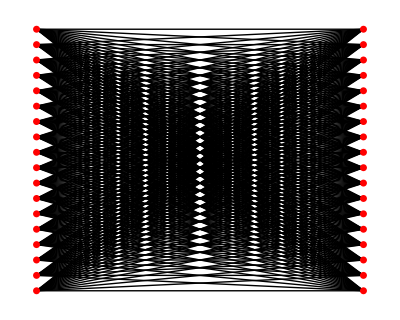

```mathematica
GraphPlot[CompleteGraph[18,18],Method->None,AspectRatio->.8]
```

## Properties m×n

### Acyclic

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{True,Min[m,n]==1}},False],GraphData[#,"Acyclic"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### AdjacencyMatrixCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Multinomial[m,n]/Piecewise[{{2,m==n}},1],GraphData[#,"AdjacencyMatrixCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

```mathematica
Multinomial[n,n]
```

Binomial[2 n,n]

### Arboricity

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Ceiling[(m n)/(m+n-1)],GraphData[#,"Arboricity"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### ArcTransitive

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{True,m==n}},False],GraphData[#,"ArcTransitive"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### ArcTransitivity

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{1,m==n==1},{Infinity,m==n==2},{3,m==n}},Missing["NotApplicable"]],GraphData[#,"ArcTransitivity"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### AutomorphismCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{2m !n !,m==n}},m !n !],GraphData[#,"AutomorphismCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### BalabanIndex

```mathematica
Entity["Graph",{"CompleteBipartite",{n,n}}]["BalabanIndex"]
```

n^4/((-2+3 n) (2-2 n+n^2))

```mathematica
FullSimplify[(m^2 n^2)/((2+m (-1+n)-n) √((-2+2 m+n) (-2+m+2 n)))/.m->n,n>0&&n∈Integers]//Factor
```

n^4/((-2+3 n) (2-2 n+n^2))

```mathematica
Table[GraphData[{"CompleteBipartite",{m,n}},"BalabanIndex"]^2,{n,20},{m,n}]//Column
```

{1}
{8/3,4}
{27/5,24/5,6561/1225}
{64/7,16/3,288/49,4096/625}
{125/9,40/7,625/99,40000/5577,390625/48841}
{216/11,6,52488/7865,54/7,3000/343,6561/676}
{343/13,56/9,64827/9295,38416/4693,2401/255,172872/16337,5764801/494209}
{512/15,32/5,3072/425,65536/7623,160000/15979,512/45,351232/27735,1048576/75625}
{729/17,72/11,531441/71383,139968/15625,151875/14399,4251528/351329,2187/161,124416/8303,43046721/2640625}
{1000/19,20/3,135000/17689,5000/539,3125000/283383,6750/529,19208/1331,625/39,1215000/69277,1562500/82369}
{1331/21,88/13,43923/5635,468512/49011,366025/31939,351384/26299,35153041/2310741,14992384/882175,14641/783,14641000/720447,214358881/9803161}
{1728/23,48/7,104976/13225,36864/3757,320/27,52488/3773,2074464/130181,196608/10985,34012224/1718857,108/5,31944/1369,26873856/1075369}
{2197/25,104/15,85683/10625,1827904/182077,17850625/1462209,6169176/427915,68574961/4129975,3655808/195075,62462907/3001471,142805000/6261287,28561/1155,16451136/619115,815730721/28783225}
{2744/27,7,19208/2349,19208/1875,12005000/957869,7203/484,46118408/2677389,175616/8993,13608/625,1500625/62658,281224328/10794269,4802/171,42199976/1404993,5764801/180625}
{3375/29,120/17,4100625/495349,135000/12943,1171875/91333,1312200/85697,5145/289,640000/31581,332150625/14646043,84375000/3370961,5490375/201019,1049760/35557,16875/533,5145000/152561,2562890625/71757841}
{4096/31,64/9,442368/52855,1048576/98923,1024000/78141,73728/4693,114688/6253,16777216/800565,4478976/190333,128000/4913,239878144/8413569,28311552/916237,233971712/7043615,8192/231,18432000/489731,268435456/6754801}
{4913/33,136/19,250563/29645,5345344/497007,83521/6253,668168/41553,200533921/10641579,42762752/1979195,20295603/833899,3340840/123627,1222830961/41240311,16036032/497783,2385443281/68724405,1604271368/43200509,83521/2115,342102016/8189421,6975757441/158583649}
{5832/35,36/5,4251528/498575,34992/3211,1215000/89401,1062882/64715,42007896/2174845,3888/175,344373768/13720139,1822500/65219,1054152/34295,8503056/254035,499703256/13826225,583443/15059,2657205000/64375367,2187/50,9550872/207025,172186884/3553225}
{6859/37,152/21,3518667/409331,4170272/378125,81450625/5899203,28149336/1681043,312900721/15837373,133448704/5854827,95004009/3679375,651605000/22610219,1908029761/60050913,56298672/1623641,3722098081/99216523,2503205768/62128125,2199166875/51143191,2135179264/46781917,130321/2703,253344024/4995197,16983563041/319515625}
{8000/39,80/11,60000/6929,2560000/229593,25000000/1784629,375/22,96040/4761,40960000/1755199,360000/13583,3125000/105393,58564000/1787569,12288/343,1142440000/29419401,12005000/287339,18750000/419813,26214400/552123,26726720/532103,10000/189,137180000/2470629,1600000000/27552001}

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],(m^2 n^2)/((2+m (-1+n)-n) √((-2+2 m+n) (-2+m+2 n))),GraphData[#,"BalabanIndex"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

```mathematica
mn=MapIndexed[Factor@FindSequenceFunction[#,n-#2[[1]]]&,Table[GraphData[{"CompleteBipartite",{n,m}},"BalabanIndex"]^2,{n,2,11},{m,n,20}]]
```

{(8 n)/(2+n),(81 n^4)/((4+n) (-1+2 n)^2 (1+2 n)),(128 n^4)/((1+n) (6+n) (-2+3 n)^2),(625 n^4)/((8+n) (3+2 n) (-3+4 n)^2),(648 n^4)/((2+n) (10+n) (-4+5 n)^2),(2401 n^4)/((12+n) (5+2 n) (-5+6 n)^2),(2048 n^4)/((3+n) (14+n) (-6+7 n)^2),(6561 n^4)/((16+n) (7+2 n) (-7+8 n)^2),(5000 n^4)/((4+n) (18+n) (-8+9 n)^2),(14641 n^4)/((20+n) (9+2 n) (-9+10 n)^2)}

```mathematica
FindSequenceFunction[mn,m-1]//Factor
```

(m^4 n^4)/((-2+2 m+n) (-2+m+2 n) (2-m-n+m n)^2)

```mathematica
Table[(m^4 n^4)/((-2+2 m+n) (-2+m+2 n) (2-m-n+m n)^2),{m,9}]
```

{n^3/(-1+2 n),(8 n)/(2+n),(81 n^4)/((4+n) (-1+2 n)^2 (1+2 n)),(256 n^4)/((6+n) (2+2 n) (-2+3 n)^2),(625 n^4)/((8+n) (3+2 n) (-3+4 n)^2),(1296 n^4)/((10+n) (4+2 n) (-4+5 n)^2),(2401 n^4)/((12+n) (5+2 n) (-5+6 n)^2),(4096 n^4)/((14+n) (6+2 n) (-6+7 n)^2),(6561 n^4)/((16+n) (7+2 n) (-7+8 n)^2)}

```mathematica
FullSimplify[√((m^4 n^4)/((-2+2 m+n) (-2+m+2 n) (2-m-n+m n)^2)),m>0&&n>0&&(m|n)∈Integers]
```

(m^2 n^2)/((2+m (-1+n)-n) √((-2+2 m+n) (-2+m+2 n)))

### Bandwidth

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Floor[(Max[m,n]-1)/2]+Min[m,n],GraphData[#,"Bandwidth"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### BridgeCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{Max[m,n],Min[m,n]==1}},0],GraphData[#,"BridgeCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### BurningNumber

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{2,Min[m,n]<3}},3],GraphData[#,"BurningNumber"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### CharacteristicPolynomial

```mathematica
DeleteCases[{#1,FullSimplify[#2/#3]}&@@@(Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],((#^2-m n) #^(m+n-2)&)[x],GraphData[#,"CharacteristicPolynomial"][x]}]&/@GraphData["CompleteBipartite"]),{_,-1|1}]
```

{}

### ChordCount

```mathematica
Entity["Graph",{"CompleteBipartite",{n,n}}]["ChordCount"]
```

n^2

```mathematica
Entity["Graph",{"CompleteBipartite",{m,n}}]["ChordCount"]
```

Piecewise[{{0, Min[m,n]<3}, {m n, True}}]

```mathematica
Chords[GraphData["K3,11"]]
```

{{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},{3,14}}

```mathematica
Length[%]
```

33

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{0,Min[m,n]<3}},m n],GraphData[#,"ChordCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### ChordlessCycleCount

```mathematica
Entity["Graph",{"CompleteBipartite",{n,n}}]["ChordlessCycleCount"]
```

1/4 (-1+n)^2 n^2

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Binomial[m,2]Binomial[n,2],GraphData[#,"ChordlessCycleCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### ChromaticInvariant

A291774

```mathematica
Entity["Graph",{"CompleteBipartite",{n,n}}]["ChromaticInvariant"]
```

(k !)^2 StirlingS2[-1+n,k]^2k0-1+n

```mathematica
Table[GraphData[{"CompleteBipartite",Sort[{m,n}]},"ChromaticInvariant"],{n,20},{m,n}]//Column
```

{1}
{0,1}
{0,1,5}
{0,1,13,73}
{0,1,29,301,2069}
{0,1,61,1081,11581,95401}
{0,1,125,3613,57749,673261,6487445}
{0,1,253,11593,268381,4306681,55213453,610093513}
{0,1,509,36301,1191989,25794781,431525429,6077248381,75796724309}
{0,1,1021,111961,5136061,147587401,3173843821,56153444761,864806272861,12020754177001}
{0,1,2045,342013,21674069,817232461,22326100565,490572457453,9225829672949,154546274524621,2369364111428885}
{0,1,4093,1038313,90136861,4418144281,151889090893,4106439430633,93448369324861,1869846517285561,33888536448984493,568128719132038153}
{0,1,8189,3139501,370971509,23463601981,1007306792309,33251754479581,908745588526229,21559597141833661,458573272750623029,8947078682269788061,162835627057766030549}
{0,1,16381,9467641,1515362941,122945495401,6549670452781,262306977299641,8554645060301341,239137661832942601,5932903010253399181,133903926852551495641,2799695104458699823741,54975855375379966645801}
{0,1,32765,28501213,6156291989,637647519661,41933247534485,2026531167570253,78446066847254069,2570081553908997421,73982762491005330005,1921573526109427994893,45920112582663637759349,1024643603025242953241581,21593185551426744571090325}
{0,1,65533,85700233,24910507741,3281152493881,265206551569933,15395989902482953,704127171279007741,26912958698815974361,894814136479939137133,26626064123635339960873,724025274810002490446941,18277994552180798277755641,433644326672781463133469133,9762238510837560633366673993}
{0,1,131069,257493901,100499688629,16781135073181,1661018380446389,115383205837585981,6209966928192705749,275806395252948818461,10549739802717014792309,358226273517066097790461,11041228998389732442952469,314143873356937121102290141,8358812536644162842696155829,210148085257002091986402929341,5033241437347149354018370856789}
{0,1,262141,773268121,404575004221,85418322539401,10322040623356141,855137748481231321,53975183487266432221,2775905117587493404201,121730245943744093752141,4700616107872624063094521,163659017568185463504764221,5230148059547258941691325001,155554322264742641729706388141,4352946840269142576951493917721,115616626098839379425772929720221,2935535817121864789830332734621801}
{0,1,524285,2321377213,1626035319509,433175707054861,63740215708501205,6279793166445447853,463464292005872156789,27516835084033917422221,1379170150016821201195925,60379077135095499645418093,2367426841031645196357369269,84723494027797242362945179981,2808187054158348308927739487445,87209003168976488607346422661933,2561164812426416124280526883784949,71669458662993074111355737961904141,1922890716579114867777987881576927765}
{0,1,1048573,6967277353,6527360293021,2190315500475481,391594976594554573,45767649997035410473,3939195853373081209021,269274479023865926631161,15383701018359782072259373,761483229766218761587038793,33533414673512842190960168221,1340256300524223454302217199641,49374464676937997709007697976973,1697146468573112568016067454942313,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],1405654243812156374924577160643616721033}

```mathematica
Table[GraphData[{"CompleteBipartite",Sort[{m,n}]},"ChromaticInvariant"],{n,10},{m,n}]//Flatten
```

{1,0,1,0,1,5,0,1,13,73,0,1,29,301,2069,0,1,61,1081,11581,95401,0,1,125,3613,57749,673261,6487445,0,1,253,11593,268381,4306681,55213453,610093513,0,1,509,36301,1191989,25794781,431525429,6077248381,75796724309,0,1,1021,111961,5136061,147587401,3173843821,56153444761,864806272861,12020754177001}

```mathematica
Join[{1},Table[Sum[k !(-1)^(k+m)(k+1)^n StirlingS2[m,k+2],{k,0,m-1}],{n,2,10},{m,n}]]//Flatten
```

{1,0,1,0,1,5,0,1,13,73,0,1,29,301,2069,0,1,61,1081,11581,95401,0,1,125,3613,57749,673261,6487445,0,1,253,11593,268381,4306681,55213453,610093513,0,1,509,36301,1191989,25794781,431525429,6077248381,75796724309,0,1,1021,111961,5136061,147587401,3173843821,56153444761,864806272861,12020754177001}

```mathematica
Table[Piecewise[{{1,m==n==1}},Sum[k !(-1)^(k+Min[m,n])(k+1)^Max[m,n] StirlingS2[Min[m,n],k+2],{k,0,Min[m,n]-1}]],{n,20},{m,n}]//Column
```

{1}
{0,1}
{0,1,5}
{0,1,13,73}
{0,1,29,301,2069}
{0,1,61,1081,11581,95401}
{0,1,125,3613,57749,673261,6487445}
{0,1,253,11593,268381,4306681,55213453,610093513}
{0,1,509,36301,1191989,25794781,431525429,6077248381,75796724309}
{0,1,1021,111961,5136061,147587401,3173843821,56153444761,864806272861,12020754177001}
{0,1,2045,342013,21674069,817232461,22326100565,490572457453,9225829672949,154546274524621,2369364111428885}
{0,1,4093,1038313,90136861,4418144281,151889090893,4106439430633,93448369324861,1869846517285561,33888536448984493,568128719132038153}
{0,1,8189,3139501,370971509,23463601981,1007306792309,33251754479581,908745588526229,21559597141833661,458573272750623029,8947078682269788061,162835627057766030549}
{0,1,16381,9467641,1515362941,122945495401,6549670452781,262306977299641,8554645060301341,239137661832942601,5932903010253399181,133903926852551495641,2799695104458699823741,54975855375379966645801}
{0,1,32765,28501213,6156291989,637647519661,41933247534485,2026531167570253,78446066847254069,2570081553908997421,73982762491005330005,1921573526109427994893,45920112582663637759349,1024643603025242953241581,21593185551426744571090325}
{0,1,65533,85700233,24910507741,3281152493881,265206551569933,15395989902482953,704127171279007741,26912958698815974361,894814136479939137133,26626064123635339960873,724025274810002490446941,18277994552180798277755641,433644326672781463133469133,9762238510837560633366673993}
{0,1,131069,257493901,100499688629,16781135073181,1661018380446389,115383205837585981,6209966928192705749,275806395252948818461,10549739802717014792309,358226273517066097790461,11041228998389732442952469,314143873356937121102290141,8358812536644162842696155829,210148085257002091986402929341,5033241437347149354018370856789}
{0,1,262141,773268121,404575004221,85418322539401,10322040623356141,855137748481231321,53975183487266432221,2775905117587493404201,121730245943744093752141,4700616107872624063094521,163659017568185463504764221,5230148059547258941691325001,155554322264742641729706388141,4352946840269142576951493917721,115616626098839379425772929720221,2935535817121864789830332734621801}
{0,1,524285,2321377213,1626035319509,433175707054861,63740215708501205,6279793166445447853,463464292005872156789,27516835084033917422221,1379170150016821201195925,60379077135095499645418093,2367426841031645196357369269,84723494027797242362945179981,2808187054158348308927739487445,87209003168976488607346422661933,2561164812426416124280526883784949,71669458662993074111355737961904141,1922890716579114867777987881576927765}
{0,1,1048573,6967277353,6527360293021,2190315500475481,391594976594554573,45767649997035410473,3939195853373081209021,269274479023865926631161,15383701018359782072259373,761483229766218761587038793,33533414673512842190960168221,1340256300524223454302217199641,49374464676937997709007697976973,1697146468573112568016067454942313,54965694933593298797800350026314621,1690766455564268364788957864418820921,49722377429683100811983787100371003373,1405654243812156374924577160643616721033}

```mathematica
DeleteCases[Block[{m,n},{
{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],
Piecewise[{{1,m==n==1}},Sum[k !(-1)^(k+Min[m,n])(k+1)^Max[m,n] StirlingS2[Min[m,n],k+2],{k,0,Min[m,n]-1}]],
GraphData[#,"ChromaticInvariant"]
}]&/@GraphData["CompleteBipartite"],
{_,x_,x_}]
```

{{{17,20},54965694933593298797800350026314621,Missing[NotAvailable]},{{18,20},1690766455564268364788957864418820921,Missing[NotAvailable]},{{19,20},49722377429683100811983787100371003373,Missing[NotAvailable]}}

```mathematica
deletefromfirstmissing[l_]:=Take[l,FirstPosition[l,_Missing,{Length[l]+1}][[1]]-1]
```

```mathematica
(mn=MapIndexed[Factor@FindSequenceFunction[deletefromfirstmissing@#,n-1]&,Table[GraphData[{"CompleteBipartite",Sort[{n,m}]},"ChromaticInvariant"],{n,2,11},{m,2,20}]])//Column
```

1
-3+2^n
7-3 2^(1+n)+2 3^n
-15+25 2^n+3 2^(1+2 n)-20 3^n
31-45 2^(1+n)-45 2^(1+2 n)+130 3^n+24 5^n
-63+301 2^n+105 2^(3+2 n)-700 3^n+5 2^(3+n) 3^(1+n)-504 5^n
127-483 2^(1+n)-1575 2^(2+2 n)-35 2^(5+n) 3^(1+n)+14 3^(5+n)+6384 5^n+720 7^n
-255+3025 2^n+20853 2^(1+2 n)+315 2^(4+3 n)-5180 3^(1+n)+385 2^(4+n) 3^(2+n)-63504 5^n-25920 7^n
511-4665 2^(1+n)-127575 2^(1+2 n)-14175 2^(4+3 n)+68210 3^n-1225 2^(6+n) 3^(2+n)+4480 3^(2+2 n)+547848 5^n+540000 7^n
FindSequenceFunction[{1,2045,342013,21674069,817232461,22326100565,490572457453,9225829672949,154546274524621,2369364111428885,33888536448984493,458573272750623029,5932903010253399181,73982762491005330005,894814136479939137133,10549739802717014792309,121730245943744093752141,1379170150016821201195925,15383701018359782072259373},-1+n]

```mathematica
{
1,
-3+2^n,
7-6 2^n+2 3^n,
-15+25 2^n-20 3^n+6 4^n,
31-90 2^n+130 3^n-90 4^n+24 5^n,
-63+301 2^n-700 3^n+840 4^n-504 5^n+120 6^n
}
```

```mathematica
Table[StirlingS2[n,1],{n,10}]
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
Table[StirlingS2[n,2],{n,10}]
```

{0,1,3,7,15,31,63,127,255,511}

```mathematica
Table[StirlingS2[n,3],{n,10}]
```

{0,0,1,6,25,90,301,966,3025,9330}

```mathematica
2 !Table[StirlingS2[n,4],{n,10}]
```

{0,0,0,2,20,130,700,3402,15540,68210}

```mathematica
3 !Table[StirlingS2[n,5],{n,10}]
```

{0,0,0,0,6,90,840,6300,41706,255150}

```mathematica
Table[Sum[k !(-1)^(k+m)(k+1)^n StirlingS2[m,k+2],{k,0,m-1}],{n,5},{m,n}]
```

{{0},{0,1},{0,1,5},{0,1,13,73},{0,1,29,301,2069}}

```mathematica
Sum[k !(-1)^(k+m)(k+1)^n StirlingS2[m,k+2],{k,0,m-1}]
```

∑_(k=0)^(-1+m) (-1)^(k+m) (1+k)^n k ! StirlingS2[m,2+k]

```mathematica
(r=MapIndexed[FindLinearRecurrence[deletefromfirstmissing@#]&,Table[GraphData[{"CompleteBipartite",Sort[{n,m}]},"ChromaticInvariant"],{n,11},{m,2,20}]])//Column
```

{1}
{1}
{3,-2}
{6,-11,6}
{10,-35,50,-24}
{15,-85,225,-274,120}
{21,-175,735,-1624,1764,-720}
{28,-322,1960,-6769,13132,-13068,5040}
{36,-546,4536,-22449,67284,-118124,109584,-40320}
{45,-870,9450,-63273,269325,-723680,1172700,-1026576,362880}
FindLinearRecurrence[{1,2045,342013,21674069,817232461,22326100565,490572457453,9225829672949,154546274524621,2369364111428885,33888536448984493,458573272750623029,5932903010253399181,73982762491005330005,894814136479939137133,10549739802717014792309,121730245943744093752141,1379170150016821201195925,15383701018359782072259373}]

```mathematica
-Rest/@Table[StirlingS1[n,n+1-k],{n,10},{k,n}]//Column
```

{}
{1}
{3,-2}
{6,-11,6}
{10,-35,50,-24}
{15,-85,225,-274,120}
{21,-175,735,-1624,1764,-720}
{28,-322,1960,-6769,13132,-13068,5040}
{36,-546,4536,-22449,67284,-118124,109584,-40320}
{45,-870,9450,-63273,269325,-723680,1172700,-1026576,362880}

### ChromaticNumber

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],2,GraphData[#,"ChromaticNumber"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### ChromaticPolynomial

```mathematica
Table[GraphData[{"CompleteBipartite",Sort[{m,n}]},"ChromaticPolynomial"][x],{n,5},{m,n}]//Column
```

{(-1+x) x}
{(-1+x)^2 x,(-1+x) x (3-3 x+x^2)}
{(-1+x)^3 x,(-1+x) x (-7+10 x-5 x^2+x^3),(-1+x) x (31-47 x+28 x^2-8 x^3+x^4)}
{(-1+x)^4 x,(-1+x) x (15-29 x+21 x^2-7 x^3+x^4),(-1+x) x (-115+204 x-147 x^2+55 x^3-11 x^4+x^5),(-1+x) x (675-1255 x+981 x^2-419 x^3+105 x^4-15 x^5+x^6)}
{(-1+x)^5 x,(-1+x) x (-31+76 x-74 x^2+36 x^3-9 x^4+x^5),(-1+x) x (391-817 x+711 x^2-334 x^3+91 x^4-14 x^5+x^6),(-1+x) x (-3451+7038 x-6148 x^2+3016 x^3-909 x^4+171 x^5-19 x^6+x^7),(-1+x) x (25231-53379 x+49166 x^2-26004 x^3+8726 x^4-1924 x^5+276 x^6-24 x^7+x^8)}

```mathematica
Table[Factor/@Piecewise[{{1,m==n==1}},x(x-1)Sum[x^(k+1)k !(-1)^(k+Min[m,n])(k+1)^Max[m,n] StirlingS2[Min[m,n],k+2],{k,0,Min[m,n]-1}]],{n,5},{m,n}]//Column
```

{1}
{0,(-1+x) x^2}
{0,(-1+x) x^2,(-1+x) x^2 (-3+8 x)}
{0,(-1+x) x^2,(-1+x) x^2 (-3+16 x),(-1+x) x^2 (7-96 x+162 x^2)}
{0,(-1+x) x^2,(-1+x) x^2 (-3+32 x),(-1+x) x^2 (7-192 x+486 x^2),(-1+x) x^2 (-15+800 x-4860 x^2+6144 x^3)}

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],XXX,GraphData[#,"ChromaticPolynomial"][x]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{{{1,3},XXX,(-1+x)^3 x},{{2,3},XXX,(-1+x) x (-7+10 x-5 x^2+x^3)},{{2,4},XXX,(-1+x) x (15-29 x+21 x^2-7 x^3+x^4)},{{2,5},XXX,(-1+x) x (-31+76 x-74 x^2+36 x^3-9 x^4+x^5)},{{2,6},XXX,(-1+x) x (63-187 x+230 x^2-150 x^3+55 x^4-11 x^5+x^6)},{{2,7},XXX,(-1+x) x (-127+442 x-657 x^2+540 x^3-265 x^4+78 x^5-13 x^6+x^7)},{{2,8},XXX,(-1+x) x (3-3 x+x^2) (85-254 x+308 x^2-193 x^3+66 x^4-12 x^5+x^6)},{{2,9},XXX,(-1+x) x (-511+2296 x-4580 x^2+5320 x^3-3962 x^4+1960 x^5-644 x^6+136 x^7-17 x^8+x^9)},{{2,10},XXX,(-1+x) x (1023-5111 x+11484 x^2-15276 x^3+13314 x^4-7938 x^5+3276 x^6-924 x^7+171 x^8-19 x^9+x^10)},{{3,4},XXX,(-1+x) x (-115+204 x-147 x^2+55 x^3-11 x^4+x^5)},{{3,5},XXX,(-1+x) x (391-817 x+711 x^2-334 x^3+91 x^4-14 x^5+x^6)},{{3,6},XXX,(-1+x) x (-1267+3074 x-3178 x^2+1825 x^3-635 x^4+136 x^5-17 x^6+x^7)},{{3,7},XXX,(-1+x) x (3991-11055 x+13308 x^2-9113 x^3+3900 x^4-1077 x^5+190 x^6-20 x^7+x^8)},{{3,8},XXX,(-1+x) x (-12355+38488 x-52965 x^2+42287 x^3-21623 x^4+7371 x^5-1687 x^6+253 x^7-23 x^8+x^9)},{{3,9},XXX,(-1+x) x (37831-130877 x+202717 x^2-185132 x^3+110446 x^4-45038 x^5+12754 x^6-2492 x^7+325 x^8-26 x^9+x^10)},{{3,10},XXX,(-1+x) x (-115027+437358 x-752796 x^2+774129 x^3-528426 x^4+251496 x^5-85260 x^6+20646 x^7-3519 x^8+406 x^9-29 x^10+x^11)},{{4,4},XXX,(-1+x) x (675-1255 x+981 x^2-419 x^3+105 x^4-15 x^5+x^6)},{{4,5},XXX,(-1+x) x (-3451+7038 x-6148 x^2+3016 x^3-909 x^4+171 x^5-19 x^6+x^7)},{{4,6},XXX,(-1+x) x (16275-36813 x+36198 x^2-20364 x^3+7235 x^4-1681 x^5+253 x^6-23 x^7+x^8)},{{4,7},XXX,(-1+x) x (-72955+182724 x-201603 x^2+129214 x^3-53339 x^4+14820 x^5-2799 x^6+351 x^7-27 x^8+x^9)},{{4,8},XXX,(-1+x) x (316275-871955 x+1071627 x^2-775317 x^3+367045 x^4-119399 x^5+27209 x^6-4327 x^7+465 x^8-31 x^9+x^10)},{{4,9},XXX,(-1+x) x (-1340251+4039098 x-5483358 x^2+4433680 x^3-2377610 x^4+890596 x^5-238784 x^6+46096 x^7-6329 x^8+595 x^9-35 x^10+x^11)},{{4,10},XXX,(-1+x) x (5590035-18291097 x+27207180 x^2-24350206 x^3+14622714 x^4-6218118 x^5+1924860 x^6-438672 x^7+73431 x^8-8869 x^9+741 x^10-39 x^11+x^12)},{{5,5},XXX,(-1+x) x (25231-53379 x+49166 x^2-26004 x^3+8726 x^4-1924 x^5+276 x^6-24 x^7+x^8)},{{5,6},XXX,(-1+x) x (-164731+371060 x-368175 x^2+212870 x^3-79680 x^4+20201 x^5-3504 x^6+406 x^7-29 x^8+x^9)},{{5,7},XXX,(-1+x) x (999391-2419841 x+2606855 x^2-1655175 x^3+690250 x^4-198911 x^5+40426 x^6-5774 x^7+561 x^8-34 x^9+x^10)},{{5,8},XXX,(-1+x) x (-5767051+15038602 x-17606526 x^2+12268720 x^3-5680155 x^4+1844171 x^5-430997 x^6+73011 x^7-8859 x^8+741 x^9-39 x^10+x^11)},{{5,9},XXX,(-1+x) x (32122831-90069583 x+114326028 x^2-87134986 x^3+44561635 x^4-16170866 x^5+4288648 x^6-841928 x^7+122191 x^8-12884 x^9+946 x^10-44 x^11+x^12)},{{5,10},XXX,(-1+x) x (-174397531+524181984 x-718583401 x^2+596215734 x^3-334843601 x^4+134782161 x^5-40132734 x^6+8984856 x^7-1519509 x^8+192826 x^9-17974 x^10+1176 x^11-49 x^12+x^13)},{{6,6},XXX,(-1+x) x (1441923-3345251 x+3451675 x^2-2101005 x^3+841440 x^4-233382 x^5+45760 x^6-6320 x^7+595 x^8-35 x^9+x^10)},{{6,7},XXX,(-1+x) x (-11467387+27862826 x-30350946 x^2+19686320 x^3-8499405 x^4+2580474 x^5-565823 x^6+90245 x^7-10345 x^8+820 x^9-41 x^10+x^11)},{{6,8},XXX,(-1+x) x (85314915-218764921 x+253306964 x^2-176020726 x^3+82163385 x^4-27278943 x^5+6640711 x^6-1201229 x^7+161285 x^8-15795 x^9+1081 x^10-47 x^11+x^12)},{{6,9},XXX,(-1+x) x (-604907611+1641506000 x-2024942257 x^2+1509613342 x^3-761875151 x^4+276000736 x^5-74158286 x^6+15033676 x^7-2311475 x^8+267805 x^9-22886 x^10+1378 x^11-53 x^12+x^13)},{{6,10},XXX,(-1+x) x (4138663683-11887746255 x+15618785385 x^2-12481129655 x^3+6798521505 x^4-2678941863 x^5+790251054 x^6-177949386 x^7+30866949 x^8-4123861 x^9+420026 x^10-31834 x^11+1711 x^12-59 x^13+x^14)},{{7,7},XXX,(-1+x) x (116914351-291098863 x+327026036 x^2-220478866 x^3+99908145 x^4-32232549 x^5+7634054 x^6-1345294 x^7+176205 x^8-16855 x^9+1128 x^10-48 x^11+x^12)},{{7,8},XXX,(-1+x) x (-1096832395+2831050768 x-3316231093 x^2+2346439606 x^3-1124432771 x^4+387229696 x^5-99070167 x^6+19161059 x^7-2816575 x^8+312635 x^9-25647 x^10+1485 x^11-55 x^12+x^13)},{{7,9},XXX,(-1+x) x (9682617631-26065935981 x+32018974701 x^2-23895185237 x^3+12155013801 x^4-4476781197 x^5+1236249175 x^6-261135638 x^7+42590899 x^8-5363756 x^9+516265 x^10-37064 x^11+1891 x^12-62 x^13+x^14)},{{7,10},XXX,(-1+x) x (-81653389147+229912363830 x-296920163940 x^2+234195979920 x^3-126624880760 x^4+49886608380 x^5-14846581918 x^6+3411039969 x^7-612318051 x^8+86233414 x^9-9492573 x^10+806226 x^11-51449 x^12+2346 x^13-69 x^14+x^15)},{{8,8},XXX,(-1+x) x (12764590275-33636259455 x+40411429009 x^2-29486947847 x^3+14666712333 x^4-5284072731 x^5+1428222621 x^6-295504995 x^7+47247529 x^8-5837951 x^9+551761 x^10-38927 x^11+1953 x^12-63 x^13+x^14)},{{8,9},XXX,(-1+x) x (-138027417451+374477540422 x-465261317256 x^2+352767907688 x^3-183324693188 x^4+69445334616 x^5-19887439768 x^6+4401401344 x^7-762028109 x^8+103643071 x^9-11033477 x^10+907459 x^11-56147 x^12+2485 x^13-71 x^14+x^15)},{{8,10},XXX,(-1+x) x (1411532175075-3962153027525 x+5114811739242 x^2-4047361073960 x^3+2205626432940 x^4-880876395644 x^5+267626633232 x^6-63313921448 x^7+11828531019 x^8-1757290861 x^9+207716131 x^10-19411245 x^11+1412621 x^12-77819 x^13+3081 x^14-79 x^15+x^16)},{{9,9},XXX,(-1+x) x (1805409270031-4986572768987 x+6329431290970 x^2-4922594670848 x^3+2636244049180 x^4-1034766428612 x^5+309063583360 x^6-71908687592 x^7+13218635710 x^8-1933329500 x^9+225103312 x^10-20732768 x^11+1487836 x^12-80864 x^13+3160 x^14-80 x^15+x^16)},{{9,10},XXX,(-1+x) x (-22111390122811+62573816808444 x-81660471428859 x^2+65541192996414 x^3-36371315993580 x^4+14862113644392 x^5-4646036277708 x^6+1138631902776 x^7-222194241828 x^8+34835725009 x^9-4402836548 x^10+447659380 x^11-36310232 x^12+2310406 x^13-111944 x^14+3916 x^15-89 x^16+x^17)},{{10,10},XXX,(-1+x) x (321113303226243-923089548946939 x+1227093243034311 x^2-1006338560738529 x^3+572638492030446 x^4-240903562915548 x^5+77896060510212 x^6-19855223828628 x^7+4056409315962 x^8-671185141778 x^9+90432142596 x^10-9929440044 x^11+884862636 x^12-63364644 x^13+3580776 x^14-154824 x^15+4851 x^16-99 x^17+x^18)},{{11,11},XXX,(-1+x) x (70146437009397871-208749223691769639 x+288729910890239072 x^2-247719351143767150 x^3+148351294532266035 x^4-66120351346901103 x^5+22821931063081602 x^6-6263365482278640 x^7+1391729073924630 x^8-253484232265670 x^9+38146597238564 x^10-4763599193374 x^11+494048179890 x^12-42441408360 x^13+2999323680 x^14-172246524 x^15+7878795 x^16-277815 x^17+7140 x^18-120 x^19+x^20)},{{12,12},XXX,(-1+x) x (18462286083671614275-56639755516316503895 x+81101555907758708509 x^2-72356649720441332059 x^3+45277770436045982747 x^4-21198058972407488545 x^5+7730788379629820043 x^6-2256574925379020565 x^7+537313967611477320 x^8-105785573553376310 x^9+17384404084436554 x^10-2399664719334302 x^11+279202458260352 x^12-27406531142364 x^13+2265549142560 x^14-156952850208 x^15+9034102803 x^16-426116823 x^17+16120885 x^18-472835 x^19+10153 x^20-143 x^21+x^22)},{{13,13},XXX,(-1+x) x (5762225835975165678031-18163020521553267821395 x+26816297106495032648006 x^2-24761290657167302713916 x^3+16100364183494064777798 x^4-7866325785322880228430 x^5+3007932507683820616680 x^6-925384112495831023684 x^7+233590912106055398961 x^8-49076147663128051829 x^9+8671562099000261670 x^10-1298329892140034064 x^11+165549275816328704 x^12-18029672232548222 x^13+1678601160893580 x^14-133438411033004 x^15+9025180867197 x^16-516099393315 x^17+24706585398 x^18-975481012 x^19+31059666 x^20-770132 x^21+14028 x^22-168 x^23+x^24)},{{14,14},XXX,(-1+x) x (2104263061425865873128963-6796285936247804243378067 x+10312828834531949699241619 x^2-9818093039186382362233653 x^3+6604224586157434225899988 x^4-3350021218471851926290938 x^5+1335103286485251585742154 x^6-429907099733458538686638 x^7+114113228077789981596413 x^8-25341251854980319708593 x^9+4760607306646151896793 x^10-762837665470451478687 x^11+104896158353420208450 x^12-12429317453498577348 x^13+1272222258432052278 x^14-112582889509000378 x^15+8606452513349405 x^16-566870428279441 x^17+32018605699795 x^18-1539546407685 x^19+62338646084 x^20-2092470666 x^21+56885816 x^22-1208584 x^23+18915 x^24-195 x^25+x^26)},{{15,15},XXX,(-1+x) x (888881838896989670838028591-2934964265543048353031431775 x+4565035505165207036289524236 x^2-4467022512975144913927836714 x^3+3097305070589363637263037141 x^4-1624429021681584652021339761 x^5+671537417620338212774058410 x^6-225089236229555175172110780 x^7+62430715504271141455872015 x^8-14547643186411866536900895 x^9+2881013473157182398163128 x^10-489200254658962211336790 x^11+71701376079338569252325 x^12-9116412436084339943025 x^13+1008978229900323049290 x^14-97412705570101706698 x^15+8210553199120969697 x^16-603840084603729883 x^17+38673314409301572 x^18-2149201025779808 x^19+103061436649171 x^20-4230091977969 x^21+146905990686 x^22-4246672794 x^23+99773401 x^24-1837199 x^25+24976 x^26-224 x^27+x^28)},{{16,16},XXX,(-1+x) x (430058409024841744606172532675-1448913221431095478498088467375 x+2304878008592571753006447831081 x^2-2312192862335913237086034443311 x^3+1647677180630452036445500304025 x^4-890442826729687576020235240695 x^5+380360914880751684334248620281 x^6-132125629991237506727426944647 x^7+38099870466399186077813994125 x^8-9262241003324774234921491275 x^9+1920942920721893399508760869 x^10-343019256079678481424841083 x^11+53117986860302017520639773 x^12-7172718774104413920011475 x^13+848098054071631762645085 x^14-88065098574440197272483 x^15+8045438655231927234729 x^16-647158896532618798815 x^17+45818684870497138145 x^18-2850995255058208895 x^19+155474516883839153 x^20-7398630525004719 x^21+305329905116145 x^22-10832780313615 x^23+326459933345 x^24-8216759551 x^25+168567105 x^26-2716735 x^27+32385 x^28-255 x^29+x^30)},{{17,17},XXX,(-1+x) x (236266493635025908205564230297231-810895114716100444816145836393803 x+1316774504936754522537665670881714 x^2-1351274467619545127454406755295736 x^3+987174730322823990671770543203040 x^4-548173651906536215153742489164712 x^5+241178150951834045076243901597696 x^6-86509139316743399231611513390800 x^7+25829124680237468519575510212452 x^8-6520509795442359813030284027028 x^9+1408747055360351108804171083496 x^10-262959414180340248476023987536 x^11+42727691363250209547025564952 x^12-6079526453085791572302985080 x^13+760989287712543518230604768 x^14-84093087805361503007739792 x^15+8224480416745109895756158 x^16-713044994253669521998156 x^17+54839439069679249440600 x^18-3740701705823780383200 x^19+226047704437530803464 x^20-12074794578917447312 x^21+568210668687788048 x^22-23440631227534144 x^23+842051149671420 x^24-26100174062352 x^25+689386911472 x^26-15250303712 x^27+275634040 x^28-3921440 x^29+41328 x^30-288 x^31+x^32)},{{18,18},XXX,(-1+x) x (146274453143108013012541808658430083-510702680068776942983445524415832235 x+845182432298097539919707848883030239 x^2-885588177363699393188750001313192457 x^3+661863683026062021709735771670259946 x^4-376745211943891009063255766890729640 x^5+170267347565116842135354194743872784 x^6-62874812332814465810369287877720264 x^7+19371415116980711076340254942271348 x^8-5058881080647228615066383947955652 x^9+1133684068581864049312236484295700 x^10-220136914542172839870250415534412 x^11+37327408357195245250828845836832 x^12-5561609190050224857955593639432 x^13+731763988464871865109313657320 x^14-85357697630553854844499476408 x^15+8853620883422579190918991626 x^16-818376238854785852077517562 x^17+67507450173341593938652108 x^18-4972847760852181816171892 x^19+327095093001722014657792 x^20-19194420313380202412792 x^21+1003110941856466992640 x^22-46559664610479849920 x^23+1911910590430645636 x^24-69089893168649444 x^25+2181508563291328 x^26-59615620163360 x^27+1392033295432 x^28-27287128808 x^29+437904496 x^30-5540912 x^31+52003 x^32-323 x^33+x^34)},{{19,19},XXX,(-1+x) x (101367645575945316491745562082318934511-359587982567968394784568288339143611671 x+605636899957977731580910611800329135928 x^2-646915558628322448246185051464158014822 x^3+493724745157795428222237571244680740711 x^4-287498527732228589421444572415989807043 x^5+133165854329217550401146523340613989026 x^6-50495419131183337938771306206532683064 x^7+16007960223735994662705731858985631140 x^8-4310896451322281492186075086211272108 x^9+998493378658394281409118992198637648 x^10-200890850838699154403135144086271400 x^11+35388937088812025253216298976028540 x^12-5493743878257891376546540940985996 x^13+755503526914599829802833688991288 x^14-92428754410245318163122107868048 x^15+10093467043165228158703195576098 x^16-986428418827493598964702176186 x^17+86439241898853559975449061868 x^18-6800200839366163119296106958 x^19+480582538608572507711099286 x^20-30510021956193738692173716 x^21+1738796681646735523065144 x^22-88833610817450953355160 x^23+4059456939107500449324 x^24-165407091421531671348 x^25+5983868338434153000 x^26-191114464300955572 x^27+5348782612479780 x^28-129897022943880 x^29+2701623286416 x^30-47264944824 x^31+678127671 x^32-7682079 x^33+64620 x^34-360 x^35+x^36)},{{20,20},XXX,(-1+x) x (78159253164064688220205359525103575185475-281401760762081213003658690594267679138695 x+481754206140674267710311522309908137715125 x^2-523853840962133252962269597779819885132419 x^3+407631373632414168878203206360399381692231 x^4-242397479211894464004107636180120029601949 x^5+114844205941194961665879035823154899417351 x^6-44620654613457238753743053329794680496537 x^7+14520034910395417623390746034574170784638 x^8-4021325233366826998954867078956485017612 x^9+959816388711467580069946344723897625324 x^10-199421868998802390208657989211712898060 x^11+36361653231458602069063404018501603596 x^12-5857027441016382111778708656533979684 x^13+837981164867795874614943974715420396 x^14-106967093170390531448403134617623828 x^15+12226474274876429978986902323099970 x^16-1255022330111063185368674515584690 x^17+115954184619638458321307230443910 x^18-9659089322287096569477188671530 x^19+726255111187549550098254351100 x^20-49317218240274283591869222112 x^21+3024688265635760979180624468 x^22-167457959420543532567735852 x^23+8359510778457715120551228 x^24-375595827996312263937780 x^25+15149812482229564086540 x^26-546676022417752169140 x^27+17567223330470322040 x^28-499741837421217440 x^29+12488449474261656 x^30-271402774902504 x^31+5061210779091 x^32-79529891079 x^33+1026370101 x^34-10471299 x^35+79401 x^36-399 x^37+x^38)},{{1,1},XXX,(-1+x) x},{{1,2},XXX,(-1+x)^2 x},{{2,2},XXX,(-1+x) x (3-3 x+x^2)},{{1,4},XXX,(-1+x)^4 x},{{1,5},XXX,(-1+x)^5 x},{{1,6},XXX,(-1+x)^6 x},{{1,7},XXX,(-1+x)^7 x},{{1,8},XXX,(-1+x)^8 x},{{1,9},XXX,(-1+x)^9 x},{{1,10},XXX,(-1+x)^10 x},{{1,11},XXX,(-1+x)^11 x},{{1,12},XXX,(-1+x)^12 x},{{1,13},XXX,(-1+x)^13 x},{{1,14},XXX,(-1+x)^14 x},{{1,15},XXX,(-1+x)^15 x},{{1,16},XXX,(-1+x)^16 x},{{1,17},XXX,(-1+x)^17 x},{{1,18},XXX,(-1+x)^18 x},{{1,19},XXX,(-1+x)^19 x},{{3,3},XXX,(-1+x) x (31-47 x+28 x^2-8 x^3+x^4)}}

```mathematica
Take[poly,5]//Expand//Column
```

-x+x^2
-3 x+6 x^2-4 x^3+x^4
-31 x+78 x^2-75 x^3+36 x^4-9 x^5+x^6
-675 x+1930 x^2-2236 x^3+1400 x^4-524 x^5+120 x^6-16 x^7+x^8
-25231 x+78610 x^2-102545 x^3+75170 x^4-34730 x^5+10650 x^6-2200 x^7+300 x^8-25 x^9+x^10

```mathematica
coef=Factor/@FindLinearRecurrence[poly/(x(x-1))]
```

FindLinearRecurrence[{1,3-3 x+x^2,31-47 x+28 x^2-8 x^3+x^4,675-1255 x+981 x^2-419 x^3+105 x^4-15 x^5+x^6,25231-53379 x+49166 x^2-26004 x^3+8726 x^4-1924 x^5+276 x^6-24 x^7+x^8,1441923-3345251 x+3451675 x^2-2101005 x^3+841440 x^4-233382 x^5+45760 x^6-6320 x^7+595 x^8-35 x^9+x^10,116914351-291098863 x+327026036 x^2-220478866 x^3+99908145 x^4-32232549 x^5+7634054 x^6-1345294 x^7+176205 x^8-16855 x^9+1128 x^10-48 x^11+x^12,12764590275-33636259455 x+40411429009 x^2-29486947847 x^3+14666712333 x^4-5284072731 x^5+1428222621 x^6-295504995 x^7+47247529 x^8-5837951 x^9+551761 x^10-38927 x^11+1953 x^12-63 x^13+x^14,1805409270031-4986572768987 x+6329431290970 x^2-4922594670848 x^3+2636244049180 x^4-1034766428612 x^5+309063583360 x^6-71908687592 x^7+13218635710 x^8-1933329500 x^9+225103312 x^10-20732768 x^11+1487836 x^12-80864 x^13+3160 x^14-80 x^15+x^16,321113303226243-923089548946939 x+1227093243034311 x^2-1006338560738529 x^3+572638492030446 x^4-240903562915548 x^5+77896060510212 x^6-19855223828628 x^7+4056409315962 x^8-671185141778 x^9+90432142596 x^10-9929440044 x^11+884862636 x^12-63364644 x^13+3580776 x^14-154824 x^15+4851 x^16-99 x^17+x^18}]

```mathematica
ToPolynomialRecurrence[p,x,n,coef]
```

p[n,x]==FindLinearRecurrence[{(-1+x) x,(-1+x) x (3-3 x+x^2),(-1+x) x (31-47 x+28 x^2-8 x^3+x^4),(-1+x) x (675-1255 x+981 x^2-419 x^3+105 x^4-15 x^5+x^6),(-1+x) x (25231-53379 x+49166 x^2-26004 x^3+8726 x^4-1924 x^5+276 x^6-24 x^7+x^8),(-1+x) x (1441923-3345251 x+3451675 x^2-2101005 x^3+841440 x^4-233382 x^5+45760 x^6-6320 x^7+595 x^8-35 x^9+x^10),(-1+x) x (116914351-291098863 x+327026036 x^2-220478866 x^3+99908145 x^4-32232549 x^5+7634054 x^6-1345294 x^7+176205 x^8-16855 x^9+1128 x^10-48 x^11+x^12),(-1+x) x (12764590275-33636259455 x+40411429009 x^2-29486947847 x^3+14666712333 x^4-5284072731 x^5+1428222621 x^6-295504995 x^7+47247529 x^8-5837951 x^9+551761 x^10-38927 x^11+1953 x^12-63 x^13+x^14),(-1+x) x (1805409270031-4986572768987 x+6329431290970 x^2-4922594670848 x^3+2636244049180 x^4-1034766428612 x^5+309063583360 x^6-71908687592 x^7+13218635710 x^8-1933329500 x^9+225103312 x^10-20732768 x^11+1487836 x^12-80864 x^13+3160 x^14-80 x^15+x^16),(-1+x) x (321113303226243-923089548946939 x+1227093243034311 x^2-1006338560738529 x^3+572638492030446 x^4-240903562915548 x^5+77896060510212 x^6-19855223828628 x^7+4056409315962 x^8-671185141778 x^9+90432142596 x^10-9929440044 x^11+884862636 x^12-63364644 x^13+3580776 x^14-154824 x^15+4851 x^16-99 x^17+x^18)}].{p[-1+n,x]}

```mathematica
FormattedPolynomialRecurrence[p,x,n,coef]//TraditionalForm
```

```mathematica
TeXForm[%]
```

```mathematica
LinearRecurrence[coef,poly,{2-k0,Length[coef]-k0+1}]
```

```mathematica
FullSimplify[RSolve[Prepend[Table[p[k+k0-1,x]==poly[[k]],{k,Length[coef]}],ToPolynomialRecurrence[p,x,n,coef]],p[n,x],n],n∈Integers&&n>0]
```

```mathematica
gf=Factor[z^k0 FindGeneratingFunction[poly,z]]
```

```mathematica
FullSimplify[SeriesCoefficient[gf,{z,0,n}],n>0]
```

$Aborted

```mathematica
poly2=Table[XXX,{n,20}]
```

```mathematica
FullSimplify[poly2-poly]
```

### Circumference

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{2 Min[m,n],Min[m,n]>1}},Missing["NotApplicable"]],GraphData[#,"Circumference"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### Classes

```mathematica
new=Intersection@@(GraphData[#,"Classes"]&/@GraphData["CompleteBipartite"])
```

{Bicolorable,Bipartite,Class1,CompleteBipartite,Connected,EdgeTransitive,Nonempty,Perfect,Simple,StronglyPerfect,TriangleFree,WeaklyPerfect}

```mathematica
old={"Bicolorable","Bipartite","Class1","CompleteBipartite","Connected","EdgeTransitive","Nonempty","Perfect","Simple","TriangleFree"};
```

### CliqueCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],(m+1)(n+1),GraphData[#,"CliqueCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### CliqueCoveringNumber

```mathematica
Entity["Graph",{"CompleteBipartite",{m,n}}]["CliqueCoveringNumber"]
```

Max[m,n]

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Max[m,n],GraphData[#,"CliqueCoveringNumber"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{{{2,11},11,Missing[NotAvailable]},{{2,12},12,Missing[NotAvailable]},{{2,13},13,Missing[NotAvailable]},{{2,14},14,Missing[NotAvailable]},{{2,15},15,Missing[NotAvailable]},{{2,16},16,Missing[NotAvailable]},{{2,17},17,Missing[NotAvailable]},{{2,18},18,Missing[NotAvailable]},{{2,19},19,Missing[NotAvailable]},{{2,20},20,Missing[NotAvailable]},{{3,11},11,Missing[NotAvailable]},{{3,12},12,Missing[NotAvailable]},{{3,13},13,Missing[NotAvailable]},{{3,14},14,Missing[NotAvailable]},{{3,15},15,Missing[NotAvailable]},{{3,16},16,Missing[NotAvailable]},{{3,17},17,Missing[NotAvailable]},{{3,18},18,Missing[NotAvailable]},{{3,19},19,Missing[NotAvailable]},{{3,20},20,Missing[NotAvailable]},{{4,11},11,Missing[NotAvailable]},{{4,12},12,Missing[NotAvailable]},{{4,13},13,Missing[NotAvailable]},{{4,14},14,Missing[NotAvailable]},{{4,15},15,Missing[NotAvailable]},{{4,16},16,Missing[NotAvailable]},{{4,17},17,Missing[NotAvailable]},{{4,18},18,Missing[NotAvailable]},{{4,19},19,Missing[NotAvailable]},{{4,20},20,Missing[NotAvailable]},{{5,11},11,Missing[NotAvailable]},{{5,12},12,Missing[NotAvailable]},{{5,13},13,Missing[NotAvailable]},{{5,14},14,Missing[NotAvailable]},{{5,15},15,Missing[NotAvailable]},{{5,16},16,Missing[NotAvailable]},{{5,17},17,Missing[NotAvailable]},{{5,18},18,Missing[NotAvailable]},{{5,19},19,Missing[NotAvailable]},{{5,20},20,Missing[NotAvailable]},{{6,11},11,Missing[NotAvailable]},{{6,12},12,Missing[NotAvailable]},{{6,13},13,Missing[NotAvailable]},{{6,14},14,Missing[NotAvailable]},{{6,15},15,Missing[NotAvailable]},{{6,16},16,Missing[NotAvailable]},{{6,17},17,Missing[NotAvailable]},{{6,18},18,Missing[NotAvailable]},{{6,19},19,Missing[NotAvailable]},{{6,20},20,Missing[NotAvailable]},{{7,11},11,Missing[NotAvailable]},{{7,12},12,Missing[NotAvailable]},{{7,13},13,Missing[NotAvailable]},{{7,14},14,Missing[NotAvailable]},{{7,15},15,Missing[NotAvailable]},{{7,16},16,Missing[NotAvailable]},{{7,17},17,Missing[NotAvailable]},{{7,18},18,Missing[NotAvailable]},{{7,19},19,Missing[NotAvailable]},{{7,20},20,Missing[NotAvailable]},{{8,11},11,Missing[NotAvailable]},{{8,12},12,Missing[NotAvailable]},{{8,13},13,Missing[NotAvailable]},{{8,14},14,Missing[NotAvailable]},{{8,15},15,Missing[NotAvailable]},{{8,16},16,Missing[NotAvailable]},{{8,17},17,Missing[NotAvailable]},{{8,18},18,Missing[NotAvailable]},{{8,19},19,Missing[NotAvailable]},{{8,20},20,Missing[NotAvailable]},{{9,11},11,Missing[NotAvailable]},{{9,12},12,Missing[NotAvailable]},{{9,13},13,Missing[NotAvailable]},{{9,14},14,Missing[NotAvailable]},{{9,15},15,Missing[NotAvailable]},{{9,16},16,Missing[NotAvailable]},{{9,17},17,Missing[NotAvailable]},{{9,18},18,Missing[NotAvailable]},{{9,19},19,Missing[NotAvailable]},{{9,20},20,Missing[NotAvailable]},{{10,11},11,Missing[NotAvailable]},{{10,12},12,Missing[NotAvailable]},{{10,13},13,Missing[NotAvailable]},{{10,14},14,Missing[NotAvailable]},{{10,15},15,Missing[NotAvailable]},{{10,16},16,Missing[NotAvailable]},{{10,17},17,Missing[NotAvailable]},{{10,18},18,Missing[NotAvailable]},{{10,19},19,Missing[NotAvailable]},{{10,20},20,Missing[NotAvailable]},{{11,12},12,Missing[NotAvailable]},{{11,13},13,Missing[NotAvailable]},{{11,14},14,Missing[NotAvailable]},{{11,15},15,Missing[NotAvailable]},{{11,16},16,Missing[NotAvailable]},{{11,17},17,Missing[NotAvailable]},{{11,18},18,Missing[NotAvailable]},{{11,19},19,Missing[NotAvailable]},{{11,20},20,Missing[NotAvailable]},{{12,13},13,Missing[NotAvailable]},{{12,14},14,Missing[NotAvailable]},{{12,15},15,Missing[NotAvailable]},{{12,16},16,Missing[NotAvailable]},{{12,17},17,Missing[NotAvailable]},{{12,18},18,Missing[NotAvailable]},{{12,19},19,Missing[NotAvailable]},{{12,20},20,Missing[NotAvailable]},{{13,14},14,Missing[NotAvailable]},{{13,15},15,Missing[NotAvailable]},{{13,16},16,Missing[NotAvailable]},{{13,17},17,Missing[NotAvailable]},{{13,18},18,Missing[NotAvailable]},{{13,19},19,Missing[NotAvailable]},{{13,20},20,Missing[NotAvailable]},{{14,15},15,Missing[NotAvailable]},{{14,16},16,Missing[NotAvailable]},{{14,17},17,Missing[NotAvailable]},{{14,18},18,Missing[NotAvailable]},{{14,19},19,Missing[NotAvailable]},{{14,20},20,Missing[NotAvailable]},{{15,16},16,Missing[NotAvailable]},{{15,17},17,Missing[NotAvailable]},{{15,18},18,Missing[NotAvailable]},{{15,19},19,Missing[NotAvailable]},{{15,20},20,Missing[NotAvailable]},{{16,17},17,Missing[NotAvailable]},{{16,18},18,Missing[NotAvailable]},{{16,19},19,Missing[NotAvailable]},{{16,20},20,Missing[NotAvailable]},{{17,18},18,Missing[NotAvailable]},{{17,19},19,Missing[NotAvailable]},{{17,20},20,Missing[NotAvailable]},{{18,19},19,Missing[NotAvailable]},{{18,20},20,Missing[NotAvailable]},{{19,20},20,Missing[NotAvailable]}}

### CliqueNumber

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],2,GraphData[#,"CliqueNumber"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### CliquePolynomial

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Expand[((m #+1) (n #+1)&)[x]-GraphData[#,"CliquePolynomial"][x]]}]&/@GraphData["CompleteBipartite"],{_,0}]
```

{}

### ComplementOddChordlessCycleCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],0,GraphData[#,"ComplementOddChordlessCycleCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### ConnectedComponentCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],1,GraphData[#,"ConnectedComponentCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### ConnectedDominatingSetCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{3,m==n==1},{2^Max[m,n],Min[m,n]==1}},(2^m-1) (2^n-1)],GraphData[#,"ConnectedDominatingSetCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### ConnectedDominationNumber

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{1,Min[m,n]==1}},2],GraphData[#,"ConnectedDominationNumber"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### ConnectedDominationPolynomial

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Expand[Piecewise[{{2 x+x^2,m==n==1},{x+((x+1)^m-1) ((x+1)^n-1),Min[m,n]==1}},((x+1)^m-1) ((x+1)^n-1)]-GraphData[#,"ConnectedDominationPolynomial"][x]]}]&/@GraphData["CompleteBipartite"],{_,0}]
```

{{{2,11},22 x^2+121 x^3+385 x^4+825 x^5+1254 x^6+1386 x^7+1122 x^8+660 x^9+275 x^10+77 x^11+13 x^12+x^13-Missing[NotAvailable][x]},{{2,12},1},132,{{19,20},380 x^2+7030 x^3+73530 x^4+548625 x^5+3196731 x^6+15253029 x^7+61322196 x^8+211654794 x^9+635468262 x^10+1675812502 x^11+3910621078 x^12+8122320792 x^13+15084454008 x^14+14+635745396 x^29+211915132 x^30+61523748 x^31+15380937 x^32+3262623 x^33+575757 x^34+82251 x^35+9139 x^36+741 x^37+39 x^38+x^39-Missing[NotAvailable][x]}}
 |  |  |  |

### ConnectedInducedSubgraphCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],(2^m-1) (2^n-1)+m+n,GraphData[#,"ConnectedInducedSubgraphCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### ConnectedInducedSubgraphPolynomial

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Expand[((x+1)^m-1) ((x+1)^n-1)+(m+n) x-GraphData[#,"ConnectedInducedSubgraphPolynomial"][x]]}]&/@GraphData["CompleteBipartite"],{_,0}]
```

{{{9,20},29 x+180 x^2+2430 x^3+18780 x^4+103125 x^5+436176 x^6+1483224 x^7+4166166 x^8+9847044 x^9+19845254 x^10+34429330 x^11+51769965 x^12+67786395 x^13+77520000 x^14+77543256 x^15+67859070 x^16+51894795 x^17+34597100 x^18+20029990 x^19+10015004 x^20+4292145 x^21+1560780 x^22+475020 x^23+118755 x^24+23751 x^25+3654 x^26+406 x^27+29 x^28+x^29-Missing[NotAvailable][x]},{{10,18},28 x+180 x^2+2340 x^3+17205 x^4+89460 x^5+357966 x^6+1152096 x^7+3064302 x^8+6858270 x^9+13079351 x^10+21442356 x^11+30403191 x^12+37433592 x^13+40113540 x^14+37441344 x^15+30421602 x^16+21474162 x^17+13123109 x^18+6906900 x^19+3108105 x^20+1184040 x^21+376740 x^22+98280 x^23+20475 x^24+3276 x^25+378 x^26+28 x^27+x^28-Missing[NotAvailable][x]},{{10,19},29 x+190 x^2+2565 x^3+19665 x^4+106875 x^5+447678 x^6+1510272 x^7+4216518 x^8+9922617 x^9+19937631 x^10+34521708 x^11+51845547 x^12+67836783 x^13+77547132 x^14+77554884 x^15+67862946 x^16+51895764 x^17+34597271 x^18+20030009 x^19+10015005 x^20+4292145 x^21+1560780 x^22+475020 x^23+118755 x^24+23751 x^25+3654 x^26+406 x^27+29 x^28+x^29-Missing[NotAvailable][x]},{{10,20},30 x+200 x^2+2800 x^3+22350 x^4+126750 x^5+554805 x^6+1958160 x^7+5726910 x^8+14139180 x^9+29860258 x^10+54459340 x^11+86367255 x^12+119682330 x^13+145383915 x^14+155102016 x^15+145417830 x^16+119758710 x^17+86493035 x^18+54627280 x^19+30045014 x^20+14307150 x^21+5852925 x^22+2035800 x^23+593775 x^24+142506 x^25+27405 x^26+4060 x^27+435 x^28+30 x^29+x^30-Missing[NotAvailable][x]},{{11,17},28 x+187 x^2+2431 x^3+17765 x^4+91630 x^5+363902 x^6+1164262 x^7+3083630 x^8+6882535 x^9+13103651 x^10+21461803 x^11+30415567 x^12+37439780 x^13+40115920 x^14+37442024 x^15+30421738 x^16+21474179 x^17+13123110 x^18+6906900 x^19+3108105 x^20+1184040 x^21+376740 x^22+98280 x^23+20475 x^24+3276 x^25+378 x^26+28 x^27+x^28-Missing[NotAvailable][x]},{{11,18},29 x+198 x^2+2673 x^3+20361 x^4+109725 x^5+455994 x^6+1528626 x^7+4248222 x^8+9966330 x^9+19986241 x^10+34565465 x^11+51877371 x^12+67855347 x^13+77555700 x^14+77557944 x^15+67863762 x^16+51895917 x^17+34597289 x^18+20030010 x^19+10015005 x^20+4292145 x^21+1560780 x^22+475020 x^23+118755 x^24+23751 x^25+3654 x^26+406 x^27+29 x^28+x^29-Missing[NotAvailable][x]},{{11,19},30 x+209 x^2+2926 x^3+23199 x^4+130416 x^5+566181 x^6+1985082 x^7+5777178 x^8+14214717 x^9+29952626 x^10+54551717 x^11+86442837 x^12+119732718 x^13+145411047 x^14+155113644 x^15+145421706 x^16+119759679 x^17+86493206 x^18+54627299 x^19+30045015 x^20+14307150 x^21+5852925 x^22+2035800 x^23+593775 x^24+142506 x^25+27405 x^26+4060 x^27+435 x^28+30 x^29+x^30-Missing[NotAvailable][x]},{{11,20},31 x+220 x^2+3190 x^3+26290 x^4+153945 x^5+697059 x^6+2551725 x^7+7762590 x^8+19992060 x^9+44167398 x^10+84504354 x^11+140994555 x^12+206175555 x^13+265143765 x^14+300524691 x^15+300535350 x^16+265181385 x^17+206252885 x^18+141120505 x^19+84672314 x^20+44352165 x^21+20160075 x^22+7888725 x^23+2629575 x^24+736281 x^25+169911 x^26+31465 x^27+4495 x^28+465 x^29+31 x^30+x^31-Missing[NotAvailable][x]},{{12,16},28 x+192 x^2+2496 x^3+18160 x^4+93120 x^5+367808 x^6+1171808 x^7+3094740 x^8+6895240 x^9+13115036 x^10+21469800 x^11+30419934 x^12+37441600 x^13+40116480 x^14+37442144 x^15+30421754 x^16+21474180 x^17+13123110 x^18+6906900 x^19+3108105 x^20+1184040 x^21+376740 x^22+98280 x^23+20475 x^24+3276 x^25+378 x^26+28 x^27+x^28-Missing[NotAvailable][x]},{{12,17},29 x+204 x^2+2754 x^3+20876 x^4+111775 x^5+461720 x^6+1540540 x^7+4267340 x^8+9990475 x^9+20010496 x^10+34584902 x^11+51889746 x^12+67861535 x^13+77558080 x^14+77558624 x^15+67863898 x^16+51895934 x^17+34597290 x^18+20030010 x^19+10015005 x^20+4292145 x^21+1560780 x^22+475020 x^23+118755 x^24+23751 x^25+3654 x^26+406 x^27+29 x^28+x^29-Missing[NotAvailable][x]},{{12,18},30 x+216 x^2+3024 x^3+23850 x^4+133146 x^5+574287 x^6+2003184 x^7+5808672 x^8+14258310 x^9+30001191 x^10+54595464 x^11+86474660 x^12+119751282 x^13+145419615 x^14+155116704 x^15+145422522 x^16+119759832 x^17+86493224 x^18+54627300 x^19+30045015 x^20+14307150 x^21+5852925 x^22+2035800 x^23+593775 x^24+142506 x^25+27405 x^26+4060 x^27+435 x^28+30 x^29+x^30-Missing[NotAvailable][x]},{{12,19},31 x+228 x^2+3306 x^3+27094 x^4+157491 x^5+708225 x^6+2578395 x^7+7812648 x^8+20067477 x^9+44259721 x^10+84596721 x^11+141070136 x^12+206225943 x^13+265170897 x^14+300536319 x^15+300539226 x^16+265182354 x^17+206253056 x^18+141120524 x^19+84672315 x^20+44352165 x^21+20160075 x^22+7888725 x^23+2629575 x^24+736281 x^25+169911 x^26+31465 x^27+4495 x^28+465 x^29+31 x^30+x^31-Missing[NotAvailable][x]},{{12,20},32 x+240 x^2+3600 x^3+30620 x^4+185080 x^5+866508 x^6+3287544 x^7+10391835 x^8+27880620 x^9+64327418 x^10+128856508 x^11+225666869 x^12+347296080 x^13+471396840 x^14+565707216 x^15+601075545 x^16+565721580 x^17+471435410 x^18+347373580 x^19+225792839 x^20+129024480 x^21+64512240 x^22+28048800 x^23+10518300 x^24+3365856 x^25+906192 x^26+201376 x^27+35960 x^28+4960 x^29+496 x^30+32 x^31+x^32-Missing[NotAvailable][x]},{{13,15},28 x+195 x^2+2535 x^3+18395 x^4+93990 x^5+370019 x^6+1175889 x^7+3100383 x^8+6901180 x^9+13119821 x^10+21472737 x^11+30421287 x^12+37442054 x^13+40116585 x^14+37442159 x^15+30421755 x^16+21474180 x^17+13123110 x^18+6906900 x^19+3108105 x^20+1184040 x^21+376740 x^22+98280 x^23+20475 x^24+3276 x^25+378 x^26+28 x^27+x^28-Missing[NotAvailable][x]},{{13,16},29 x+208 x^2+2808 x^3+21216 x^4+113100 x^5+465296 x^6+1547624 x^7+4277988 x^8+10002850 x^9+20021716 x^10+34592844 x^11+51894102 x^12+67863354 x^13+77558640 x^14+77558744 x^15+67863914 x^16+51895935 x^17+34597290 x^18+20030010 x^19+10015005 x^20+4292145 x^21+1560780 x^22+475020 x^23+118755 x^24+23751 x^25+3654 x^26+406 x^27+29 x^28+x^29-Missing[NotAvailable][x]},{{13,17},30 x+221 x^2+3094 x^3+24310 x^4+135031 x^5+579683 x^6+2014636 x^7+5827328 x^8+14282125 x^9+30025281 x^10+54614846 x^11+86487024 x^12+119757469 x^13+145421995 x^14+155117384 x^15+145422658 x^16+119759849 x^17+86493225 x^18+54627300 x^19+30045015 x^20+14307150 x^21+5852925 x^22+2035800 x^23+593775 x^24+142506 x^25+27405 x^26+4060 x^27+435 x^28+30 x^29+x^30-Missing[NotAvailable][x]},{{13,18},31 x+234 x^2+3393 x^3+27690 x^4+160056 x^5+716001 x^6+2596035 x^7+7843680 x^8+20110740 x^9+44308121 x^10+84640413 x^11+141101948 x^12+206244506 x^13+265179465 x^14+300539379 x^15+300540042 x^16+265182507 x^17+206253074 x^18+141120525 x^19+84672315 x^20+44352165 x^21+20160075 x^22+7888725 x^23+2629575 x^24+736281 x^25+169911 x^26+31465 x^27+4495 x^28+465 x^29+31 x^30+x^31-Missing[NotAvailable][x]},{{13,19},32 x+247 x^2+3705 x^3+31369 x^4+188461 x^5+877344 x^6+3313752 x^7+10441431 x^8+27955707 x^9+64419576 x^10+128948820 x^11+225742439 x^12+347346467 x^13+471423972 x^14+565718844 x^15+601079421 x^16+565722549 x^17+471435581 x^18+347373599 x^19+225792840 x^20+129024480 x^21+64512240 x^22+28048800 x^23+10518300 x^24+3365856 x^25+906192 x^26+201376 x^27+35960 x^28+4960 x^29+496 x^30+32 x^31+x^32-Missing[NotAvailable][x]},{{13,20},33 x+260 x^2+4030 x^3+35360 x^4+220545 x^5+1067092 x^6+4192812 x^7+13756899 x^8+38398425 x^9+92375998 x^10+193368682 x^11+354691337 x^12+573088919 x^13+818770440 x^14+1037142816 x^15+1166798265 x^16+1166801970 x^17+1037158130 x^18+818809180 x^19+573166439 x^20+354817320 x^21+193536720 x^22+92561040 x^23+38567100 x^24+13884156 x^25+4272048 x^26+1107568 x^27+237336 x^28+40920 x^29+5456 x^30+528 x^31+33 x^32+x^33-Missing[NotAvailable][x]},{{14,15},29 x+210 x^2+2835 x^3+21385 x^4+113750 x^5+467012 x^6+1550913 x^7+4282707 x^8+10007998 x^9+20026006 x^10+34595561 x^11+51895389 x^12+67863796 x^13+77558744 x^14+77558759 x^15+67863915 x^16+51895935 x^17+34597290 x^18+20030010 x^19+10015005 x^20+4292145 x^21+1560780 x^22+475020 x^23+118755 x^24+23751 x^25+3654 x^26+406 x^27+29 x^28+x^29-Missing[NotAvailable][x]},{{14,16},30 x+224 x^2+3136 x^3+24584 x^4+136136 x^5+582764 x^6+2020928 x^7+5837052 x^8+14293708 x^9+30036006 x^10+54622568 x^11+86491314 x^12+119759276 x^13+145422554 x^14+155117504 x^15+145422674 x^16+119759850 x^17+86493225 x^18+54627300 x^19+30045015 x^20+14307150 x^21+5852925 x^22+2035800 x^23+593775 x^24+142506 x^25+27405 x^26+4060 x^27+435 x^28+30 x^29+x^30-Missing[NotAvailable][x]},{{14,17},31 x+238 x^2+3451 x^3+28084 x^4+161721 x^5+720902 x^6+2606695 x^7+7861412 x^8+20133763 x^9+44331716 x^10+84659575 x^11+141114246 x^12+206250681 x^13+265181844 x^14+300540059 x^15+300540178 x^16+265182524 x^17+206253075 x^18+141120525 x^19+84672315 x^20+44352165 x^21+20160075 x^22+7888725 x^23+2629575 x^24+736281 x^25+169911 x^26+31465 x^27+4495 x^28+465 x^29+31 x^30+x^31-Missing[NotAvailable][x]},{{14,18},32 x+252 x^2+3780 x^3+31899 x^4+190806 x^5+884625 x^6+3330600 x^7+10471539 x^8+27998178 x^9+64467481 x^10+128992292 x^11+225774185 x^12+347365018 x^13+471432539 x^14+565721904 x^15+601080237 x^16+565722702 x^17+471435599 x^18+347373600 x^19+225792840 x^20+129024480 x^21+64512240 x^22+28048800 x^23+10518300 x^24+3365856 x^25+906192 x^26+201376 x^27+35960 x^28+4960 x^29+496 x^30+32 x^31+x^32-Missing[NotAvailable][x]},{{14,19},33 x+266 x^2+4123 x^3+36043 x^4+223706 x^5+1077433 x^6+4218228 x^7+13805571 x^8+38472720 x^9+92467661 x^10+193460774 x^11+354766841 x^12+573139294 x^13+818797571 x^14+1037154444 x^15+1166802141 x^16+1166802939 x^17+1037158301 x^18+818809199 x^19+573166440 x^20+354817320 x^21+193536720 x^22+92561040 x^23+38567100 x^24+13884156 x^25+4272048 x^26+1107568 x^27+237336 x^28+40920 x^29+5456 x^30+528 x^31+33 x^32+x^33-Missing[NotAvailable][x]},{{14,20},34 x+280 x^2+4480 x^3+40530 x^4+260750 x^5+1303141 x^6+5298664 x^7+18027231 x^8+52281294 x^9+130942383 x^10+285929436 x^11+548227979 x^12+927906226 x^13+1391936879 x^14+1855952016 x^15+2203956585 x^16+2333605080 x^17+2203961240 x^18+1855967500 x^19+1391975639 x^20+927983760 x^21+548354040 x^22+286097760 x^23+131128140 x^24+52451256 x^25+18156204 x^26+5379616 x^27+1344904 x^28+278256 x^29+46376 x^30+5984 x^31+561 x^32+34 x^33+x^34-Missing[NotAvailable][x]},{{15,16},31 x+240 x^2+3480 x^3+28280 x^4+162540 x^5+723268 x^6+2611700 x^7+7869420 x^8+20143630 x^9+44341154 x^10+84666582 x^11+141118250 x^12+206252410 x^13+265182390 x^14+300540178 x^15+300540194 x^16+265182525 x^17+206253075 x^18+141120525 x^19+84672315 x^20+44352165 x^21+20160075 x^22+7888725 x^23+2629575 x^24+736281 x^25+169911 x^26+31465 x^27+4495 x^28+465 x^29+31 x^30+x^31-Missing[NotAvailable][x]},{{15,17},32 x+255 x^2+3825 x^3+32215 x^4+192185 x^5+888811 x^6+3339973 x^7+10487555 x^8+28019485 x^9+64489789 x^10+129010739 x^11+225786197 x^12+347371115 x^13+471434905 x^14+565722583 x^15+601080373 x^16+565722719 x^17+471435600 x^18+347373600 x^19+225792840 x^20+129024480 x^21+64512240 x^22+28048800 x^23+10518300 x^24+3365856 x^25+906192 x^26+201376 x^27+35960 x^28+4960 x^29+496 x^30+32 x^31+x^32-Missing[NotAvailable][x]},{{15,18},33 x+270 x^2+4185 x^3+36495 x^4+225765 x^5+1083999 x^6+4233789 x^7+13833963 x^8+38513475 x^9+92514279 x^10+193503531 x^11+354798301 x^12+573157767 x^13+818806125 x^14+1037157503 x^15+1166802957 x^16+1166803092 x^17+1037158319 x^18+818809200 x^19+573166440 x^20+354817320 x^21+193536720 x^22+92561040 x^23+38567100 x^24+13884156 x^25+4272048 x^26+1107568 x^27+237336 x^28+40920 x^29+5456 x^30+528 x^31+33 x^32+x^33-Missing[NotAvailable][x]},{{15,19},34 x+285 x^2+4560 x^3+41135 x^4+263625 x^5+1312767 x^6+5322793 x^7+18074187 x^8+52353873 x^9+131032759 x^10+286020813 x^11+548303197 x^12+927956523 x^13+1391963997 x^14+1855963643 x^15+2203960461 x^16+2333606049 x^17+2203961411 x^18+1855967519 x^19+1391975640 x^20+927983760 x^21+548354040 x^22+286097760 x^23+131128140 x^24+52451256 x^25+18156204 x^26+5379616 x^27+1344904 x^28+278256 x^29+46376 x^30+5984 x^31+561 x^32+34 x^33+x^34-Missing[NotAvailable][x]},{{15,20},35 x+300 x^2+4950 x^3+46150 x^4+306125 x^5+1579395 x^6+6640565 x^7+23403415 x^8+70434495 x^9+183391637 x^10+417056575 x^11+834325375 x^12+1476260175 x^13+2319920625 x^14+3247927655 x^15+4059924105 x^16+4537566510 x^17+4537567460 x^18+4059928930 x^19+3247943159 x^20+2319959400 x^21+1476337800 x^22+834451800 x^23+417225900 x^24+183579396 x^25+70607460 x^26+23535820 x^27+6724520 x^28+1623160 x^29+324632 x^30+52360 x^31+6545 x^32+595 x^33+35 x^34+x^35-Missing[NotAvailable][x]},{{16,17},33 x+272 x^2+4216 x^3+36720 x^4+226780 x^5+1087184 x^6+4241160 x^7+13846976 x^8+38531350 x^9+92533584 x^10+193519976 x^11+354809312 x^12+573163500 x^13+818808400 x^14+1037158168 x^15+1166803092 x^16+1166803109 x^17+1037158320 x^18+818809200 x^19+573166440 x^20+354817320 x^21+193536720 x^22+92561040 x^23+38567100 x^24+13884156 x^25+4272048 x^26+1107568 x^27+237336 x^28+40920 x^29+5456 x^30+528 x^31+33 x^32+x^33-Missing[NotAvailable][x]},{{16,18},34 x+288 x^2+4608 x^3+41496 x^4+265320 x^5+1318332 x^6+5336352 x^7+18099576 x^8+52391196 x^9+131076374 x^10+286061568 x^11+548333656 x^12+927974632 x^13+1391972460 x^14+1855966688 x^15+2203961276 x^16+2333606202 x^17+2203961429 x^18+1855967520 x^19+1391975640 x^20+927983760 x^21+548354040 x^22+286097760 x^23+131128140 x^24+52451256 x^25+18156204 x^26+5379616 x^27+1344904 x^28+278256 x^29+46376 x^30+5984 x^31+561 x^32+34 x^33+x^34-Missing[NotAvailable][x]},{{16,19},35 x+304 x^2+5016 x^3+46664 x^4+308636 x^5+1588020 x^6+6662692 x^7+23447368 x^8+70503642 x^9+183479010 x^10+417145950 x^11+834399592 x^12+1476310108 x^13+2319947652 x^14+3247939268 x^15+4059927980 x^16+4537567479 x^17+4537567631 x^18+4059928949 x^19+3247943160 x^20+2319959400 x^21+1476337800 x^22+834451800 x^23+417225900 x^24+183579396 x^25+70607460 x^26+23535820 x^27+6724520 x^28+1623160 x^29+324632 x^30+52360 x^31+6545 x^32+595 x^33+35 x^34+x^35-Missing[NotAvailable][x]},{{16,20},36 x+320 x^2+5440 x^3+52240 x^4+357120 x^5+1901024 x^6+8258720 x^7+30121500 x^8+93963880 x^9+253994092 x^10+600632968 x^11+1251549910 x^12+2310711520 x^13+3796258320 x^14+5567887040 x^15+7307867264 x^16+8597495460 x^17+9075135110 x^18+8597496580 x^19+7307872109 x^20+5567902560 x^21+3796297200 x^22+2310789600 x^23+1251677700 x^24+600805296 x^25+254186856 x^26+94143280 x^27+30260340 x^28+8347680 x^29+1947792 x^30+376992 x^31+58905 x^32+7140 x^33+630 x^34+36 x^35+x^36-Missing[NotAvailable][x]},{{17,18},35 x+306 x^2+5049 x^3+46920 x^4+309876 x^5+1592220 x^6+6673248 x^7+23467752 x^8+70534530 x^9+183516190 x^10+417181700 x^11+834427048 x^12+1476326852 x^13+2319955660 x^14+3247942208 x^15+4059928780 x^16+4537567631 x^17+4537567649 x^18+4059928950 x^19+3247943160 x^20+2319959400 x^21+1476337800 x^22+834451800 x^23+417225900 x^24+183579396 x^25+70607460 x^26+23535820 x^27+6724520 x^28+1623160 x^29+324632 x^30+52360 x^31+6545 x^32+595 x^33+35 x^34+x^35-Missing[NotAvailable][x]},{{17,19},36 x+323 x^2+5491 x^3+52649 x^4+359176 x^5+1908284 x^6+8277844 x^7+30160448 x^8+94026592 x^9+254075030 x^10+600717338 x^11+1251621124 x^12+2310760088 x^13+3796284892 x^14+5567898548 x^15+7307871124 x^16+8597496428 x^17+9075135281 x^18+8597496599 x^19+7307872110 x^20+5567902560 x^21+3796297200 x^22+2310789600 x^23+1251677700 x^24+600805296 x^25+254186856 x^26+94143280 x^27+30260340 x^28+8347680 x^29+1947792 x^30+376992 x^31+58905 x^32+7140 x^33+630 x^34+36 x^35+x^36-Missing[NotAvailable][x]},{{17,20},37 x+340 x^2+5950 x^3+58820 x^4+414205 x^5+2273648 x^6+10198504 x^7+38457740 x^8+124211350 x^9+348125932 x^10+854811816 x^11+1852350838 x^12+3562387400 x^13+6107047360 x^14+9364184120 x^15+12875769808 x^16+15905367569 x^17+17672631710 x^18+17672631880 x^19+15905368709 x^20+12875774670 x^21+9364199760 x^22+6107086800 x^23+3562467300 x^24+1852482996 x^25+854992152 x^26+348330136 x^27+124403620 x^28+38608020 x^29+10295472 x^30+2324784 x^31+435897 x^32+66045 x^33+7770 x^34+666 x^35+37 x^36+x^37-Missing[NotAvailable][x]},{{18,19},37 x+342 x^2+5985 x^3+59109 x^4+415701 x^5+2279088 x^6+10213260 x^7+38488680 x^8+124262622 x^9+348194000 x^10+854884746 x^11+1852414044 x^12+3562431600 x^13+6107072112 x^14+9364195068 x^15+12875773548 x^16+15905368521 x^17+17672631880 x^18+17672631899 x^19+15905368710 x^20+12875774670 x^21+9364199760 x^22+6107086800 x^23+3562467300 x^24+1852482996 x^25+854992152 x^26+348330136 x^27+124403620 x^28+38608020 x^29+10295472 x^30+2324784 x^31+435897 x^32+66045 x^33+7770 x^34+666 x^35+37 x^36+x^37-Missing[NotAvailable][x]},{{18,20},38 x+360 x^2+6480 x^3+65910 x^4+477870 x^5+2703357 x^6+12510912 x^7+48733764 x^8+162795060 x^9+472505242 x^10+1203122504 x^11+2707330614 x^12+5414864208 x^13+9669512280 x^14+15471270240 x^15+22239969432 x^16+28781142222 x^17+33578000419 x^18+35345263780 x^19+33578000609 x^20+28781143380 x^21+22239974430 x^22+15471286560 x^23+9669554100 x^24+5414950296 x^25+2707475148 x^26+1203322288 x^27+472733756 x^28+163011640 x^29+48903492 x^30+12620256 x^31+2760681 x^32+501942 x^33+73815 x^34+8436 x^35+703 x^36+38 x^37+x^38-Missing[NotAvailable][x]},{{19,20},39 x+380 x^2+7030 x^3+73530 x^4+548625 x^5+3196731 x^6+15253029 x^7+61322196 x^8+211654794 x^9+635468262 x^10+1675812502 x^11+3910621078 x^12+8122320792 x^13+15084454008 x^14+25140821280 x^15+37711255176 x^16+51021116499 x^17+62359143781 x^18+68923264389 x^19+68923264409 x^20+62359143990 x^21+51021117810 x^22+37711260990 x^23+25140840660 x^24+15084504396 x^25+8122425444 x^26+3910797436 x^27+1676056044 x^28+635745396 x^29+211915132 x^30+61523748 x^31+15380937 x^32+3262623 x^33+575757 x^34+82251 x^35+9139 x^36+741 x^37+39 x^38+x^39-Missing[NotAvailable][x]}}

### CrossingNumber

A030179 (conjectured)

Conjectured to be crossing number of complete bipartite graph K_{m,n}.

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Floor[n/2]Floor[(n-1)/2]Floor[m/2]Floor[(m-1)/2],GraphData[#,"CrossingNumber"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{{{3,6},6,Missing[NotAvailable]},{{3,7},9,Missing[NotAvailable]},{{3,8},12,Missing[NotAvailable]},{{3,9},16,Missing[NotAvailable]},{{3,10},20,Missing[NotAvailable]},{{4,6},12,Missing[NotAvailable]},{{4,7},18,Missing[NotAvailable]},{{4,8},24,Missing[NotAvailable]},{{4,9},32,Missing[NotAvailable]},{{4,10},40,Missing[NotAvailable]},{{5,6},24,Missing[NotAvailable]},{{5,7},36,Missing[NotAvailable]},{{5,8},48,Missing[NotAvailable]},{{5,9},64,Missing[NotAvailable]},{{5,10},80,Missing[NotAvailable]},{{6,7},54,Missing[NotAvailable]},{{6,8},72,Missing[NotAvailable]},{{6,9},96,Missing[NotAvailable]},{{6,10},120,Missing[NotAvailable]},{{7,8},108,Missing[NotAvailable]},{{7,9},144,Missing[NotAvailable]},{{7,10},180,Missing[NotAvailable]},{{8,8},144,Missing[NotAvailable]},{{8,9},192,Missing[NotAvailable]},{{8,10},240,Missing[NotAvailable]},{{9,9},256,Missing[NotAvailable]},{{9,10},320,Missing[NotAvailable]},{{10,10},400,Missing[NotAvailable]},{{11,11},625,Missing[NotAvailable]},{{12,12},900,Missing[NotAvailable]},{{13,13},1296,Missing[NotAvailable]},{{14,14},1764,Missing[NotAvailable]},{{15,15},2401,Missing[NotAvailable]},{{16,16},3136,Missing[NotAvailable]},{{17,17},4096,Missing[NotAvailable]},{{18,18},5184,Missing[NotAvailable]},{{19,19},6561,Missing[NotAvailable]},{{20,20},8100,Missing[NotAvailable]}}

### CycleCount

{n,n}: 1/2 Sum[k! (k-1)! Binomial[n,k]^2,{k,2,n}]

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],1/2 Sum[k ! l ! Binomial[m,k]Binomial[n,l],{k,2,m},{l,2,n}],GraphData[#,"CycleCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{{{2,3},12,3},{{2,4},60,6},{{2,5},320,10},{{2,6},1950,15},{{2,7},13692,21},{{2,8},109592,28},{{2,9},986400,36},{{2,10},9864090,45},{{3,4},360,42},{{3,5},1920,90},{{3,6},11700,165},{{3,7},82152,273},{{3,8},657552,420},{{3,9},5918400,612},{{3,10},59184540,855},{{4,4},1800,204},{{4,5},9600,660},{{4,6},58500,1650},{{4,7},410760,3486},{{4,8},3287760,6552},{{4,9},29592000,11304},{{4,10},295922700,18270},{{5,5},51200,3940},{{5,6},312000,15390},{{5,7},2190720,45150},{{5,8},17534720,109480},{{5,9},157824000,232200},{{5,10},1578254400,446130},{{6,6},1901250,113865},{{6,7},13349700,526155},{{6,8},106852200,1776180},{{6,9},961740000,4864140},{{6,10},9617487750,11491155},{{7,7},93735432,4662231},{{7,8},750266832,24864588},{{7,9},6752894400,94866156},{{7,10},67529560140,289407825},{{8,8},6005203232,256485040},{{8,9},54050774400,1549436112},{{8,10},540512675640,6589549260},{{9,9},486492480000,18226108944},{{9,10},4864969188000,122955146100},{{10,10},48650135764050,1623855701385},{{11,11},5886678363005000,177195820499335},{{12,12},847681856144807112,23237493232953516},{{13,13},143258236329052795392,3605437233380095620},{{14,14},28078614363623827872050,653193551573628900289},{{15,15},6317688232561833040321800,136634950180317224866335},{{16,16},1617328187549479027815120000,32681589590709963123092160},{{17,17},467407846202062424597463713792,8863149183726257535369633856},{{18,18},151440142169473551027145848248802,2705067494469127432159530155505},{{19,19},54669891323180065008457410359920200,922995819594932956113738368398239},{{20,20},21867956529272028516442025458238400200,350014073794168154275473348323458540},{{2,2},2,1},{{3,3},72,15}}

```mathematica
Table[GraphData[{"CompleteBipartite",{m,n}},"CycleCount"],{n,10},{m,n}]//Column
```

{0}
{0,1}
{0,3,15}
{0,6,42,204}
{0,10,90,660,3940}
{0,15,165,1650,15390,113865}
{0,21,273,3486,45150,526155,4662231}
{0,28,420,6552,109480,1776180,24864588,256485040}
{0,36,612,11304,232200,4864140,94866156,1549436112,18226108944}
{0,45,855,18270,446130,11491155,289407825,6589549260,122955146100,1623855701385}

```mathematica
Table[GraphData[{"CompleteBipartite",{2,n}},"CycleCount"],{n,2,10}]
```

{1,3,6,10,15,21,28,36,45}

```mathematica
FindSequenceFunction[%,n-1]
```

1/2 (-1+n) n

```mathematica
Table[GraphData[{"CompleteBipartite",{3,n}},"CycleCount"],{n,3,10}]
```

{15,42,90,165,273,420,612,855}

```mathematica
FindSequenceFunction[%,n-2]//FullSimplify
```

1/2 (-1+n) n (-1+2 n)

```mathematica
Table[GraphData[{"CompleteBipartite",{4,n}},"CycleCount"],{n,4,10}]
```

{204,660,1650,3486,6552,11304,18270}

```mathematica
FindSequenceFunction[%,n-3]//Factor
```

(-1+n) n (13-11 n+3 n^2)

### CyclePolynomial

```mathematica
Entity["Graph",{"CompleteBipartite",{n,n}}]["CyclePolynomial"]
```

1/2 Binomial[n,k]^2 k ! (k-1) ! #1^(2 k)k2n&

```mathematica
(poly=Table[GraphData[{"CompleteBipartite",Sort[{m,n}]},"CyclePolynomial"],{n,20},{m,20}]/.f_Function:>f[x])//Column
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{0,x^4,3 x^4,6 x^4,10 x^4,15 x^4,21 x^4,28 x^4,36 x^4,45 x^4,55 x^4,66 x^4,78 x^4,91 x^4,105 x^4,120 x^4,136 x^4,153 x^4,171 x^4,190 x^4}
{0,3 x^4,9 x^4+6 x^6,18 x^4+24 x^6,30 x^4+60 x^6,45 x^4+120 x^6,63 x^4+210 x^6,84 x^4+336 x^6,108 x^4+504 x^6,135 x^4+720 x^6,165 x^4+990 x^6,198 x^4+1320 x^6,234 x^4+1716 x^6,273 x^4+2184 x^6,315 x^4+2730 x^6,360 x^4+3360 x^6,408 x^4+4080 x^6,459 x^4+4896 x^6,513 x^4+5814 x^6,570 x^4+6840 x^6}
{0,6 x^4,18 x^4+24 x^6,36 x^4+96 x^6+72 x^8,60 x^4+240 x^6+360 x^8,90 x^4+480 x^6+1080 x^8,126 x^4+840 x^6+2520 x^8,168 x^4+1344 x^6+5040 x^8,216 x^4+2016 x^6+9072 x^8,270 x^4+2880 x^6+15120 x^8,330 x^4+3960 x^6+23760 x^8,396 x^4+5280 x^6+35640 x^8,468 x^4+6864 x^6+51480 x^8,546 x^4+8736 x^6+72072 x^8,630 x^4+10920 x^6+98280 x^8,720 x^4+13440 x^6+131040 x^8,816 x^4+16320 x^6+171360 x^8,918 x^4+19584 x^6+220320 x^8,1026 x^4+23256 x^6+279072 x^8,1140 x^4+27360 x^6+348840 x^8}
{0,10 x^4,30 x^4+60 x^6,60 x^4+240 x^6+360 x^8,100 x^4+600 x^6+1800 x^8+1440 x^10,150 x^4+1200 x^6+5400 x^8+8640 x^10,210 x^4+2100 x^6+12600 x^8+30240 x^10,280 x^4+3360 x^6+25200 x^8+80640 x^10,360 x^4+5040 x^6+45360 x^8+181440 x^10,450 x^4+7200 x^6+75600 x^8+362880 x^10,550 x^4+9900 x^6+118800 x^8+665280 x^10,660 x^4+13200 x^6+178200 x^8+1140480 x^10,Missing[NotAvailable,{{3,0},{4,780},{5,0},{6,17160}}],Missing[NotAvailable,{{3,0},{4,910},{5,0},{6,21840}}],Missing[NotAvailable,{{3,0},{4,1050},{5,0},{6,27300}}],Missing[NotAvailable,{{3,0},{4,1200},{5,0},{6,33600}}],Missing[NotAvailable,{{3,0},{4,1360},{5,0},{6,40800}}],Missing[NotAvailable,{{3,0},{4,1530},{5,0},{6,48960}}],Missing[NotAvailable,{{3,0},{4,1710},{5,0},{6,58140}}],Missing[NotAvailable,{{3,0},{4,1900},{5,0},{6,68400}}]}
{0,15 x^4,45 x^4+120 x^6,90 x^4+480 x^6+1080 x^8,150 x^4+1200 x^6+5400 x^8+8640 x^10,225 x^4+2400 x^6+16200 x^8+51840 x^10+43200 x^12,315 x^4+4200 x^6+37800 x^8+181440 x^10+302400 x^12,420 x^4+6720 x^6+75600 x^8+483840 x^10+1209600 x^12,540 x^4+10080 x^6+136080 x^8+1088640 x^10+3628800 x^12,675 x^4+14400 x^6+226800 x^8+2177280 x^10+9072000 x^12,Missing[NotAvailable,{{3,0},{4,825},{5,0},{6,19800}}],Missing[NotAvailable,{{3,0},{4,990},{5,0},{6,26400}}],Missing[NotAvailable,{{3,0},{4,1170},{5,0},{6,34320}}],Missing[NotAvailable,{{3,0},{4,1365},{5,0},{6,43680}}],Missing[NotAvailable,{{3,0},{4,1575},{5,0},{6,54600}}],Missing[NotAvailable,{{3,0},{4,1800},{5,0},{6,67200}}],Missing[NotAvailable,{{3,0},{4,2040},{5,0},{6,81600}}],Missing[NotAvailable,{{3,0},{4,2295},{5,0},{6,97920}}],Missing[NotAvailable,{{3,0},{4,2565},{5,0},{6,116280}}],Missing[NotAvailable,{{3,0},{4,2850},{5,0},{6,136800}}]}
{0,21 x^4,63 x^4+210 x^6,126 x^4+840 x^6+2520 x^8,210 x^4+2100 x^6+12600 x^8+30240 x^10,315 x^4+4200 x^6+37800 x^8+181440 x^10+302400 x^12,441 x^4+7350 x^6+88200 x^8+635040 x^10+2116800 x^12+1814400 x^14,588 x^4+11760 x^6+176400 x^8+1693440 x^10+8467200 x^12+14515200 x^14,756 x^4+17640 x^6+317520 x^8+3810240 x^10+25401600 x^12+65318400 x^14,945 x^4+25200 x^6+529200 x^8+7620480 x^10+63504000 x^12+217728000 x^14,Missing[NotAvailable,{{3,0},{4,1155},{5,0},{6,34650}}],Missing[NotAvailable,{{3,0},{4,1386},{5,0},{6,46200}}],Missing[NotAvailable,{{3,0},{4,1638},{5,0},{6,60060}}],Missing[NotAvailable,{{3,0},{4,1911},{5,0},{6,76440}}],Missing[NotAvailable,{{3,0},{4,2205},{5,0},{6,95550}}],Missing[NotAvailable,{{3,0},{4,2520},{5,0},{6,117600}}],Missing[NotAvailable,{{3,0},{4,2856},{5,0},{6,142800}}],Missing[NotAvailable,{{3,0},{4,3213},{5,0},{6,171360}}],Missing[NotAvailable,{{3,0},{4,3591},{5,0},{6,203490}}],Missing[NotAvailable,{{3,0},{4,3990},{5,0},{6,239400}}]}
{0,28 x^4,84 x^4+336 x^6,168 x^4+1344 x^6+5040 x^8,280 x^4+3360 x^6+25200 x^8+80640 x^10,420 x^4+6720 x^6+75600 x^8+483840 x^10+1209600 x^12,588 x^4+11760 x^6+176400 x^8+1693440 x^10+8467200 x^12+14515200 x^14,784 x^4+18816 x^6+352800 x^8+4515840 x^10+33868800 x^12+116121600 x^14+101606400 x^16,1008 x^4+28224 x^6+635040 x^8+10160640 x^10+101606400 x^12+522547200 x^14+914457600 x^16,1260 x^4+40320 x^6+1058400 x^8+20321280 x^10+254016000 x^12+1741824000 x^14+4572288000 x^16,Missing[NotAvailable,{{3,0},{4,1540},{5,0},{6,55440}}],Missing[NotAvailable,{{3,0},{4,1848},{5,0},{6,73920}}],Missing[NotAvailable,{{3,0},{4,2184},{5,0},{6,96096}}],Missing[NotAvailable,{{3,0},{4,2548},{5,0},{6,122304}}],Missing[NotAvailable,{{3,0},{4,2940},{5,0},{6,152880}}],Missing[NotAvailable,{{3,0},{4,3360},{5,0},{6,188160}}],Missing[NotAvailable,{{3,0},{4,3808},{5,0},{6,228480}}],Missing[NotAvailable,{{3,0},{4,4284},{5,0},{6,274176}}],Missing[NotAvailable,{{3,0},{4,4788},{5,0},{6,325584}}],Missing[NotAvailable,{{3,0},{4,5320},{5,0},{6,383040}}]}
{0,36 x^4,108 x^4+504 x^6,216 x^4+2016 x^6+9072 x^8,360 x^4+5040 x^6+45360 x^8+181440 x^10,540 x^4+10080 x^6+136080 x^8+1088640 x^10+3628800 x^12,756 x^4+17640 x^6+317520 x^8+3810240 x^10+25401600 x^12+65318400 x^14,1008 x^4+28224 x^6+635040 x^8+10160640 x^10+101606400 x^12+522547200 x^14+914457600 x^16,1296 x^4+42336 x^6+1143072 x^8+22861440 x^10+304819200 x^12+2351462400 x^14+8230118400 x^16+7315660800 x^18,1620 x^4+60480 x^6+1905120 x^8+45722880 x^10+762048000 x^12+7838208000 x^14+41150592000 x^16+73156608000 x^18,Missing[NotAvailable,{{3,0},{4,1980},{5,0},{6,83160}}],Missing[NotAvailable,{{3,0},{4,2376},{5,0},{6,110880}}],Missing[NotAvailable,{{3,0},{4,2808},{5,0},{6,144144}}],Missing[NotAvailable,{{3,0},{4,3276},{5,0},{6,183456}}],Missing[NotAvailable,{{3,0},{4,3780},{5,0},{6,229320}}],Missing[NotAvailable,{{3,0},{4,4320},{5,0},{6,282240}}],Missing[NotAvailable,{{3,0},{4,4896},{5,0},{6,342720}}],Missing[NotAvailable,{{3,0},{4,5508},{5,0},{6,411264}}],Missing[NotAvailable,{{3,0},{4,6156},{5,0},{6,488376}}],Missing[NotAvailable,{{3,0},{4,6840},{5,0},{6,574560}}]}
{0,45 x^4,135 x^4+720 x^6,270 x^4+2880 x^6+15120 x^8,450 x^4+7200 x^6+75600 x^8+362880 x^10,675 x^4+14400 x^6+226800 x^8+2177280 x^10+9072000 x^12,945 x^4+25200 x^6+529200 x^8+7620480 x^10+63504000 x^12+217728000 x^14,1260 x^4+40320 x^6+1058400 x^8+20321280 x^10+254016000 x^12+1741824000 x^14+4572288000 x^16,1620 x^4+60480 x^6+1905120 x^8+45722880 x^10+762048000 x^12+7838208000 x^14+41150592000 x^16+73156608000 x^18,2025 x^4+86400 x^6+3175200 x^8+91445760 x^10+1905120000 x^12+26127360000 x^14+205752960000 x^16+731566080000 x^18+658409472000 x^20,Missing[NotAvailable,{{3,0},{4,2475},{5,0},{6,118800}}],Missing[NotAvailable,{{3,0},{4,2970},{5,0},{6,158400}}],Missing[NotAvailable,{{3,0},{4,3510},{5,0},{6,205920}}],Missing[NotAvailable,{{3,0},{4,4095},{5,0},{6,262080}}],Missing[NotAvailable,{{3,0},{4,4725},{5,0},{6,327600}}],Missing[NotAvailable,{{3,0},{4,5400},{5,0},{6,403200}}],Missing[NotAvailable,{{3,0},{4,6120},{5,0},{6,489600}}],Missing[NotAvailable,{{3,0},{4,6885},{5,0},{6,587520}}],Missing[NotAvailable,{{3,0},{4,7695},{5,0},{6,697680}}],Missing[NotAvailable,{{3,0},{4,8550},{5,0},{6,820800}}]}
{0,55 x^4,165 x^4+990 x^6,330 x^4+3960 x^6+23760 x^8,550 x^4+9900 x^6+118800 x^8+665280 x^10,Missing[NotAvailable,{{3,0},{4,825},{5,0},{6,19800}}],Missing[NotAvailable,{{3,0},{4,1155},{5,0},{6,34650}}],Missing[NotAvailable,{{3,0},{4,1540},{5,0},{6,55440}}],Missing[NotAvailable,{{3,0},{4,1980},{5,0},{6,83160}}],Missing[NotAvailable,{{3,0},{4,2475},{5,0},{6,118800}}],3025 x^4+163350 x^6+7840800 x^8+307359360 x^10+9220780800 x^12+197588160000 x^14+2766234240000 x^16+22129873920000 x^18+79667546112000 x^20+72425041920000 x^22,Missing[NotAvailable,{{3,0},{4,3630},{5,0},{6,217800}}],Missing[NotAvailable,{{3,0},{4,4290},{5,0},{6,283140}}],Missing[NotAvailable,{{3,0},{4,5005},{5,0},{6,360360}}],Missing[NotAvailable,{{3,0},{4,5775},{5,0},{6,450450}}],Missing[NotAvailable,{{3,0},{4,6600},{5,0},{6,554400}}],Missing[NotAvailable,{{3,0},{4,7480},{5,0},{6,673200}}],Missing[NotAvailable,{{3,0},{4,8415},{5,0},{6,807840}}],Missing[NotAvailable,{{3,0},{4,9405},{5,0},{6,959310}}],Missing[NotAvailable,{{3,0},{4,10450},{5,0},{6,1128600}}]}
{0,66 x^4,198 x^4+1320 x^6,396 x^4+5280 x^6+35640 x^8,660 x^4+13200 x^6+178200 x^8+1140480 x^10,Missing[NotAvailable,{{3,0},{4,990},{5,0},{6,26400}}],Missing[NotAvailable,{{3,0},{4,1386},{5,0},{6,46200}}],Missing[NotAvailable,{{3,0},{4,1848},{5,0},{6,73920}}],Missing[NotAvailable,{{3,0},{4,2376},{5,0},{6,110880}}],Missing[NotAvailable,{{3,0},{4,2970},{5,0},{6,158400}}],Missing[NotAvailable,{{3,0},{4,3630},{5,0},{6,217800}}],4356 x^4+290400 x^6+17641800 x^8+903260160 x^10+36883123200 x^12+1138107801600 x^14+24896108160000 x^16+354077982720000 x^18+2868031660032000 x^20+10429206036480000 x^22+9560105533440000 x^24,Missing[NotAvailable,{{3,0},{4,5148},{5,0},{6,377520}}],Missing[NotAvailable,{{3,0},{4,6006},{5,0},{6,480480}}],Missing[NotAvailable,{{3,0},{4,6930},{5,0},{6,600600}}],Missing[NotAvailable,{{3,0},{4,7920},{5,0},{6,739200}}],Missing[NotAvailable,{{3,0},{4,8976},{5,0},{6,897600}}],Missing[NotAvailable,{{3,0},{4,10098},{5,0},{6,1077120}}],Missing[NotAvailable,{{3,0},{4,11286},{5,0},{6,1279080}}],Missing[NotAvailable,{{3,0},{4,12540},{5,0},{6,1504800}}]}
{0,78 x^4,234 x^4+1716 x^6,468 x^4+6864 x^6+51480 x^8,Missing[NotAvailable,{{3,0},{4,780},{5,0},{6,17160}}],Missing[NotAvailable,{{3,0},{4,1170},{5,0},{6,34320}}],Missing[NotAvailable,{{3,0},{4,1638},{5,0},{6,60060}}],Missing[NotAvailable,{{3,0},{4,2184},{5,0},{6,96096}}],Missing[NotAvailable,{{3,0},{4,2808},{5,0},{6,144144}}],Missing[NotAvailable,{{3,0},{4,3510},{5,0},{6,205920}}],Missing[NotAvailable,{{3,0},{4,4290},{5,0},{6,283140}}],Missing[NotAvailable,{{3,0},{4,5148},{5,0},{6,377520}}],6084 x^4+490776 x^6+36808200 x^8+2385171360 x^10+127209139200 x^12+5342783846400 x^14+168297691161600 x^16+3739948692480000 x^18+53855261171712000 x^20+440633955041280000 x^22+1615657835151360000 x^24+1491376463216640000 x^26,Missing[NotAvailable,{{3,0},{4,7098},{5,0},{6,624624}}],Missing[NotAvailable,{{3,0},{4,8190},{5,0},{6,780780}}],Missing[NotAvailable,{{3,0},{4,9360},{5,0},{6,960960}}],Missing[NotAvailable,{{3,0},{4,10608},{5,0},{6,1166880}}],Missing[NotAvailable,{{3,0},{4,11934},{5,0},{6,1400256}}],Missing[NotAvailable,{{3,0},{4,13338},{5,0},{6,1662804}}],Missing[NotAvailable,{{3,0},{4,14820},{5,0},{6,1956240}}]}
{0,91 x^4,273 x^4+2184 x^6,546 x^4+8736 x^6+72072 x^8,Missing[NotAvailable,{{3,0},{4,910},{5,0},{6,21840}}],Missing[NotAvailable,{{3,0},{4,1365},{5,0},{6,43680}}],Missing[NotAvailable,{{3,0},{4,1911},{5,0},{6,76440}}],Missing[NotAvailable,{{3,0},{4,2548},{5,0},{6,122304}}],Missing[NotAvailable,{{3,0},{4,3276},{5,0},{6,183456}}],Missing[NotAvailable,{{3,0},{4,4095},{5,0},{6,262080}}],Missing[NotAvailable,{{3,0},{4,5005},{5,0},{6,360360}}],Missing[NotAvailable,{{3,0},{4,6006},{5,0},{6,480480}}],Missing[NotAvailable,{{3,0},{4,7098},{5,0},{6,624624}}],8281 x^4+794976 x^6+72144072 x^8+5771525760 x^10+389577988800 x^12+21371135385600 x^14+916287429657600 x^16+29321197749043200 x^18+659726949353472000 x^20+9596028354232320000 x^22+79167233922416640000 x^24+292309786790461440000 x^26+271430516305428480000 x^28,Missing[NotAvailable,{{3,0},{4,9555},{5,0},{6,993720}}],Missing[NotAvailable,{{3,0},{4,10920},{5,0},{6,1223040}}],Missing[NotAvailable,{{3,0},{4,12376},{5,0},{6,1485120}}],Missing[NotAvailable,{{3,0},{4,13923},{5,0},{6,1782144}}],Missing[NotAvailable,{{3,0},{4,15561},{5,0},{6,2116296}}],Missing[NotAvailable,{{3,0},{4,17290},{5,0},{6,2489760}}]}
{0,105 x^4,315 x^4+2730 x^6,630 x^4+10920 x^6+98280 x^8,Missing[NotAvailable,{{3,0},{4,1050},{5,0},{6,27300}}],Missing[NotAvailable,{{3,0},{4,1575},{5,0},{6,54600}}],Missing[NotAvailable,{{3,0},{4,2205},{5,0},{6,95550}}],Missing[NotAvailable,{{3,0},{4,2940},{5,0},{6,152880}}],Missing[NotAvailable,{{3,0},{4,3780},{5,0},{6,229320}}],Missing[NotAvailable,{{3,0},{4,4725},{5,0},{6,327600}}],Missing[NotAvailable,{{3,0},{4,5775},{5,0},{6,450450}}],Missing[NotAvailable,{{3,0},{4,6930},{5,0},{6,600600}}],Missing[NotAvailable,{{3,0},{4,8190},{5,0},{6,780780}}],Missing[NotAvailable,{{3,0},{4,9555},{5,0},{6,993720}}],11025 x^4+1242150 x^6+134152200 x^8+12985932960 x^10+1082161080000 x^12+75132897840000 x^14+4207442279040000 x^16+183257485931520000 x^18+5937542544181248000 x^20+134944148731392000000 x^22+1979180848060416000000 x^24+16442425506963456000000 x^26+61071866168721408000000 x^28+57000408424139980800000 x^30,Missing[NotAvailable,{{3,0},{4,12600},{5,0},{6,1528800}}],Missing[NotAvailable,{{3,0},{4,14280},{5,0},{6,1856400}}],Missing[NotAvailable,{{3,0},{4,16065},{5,0},{6,2227680}}],Missing[NotAvailable,{{3,0},{4,17955},{5,0},{6,2645370}}],Missing[NotAvailable,{{3,0},{4,19950},{5,0},{6,3112200}}]}
{0,120 x^4,360 x^4+3360 x^6,720 x^4+13440 x^6+131040 x^8,Missing[NotAvailable,{{3,0},{4,1200},{5,0},{6,33600}}],Missing[NotAvailable,{{3,0},{4,1800},{5,0},{6,67200}}],Missing[NotAvailable,{{3,0},{4,2520},{5,0},{6,117600}}],Missing[NotAvailable,{{3,0},{4,3360},{5,0},{6,188160}}],Missing[NotAvailable,{{3,0},{4,4320},{5,0},{6,282240}}],Missing[NotAvailable,{{3,0},{4,5400},{5,0},{6,403200}}],Missing[NotAvailable,{{3,0},{4,6600},{5,0},{6,554400}}],Missing[NotAvailable,{{3,0},{4,7920},{5,0},{6,739200}}],Missing[NotAvailable,{{3,0},{4,9360},{5,0},{6,960960}}],Missing[NotAvailable,{{3,0},{4,10920},{5,0},{6,1223040}}],Missing[NotAvailable,{{3,0},{4,12600},{5,0},{6,1528800}}],14400 x^4+1881600 x^6+238492800 x^8+27474370560 x^10+2770332364800 x^12+237457059840000 x^14+16829769116160000 x^16+957426865274880000 x^18+42222524758622208000 x^20+1381828083009454080000 x^22+31666893568966656000000 x^24+467695658864738304000000 x^26+3908599434798170112000000 x^28+14592104556579835084800000 x^30+13680098021793595392000000 x^32,Missing[NotAvailable,{{3,0},{4,16320},{5,0},{6,2284800}}],Missing[NotAvailable,{{3,0},{4,18360},{5,0},{6,2741760}}],Missing[NotAvailable,{{3,0},{4,20520},{5,0},{6,3255840}}],Missing[NotAvailable,{{3,0},{4,22800},{5,0},{6,3830400}}]}
{0,136 x^4,408 x^4+4080 x^6,816 x^4+16320 x^6+171360 x^8,Missing[NotAvailable,{{3,0},{4,1360},{5,0},{6,40800}}],Missing[NotAvailable,{{3,0},{4,2040},{5,0},{6,81600}}],Missing[NotAvailable,{{3,0},{4,2856},{5,0},{6,142800}}],Missing[NotAvailable,{{3,0},{4,3808},{5,0},{6,228480}}],Missing[NotAvailable,{{3,0},{4,4896},{5,0},{6,342720}}],Missing[NotAvailable,{{3,0},{4,6120},{5,0},{6,489600}}],Missing[NotAvailable,{{3,0},{4,7480},{5,0},{6,673200}}],Missing[NotAvailable,{{3,0},{4,8976},{5,0},{6,897600}}],Missing[NotAvailable,{{3,0},{4,10608},{5,0},{6,1166880}}],Missing[NotAvailable,{{3,0},{4,12376},{5,0},{6,1485120}}],Missing[NotAvailable,{{3,0},{4,14280},{5,0},{6,1856400}}],Missing[NotAvailable,{{3,0},{4,16320},{5,0},{6,2284800}}],18496 x^4+2774400 x^6+407836800 x^8+55139535360 x^10+6616744243200 x^12+686250902937600 x^14+60046954007040000 x^16+4323380688506880000 x^18+249026727657996288000 x^20+11093008777492561920000 x^22+366069289657254543360000 x^24+8447752838244335616000000 x^26+125509470739630129152000000 x^28+1054279554212893084876800000 x^30+3953548328298349068288000000 x^32+3720986661927857946624000000 x^34,Missing[NotAvailable,{{3,0},{4,20808},{5,0},{6,3329280}}],Missing[NotAvailable,{{3,0},{4,23256},{5,0},{6,3953520}}],Missing[NotAvailable,{{3,0},{4,25840},{5,0},{6,4651200}}]}
{0,153 x^4,459 x^4+4896 x^6,918 x^4+19584 x^6+220320 x^8,Missing[NotAvailable,{{3,0},{4,1530},{5,0},{6,48960}}],Missing[NotAvailable,{{3,0},{4,2295},{5,0},{6,97920}}],Missing[NotAvailable,{{3,0},{4,3213},{5,0},{6,171360}}],Missing[NotAvailable,{{3,0},{4,4284},{5,0},{6,274176}}],Missing[NotAvailable,{{3,0},{4,5508},{5,0},{6,411264}}],Missing[NotAvailable,{{3,0},{4,6885},{5,0},{6,587520}}],Missing[NotAvailable,{{3,0},{4,8415},{5,0},{6,807840}}],Missing[NotAvailable,{{3,0},{4,10098},{5,0},{6,1077120}}],Missing[NotAvailable,{{3,0},{4,11934},{5,0},{6,1400256}}],Missing[NotAvailable,{{3,0},{4,13923},{5,0},{6,1782144}}],Missing[NotAvailable,{{3,0},{4,16065},{5,0},{6,2227680}}],Missing[NotAvailable,{{3,0},{4,18360},{5,0},{6,2741760}}],Missing[NotAvailable,{{3,0},{4,20808},{5,0},{6,3329280}}],23409 x^4+3995136 x^6+674179200 x^8+105711298560 x^10+14887674547200 x^12+1837564401254400 x^14+194552130982809600 x^16+17293522754027520000 x^18+1260697808768606208000 x^20+73349690691991633920000 x^22+3294623606915290890240000 x^24+109482876783646589583360000 x^26+2541566782477510115328000000 x^28+37954063951664151055564800000 x^30+320237414592166274531328000000 x^32+1205599678464625974706176000000 x^34+1138621918549924531666944000000 x^36,Missing[NotAvailable,{{3,0},{4,26163},{5,0},{6,4744224}}],Missing[NotAvailable,{{3,0},{4,29070},{5,0},{6,5581440}}]}
{0,171 x^4,513 x^4+5814 x^6,1026 x^4+23256 x^6+279072 x^8,Missing[NotAvailable,{{3,0},{4,1710},{5,0},{6,58140}}],Missing[NotAvailable,{{3,0},{4,2565},{5,0},{6,116280}}],Missing[NotAvailable,{{3,0},{4,3591},{5,0},{6,203490}}],Missing[NotAvailable,{{3,0},{4,4788},{5,0},{6,325584}}],Missing[NotAvailable,{{3,0},{4,6156},{5,0},{6,488376}}],Missing[NotAvailable,{{3,0},{4,7695},{5,0},{6,697680}}],Missing[NotAvailable,{{3,0},{4,9405},{5,0},{6,959310}}],Missing[NotAvailable,{{3,0},{4,11286},{5,0},{6,1279080}}],Missing[NotAvailable,{{3,0},{4,13338},{5,0},{6,1662804}}],Missing[NotAvailable,{{3,0},{4,15561},{5,0},{6,2116296}}],Missing[NotAvailable,{{3,0},{4,17955},{5,0},{6,2645370}}],Missing[NotAvailable,{{3,0},{4,20520},{5,0},{6,3255840}}],Missing[NotAvailable,{{3,0},{4,23256},{5,0},{6,3953520}}],Missing[NotAvailable,{{3,0},{4,26163},{5,0},{6,4744224}}],29241 x^4+5633766 x^6+1081683072 x^8+194702952960 x^10+31801482316800 x^12+4606671867033600 x^14+580440655246233600 x^16+62429617142039347200 x^18+5618665542783541248000 x^20+413738099059515310080000 x^22+24272635144824898191360000 x^24+1097869958858233856655360000 x^26+36700224338975246065336320000 x^28+856338567909422408191180800000 x^30+12845078518641336122867712000000 x^32+108805370981432494217232384000000 x^34+411042512596522755931766784000000 x^36+389408696144074189830094848000000 x^38,Missing[NotAvailable,{{3,0},{4,32490},{5,0},{6,6627960}}]}
{0,190 x^4,570 x^4+6840 x^6,1140 x^4+27360 x^6+348840 x^8,Missing[NotAvailable,{{3,0},{4,1900},{5,0},{6,68400}}],Missing[NotAvailable,{{3,0},{4,2850},{5,0},{6,136800}}],Missing[NotAvailable,{{3,0},{4,3990},{5,0},{6,239400}}],Missing[NotAvailable,{{3,0},{4,5320},{5,0},{6,383040}}],Missing[NotAvailable,{{3,0},{4,6840},{5,0},{6,574560}}],Missing[NotAvailable,{{3,0},{4,8550},{5,0},{6,820800}}],Missing[NotAvailable,{{3,0},{4,10450},{5,0},{6,1128600}}],Missing[NotAvailable,{{3,0},{4,12540},{5,0},{6,1504800}}],Missing[NotAvailable,{{3,0},{4,14820},{5,0},{6,1956240}}],Missing[NotAvailable,{{3,0},{4,17290},{5,0},{6,2489760}}],Missing[NotAvailable,{{3,0},{4,19950},{5,0},{6,3112200}}],Missing[NotAvailable,{{3,0},{4,22800},{5,0},{6,3830400}}],Missing[NotAvailable,{{3,0},{4,25840},{5,0},{6,4651200}}],Missing[NotAvailable,{{3,0},{4,29070},{5,0},{6,5581440}}],Missing[NotAvailable,{{3,0},{4,32490},{5,0},{6,6627960}}],36100 x^4+7797600 x^6+1690129800 x^8+346138583040 x^10+64900984320000 x^12+10903365365760000 x^14+1612335153461760000 x^16+206378899643105280000 x^18+22474662171134164992000 x^20+2043151106466742272000000 x^22+151703969655155613696000000 x^24+8962203745781500870656000000 x^26+407780270433058289614848000000 x^28+13701417086550758531058892800000 x^30+321126962966033403071692800000000 x^32+4835794265841444187432550400000000 x^34+41104251259652275593176678400000000 x^36+155763478457629675932037939200000000 x^38+147975304534748192135436042240000000 x^40}

```mathematica
Take[poly,4]//Column
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{0,x^4,3 x^4,6 x^4,10 x^4,15 x^4,21 x^4,28 x^4,36 x^4,45 x^4,55 x^4,66 x^4,78 x^4,91 x^4,105 x^4,120 x^4,136 x^4,153 x^4,171 x^4,190 x^4}
{0,3 x^4,9 x^4+6 x^6,18 x^4+24 x^6,30 x^4+60 x^6,45 x^4+120 x^6,63 x^4+210 x^6,84 x^4+336 x^6,108 x^4+504 x^6,135 x^4+720 x^6,165 x^4+990 x^6,198 x^4+1320 x^6,234 x^4+1716 x^6,273 x^4+2184 x^6,315 x^4+2730 x^6,360 x^4+3360 x^6,408 x^4+4080 x^6,459 x^4+4896 x^6,513 x^4+5814 x^6,570 x^4+6840 x^6}
{0,6 x^4,18 x^4+24 x^6,36 x^4+96 x^6+72 x^8,60 x^4+240 x^6+360 x^8,90 x^4+480 x^6+1080 x^8,126 x^4+840 x^6+2520 x^8,168 x^4+1344 x^6+5040 x^8,216 x^4+2016 x^6+9072 x^8,270 x^4+2880 x^6+15120 x^8,330 x^4+3960 x^6+23760 x^8,396 x^4+5280 x^6+35640 x^8,468 x^4+6864 x^6+51480 x^8,546 x^4+8736 x^6+72072 x^8,630 x^4+10920 x^6+98280 x^8,720 x^4+13440 x^6+131040 x^8,816 x^4+16320 x^6+171360 x^8,918 x^4+19584 x^6+220320 x^8,1026 x^4+23256 x^6+279072 x^8,1140 x^4+27360 x^6+348840 x^8}

```mathematica
FindSequenceFunction[DeleteMissing@#,n]&/@Take[poly,5]//Factor//Column
```

0
1/2 (-1+n) n x^4
1/2 (-1+n) n x^4 (3-4 x^2+2 n x^2)
(-1+n) n x^4 (3-8 x^2+4 n x^2+18 x^4-15 n x^4+3 n^2 x^4)
(-1+n) n x^4 (5-20 x^2+10 n x^2+90 x^4-75 n x^4+15 n^2 x^4-288 x^6+312 n x^6-108 n^2 x^6+12 n^3 x^6)

```mathematica
FindLinearRecurrence[DeleteMissing@#]&/@Take[poly,3]
```

{{1},{3,-3,1},{4,-6,4,-1}}

```mathematica
FindLinearRecurrence[DeleteMissing@#]&/@Take[poly,5]
```

{{1},{3,-3,1},{4,-6,4,-1},{5,-10,10,-5,1},FindLinearRecurrence[{0,10 x^4,30 x^4+60 x^6,60 x^4+240 x^6+360 x^8,100 x^4+600 x^6+1800 x^8+1440 x^10,150 x^4+1200 x^6+5400 x^8+8640 x^10,210 x^4+2100 x^6+12600 x^8+30240 x^10,280 x^4+3360 x^6+25200 x^8+80640 x^10,360 x^4+5040 x^6+45360 x^8+181440 x^10,450 x^4+7200 x^6+75600 x^8+362880 x^10,550 x^4+9900 x^6+118800 x^8+665280 x^10,660 x^4+13200 x^6+178200 x^8+1140480 x^10}]}

```mathematica
Table[(-1)^(k+1)Binomial[n,k],{n,10},{k,n}]
```

{{1},{2,-1},{3,-3,1},{4,-6,4,-1},{5,-10,10,-5,1},{6,-15,20,-15,6,-1},{7,-21,35,-35,21,-7,1},{8,-28,56,-70,56,-28,8,-1},{9,-36,84,-126,126,-84,36,-9,1},{10,-45,120,-210,252,-210,120,-45,10,-1}}

```mathematica
RSolve[{a[n]==3a[n-1]-3a[n-2]+a[n-3],a[1]==0,a[2]==x^4,a[3]==3 x^4},a[n],n]
```

{{a[n]→1/2 (-n x^4+n^2 x^4)}}

```mathematica
RSolve[{a[n]==4a[n-1]-6a[n-2]+4a[n-3]-a[n-4],a[1]==0,a[2]==3 x^4,a[3]==9 x^4+6 x^6,a[4]==18 x^4+24 x^6},a[n],n]//Factor
```

{{a[n]→1/2 (-1+n) n x^4 (3-4 x^2+2 n x^2)}}

### Cyclic

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{False,Min[m,n]==1}},True],GraphData[#,"Cyclic"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### CyclomaticNumber

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],(m-1)(n-1),GraphData[#,"CyclomaticNumber"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### DetourIndex

```mathematica
Entity["Graph",{"CompleteBipartite",{n,n}}]["DetourIndex"]
```

n (2-5 n+4 n^2)

{n,n}: n (2-5 n+4 n^2)

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],XXX,GraphData[#,"DetourIndex"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{{{1,3},XXX,9},{{2,3},XXX,32},{{2,4},XXX,50},{{2,5},XXX,72},{{2,6},XXX,98},{{2,7},XXX,128},{{2,8},XXX,162},{{2,9},XXX,200},{{2,10},XXX,242},{{2,11},XXX,288},{{2,12},XXX,338},{{2,13},XXX,392},{{2,14},XXX,450},{{2,15},XXX,512},{{2,16},XXX,578},{{2,17},XXX,648},{{2,18},XXX,722},{{2,19},XXX,800},{{2,20},XXX,882},{{3,4},XXX,108},{{3,5},XXX,147},{{3,6},XXX,192},{{3,7},XXX,243},{{3,8},XXX,300},{{3,9},XXX,363},{{3,10},XXX,432},{{3,11},XXX,507},{{3,12},XXX,588},{{3,13},XXX,675},{{3,14},XXX,768},{{3,15},XXX,867},{{3,16},XXX,972},{{3,17},XXX,1083},{{3,18},XXX,1200},{{3,19},XXX,1323},{{3,20},XXX,1452},{{4,4},XXX,184},{{4,5},XXX,256},{{4,6},XXX,324},{{4,7},XXX,400},{{4,8},XXX,484},{{4,9},XXX,576},{{4,10},XXX,676},{{4,11},XXX,784},{{4,12},XXX,900},{{4,13},XXX,1024},{{4,14},XXX,1156},{{4,15},XXX,1296},{{4,16},XXX,Missing[NotAvailable]},{{4,17},XXX,Missing[NotAvailable]},{{4,18},XXX,Missing[NotAvailable]},{{4,19},XXX,Missing[NotAvailable]},{{4,20},XXX,Missing[NotAvailable]},{{5,5},XXX,385},{{5,6},XXX,500},{{5,7},XXX,605},{{5,8},XXX,720},{{5,9},XXX,845},{{5,10},XXX,980},{{5,11},XXX,Missing[NotAvailable]},{{5,12},XXX,Missing[NotAvailable]},{{5,13},XXX,Missing[NotAvailable]},{{5,14},XXX,Missing[NotAvailable]},{{5,15},XXX,Missing[NotAvailable]},{{5,16},XXX,Missing[NotAvailable]},{{5,17},XXX,Missing[NotAvailable]},{{5,18},XXX,Missing[NotAvailable]},{{5,19},XXX,Missing[NotAvailable]},{{5,20},XXX,Missing[NotAvailable]},{{6,6},XXX,696},{{6,7},XXX,864},{{6,8},XXX,1014},{{6,9},XXX,1176},{{6,10},XXX,1350},{{6,11},XXX,Missing[NotAvailable]},{{6,12},XXX,Missing[NotAvailable]},{{6,13},XXX,Missing[NotAvailable]},{{6,14},XXX,Missing[NotAvailable]},{{6,15},XXX,Missing[NotAvailable]},{{6,16},XXX,Missing[NotAvailable]},{{6,17},XXX,Missing[NotAvailable]},{{6,18},XXX,Missing[NotAvailable]},{{6,19},XXX,Missing[NotAvailable]},{{6,20},XXX,Missing[NotAvailable]},{{7,7},XXX,1141},{{7,8},XXX,1372},{{7,9},XXX,1575},{{7,10},XXX,1792},{{7,11},XXX,Missing[NotAvailable]},{{7,12},XXX,Missing[NotAvailable]},{{7,13},XXX,Missing[NotAvailable]},{{7,14},XXX,Missing[NotAvailable]},{{7,15},XXX,Missing[NotAvailable]},{{7,16},XXX,Missing[NotAvailable]},{{7,17},XXX,Missing[NotAvailable]},{{7,18},XXX,Missing[NotAvailable]},{{7,19},XXX,Missing[NotAvailable]},{{7,20},XXX,Missing[NotAvailable]},{{8,8},XXX,1744},{{8,9},XXX,2048},{{8,10},XXX,2312},{{8,11},XXX,Missing[NotAvailable]},{{8,12},XXX,Missing[NotAvailable]},{{8,13},XXX,Missing[NotAvailable]},{{8,14},XXX,Missing[NotAvailable]},{{8,15},XXX,Missing[NotAvailable]},{{8,16},XXX,Missing[NotAvailable]},{{8,17},XXX,Missing[NotAvailable]},{{8,18},XXX,Missing[NotAvailable]},{{8,19},XXX,Missing[NotAvailable]},{{8,20},XXX,Missing[NotAvailable]},{{9,9},XXX,2529},{{9,10},XXX,2916},{{9,11},XXX,Missing[NotAvailable]},{{9,12},XXX,Missing[NotAvailable]},{{9,13},XXX,Missing[NotAvailable]},{{9,14},XXX,Missing[NotAvailable]},{{9,15},XXX,Missing[NotAvailable]},{{9,16},XXX,Missing[NotAvailable]},{{9,17},XXX,Missing[NotAvailable]},{{9,18},XXX,Missing[NotAvailable]},{{9,19},XXX,Missing[NotAvailable]},{{9,20},XXX,Missing[NotAvailable]},{{10,10},XXX,3520},{{10,11},XXX,Missing[NotAvailable]},{{10,12},XXX,Missing[NotAvailable]},{{10,13},XXX,Missing[NotAvailable]},{{10,14},XXX,Missing[NotAvailable]},{{10,15},XXX,Missing[NotAvailable]},{{10,16},XXX,Missing[NotAvailable]},{{10,17},XXX,Missing[NotAvailable]},{{10,18},XXX,Missing[NotAvailable]},{{10,19},XXX,Missing[NotAvailable]},{{10,20},XXX,Missing[NotAvailable]},{{11,11},XXX,4741},{{11,12},XXX,Missing[NotAvailable]},{{11,13},XXX,Missing[NotAvailable]},{{11,14},XXX,Missing[NotAvailable]},{{11,15},XXX,Missing[NotAvailable]},{{11,16},XXX,Missing[NotAvailable]},{{11,17},XXX,Missing[NotAvailable]},{{11,18},XXX,Missing[NotAvailable]},{{11,19},XXX,Missing[NotAvailable]},{{11,20},XXX,Missing[NotAvailable]},{{12,12},XXX,6216},{{12,13},XXX,Missing[NotAvailable]},{{12,14},XXX,Missing[NotAvailable]},{{12,15},XXX,Missing[NotAvailable]},{{12,16},XXX,Missing[NotAvailable]},{{12,17},XXX,Missing[NotAvailable]},{{12,18},XXX,Missing[NotAvailable]},{{12,19},XXX,Missing[NotAvailable]},{{12,20},XXX,Missing[NotAvailable]},{{13,13},XXX,7969},{{13,14},XXX,Missing[NotAvailable]},{{13,15},XXX,Missing[NotAvailable]},{{13,16},XXX,Missing[NotAvailable]},{{13,17},XXX,Missing[NotAvailable]},{{13,18},XXX,Missing[NotAvailable]},{{13,19},XXX,Missing[NotAvailable]},{{13,20},XXX,Missing[NotAvailable]},{{14,14},XXX,10024},{{14,15},XXX,Missing[NotAvailable]},{{14,16},XXX,Missing[NotAvailable]},{{14,17},XXX,Missing[NotAvailable]},{{14,18},XXX,Missing[NotAvailable]},{{14,19},XXX,Missing[NotAvailable]},{{14,20},XXX,Missing[NotAvailable]},{{15,15},XXX,12405},{{15,16},XXX,Missing[NotAvailable]},{{15,17},XXX,Missing[NotAvailable]},{{15,18},XXX,Missing[NotAvailable]},{{15,19},XXX,Missing[NotAvailable]},{{15,20},XXX,Missing[NotAvailable]},{{16,16},XXX,15136},{{16,17},XXX,Missing[NotAvailable]},{{16,18},XXX,Missing[NotAvailable]},{{16,19},XXX,Missing[NotAvailable]},{{16,20},XXX,Missing[NotAvailable]},{{17,17},XXX,18241},{{17,18},XXX,Missing[NotAvailable]},{{17,19},XXX,Missing[NotAvailable]},{{17,20},XXX,Missing[NotAvailable]},{{18,18},XXX,21744},{{18,19},XXX,Missing[NotAvailable]},{{18,20},XXX,Missing[NotAvailable]},{{19,19},XXX,25669},{{19,20},XXX,Missing[NotAvailable]},{{20,20},XXX,30040},{{1,1},XXX,1},{{1,2},XXX,4},{{2,2},XXX,16},{{1,4},XXX,16},{{1,5},XXX,25},{{1,6},XXX,36},{{1,7},XXX,49},{{1,8},XXX,64},{{1,9},XXX,81},{{1,10},XXX,100},{{1,11},XXX,121},{{1,12},XXX,144},{{1,13},XXX,169},{{1,14},XXX,196},{{1,15},XXX,225},{{1,16},XXX,256},{{1,17},XXX,289},{{1,18},XXX,324},{{1,19},XXX,361},{{3,3},XXX,69}}

```mathematica
mn=MapIndexed[Factor@FindSequenceFunction[DeleteMissing@#,n-#2[[1]]]&,Table[GraphData[{"CompleteBipartite",{n,m}},"DetourIndex"],{n,2,11},{m,n,20}]]
```

{DifferenceRoot[Function[{y,n},{46+18 n+(1-n) y[n]+(-3+n) y[1+n]==0,y[1]==16,y[2]==32,y[3]==50,y[4]==72}]][-1+n],DifferenceRoot[Function[{y,n},{177+39 n+(1-n) y[n]+(-3+n) y[1+n]==0,y[1]==69,y[2]==108,y[3]==147,y[4]==192}]][-2+n],DifferenceRoot[Function[{y,n},{444+68 n+(1-n) y[n]+(-3+n) y[1+n]==0,y[1]==184,y[2]==256,y[3]==324,y[4]==400}]][-3+n],FindSequenceFunction[{385,500,605,720,845,980},-4+n],FindSequenceFunction[{696,864,1014,1176,1350},-5+n],FindSequenceFunction[{1141,1372,1575,1792},-6+n],FindSequenceFunction[{1744,2048,2312},-7+n],FindSequenceFunction[{2529,2916},-8+n],FindSequenceFunction[{3520},-9+n],FindSequenceFunction[{4741},-10+n]}

```mathematica
mn=MapIndexed[Factor@FindLinearRecurrence[DeleteMissing@#]&,Table[GraphData[{"CompleteBipartite",{n,m}},"DetourIndex"],{n,2,11},{m,n,20}]]
```

{FindLinearRecurrence[{16,32,50,72,98,128,162,200,242,288,338,392,450,512,578,648,722,800,882}],FindLinearRecurrence[{69,108,147,192,243,300,363,432,507,588,675,768,867,972,1083,1200,1323,1452}],FindLinearRecurrence[{184,256,324,400,484,576,676,784,900,1024,1156,1296}],FindLinearRecurrence[{385,500,605,720,845,980}],FindLinearRecurrence[{696,864,1014,1176,1350}],FindLinearRecurrence[{1141,1372,1575,1792}],{-1,5/2},{324/281},{1},{1}}

```mathematica
FindSequenceFunction[mn,m-1]//Factor
```

(m^4 n^4)/((-2+2 m+n) (-2+m+2 n) (2-m-n+m n)^2)

### DetourMatrix

```mathematica
GraphData[{"CompleteBipartite",{2,2}},"#"]
```

SquareGraph

```mathematica
MatrixForm/@(d1=Table[GraphData[{"CompleteBipartite",{n,n}},"DetourMatrix"],{n,5}])
```

{(0 | 1
1 | 0),(0 | 3 | 2 | 3
3 | 0 | 3 | 2
2 | 3 | 0 | 3
3 | 2 | 3 | 0),(0 | 4 | 4 | 5 | 5 | 5
4 | 0 | 4 | 5 | 5 | 5
4 | 4 | 0 | 5 | 5 | 5
5 | 5 | 5 | 0 | 4 | 4
5 | 5 | 5 | 4 | 0 | 4
5 | 5 | 5 | 4 | 4 | 0),(0 | 6 | 6 | 6 | 7 | 7 | 7 | 7
6 | 0 | 6 | 6 | 7 | 7 | 7 | 7
6 | 6 | 0 | 6 | 7 | 7 | 7 | 7
6 | 6 | 6 | 0 | 7 | 7 | 7 | 7
7 | 7 | 7 | 7 | 0 | 6 | 6 | 6
7 | 7 | 7 | 7 | 6 | 0 | 6 | 6
7 | 7 | 7 | 7 | 6 | 6 | 0 | 6
7 | 7 | 7 | 7 | 6 | 6 | 6 | 0),(0 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9 | 9
8 | 0 | 8 | 8 | 8 | 9 | 9 | 9 | 9 | 9
8 | 8 | 0 | 8 | 8 | 9 | 9 | 9 | 9 | 9
8 | 8 | 8 | 0 | 8 | 9 | 9 | 9 | 9 | 9
8 | 8 | 8 | 8 | 0 | 9 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 9 | 0 | 8 | 8 | 8 | 8
9 | 9 | 9 | 9 | 9 | 8 | 0 | 8 | 8 | 8
9 | 9 | 9 | 9 | 9 | 8 | 8 | 0 | 8 | 8
9 | 9 | 9 | 9 | 9 | 8 | 8 | 8 | 0 | 8
9 | 9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 0)}

```mathematica
MatrixForm/@(d2=Table[SparseArray[{{i_,i_}->0,{i_,j_}/;((i≤n&&j≤n)||(i>n&&j>n))->2 n-2},2 n,2 n-1],{n,5}])
```

{(0 | 1
1 | 0),(0 | 2 | 3 | 3
2 | 0 | 3 | 3
3 | 3 | 0 | 2
3 | 3 | 2 | 0),(0 | 4 | 4 | 5 | 5 | 5
4 | 0 | 4 | 5 | 5 | 5
4 | 4 | 0 | 5 | 5 | 5
5 | 5 | 5 | 0 | 4 | 4
5 | 5 | 5 | 4 | 0 | 4
5 | 5 | 5 | 4 | 4 | 0),(0 | 6 | 6 | 6 | 7 | 7 | 7 | 7
6 | 0 | 6 | 6 | 7 | 7 | 7 | 7
6 | 6 | 0 | 6 | 7 | 7 | 7 | 7
6 | 6 | 6 | 0 | 7 | 7 | 7 | 7
7 | 7 | 7 | 7 | 0 | 6 | 6 | 6
7 | 7 | 7 | 7 | 6 | 0 | 6 | 6
7 | 7 | 7 | 7 | 6 | 6 | 0 | 6
7 | 7 | 7 | 7 | 6 | 6 | 6 | 0),(0 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9 | 9
8 | 0 | 8 | 8 | 8 | 9 | 9 | 9 | 9 | 9
8 | 8 | 0 | 8 | 8 | 9 | 9 | 9 | 9 | 9
8 | 8 | 8 | 0 | 8 | 9 | 9 | 9 | 9 | 9
8 | 8 | 8 | 8 | 0 | 9 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 9 | 0 | 8 | 8 | 8 | 8
9 | 9 | 9 | 9 | 9 | 8 | 0 | 8 | 8 | 8
9 | 9 | 9 | 9 | 9 | 8 | 8 | 0 | 8 | 8
9 | 9 | 9 | 9 | 9 | 8 | 8 | 8 | 0 | 8
9 | 9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 0)}

```mathematica
d1-d2
```

{{{0,0},{0,0}},{{0,1,-1,0},{1,0,0,-1},{-1,0,0,1},{0,-1,1,0}},{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}}

### DetourPolynomial

{n,n}: (-2+2 n+x)^(-2+2 n) (-2+3 n+x) (-2+5 n-4 n^2+x)

### Diameter

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{1,m==n==1}},2],GraphData[#,"Diameter"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### DistanceMatrix

```mathematica
MatrixForm/@Table[GraphData[{"CompleteBipartite",{n,n}},"DistanceMatrix"],{n,5}]
```

{(0 | 1
1 | 0),(0 | 1 | 2 | 1
1 | 0 | 1 | 2
2 | 1 | 0 | 1
1 | 2 | 1 | 0),(0 | 2 | 2 | 1 | 1 | 1
2 | 0 | 2 | 1 | 1 | 1
2 | 2 | 0 | 1 | 1 | 1
1 | 1 | 1 | 0 | 2 | 2
1 | 1 | 1 | 2 | 0 | 2
1 | 1 | 1 | 2 | 2 | 0),(0 | 2 | 2 | 2 | 1 | 1 | 1 | 1
2 | 0 | 2 | 2 | 1 | 1 | 1 | 1
2 | 2 | 0 | 2 | 1 | 1 | 1 | 1
2 | 2 | 2 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 2 | 2 | 2
1 | 1 | 1 | 1 | 2 | 0 | 2 | 2
1 | 1 | 1 | 1 | 2 | 2 | 0 | 2
1 | 1 | 1 | 1 | 2 | 2 | 2 | 0),(0 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1
2 | 0 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1
2 | 2 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 0 | 2 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 0 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0 | 2 | 2 | 2 | 2
1 | 1 | 1 | 1 | 1 | 2 | 0 | 2 | 2 | 2
1 | 1 | 1 | 1 | 1 | 2 | 2 | 0 | 2 | 2
1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 0 | 2
1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 0)}

```mathematica
MatrixForm/@Table[With[{z=ConstantArray[2,n {1,1}],o=ConstantArray[1,n {1,1}]},ArrayFlatten[{{z,o},{o,z}}]]-2 IdentityMatrix[2 n],{n,5}]
```

{(0 | 1
1 | 0),(0 | 2 | 1 | 1
2 | 0 | 1 | 1
1 | 1 | 0 | 2
1 | 1 | 2 | 0),(0 | 2 | 2 | 1 | 1 | 1
2 | 0 | 2 | 1 | 1 | 1
2 | 2 | 0 | 1 | 1 | 1
1 | 1 | 1 | 0 | 2 | 2
1 | 1 | 1 | 2 | 0 | 2
1 | 1 | 1 | 2 | 2 | 0),(0 | 2 | 2 | 2 | 1 | 1 | 1 | 1
2 | 0 | 2 | 2 | 1 | 1 | 1 | 1
2 | 2 | 0 | 2 | 1 | 1 | 1 | 1
2 | 2 | 2 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 2 | 2 | 2
1 | 1 | 1 | 1 | 2 | 0 | 2 | 2
1 | 1 | 1 | 1 | 2 | 2 | 0 | 2
1 | 1 | 1 | 1 | 2 | 2 | 2 | 0),(0 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1
2 | 0 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1
2 | 2 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 0 | 2 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 0 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0 | 2 | 2 | 2 | 2
1 | 1 | 1 | 1 | 1 | 2 | 0 | 2 | 2 | 2
1 | 1 | 1 | 1 | 1 | 2 | 2 | 0 | 2 | 2
1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 0 | 2
1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 0)}

### DistancePolynomial

{n,n}: (2+x)^(-2+2 n) (2-3 n+x) (2-n+x)

### DistinguishingNumber

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{n+1,m==n}},Max[m,n]],GraphData[#,"DistinguishingNumber"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{{{2,8},8,Missing[NotAvailable]},{{2,9},9,Missing[NotAvailable]},{{2,10},10,Missing[NotAvailable]},{{3,7},7,Missing[NotAvailable]},{{3,8},8,Missing[NotAvailable]},{{3,9},9,Missing[NotAvailable]},{{3,10},10,Missing[NotAvailable]},{{4,7},7,Missing[NotAvailable]},{{4,8},8,Missing[NotAvailable]},{{4,9},9,Missing[NotAvailable]},{{4,10},10,Missing[NotAvailable]},{{5,6},6,Missing[NotAvailable]},{{5,7},7,Missing[NotAvailable]},{{5,8},8,Missing[NotAvailable]},{{5,9},9,Missing[NotAvailable]},{{5,10},10,Missing[NotAvailable]},{{6,7},7,Missing[NotAvailable]},{{6,8},8,Missing[NotAvailable]},{{6,9},9,Missing[NotAvailable]},{{6,10},10,Missing[NotAvailable]},{{7,8},8,Missing[NotAvailable]},{{7,9},9,Missing[NotAvailable]},{{7,10},10,Missing[NotAvailable]},{{8,9},9,Missing[NotAvailable]},{{8,10},10,Missing[NotAvailable]},{{9,10},10,Missing[NotAvailable]}}

### DomaticNumber m×n

```mathematica
Block[{m,n},Sort[{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],GraphData[#,"DomaticNumber"],Piecewise[{{2,Min[m,n]==1}},Min[m,n]]}&/@GraphData["CompleteBipartite"]]]
```

{{{1,1},2,2},{{1,2},2,2},{{1,3},2,2},{{1,4},2,2},{{1,5},2,2},{{1,6},2,2},{{1,7},2,2},{{1,8},2,2},{{1,9},2,2},{{1,10},2,2},{{1,11},2,2},{{1,12},2,2},{{1,13},2,2},{{1,14},2,2},{{1,15},2,2},{{1,16},2,2},{{1,17},2,2},{{1,18},2,2},{{1,19},2,2},{{2,2},2,2},{{2,3},2,2},{{2,4},2,2},{{2,5},2,2},{{2,6},2,2},{{2,7},2,2},{{2,8},2,2},{{2,9},2,2},{{2,10},2,2},{{3,3},3,3},{{3,4},3,3},{{3,5},3,3},{{3,6},3,3},{{3,7},3,3},{{3,8},3,3},{{3,9},3,3},{{3,10},3,3},{{4,4},4,4},{{4,5},4,4},{{4,6},4,4},{{4,7},4,4},{{4,8},4,4},{{4,9},4,4},{{4,10},4,4},{{5,5},5,5},{{5,6},5,5},{{5,7},5,5},{{5,8},5,5},{{5,9},5,5},{{5,10},5,5},{{6,6},6,6},{{6,7},6,6},{{6,8},6,6},{{6,9},6,6},{{6,10},6,6},{{7,7},7,7},{{7,8},7,7},{{7,9},7,7},{{7,10},7,7},{{8,8},8,8},{{8,9},8,8},{{8,10},8,8},{{9,9},9,9},{{9,10},9,9},{{10,10},10,10},{{11,11},11,11},{{12,12},12,12},{{13,13},13,13},{{14,14},14,14},{{15,15},15,15},{{16,16},16,16},{{17,17},17,17},{{18,18},18,18},{{19,19},19,19},{{20,20},20,20}}

```mathematica
DeleteCases[%,{_,x_,x_}]
```

{}

### DominatingSetCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],3-2^m-2^n+2^(m+n),GraphData[#,"DominatingSetCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

```mathematica
FindSequenceFunction[seq,n]//FullSimplify
```

3-2^(1+n)+4^n

```mathematica
Table[GraphData[{"CompleteBipartite",{2,n}},"DominatingSetCount"],{n,2,10}]
```

{11,23,47,95,191,383,767,1535,3071}

```mathematica
FindSequenceFunction[%,n-1]
```

-1+3 2^n

```mathematica
Table[GraphData[{"CompleteBipartite",{3,n}},"DominatingSetCount"],{n,3,10}]
```

{51,107,219,443,891,1787,3579,7163}

```mathematica
FindSequenceFunction[%,n-2]
```

-5+7 2^n

```mathematica
Table[GraphData[{"CompleteBipartite",{4,n}},"DominatingSetCount"],{n,4,10}]
```

{227,467,947,1907,3827,7667,15347}

```mathematica
FindSequenceFunction[%,n-3]
```

-13+15 2^n

```mathematica
Table[GraphData[{"CompleteBipartite",{5,n}},"DominatingSetCount"],{n,5,10}]
```

{963,1955,3939,7907,15843,31715}

```mathematica
FindSequenceFunction[%,n-4]
```

-29+31 2^n

```mathematica
Sum[2^k,{k,n}]
```

2 (-1+2^n)

```mathematica
{4,8m,16
```

```mathematica
Table[2 (1-2^(m-1))+1,{m,2,5}]
```

{-1,-5,-13,-29}

```mathematica
Table[3+2 (m-1)(m-2),{m,2,5}]
```

{3,7,15,27}

```mathematica
Table[2 (1-2^(m-1))+1+(-2 (1-2^(m-1))+1)2^n,{m,2,5}]
```

{-1+3 2^n,-5+7 2^n,-13+15 2^n,-29+31 2^n}

```mathematica
Table[2 (1-2^(m-1))+1+(-2 (1-2^(m-1))+1)2^n,{n,2,10},{m,2,10}]
```

{{11,23,47,95,191,383,767,1535,3071},{23,51,107,219,443,891,1787,3579,7163},{47,107,227,467,947,1907,3827,7667,15347},{95,219,467,963,1955,3939,7907,15843,31715},{191,443,947,1955,3971,8003,16067,32195,64451},{383,891,1907,3939,8003,16131,32387,64899,129923},{767,1787,3827,7907,16067,32387,65027,130307,260867},{1535,3579,7667,15843,32195,64899,130307,261123,522755},{3071,7163,15347,31715,64451,129923,260867,522755,1046531}}

```mathematica
Simplify[2 (1-2^(m-1))+1]
```

3-2^m

```mathematica
Simplify[(-2 (1-2^(m-1))+1)]
```

-1+2^m

```mathematica
Expand[3-2^m+(2^m-1)2^n]
```

3-2^m-2^n+2^(m+n)

### DominationNumber

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{1,Min[m,n]==1}},2],GraphData[#,"DominationNumber"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### DominationPolynomial

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Expand[(((1+#)^m-1) ((1+#)^n-1)+#^m+#^n&)[x]-GraphData[#,"DominationPolynomial"][x]]}]&/@GraphData["CompleteBipartite"],{_,0}]
```

{}

### EdgeChromaticNumber

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Max[m,n],GraphData[#,"EdgeChromaticNumber"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### EdgeConnectivity

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Min[m,n],GraphData[#,"EdgeConnectivity"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### EdgeCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],m n,GraphData[#,"EdgeCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### EdgeCoverCount

{n,n}:

```mathematica
Sum[(-1)^k Binomial[n,k] 2^((n-k)n)(1-2^(k-n))^n,{k,0,n}]
```

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],m n,GraphData[#,"EdgeCoverCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

### EdgeCoverNumber

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Max[m,n],GraphData[#,"EdgeCoverNumber"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### EdgeCoverPolynomial

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Expand[(Sum[(-1)^k Binomial[m,k] ((#+1)^(m-k)-1)^n,{k,0,m}]&)[x]-GraphData[#,"EdgeCoverPolynomial"][x]]}]&/@GraphData["CompleteBipartite"],{_,0}]
```

{}

### EulerianCycleCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{0,Mod[m,2]==1||Mod[n,2]==1}},Missing["NotAvailable"]],GraphData[#,"EulerianCycleCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{{{2,4},Missing[NotAvailable],6},{{2,6},Missing[NotAvailable],120},{{2,8},Missing[NotAvailable],5040},{{2,10},Missing[NotAvailable],362880},{{4,4},Missing[NotAvailable],1120},{{4,6},Missing[NotAvailable],27669},{{4,8},Missing[NotAvailable],1018399},{{6,6},Missing[NotAvailable],35179},{{6,8},Missing[NotAvailable],1164391},{{8,8},Missing[NotAvailable],2064746},{{2,2},Missing[NotAvailable],1}}

### FaceCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{1,m==n==2},{0,Min[m,n]==1},{Max[m,n],Min[m,n]==2}},Missing["NotApplicable"]],GraphData[#,"FaceCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### FlowPolynomial

### FractionalChromaticNumber

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],2,GraphData[#,"FractionalChromaticNumber"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### FractionalEdgeChromaticNumber

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Max[m,n],GraphData[#,"FractionalEdgeChromaticNumber"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### Girth

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{Infinity,m==1||n==1}},4],GraphData[#,"Girth"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### Gonality

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Min[m,n],GraphData[#,"Gonality"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### HamiltonConnected

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{True,m==n==1}},False],GraphData[#,"HamiltonConnected"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### HamiltonDecompositionCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{Missing["NotAvailable"],m>1&&m==n}},Missing["NotApplicable"]],GraphData[#,"HamiltonDecompositionCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{{{4,4},Missing[NotAvailable],36},{{5,5},Missing[NotAvailable],1036080},{{2,2},Missing[NotAvailable],1},{{3,3},Missing[NotAvailable],6}}

### Hamiltonian

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{True,m>1&&m==n}},False],GraphData[#,"Hamiltonian"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### HamiltonianCycleCount

{n,n}: n! (n-1)!/2,

```mathematica
Entity["Graph",{"CompleteBipartite",{n,n}}]["HamiltonianCycleCount"]
```

EntityValue::outdcache: Using potentially outdated cached values.

EntityValue::nodat: Unable to download data. Some or all results may be missing.

Missing[RetrievalFailure]

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{n ! (n-1) !/2,m>1&&m==n}},0],GraphData[#,"HamiltonianCycleCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### HamiltonianPathCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{(n !)^2,m==n},{Max[m,n] !Min[m,n] !/2,Abs[m-n]==1}},0],GraphData[#,"HamiltonianPathCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{{{5,20},0,Missing[NotAvailable]},{{6,19},0,Missing[NotAvailable]},{{6,20},0,Missing[NotAvailable]},{{7,18},0,Missing[NotAvailable]},{{7,19},0,Missing[NotAvailable]},{{7,20},0,Missing[NotAvailable]},{{8,17},0,Missing[NotAvailable]},{{8,18},0,Missing[NotAvailable]},{{8,19},0,Missing[NotAvailable]},{{8,20},0,Missing[NotAvailable]},{{9,16},0,Missing[NotAvailable]},{{9,17},0,Missing[NotAvailable]},{{9,18},0,Missing[NotAvailable]},{{9,19},0,Missing[NotAvailable]},{{9,20},0,Missing[NotAvailable]},{{10,15},0,Missing[NotAvailable]},{{10,16},0,Missing[NotAvailable]},{{10,17},0,Missing[NotAvailable]},{{10,18},0,Missing[NotAvailable]},{{10,19},0,Missing[NotAvailable]},{{10,20},0,Missing[NotAvailable]},{{11,14},0,Missing[NotAvailable]},{{11,15},0,Missing[NotAvailable]},{{11,16},0,Missing[NotAvailable]},{{11,17},0,Missing[NotAvailable]},{{11,18},0,Missing[NotAvailable]},{{11,19},0,Missing[NotAvailable]},{{11,20},0,Missing[NotAvailable]},{{12,13},1491376463216640000,Missing[NotAvailable]},{{12,14},0,Missing[NotAvailable]},{{12,15},0,Missing[NotAvailable]},{{12,16},0,Missing[NotAvailable]},{{12,17},0,Missing[NotAvailable]},{{12,18},0,Missing[NotAvailable]},{{12,19},0,Missing[NotAvailable]},{{12,20},0,Missing[NotAvailable]},{{13,14},271430516305428480000,Missing[NotAvailable]},{{13,15},0,Missing[NotAvailable]},{{13,16},0,Missing[NotAvailable]},{{13,17},0,Missing[NotAvailable]},{{13,18},0,Missing[NotAvailable]},{{13,19},0,Missing[NotAvailable]},{{13,20},0,Missing[NotAvailable]},{{14,15},57000408424139980800000,Missing[NotAvailable]},{{14,16},0,Missing[NotAvailable]},{{14,17},0,Missing[NotAvailable]},{{14,18},0,Missing[NotAvailable]},{{14,19},0,Missing[NotAvailable]},{{14,20},0,Missing[NotAvailable]},{{15,16},13680098021793595392000000,Missing[NotAvailable]},{{15,17},0,Missing[NotAvailable]},{{15,18},0,Missing[NotAvailable]},{{15,19},0,Missing[NotAvailable]},{{15,20},0,Missing[NotAvailable]},{{16,17},3720986661927857946624000000,Missing[NotAvailable]},{{16,18},0,Missing[NotAvailable]},{{16,19},0,Missing[NotAvailable]},{{16,20},0,Missing[NotAvailable]},{{17,18},1138621918549924531666944000000,Missing[NotAvailable]},{{17,19},0,Missing[NotAvailable]},{{17,20},0,Missing[NotAvailable]},{{18,19},389408696144074189830094848000000,Missing[NotAvailable]},{{18,20},0,Missing[NotAvailable]},{{19,20},147975304534748192135436042240000000,Missing[NotAvailable]}}

### HamiltonianNumber

{n,n}: 2 n

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{2n,m ==n||Min[m,n]==1},{m n,Min[m,n]==2}},m+n+Abs[m-n]],GraphData[#,"HamiltonianNumber"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{{{2,8},16,Missing[NotAvailable]},{{2,9},18,Missing[NotAvailable]},{{2,10},20,Missing[NotAvailable]},{{3,7},14,Missing[NotAvailable]},{{3,8},16,Missing[NotAvailable]},{{3,9},18,Missing[NotAvailable]},{{3,10},20,Missing[NotAvailable]},{{4,7},14,Missing[NotAvailable]},{{4,8},16,Missing[NotAvailable]},{{4,9},18,Missing[NotAvailable]},{{4,10},20,Missing[NotAvailable]},{{5,6},12,Missing[NotAvailable]},{{5,7},14,Missing[NotAvailable]},{{5,8},16,Missing[NotAvailable]},{{5,9},18,Missing[NotAvailable]},{{5,10},20,Missing[NotAvailable]},{{6,7},14,Missing[NotAvailable]},{{6,8},16,Missing[NotAvailable]},{{6,9},18,Missing[NotAvailable]},{{6,10},20,Missing[NotAvailable]},{{7,8},16,Missing[NotAvailable]},{{7,9},18,Missing[NotAvailable]},{{7,10},20,Missing[NotAvailable]},{{8,9},18,Missing[NotAvailable]},{{8,10},20,Missing[NotAvailable]},{{9,10},20,Missing[NotAvailable]}}

### HamiltonianPathCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{n !^2,m==n},{Max[m,n] !Min[m,n] !/2,Abs[n-m]==1}},0],GraphData[#,"HamiltonianPathCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

```mathematica
Table[GraphData[{"CompleteBipartite",{n,n+1}},"HamiltonianPathCount"],{n,9}]
```

{1,6,72,1440,43200,1814400,101606400,7315660800,658409472000}

```mathematica
FindSequenceFunction[%,n]//FunctionExpand
```

1/2 Gamma[1+n] Gamma[2+n]

```mathematica
Table[n !(n+1) !/2,{n,9}]
```

{1,6,72,1440,43200,1814400,101606400,7315660800,658409472000}

### HamiltonianWalkCount

```mathematica
Table[n ! (n-1) !/2,{n,10}]
```

{1/2,1,6,72,1440,43200,1814400,101606400,7315660800,658409472000}

{n,n}: Piecewise[{{1, n == 1}}, n! (n - 1)!/2]

```mathematica
Product[(k^2+3k+2),{k,n-1}]
```

1/2 Gamma[1+n] Gamma[2+n]

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{0,Min[m,n]==1}},((Max[m,n]-1) ! Min[m,n] !)/(2 Abs[n-m] !)],GraphData[#,"HamiltonianWalkCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{{{1,3},0,1},{{2,3},2,9},{{2,4},3,70},{{2,5},4,642},{{2,6},5,6972},{{2,7},6,88344},{{2,8},7,Missing[NotAvailable]},{{2,9},8,Missing[NotAvailable]},{{2,10},9,Missing[NotAvailable]},{{3,4},18,138},{{3,5},36,2592},{{3,6},60,50544},{{3,7},90,Missing[NotAvailable]},{{3,8},126,Missing[NotAvailable]},{{3,9},168,Missing[NotAvailable]},{{3,10},216,Missing[NotAvailable]},{{4,5},288,3420},{{4,6},720,123588},{{4,7},1440,Missing[NotAvailable]},{{4,8},2520,Missing[NotAvailable]},{{4,9},4032,Missing[NotAvailable]},{{4,10},6048,Missing[NotAvailable]},{{5,6},7200,Missing[NotAvailable]},{{5,7},21600,Missing[NotAvailable]},{{5,8},50400,Missing[NotAvailable]},{{5,9},100800,Missing[NotAvailable]},{{5,10},181440,Missing[NotAvailable]},{{6,7},259200,Missing[NotAvailable]},{{6,8},907200,Missing[NotAvailable]},{{6,9},2419200,Missing[NotAvailable]},{{6,10},5443200,Missing[NotAvailable]},{{7,8},12700800,Missing[NotAvailable]},{{7,9},50803200,Missing[NotAvailable]},{{7,10},152409600,Missing[NotAvailable]},{{8,9},812851200,Missing[NotAvailable]},{{8,10},3657830400,Missing[NotAvailable]},{{9,10},65840947200,Missing[NotAvailable]},{{1,1},0,1},{{1,2},0,1},{{1,4},0,3},{{1,5},0,12},{{1,6},0,60},{{1,7},0,360},{{1,8},0,2520},{{1,9},0,20160},{{1,10},0,181440},{{1,11},0,1814400},{{1,12},0,19958400},{{1,13},0,239500800},{{1,14},0,3113510400},{{1,15},0,43589145600},{{1,16},0,653837184000},{{1,17},0,10461394944000},{{1,18},0,177843714048000},{{1,19},0,3201186852864000}}

```mathematica
Table[GraphData[{"CompleteBipartite",{2,n}},"HamiltonianWalkCount"],{n,2,10}]
```

{1,9,70,642,6972,88344,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

```mathematica
FindSequenceFunction[DeleteCases[%,_Missing],n-1]
```

FindSequenceFunction[{1,9,70,642,6972,88344},-1+n]

```mathematica
Table[GraphData[{"CompleteBipartite",{3,n}},"HamiltonianWalkCount"],{n,3,10}]
```

{6,138,2592,50544,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

### HararyIndex

{n,n}: n (3 n - 1)/2

```mathematica
(m(m-1)+(3+4(m-1))n+n^2)//Expand
```

-m+m^2-n+4 m n+n^2

```mathematica
Simplify[1/4(m^2+n^2-(m+n))+m n/.m->n]
```

1/2 n (-1+3 n)

```mathematica
1/4(m^2+n^2-(m+n))+m n
```

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],1/4(m^2+n^2-(m+n))+m n,GraphData[#,"HararyIndex"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

```mathematica
Table[GraphData[{"CompleteBipartite",{1,n}},"HararyIndex"],{n,1,10}]
```

{1,5/2,9/2,7,10,27/2,35/2,22,27,65/2}

```mathematica
FindSequenceFunction[%,n]//Factor
```

1/4 n (3+n)

```mathematica
Table[GraphData[{"CompleteBipartite",{2,n}},"HararyIndex"],{n,2,10}]
```

{5,8,23/2,31/2,20,25,61/2,73/2,43}

```mathematica
FindSequenceFunction[%,n-1]//Factor
```

1/4 (2+7 n+n^2)

```mathematica
Table[GraphData[{"CompleteBipartite",{3,n}},"HararyIndex"],{n,3,10}]
```

{12,33/2,43/2,27,33,79/2,93/2,54}

```mathematica
FindSequenceFunction[%,n-2]//Factor
```

1/4 (6+11 n+n^2)

```mathematica
Table[GraphData[{"CompleteBipartite",{4,n}},"HararyIndex"],{n,4,10}]
```

{22,28,69/2,83/2,49,57,131/2}

```mathematica
FindSequenceFunction[%,n-3]//Factor
```

1/4 (12+15 n+n^2)

```mathematica
Table[GraphData[{"CompleteBipartite",{5,n}},"HararyIndex"],{n,5,10}]
```

{35,85/2,101/2,59,68,155/2}

```mathematica
FindSequenceFunction[%,n-4]//Factor
```

1/4 (20+19 n+n^2)

```mathematica
Sum[2k,{k,n}]
```

n (1+n)

```mathematica
Table[n (1+n),{n,4}]
```

{2,6,12,20}

```mathematica
Table[3+4n,{n,4}]
```

{7,11,15,19}

```mathematica
Table[1/4(n(n+1)+(3+4n)m+m^2),{m,5},{n,5}]
```

{{5/2,9/2,7,10,27/2},{5,8,23/2,31/2,20},{8,12,33/2,43/2,27},{23/2,33/2,22,28,69/2},{31/2,43/2,28,35,85/2}}

```mathematica
FullSimplify[1/4(m(m+1)+(3+4m)n+n^2)]
```

1/4 (m+m^2+4 m n+n (3+n))

### HexagonCount

{n,n}: 6 Binomial[n,3]^2

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],6 Binomial[m,3]Binomial[n,3],GraphData[#,"HexagonCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

```mathematica
6 Binomial[m,3]Binomial[n,3]//FullSimplify
```

1/6 (-2+m) (-1+m) m (-2+n) (-1+n) n

### IdiosyncraticPolynomial

{n,n}: (x + y)^(-2 + 2 n) (x + y + n (1 - y)) (x + y - n (1 + y))

```mathematica
Expand[(x+y+n (1-y)) (x+y-n (1+y))]
```

-n^2+x^2+2 x y-2 n x y+y^2-2 n y^2+n^2 y^2

```mathematica
FullSimplify[(x+y)^(m+n-2) (x^2+(2-m-n)x y+y^2(m-1)(n-1)-m n)/.m->n]
```

(x+y)^(-2+2 n) (n+x+y-n y) (x+y-n (1+y))

```mathematica
FullSimplify[(x+y)^(-2+2 n) (x+y+n (1-y)) (x+y-n (1+y))-(x+y)^(-2+2 n) (n+x+y-n y) (x+y-n (1+y))]
```

0

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],FullSimplify@Expand[(x+y)^(m+n-2) (x^2+(2-m-n)x y+y^2(m-1)(n-1)-m n)/GraphData[#,"IdiosyncraticPolynomial"][x,y]]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{{{1,3},1},{{2,3},-1},{{2,4},1},{{2,5},-1},{{2,6},1},{{2,7},-1},{{2,8},1},{{2,9},-1},{{2,10},1},{{3,4},-1},{{3,5},1},{{3,6},-1},{{3,7},1},{{3,8},-1},{{3,9},1},{{3,10},-1},{{4,4},1},{{4,5},-1},{{4,6},1},{{4,7},-1},{{4,8},1},{{4,9},-1},{{4,10},1},{{5,5},1},{{5,6},-1},{{5,7},1},{{5,8},-1},{{5,9},1},{{5,10},-1},{{6,6},1},{{6,7},-1},{{6,8},1},{{6,9},-1},{{6,10},1},{{7,7},1},{{7,8},-1},{{7,9},1},{{7,10},-1},{{8,8},1},{{8,9},-1},{{8,10},1},{{9,9},1},{{9,10},-1},{{10,10},1},{{11,11},1},{{12,12},1},{{13,13},1},{{14,14},1},{{15,15},1},{{16,16},1},{{17,17},1},{{18,18},1},{{19,19},1},{{20,20},1},{{1,1},1},{{1,2},-1},{{2,2},1},{{1,4},-1},{{1,5},1},{{1,6},-1},{{1,7},1},{{1,8},-1},{{1,9},1},{{1,10},-1},{{1,11},1},{{1,12},-1},{{1,13},1},{{1,14},-1},{{1,15},1},{{1,16},-1},{{1,17},1},{{1,18},-1},{{1,19},1},{{3,3},1}}

### IncidenceMatrix

```mathematica
MatrixForm/@Table[GraphData[{"CompleteBipartite",{n,n}},"IncidenceMatrix"],{n,5}]
```

{(1
1),(1 | 1 | 0 | 0
1 | 0 | 1 | 0
0 | 0 | 1 | 1
0 | 1 | 0 | 1),(1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1),(1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1),(1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1)}

### IndependenceNumber

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Max[m,n],GraphData[#,"IndependenceNumber"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### IndependencePolynomial

{n,n}: -1+2 (1+x)^n

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Expand[(1+x)^m+(1+x)^n-1-GraphData[#,"IndependencePolynomial"][x]]}]&/@GraphData["CompleteBipartite"],{_,0}]
```

{}

### IndependenceRatio

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Max[m,n]/(m+n),GraphData[#,"IndependenceRatio"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### IndependentEdgeSetCount

A086885

{n,n}: n! LaguerreL[n,-1]

```mathematica
m !LaguerreL[m,n-m,-1]/.m->n
```

n ! LaguerreL[n,-1]

```mathematica
Table[m !LaguerreL[m,n-m,-1],{n,10},{m,n}]
```

{{2},{3,7},{4,13,34},{5,21,73,209},{6,31,136,501,1546},{7,43,229,1045,4051,13327},{8,57,358,1961,9276,37633,130922},{9,73,529,3393,19081,93289,394353,1441729},{10,91,748,5509,36046,207775,1047376,4596553,17572114},{11,111,1021,8501,63591,424051,2501801,12975561,58941091,234662231}}

```mathematica
Table[GraphData[{"CompleteBipartite",{m,n}},"IndependentEdgeSetCount"],{n,10},{m,n}]
```

{{2},{3,7},{4,13,34},{5,21,73,209},{6,31,136,501,1546},{7,43,229,1045,4051,13327},{8,57,358,1961,9276,37633,130922},{9,73,529,3393,19081,93289,394353,1441729},{10,91,748,5509,36046,207775,1047376,4596553,17572114},{11,111,1021,8501,63591,424051,2501801,12975561,58941091,234662231}}

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],m !LaguerreL[m,n-m,-1],GraphData[#,"IndependentEdgeSetCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### IndependentVertexSetCount

{n,n}: -1+2^(1+n)

```mathematica
2^m+2^n-1/.m->n
```

-1+2^(1+n)

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],2^m+2^n-1,GraphData[#,"IndependentVertexSetCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

```mathematica
Table[GraphData[{"CompleteBipartite",{2,n}},"IndependentVertexSetCount"],{n,2,10}]
```

{7,11,19,35,67,131,259,515,1027}

```mathematica
FindSequenceFunction[%,n-1]
```

3+2^n

```mathematica
Table[GraphData[{"CompleteBipartite",{3,n}},"IndependentVertexSetCount"],{n,3,10}]
```

{15,23,39,71,135,263,519,1031}

```mathematica
FindSequenceFunction[%,n-2]
```

7+2^n

```mathematica
Table[GraphData[{"CompleteBipartite",{4,n}},"IndependentVertexSetCount"],{n,4,10}]
```

{31,47,79,143,271,527,1039}

```mathematica
FindSequenceFunction[%,n-3]
```

15+2^n

```mathematica
Sum[2^k,{k,n}]
```

```mathematica
Table[2^n-1,{n,4}]
```

{1,3,7,15}

### IntersectionNumber

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],XXX,GraphData[#,"IntersectionNumber"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{{{1,3},XXX,Missing[NotAvailable]},{{2,3},XXX,Missing[NotAvailable]},{{2,4},XXX,Missing[NotAvailable]},{{2,5},XXX,Missing[NotAvailable]},{{2,6},XXX,Missing[NotAvailable]},{{2,7},XXX,Missing[NotAvailable]},{{2,8},XXX,Missing[NotAvailable]},{{2,9},XXX,Missing[NotAvailable]},{{2,10},XXX,Missing[NotAvailable]},{{3,4},XXX,Missing[NotAvailable]},{{3,5},XXX,Missing[NotAvailable]},{{3,6},XXX,Missing[NotAvailable]},{{3,7},XXX,Missing[NotAvailable]},{{3,8},XXX,Missing[NotAvailable]},{{3,9},XXX,Missing[NotAvailable]},{{3,10},XXX,Missing[NotAvailable]},{{4,4},XXX,Missing[NotAvailable]},{{4,5},XXX,Missing[NotAvailable]},{{4,6},XXX,Missing[NotAvailable]},{{4,7},XXX,Missing[NotAvailable]},{{4,8},XXX,Missing[NotAvailable]},{{4,9},XXX,Missing[NotAvailable]},{{4,10},XXX,Missing[NotAvailable]},{{5,5},XXX,Missing[NotAvailable]},{{5,6},XXX,Missing[NotAvailable]},{{5,7},XXX,Missing[NotAvailable]},{{5,8},XXX,Missing[NotAvailable]},{{5,9},XXX,Missing[NotAvailable]},{{5,10},XXX,Missing[NotAvailable]},{{6,6},XXX,Missing[NotAvailable]},{{6,7},XXX,Missing[NotAvailable]},{{6,8},XXX,Missing[NotAvailable]},{{6,9},XXX,Missing[NotAvailable]},{{6,10},XXX,Missing[NotAvailable]},{{7,7},XXX,Missing[NotAvailable]},{{7,8},XXX,Missing[NotAvailable]},{{7,9},XXX,Missing[NotAvailable]},{{7,10},XXX,Missing[NotAvailable]},{{8,8},XXX,Missing[NotAvailable]},{{8,9},XXX,Missing[NotAvailable]},{{8,10},XXX,Missing[NotAvailable]},{{9,9},XXX,Missing[NotAvailable]},{{9,10},XXX,Missing[NotAvailable]},{{10,10},XXX,Missing[NotAvailable]},{{11,11},XXX,Missing[NotAvailable]},{{12,12},XXX,Missing[NotAvailable]},{{13,13},XXX,Missing[NotAvailable]},{{14,14},XXX,Missing[NotAvailable]},{{15,15},XXX,Missing[NotAvailable]},{{16,16},XXX,Missing[NotAvailable]},{{17,17},XXX,Missing[NotAvailable]},{{18,18},XXX,Missing[NotAvailable]},{{19,19},XXX,Missing[NotAvailable]},{{20,20},XXX,Missing[NotAvailable]},{{1,1},XXX,Missing[NotAvailable]},{{1,2},XXX,Missing[NotAvailable]},{{2,2},XXX,Missing[NotAvailable]},{{1,4},XXX,Missing[NotAvailable]},{{1,5},XXX,Missing[NotAvailable]},{{1,6},XXX,Missing[NotAvailable]},{{1,7},XXX,Missing[NotAvailable]},{{1,8},XXX,Missing[NotAvailable]},{{1,9},XXX,Missing[NotAvailable]},{{1,10},XXX,Missing[NotAvailable]},{{1,11},XXX,Missing[NotAvailable]},{{1,12},XXX,Missing[NotAvailable]},{{1,13},XXX,Missing[NotAvailable]},{{1,14},XXX,Missing[NotAvailable]},{{1,15},XXX,Missing[NotAvailable]},{{1,16},XXX,Missing[NotAvailable]},{{1,17},XXX,Missing[NotAvailable]},{{1,18},XXX,Missing[NotAvailable]},{{1,19},XXX,Missing[NotAvailable]},{{3,3},XXX,Missing[NotAvailable]}}

### KirchhoffIndex

{n,n}: -3+4 n

```mathematica
FullSimplify[(n^3-n^2+m n(n-1)+(n-1) m^2+m^3)/(n m)]
```

-1+((-1+m+n) (m^2+n^2))/(m n)

```mathematica
FullSimplify[((m^2+n^2)(m+n-1))/(m n)-1/.m->n]
```

-3+4 n

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],((m^2+n^2)(m+n-1))/(m n)-1,GraphData[#,"KirchhoffIndex"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

```mathematica
Table[GraphData[{"CompleteBipartite",{2,n}},"KirchhoffIndex"],{n,2,10}]
```

{5,23/3,23/2,82/5,67/3,205/7,149/4,416/9,281/5}

```mathematica
FindSequenceFunction[%,n-1]//Factor
```

(4+2 n+n^2+n^3)/(2 n)

```mathematica
Table[GraphData[{"CompleteBipartite",{3,n}},"KirchhoffIndex"],{n,3,10}]
```

{9,23/2,223/15,19,167/7,353/12,107/3,213/5}

```mathematica
FindSequenceFunction[%,n-2]//Factor
```

(18+6 n+2 n^2+n^3)/(3 n)

```mathematica
Table[GraphData[{"CompleteBipartite",{4,n}},"KirchhoffIndex"],{n,4,10}]
```

{13,77/5,37/2,311/14,53/2,94/3,367/10}

```mathematica
FindSequenceFunction[%,n-3]//Factor
```

(48+12 n+3 n^2+n^3)/(4 n)

```mathematica
Table[GraphData[{"CompleteBipartite",{5,n}},"KirchhoffIndex"],{n,5,10}]
```

{17,58/3,779/35,257/10,1333/45,34}

```mathematica
FindSequenceFunction[%,n-4]//Factor
```

(100+20 n+4 n^2+n^3)/(5 n)

```mathematica
Table[n^3-n^2,{n,2,5}]
```

{4,18,48,100}

```mathematica
Table[n(n-1),{n,2,5}]
```

{2,6,12,20}

```mathematica
Table[(n^3-n^2+m n(n-1)+(n-1) m^2+m^3)/(n m),{n,5},{m,n}]
```

{{1},{4,5},{9,23/3,9},{16,23/2,23/2,13},{25,82/5,223/15,77/5,17}}

```mathematica
Table[GraphData[{"CompleteBipartite",{m,n}},"KirchhoffIndex"],{n,5},{m,n}]
```

{{1},{4,5},{9,23/3,9},{16,23/2,23/2,13},{25,82/5,223/15,77/5,17}}

### KirchhoffSumIndex

{n,n}: -2+3 n

```mathematica
Factor[((m+n)(m(m-1)+(m-1)n+n^2))/(2n m)]
```

((m+n) (-m+m^2-n+m n+n^2))/(2 m n)

```mathematica
FullSimplify[((m+n) (m^2+n^2+m n-(m+n)))/(2 m n)/.m->n]
```

-2+3 n

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],((m+n) (m^2+n^2+m n-(m+n)))/(2 m n),GraphData[#,"KirchhoffSumIndex"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

```mathematica
Table[GraphData[{"CompleteBipartite",{2,n}},"KirchhoffSumIndex"],{n,2,10}]
```

{4,35/6,33/4,56/5,44/3,261/14,185/8,253/9,168/5}

```mathematica
FindSequenceFunction[%,n-1]//Factor
```

((2+n) (2+n+n^2))/(4 n)

```mathematica
Table[GraphData[{"CompleteBipartite",{3,n}},"KirchhoffSumIndex"],{n,3,10}]
```

{7,35/4,164/15,27/2,115/7,473/24,70/3,273/10}

```mathematica
FindSequenceFunction[%,n-2]//Factor
```

((3+n) (6+2 n+n^2))/(6 n)

```mathematica
Table[GraphData[{"CompleteBipartite",{4,n}},"KirchhoffSumIndex"],{n,4,10}]
```

{10,117/10,55/4,451/28,75/4,65/3,497/20}

```mathematica
FindSequenceFunction[%,n-3]//Factor
```

((4+n) (12+3 n+n^2))/(8 n)

```mathematica
Table[GraphData[{"CompleteBipartite",{5,n}},"KirchhoffSumIndex"],{n,5,10}]
```

{13,44/3,582/35,377/20,959/45,24}

```mathematica
FindSequenceFunction[%,n-4]//Factor
```

((5+n) (20+4 n+n^2))/(10 n)

```mathematica
Table[n(n-1),{n,2,5}]
```

{2,6,12,20}

```mathematica
Table[((m+n)(m(m-1)+(m-1)n+n^2))/(2n m),{n,5},{m,n}]
```

{{1},{3,4},{6,35/6,7},{10,33/4,35/4,10},{15,56/5,164/15,117/10,13}}

```mathematica
Table[GraphData[{"CompleteBipartite",{m,n}},"KirchhoffSumIndex"],{n,5},{m,n}]
```

{{1},{3,4},{6,35/6,7},{10,33/4,35/4,10},{15,56/5,164/15,117/10,13}}

### LaplacianMatrix

```mathematica
MatrixForm/@Table[GraphData[{"CompleteBipartite",{n,n}},"LaplacianMatrix"],{n,5}]
```

{(1 | -1
-1 | 1),(2 | -1 | 0 | -1
-1 | 2 | -1 | 0
0 | -1 | 2 | -1
-1 | 0 | -1 | 2),(3 | 0 | 0 | -1 | -1 | -1
0 | 3 | 0 | -1 | -1 | -1
0 | 0 | 3 | -1 | -1 | -1
-1 | -1 | -1 | 3 | 0 | 0
-1 | -1 | -1 | 0 | 3 | 0
-1 | -1 | -1 | 0 | 0 | 3),(4 | 0 | 0 | 0 | -1 | -1 | -1 | -1
0 | 4 | 0 | 0 | -1 | -1 | -1 | -1
0 | 0 | 4 | 0 | -1 | -1 | -1 | -1
0 | 0 | 0 | 4 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | 4 | 0 | 0 | 0
-1 | -1 | -1 | -1 | 0 | 4 | 0 | 0
-1 | -1 | -1 | -1 | 0 | 0 | 4 | 0
-1 | -1 | -1 | -1 | 0 | 0 | 0 | 4),(5 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1
0 | 5 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1
0 | 0 | 5 | 0 | 0 | -1 | -1 | -1 | -1 | -1
0 | 0 | 0 | 5 | 0 | -1 | -1 | -1 | -1 | -1
0 | 0 | 0 | 0 | 5 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | 5 | 0 | 0 | 0 | 0
-1 | -1 | -1 | -1 | -1 | 0 | 5 | 0 | 0 | 0
-1 | -1 | -1 | -1 | -1 | 0 | 0 | 5 | 0 | 0
-1 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 5 | 0
-1 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 5)}

```mathematica
MatrixForm/@Table[With[{z=ConstantArray[0,n {1,1}],o=ConstantArray[-1,n {1,1}]},ArrayFlatten[{{z,o},{o,z}}]]+n IdentityMatrix[2 n],{n,5}]
```

{(1 | -1
-1 | 1),(2 | 0 | -1 | -1
0 | 2 | -1 | -1
-1 | -1 | 2 | 0
-1 | -1 | 0 | 2),(3 | 0 | 0 | -1 | -1 | -1
0 | 3 | 0 | -1 | -1 | -1
0 | 0 | 3 | -1 | -1 | -1
-1 | -1 | -1 | 3 | 0 | 0
-1 | -1 | -1 | 0 | 3 | 0
-1 | -1 | -1 | 0 | 0 | 3),(4 | 0 | 0 | 0 | -1 | -1 | -1 | -1
0 | 4 | 0 | 0 | -1 | -1 | -1 | -1
0 | 0 | 4 | 0 | -1 | -1 | -1 | -1
0 | 0 | 0 | 4 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | 4 | 0 | 0 | 0
-1 | -1 | -1 | -1 | 0 | 4 | 0 | 0
-1 | -1 | -1 | -1 | 0 | 0 | 4 | 0
-1 | -1 | -1 | -1 | 0 | 0 | 0 | 4),(5 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1
0 | 5 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1
0 | 0 | 5 | 0 | 0 | -1 | -1 | -1 | -1 | -1
0 | 0 | 0 | 5 | 0 | -1 | -1 | -1 | -1 | -1
0 | 0 | 0 | 0 | 5 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | 5 | 0 | 0 | 0 | 0
-1 | -1 | -1 | -1 | -1 | 0 | 5 | 0 | 0 | 0
-1 | -1 | -1 | -1 | -1 | 0 | 0 | 5 | 0 | 0
-1 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 5 | 0
-1 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 5)}

### LaplacianPolynomial

{n,n}: (x-2n)(x-n)^(2(n-1))x

```mathematica
FullSimplify[(x-m-n)(x-m)^(n-1)(x-n)^(m-1)x/.m->n]
```

x (-2 n+x) (-n+x)^(2 (-1+n))

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Expand[(x-m-n)(x-m)^(n-1)(x-n)^(m-1)x/GraphData[#,"LaplacianPolynomial"][x]]}]&/@GraphData["CompleteBipartite"],{_,-1|1}]
```

{}

### LeafCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{2,m==n==1},{Max[m,n],Min[m,n]==1}},0],GraphData[#,"LeafCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### LongestCycleCount

{n,n}: Piecewise[{{0,n==1}},n!(n-1)!/2

```mathematica
(m !(m-1) !n !)/(m !(n-m) !2)
```

((-1+m) ! n !)/(2 (-m+n) !)

```mathematica
((Min[m,n]-1) ! Max[m,n] !)/(2 Abs[n-m] !)/.m->n
```

1/2 (-1+n) ! n !

```mathematica
(m-1) !m !Binomial[n,m]/2//FullSimplify
```

1/2 Binomial[n,m] m ! Gamma[m]

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{0,Min[m,n]==1}},((Min[m,n]-1) ! Max[m,n] !)/(2 Abs[n-m] !)],GraphData[#,"LongestCycleCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{0,m==1}},(m-1) !m !Binomial[n,m]/2],GraphData[#,"LongestCycleCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

```mathematica
Table[GraphData[{"CompleteBipartite",{2,n}},"LongestCycleCount"],{n,2,10}]
```

{1,3,6,10,15,21,28,36,45}

```mathematica
FindSequenceFunction[%,n-1]
```

1/2 (-1+n) n

```mathematica
Table[GraphData[{"CompleteBipartite",{3,n}},"LongestCycleCount"],{n,3,10}]
```

{6,24,60,120,210,336,504,720}

```mathematica
FindSequenceFunction[%,n-2]//Factor
```

(-2+n) (-1+n) n

```mathematica
2 !3 !Binomial[n,3]/2
```

(-2+n) (-1+n) n

```mathematica
Table[GraphData[{"CompleteBipartite",{4,n}},"LongestCycleCount"],{n,4,10}]
```

{72,360,1080,2520,5040,9072,15120}

```mathematica
FindSequenceFunction[%,n-3]//Factor
```

3 (-3+n) (-2+n) (-1+n) n

```mathematica
3 ! 4 !Binomial[n,4]/2
```

3 (-3+n) (-2+n) (-1+n) n

```mathematica
Table[GraphData[{"CompleteBipartite",{5,n}},"LongestCycleCount"],{n,5,10}]
```

{1440,8640,30240,80640,181440,362880}

```mathematica
FindSequenceFunction[%,n-4]//Factor
```

12 (-4+n) (-3+n) (-2+n) (-1+n) n

```mathematica
4 !5 !Binomial[n,5]/2
```

12 (-4+n) (-3+n) (-2+n) (-1+n) n

```mathematica
Table[GraphData[{"CompleteBipartite",{m,n}},"LongestCycleCount"],{n,5},{m,n}]
```

{{0},{0,1},{0,3,6},{0,6,24,72},{0,10,60,360,1440}}

```mathematica
Table[Piecewise[{{0,m==1}},(m-1) !m !Binomial[n,m]/2],{n,5},{m,n}]
```

{{0},{0,1},{0,3,6},{0,6,24,72},{0,10,60,360,1440}}

### LovaszNumber

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Max[m,n],GraphData[#,"LovaszNumber"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### MatchingGeneratingPolynomial

```mathematica
Factor[Table[x^m m !LaguerreL[m,n-m,-1/x],{n,5},{m,n}]]
```

{{1+x},{1+2 x,1+4 x+2 x^2},{1+3 x,1+6 x+6 x^2,1+9 x+18 x^2+6 x^3},{1+4 x,(1+2 x) (1+6 x),1+12 x+36 x^2+24 x^3,1+16 x+72 x^2+96 x^3+24 x^4},{1+5 x,1+10 x+20 x^2,1+15 x+60 x^2+60 x^3,1+20 x+120 x^2+240 x^3+120 x^4,1+25 x+200 x^2+600 x^3+600 x^4+120 x^5}}

```mathematica
Expand[Table[GraphData[{"CompleteBipartite",{m,n}},"MatchingGeneratingPolynomial"][x]-x^m m !LaguerreL[m,n-m,-1/x],{n,10},{m,n}]]
```

{{0},{0,0},{0,0,0},{0,0,0,0},{0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

### MatchingNumber

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Min[m,n],GraphData[#,"MatchingNumber"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### MatchingPolynomial

```mathematica
Table[(-1)^m x^(n-m)m !LaguerreL[m,n-m,x^2],{n,5},{m,n}]
```

{{-1+x^2},{-x (2-x^2),2-4 x^2+x^4},{-x^2 (3-x^2),x (6-6 x^2+x^4),-6+18 x^2-9 x^4+x^6},{-x^3 (4-x^2),x^2 (12-8 x^2+x^4),-x (24-36 x^2+12 x^4-x^6),24-96 x^2+72 x^4-16 x^6+x^8},{-x^4 (5-x^2),x^3 (20-10 x^2+x^4),-x^2 (60-60 x^2+15 x^4-x^6),x (120-240 x^2+120 x^4-20 x^6+x^8),-120+600 x^2-600 x^4+200 x^6-25 x^8+x^10}}

```mathematica
Factor/@Table[(-1)^m x^(n-m)m !LaguerreL[m,n-m,x^2],{m,5},{n,m}]
```

{{(-1+x) (1+x)},{x (-2+x^2),2-4 x^2+x^4},{x^2 (-3+x^2),x (6-6 x^2+x^4),-6+18 x^2-9 x^4+x^6},{(-2+x) x^3 (2+x),x^2 (-6+x^2) (-2+x^2),x (-24+36 x^2-12 x^4+x^6),24-96 x^2+72 x^4-16 x^6+x^8},{x^4 (-5+x^2),x^3 (20-10 x^2+x^4),x^2 (-60+60 x^2-15 x^4+x^6),x (120-240 x^2+120 x^4-20 x^6+x^8),-120+600 x^2-600 x^4+200 x^6-25 x^8+x^10}}

```mathematica
Table[GraphData[{"CompleteBipartite",{m,n}},"MatchingPolynomial"][x],{n,5},{m,n}]
```

{{(-1+x) (1+x)},{x (-2+x^2),2-4 x^2+x^4},{x^2 (-3+x^2),x (6-6 x^2+x^4),-6+18 x^2-9 x^4+x^6},{(-2+x) x^3 (2+x),x^2 (-6+x^2) (-2+x^2),x (-24+36 x^2-12 x^4+x^6),24-96 x^2+72 x^4-16 x^6+x^8},{x^4 (-5+x^2),x^3 (20-10 x^2+x^4),x^2 (-60+60 x^2-15 x^4+x^6),x (120-240 x^2+120 x^4-20 x^6+x^8),-120+600 x^2-600 x^4+200 x^6-25 x^8+x^10}}

```mathematica
Table[Expand[GraphData[{"CompleteBipartite",{m,n}},"MatchingPolynomial"][x]-(-1)^m x^(n-m)m !LaguerreL[m,n-m,x^2]],{n,10},{m,n}]
```

{{0},{0,0},{0,0,0},{0,0,0,0},{0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

### MaximalCliqueCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],m n,GraphData[#,"MaximalCliqueCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### MaximalIndependentEdgeSetCount

{n,n}: n!

```mathematica
Simplify[(n !)/((n-m) !)/.m->n]
```

n !

```mathematica
Simplify[m !Binomial[n,m]/.m->n]
```

n !

```mathematica
(m !n !)/(m !(n-m) !)
```

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],(Max[m,n] !)/(Abs[n-m] !),GraphData[#,"MaximalIndependentEdgeSetCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{{{11,11},39916800,Missing[NotAvailable]},{{12,12},479001600,Missing[NotAvailable]},{{13,13},6227020800,Missing[NotAvailable]},{{14,14},87178291200,Missing[NotAvailable]},{{15,15},1307674368000,Missing[NotAvailable]},{{16,16},20922789888000,Missing[NotAvailable]},{{17,17},355687428096000,Missing[NotAvailable]},{{18,18},6402373705728000,Missing[NotAvailable]},{{19,19},121645100408832000,Missing[NotAvailable]},{{20,20},2432902008176640000,Missing[NotAvailable]}}

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],m !Binomial[n,m],GraphData[#,"MaximalIndependentEdgeSetCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{{{11,11},39916800,Missing[NotAvailable]},{{12,12},479001600,Missing[NotAvailable]},{{13,13},6227020800,Missing[NotAvailable]},{{14,14},87178291200,Missing[NotAvailable]},{{15,15},1307674368000,Missing[NotAvailable]},{{16,16},20922789888000,Missing[NotAvailable]},{{17,17},355687428096000,Missing[NotAvailable]},{{18,18},6402373705728000,Missing[NotAvailable]},{{19,19},121645100408832000,Missing[NotAvailable]},{{20,20},2432902008176640000,Missing[NotAvailable]}}

```mathematica
Table[GraphData[{"CompleteBipartite",{2,n}},"MaximalIndependentEdgeSetCount"],{n,2,10}]
```

{2,6,12,20,30,42,56,72,90}

```mathematica
FindSequenceFunction[%,n-1]//Simplify
```

(-1+n) n

```mathematica
Table[GraphData[{"CompleteBipartite",{3,n}},"MaximalIndependentEdgeSetCount"],{n,3,10}]
```

{6,24,60,120,210,336,504,720}

```mathematica
FindSequenceFunction[%,n-2]//Factor
```

(-2+n) (-1+n) n

```mathematica
3 !Binomial[n,3]
```

(-2+n) (-1+n) n

### MaximalIndependentVertexSetCount

{n,n}: 2

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],2,GraphData[#,"MaximalIndependentVertexSetCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### MaximalIrredundantSetCount

```mathematica
Sort@Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],GraphData[#,"MaximalIrredundantSetCount"],Piecewise[{{2,Min[m,n]==1}},m n +2]}&/@GraphData["CompleteBipartite"]]
```

{{{1,1},2,2},{{1,2},2,2},{{1,3},2,2},{{1,4},2,2},{{1,5},2,2},{{1,6},2,2},{{1,7},2,2},{{1,8},2,2},{{1,9},2,2},{{1,10},2,2},{{1,11},2,2},{{1,12},2,2},{{1,13},2,2},{{1,14},2,2},{{1,15},2,2},{{1,16},2,2},{{1,17},2,2},{{1,18},2,2},{{1,19},2,2},{{2,2},6,6},{{2,3},8,8},{{2,4},10,10},{{2,5},12,12},{{2,6},14,14},{{2,7},16,16},{{2,8},18,18},{{2,9},20,20},{{2,10},22,22},{{3,3},11,11},{{3,4},14,14},{{3,5},17,17},{{3,6},20,20},{{3,7},23,23},{{3,8},26,26},{{3,9},29,29},{{3,10},32,32},{{4,4},18,18},{{4,5},22,22},{{4,6},26,26},{{4,7},30,30},{{4,8},34,34},{{4,9},38,38},{{4,10},42,42},{{5,5},27,27},{{5,6},32,32},{{5,7},37,37},{{5,8},42,42},{{5,9},47,47},{{5,10},52,52},{{6,6},38,38},{{6,7},44,44},{{6,8},50,50},{{6,9},56,56},{{6,10},62,62},{{7,7},51,51},{{7,8},58,58},{{7,9},65,65},{{7,10},72,72},{{8,8},66,66},{{8,9},74,74},{{8,10},82,82},{{9,9},83,83},{{9,10},92,92},{{10,10},102,102},{{11,11},123,123},{{12,12},146,146},{{13,13},Missing[NotAvailable],171},{{14,14},Missing[NotAvailable],198},{{15,15},Missing[NotAvailable],227},{{16,16},Missing[NotAvailable],258},{{17,17},Missing[NotAvailable],291},{{18,18},Missing[NotAvailable],326},{{19,19},Missing[NotAvailable],363},{{20,20},Missing[NotAvailable],402}}

```mathematica
DeleteCases[%,{_,x_,x_}]
```

{{{13,13},Missing[NotAvailable],171},{{14,14},Missing[NotAvailable],198},{{15,15},Missing[NotAvailable],227},{{16,16},Missing[NotAvailable],258},{{17,17},Missing[NotAvailable],291},{{18,18},Missing[NotAvailable],326},{{19,19},Missing[NotAvailable],363},{{20,20},Missing[NotAvailable],402}}

### MaximumCliqueCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],m n,GraphData[#,"MaximumCliqueCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### MaximumIndependentEdgeSetCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],(Max[m,n] !)/(Abs[n-m] !),GraphData[#,"MaximumIndependentEdgeSetCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### MaximumIndependentVertexSetCount

{n,n}: 2

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{2,m==n}},1],GraphData[#,"MaximumIndependentVertexSetCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### MaximumLeafNumber

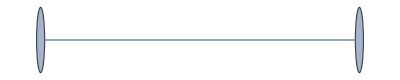

```mathematica
GraphData[{"CompleteBipartite",{1,1}}]
```

```mathematica
GraphData[{"CompleteBipartite",{1,1}},"MaximumLeafNumber"]
```

2

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{2,m==n==1},{m+n-1,Min[m,n]==1}},m+n-2],GraphData[#,"MaximumLeafNumber"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### MaximumVertexDegree

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Max[m,n],GraphData[#,"MaximumVertexDegree"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### MeanDistance

```mathematica
Expand[(m^2+(m+n) (n-1))]
```

-m+m^2-n+m n+n^2

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],2 (m^2+n^2+m n-(m+n))/(m+n)^2,GraphData[#,"MeanDistance"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### MinimalDominatingSetCount

```mathematica
Block[{m,n},Sort[{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],GraphData[#,"MinimalDominatingSetCount"],Piecewise[{{2,Min[m,n]==1}},m n+2]}&/@GraphData["CompleteBipartite"]]]
```

{{{1,1},2,2},{{1,2},2,2},{{1,3},2,2},{{1,4},2,2},{{1,5},2,2},{{1,6},2,2},{{1,7},2,2},{{1,8},2,2},{{1,9},2,2},{{1,10},2,2},{{1,11},2,2},{{1,12},2,2},{{1,13},2,2},{{1,14},2,2},{{1,15},2,2},{{1,16},2,2},{{1,17},2,2},{{1,18},2,2},{{1,19},2,2},{{2,2},6,6},{{2,3},8,8},{{2,4},10,10},{{2,5},12,12},{{2,6},14,14},{{2,7},16,16},{{2,8},18,18},{{2,9},20,20},{{2,10},22,22},{{3,3},11,11},{{3,4},14,14},{{3,5},17,17},{{3,6},20,20},{{3,7},23,23},{{3,8},26,26},{{3,9},29,29},{{3,10},32,32},{{4,4},18,18},{{4,5},22,22},{{4,6},26,26},{{4,7},30,30},{{4,8},34,34},{{4,9},38,38},{{4,10},42,42},{{5,5},27,27},{{5,6},32,32},{{5,7},37,37},{{5,8},42,42},{{5,9},47,47},{{5,10},Missing[NotAvailable],52},{{6,6},38,38},{{6,7},44,44},{{6,8},50,50},{{6,9},Missing[NotAvailable],56},{{6,10},Missing[NotAvailable],62},{{7,7},51,51},{{7,8},Missing[NotAvailable],58},{{7,9},Missing[NotAvailable],65},{{7,10},Missing[NotAvailable],72},{{8,8},Missing[NotAvailable],66},{{8,9},Missing[NotAvailable],74},{{8,10},Missing[NotAvailable],82},{{9,9},Missing[NotAvailable],83},{{9,10},Missing[NotAvailable],92},{{10,10},Missing[NotAvailable],102},{{11,11},Missing[NotAvailable],123},{{12,12},Missing[NotAvailable],146},{{13,13},Missing[NotAvailable],171},{{14,14},Missing[NotAvailable],198},{{15,15},Missing[NotAvailable],227},{{16,16},Missing[NotAvailable],258},{{17,17},Missing[NotAvailable],291},{{18,18},Missing[NotAvailable],326},{{19,19},Missing[NotAvailable],363},{{20,20},Missing[NotAvailable],402}}

```mathematica
DeleteCases[%,{_,x_,x_}]
```

{{{5,10},Missing[NotAvailable],52},{{6,9},Missing[NotAvailable],56},{{6,10},Missing[NotAvailable],62},{{7,8},Missing[NotAvailable],58},{{7,9},Missing[NotAvailable],65},{{7,10},Missing[NotAvailable],72},{{8,8},Missing[NotAvailable],66},{{8,9},Missing[NotAvailable],74},{{8,10},Missing[NotAvailable],82},{{9,9},Missing[NotAvailable],83},{{9,10},Missing[NotAvailable],92},{{10,10},Missing[NotAvailable],102},{{11,11},Missing[NotAvailable],123},{{12,12},Missing[NotAvailable],146},{{13,13},Missing[NotAvailable],171},{{14,14},Missing[NotAvailable],198},{{15,15},Missing[NotAvailable],227},{{16,16},Missing[NotAvailable],258},{{17,17},Missing[NotAvailable],291},{{18,18},Missing[NotAvailable],326},{{19,19},Missing[NotAvailable],363},{{20,20},Missing[NotAvailable],402}}

### MinimalDominatingSetSignature

```mathematica
Block[{m,n},Sort[{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],GraphData[#,"MinimalDominatingSetSignature"],Piecewise[{{2,Min[m,n]==1}},m n+2]}&/@GraphData["CompleteBipartite"]]]//Column
```

{{1,1},{{1,2}},2}
{{1,2},{{1,1},{2,1}},2}
{{1,3},{{1,1},{3,1}},2}
{{1,4},{{1,1},{4,1}},2}
{{1,5},{{1,1},{5,1}},2}
{{1,6},{{1,1},{6,1}},2}
{{1,7},{{1,1},{7,1}},2}
{{1,8},{{1,1},{8,1}},2}
{{1,9},{{1,1},{9,1}},2}
{{1,10},{{1,1},{10,1}},2}
{{1,11},{{1,1},{11,1}},2}
{{1,12},{{1,1},{12,1}},2}
{{1,13},{{1,1},{13,1}},2}
{{1,14},{{1,1},{14,1}},2}
{{1,15},{{1,1},{15,1}},2}
{{1,16},{{1,1},{16,1}},2}
{{1,17},{{1,1},{17,1}},2}
{{1,18},{{1,1},{18,1}},2}
{{1,19},{{1,1},{19,1}},2}
{{2,2},{{2,6}},6}
{{2,3},{{2,7},{3,1}},8}
{{2,4},{{2,9},{4,1}},10}
{{2,5},{{2,11},{5,1}},12}
{{2,6},{{2,13},{6,1}},14}
{{2,7},{{2,15},{7,1}},16}
{{2,8},{{2,17},{8,1}},18}
{{2,9},{{2,19},{9,1}},20}
{{2,10},{{2,21},{10,1}},22}
{{3,3},{{2,9},{3,2}},11}
{{3,4},{{2,12},{3,1},{4,1}},14}
{{3,5},{{2,15},{3,1},{5,1}},17}
{{3,6},{{2,18},{3,1},{6,1}},20}
{{3,7},{{2,21},{3,1},{7,1}},23}
{{3,8},{{2,24},{3,1},{8,1}},26}
{{3,9},{{2,27},{3,1},{9,1}},29}
{{3,10},{{2,30},{3,1},{10,1}},32}
{{4,4},{{2,16},{4,2}},18}
{{4,5},{{2,20},{4,1},{5,1}},22}
{{4,6},{{2,24},{4,1},{6,1}},26}
{{4,7},{{2,28},{4,1},{7,1}},30}
{{4,8},{{2,32},{4,1},{8,1}},34}
{{4,9},{{2,36},{4,1},{9,1}},38}
{{4,10},{{2,40},{4,1},{10,1}},42}
{{5,5},{{2,25},{5,2}},27}
{{5,6},{{2,30},{5,1},{6,1}},32}
{{5,7},{{2,35},{5,1},{7,1}},37}
{{5,8},{{2,40},{5,1},{8,1}},42}
{{5,9},{{2,45},{5,1},{9,1}},47}
{{5,10},Missing[NotAvailable],52}
{{6,6},{{2,36},{6,2}},38}
{{6,7},{{2,42},{6,1},{7,1}},44}
{{6,8},{{2,48},{6,1},{8,1}},50}
{{6,9},Missing[NotAvailable],56}
{{6,10},Missing[NotAvailable],62}
{{7,7},{{2,49},{7,2}},51}
{{7,8},Missing[NotAvailable],58}
{{7,9},Missing[NotAvailable],65}
{{7,10},Missing[NotAvailable],72}
{{8,8},Missing[NotAvailable],66}
{{8,9},Missing[NotAvailable],74}
{{8,10},Missing[NotAvailable],82}
{{9,9},Missing[NotAvailable],83}
{{9,10},Missing[NotAvailable],92}
{{10,10},Missing[NotAvailable],102}
{{11,11},Missing[NotAvailable],123}
{{12,12},Missing[NotAvailable],146}
{{13,13},Missing[NotAvailable],171}
{{14,14},Missing[NotAvailable],198}
{{15,15},Missing[NotAvailable],227}
{{16,16},Missing[NotAvailable],258}
{{17,17},Missing[NotAvailable],291}
{{18,18},Missing[NotAvailable],326}
{{19,19},Missing[NotAvailable],363}
{{20,20},Missing[NotAvailable],402}

### MinimalEdgeCoverCount

```mathematica
ser=Series[Exp[x Exp[y]+y Exp[x]-x-y-x y]-1,{x,0,20},{y,0,20}];
```

```mathematica
Block[{m,n},Sort[{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],GraphData[#,"MinimalEdgeCoverCount"],m !n !Coefficient[ser,x^m y^n]}&/@GraphData["CompleteBipartite"]]]
```

{{{1,1},1,1},{{1,2},1,1},{{1,3},1,1},{{1,4},1,1},{{1,5},1,1},{{1,6},1,1},{{1,7},1,1},{{1,8},1,1},{{1,9},1,1},{{1,10},1,1},{{1,11},1,1},{{1,12},1,1},{{1,13},1,1},{{1,14},1,1},{{1,15},1,1},{{1,16},1,1},{{1,17},1,1},{{1,18},1,1},{{1,19},1,1},{{2,2},2,2},{{2,3},6,6},{{2,4},14,14},{{2,5},30,30},{{2,6},62,62},{{2,7},126,126},{{2,8},254,254},{{2,9},510,510},{{2,10},1022,1022},{{3,3},15,15},{{3,4},48,48},{{3,5},165,165},{{3,6},558,558},{{3,7},1827,1827},{{3,8},Missing[NotAvailable],5820},{{3,9},Missing[NotAvailable],18177},{{3,10},Missing[NotAvailable],56010},{{4,4},184,184},{{4,5},680,680},{{4,6},Missing[NotAvailable],2664},{{4,7},Missing[NotAvailable],11032},{{4,8},Missing[NotAvailable],46904},{{4,9},Missing[NotAvailable],200232},{{4,10},Missing[NotAvailable],849160},{{5,5},Missing[NotAvailable],2945},{{5,6},Missing[NotAvailable],13080},{{5,7},Missing[NotAvailable],59605},{{5,8},Missing[NotAvailable],281440},{{5,9},Missing[NotAvailable],1379745},{{5,10},Missing[NotAvailable],6970400},{{6,6},Missing[NotAvailable],63756},{{6,7},Missing[NotAvailable],320292},{{6,8},Missing[NotAvailable],1663248},{{6,9},Missing[NotAvailable],8906544},{{6,10},Missing[NotAvailable],49148100},{{7,7},Missing[NotAvailable],1748803},{{7,8},Missing[NotAvailable],9791824},{{7,9},Missing[NotAvailable],56499849},{{7,10},Missing[NotAvailable],336192220},{{8,8},Missing[NotAvailable],58746304},{{8,9},Missing[NotAvailable],361679040},{{8,10},Missing[NotAvailable],2290065200},{{9,9},Missing[NotAvailable],2361347073},{{9,10},Missing[NotAvailable],15803119440},{{10,10},Missing[NotAvailable],111310111900},{{11,11},Missing[NotAvailable],6059192459771},{{12,12},Missing[NotAvailable],376064819659728},{{13,13},Missing[NotAvailable],26330615879623393},{{14,14},Missing[NotAvailable],2061099487899901372},{{15,15},Missing[NotAvailable],178985517944285956275},{{16,16},Missing[NotAvailable],17127853895338704829696},{{17,17},Missing[NotAvailable],1795558477562697433148417},{{18,18},Missing[NotAvailable],205139946486547987323752124},{{19,19},Missing[NotAvailable],25424084489480731512102040651},{{20,20},Missing[NotAvailable],3403956508526794346699350862800}}

```mathematica
DeleteCases[%,{_,x_,x_}]
```

{{{3,8},Missing[NotAvailable],5820},{{3,9},Missing[NotAvailable],18177},{{3,10},Missing[NotAvailable],56010},{{4,6},Missing[NotAvailable],2664},{{4,7},Missing[NotAvailable],11032},{{4,8},Missing[NotAvailable],46904},{{4,9},Missing[NotAvailable],200232},{{4,10},Missing[NotAvailable],849160},{{5,5},Missing[NotAvailable],2945},{{5,6},Missing[NotAvailable],13080},{{5,7},Missing[NotAvailable],59605},{{5,8},Missing[NotAvailable],281440},{{5,9},Missing[NotAvailable],1379745},{{5,10},Missing[NotAvailable],6970400},{{6,6},Missing[NotAvailable],63756},{{6,7},Missing[NotAvailable],320292},{{6,8},Missing[NotAvailable],1663248},{{6,9},Missing[NotAvailable],8906544},{{6,10},Missing[NotAvailable],49148100},{{7,7},Missing[NotAvailable],1748803},{{7,8},Missing[NotAvailable],9791824},{{7,9},Missing[NotAvailable],56499849},{{7,10},Missing[NotAvailable],336192220},{{8,8},Missing[NotAvailable],58746304},{{8,9},Missing[NotAvailable],361679040},{{8,10},Missing[NotAvailable],2290065200},{{9,9},Missing[NotAvailable],2361347073},{{9,10},Missing[NotAvailable],15803119440},{{10,10},Missing[NotAvailable],111310111900},{{11,11},Missing[NotAvailable],6059192459771},{{12,12},Missing[NotAvailable],376064819659728},{{13,13},Missing[NotAvailable],26330615879623393},{{14,14},Missing[NotAvailable],2061099487899901372},{{15,15},Missing[NotAvailable],178985517944285956275},{{16,16},Missing[NotAvailable],17127853895338704829696},{{17,17},Missing[NotAvailable],1795558477562697433148417},{{18,18},Missing[NotAvailable],205139946486547987323752124},{{19,19},Missing[NotAvailable],25424084489480731512102040651},{{20,20},Missing[NotAvailable],3403956508526794346699350862800}}

### MinimumCliqueCoveringCount

A019538

{n,n}: n!

```mathematica
Sum[(-1)^(k+m)k^n Binomial[m,k],{k,n}]/.m->n
```

∑_k^n (-1)^(k+n) k^n Binomial[n,k]

```mathematica
Table[%,{n,10}]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Min[m,n] !StirlingS2[Max[m,n],Min[m,n]],GraphData[#,"MinimumCliqueCoveringCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{{{4,10},818520,Missing[NotAvailable]},{{5,9},834120,Missing[NotAvailable]},{{5,10},5103000,Missing[NotAvailable]},{{6,9},1905120,Missing[NotAvailable]},{{6,10},16435440,Missing[NotAvailable]},{{7,8},141120,Missing[NotAvailable]},{{7,9},2328480,Missing[NotAvailable]},{{7,10},29635200,Missing[NotAvailable]},{{8,9},1451520,Missing[NotAvailable]},{{8,10},30240000,Missing[NotAvailable]},{{9,10},16329600,Missing[NotAvailable]}}

```mathematica
Table[GraphData[{"CompleteBipartite",{2,n}},"MinimumCliqueCoveringCount"],{n,2,10}]
```

{2,6,14,30,62,126,254,510,1022}

```mathematica
FindSequenceFunction[%,n-1]
```

2 (-1+2^(-1+n))

```mathematica
Table[GraphData[{"CompleteBipartite",{3,n}},"MinimumCliqueCoveringCount"],{n,3,10}]
```

{6,36,150,540,1806,5796,18150,55980}

```mathematica
FindSequenceFunction[%,n-2]
```

-3 (-1+2^n-3^(-1+n))

```mathematica
Table[GraphData[{"CompleteBipartite",{4,n}},"MinimumCliqueCoveringCount"],{n,4,10}]
```

{24,240,1560,8400,40824,186480,Missing[NotAvailable]}

```mathematica
FindSequenceFunction[Most@%,n-4]
```

FindSequenceFunction[{24,240,1560,8400,40824,186480},-4+n]

```mathematica
4^n-C(4,3)*3^n+C(4,2)*2^n-C(4,1)
```

```mathematica
Table[GraphData[{"CompleteBipartite",{m,n}},"MinimumCliqueCoveringCount"],{n,5},{m,n}]
```

{{1},{1,2},{1,6,6},{1,14,36,24},{1,30,150,240,120}}

```mathematica
Table[Sum[(-1)^(k+m)k^n Binomial[m,k],{k,n}],{n,5},{m,n}]
```

{{1},{1,2},{1,6,6},{1,14,36,24},{1,30,150,240,120}}

```mathematica
Table[m !StirlingS2[n,m],{n,10},{m,n}]
```

{{1},{1,2},{1,6,6},{1,14,36,24},{1,30,150,240,120},{1,62,540,1560,1800,720},{1,126,1806,8400,16800,15120,5040},{1,254,5796,40824,126000,191520,141120,40320},{1,510,18150,186480,834120,1905120,2328480,1451520,362880},{1,1022,55980,818520,5103000,16435440,29635200,30240000,16329600,3628800}}

```mathematica
Sum[(-1)^(k+m)k^n Binomial[m,k],{k,n}]
```

∑_k^n (-1)^(k+m) k^n Binomial[m,k]

### MinimumConnectedDominatingSetCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{2,m==n==1},{1,Min[m,n]==1}},m n],GraphData[#,"MinimumConnectedDominatingSetCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### MinimumDistinguishingLabelingCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{2,m==n==1},{1,Min[m,n]==1}},m n],GraphData[#,"MinimumDistinguishingLabelingCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{{{1,3},1,18},{{2,3},6,36},{{2,4},8,288},{{2,5},10,2400},{{2,6},12,Missing[NotAvailable]},{{2,7},14,Missing[NotAvailable]},{{2,8},16,Missing[NotAvailable]},{{2,9},18,Missing[NotAvailable]},{{2,10},20,Missing[NotAvailable]},{{3,4},12,576},{{3,5},15,7200},{{3,6},18,Missing[NotAvailable]},{{3,7},21,Missing[NotAvailable]},{{3,8},24,Missing[NotAvailable]},{{3,9},27,Missing[NotAvailable]},{{3,10},30,Missing[NotAvailable]},{{4,4},16,11520},{{4,5},20,Missing[NotAvailable]},{{4,6},24,Missing[NotAvailable]},{{4,7},28,Missing[NotAvailable]},{{4,8},32,Missing[NotAvailable]},{{4,9},36,Missing[NotAvailable]},{{4,10},40,Missing[NotAvailable]},{{5,5},25,Missing[NotAvailable]},{{5,6},30,Missing[NotAvailable]},{{5,7},35,Missing[NotAvailable]},{{5,8},40,Missing[NotAvailable]},{{5,9},45,Missing[NotAvailable]},{{5,10},50,Missing[NotAvailable]},{{6,6},36,Missing[NotAvailable]},{{6,7},42,Missing[NotAvailable]},{{6,8},48,Missing[NotAvailable]},{{6,9},54,Missing[NotAvailable]},{{6,10},60,Missing[NotAvailable]},{{7,7},49,Missing[NotAvailable]},{{7,8},56,Missing[NotAvailable]},{{7,9},63,Missing[NotAvailable]},{{7,10},70,Missing[NotAvailable]},{{8,8},64,Missing[NotAvailable]},{{8,9},72,Missing[NotAvailable]},{{8,10},80,Missing[NotAvailable]},{{9,9},81,Missing[NotAvailable]},{{9,10},90,Missing[NotAvailable]},{{10,10},100,Missing[NotAvailable]},{{11,11},121,Missing[NotAvailable]},{{12,12},144,Missing[NotAvailable]},{{13,13},169,Missing[NotAvailable]},{{14,14},196,Missing[NotAvailable]},{{15,15},225,Missing[NotAvailable]},{{16,16},256,Missing[NotAvailable]},{{17,17},289,Missing[NotAvailable]},{{18,18},324,Missing[NotAvailable]},{{19,19},361,Missing[NotAvailable]},{{20,20},400,Missing[NotAvailable]},{{1,2},1,4},{{2,2},4,24},{{1,4},1,96},{{1,5},1,600},{{1,6},1,4320},{{1,7},1,35280},{{1,8},1,322560},{{1,9},1,3265920},{{1,10},1,36288000},{{1,11},1,439084800},{{1,12},1,5748019200},{{1,13},1,80951270400},{{1,14},1,1220496076800},{{1,15},1,19615115520000},{{1,16},1,334764638208000},{{1,17},1,6046686277632000},{{1,18},1,115242726703104000},{{1,19},1,2311256907767808000},{{3,3},9,432}}

### MinimumDominatingSetCount

{n,n}: Piecewise[{{2, n == 1}, {6, n == 2}}, n^2]

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{2,m==n==1},{6,m==n==2},{1,Min[m,n]==1},{m n+1,Min[m,n]==2}},m n],GraphData[#,"MinimumDominatingSetCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### MinimumEdgeCoverCount

A019538

{n,n}: n!

```mathematica
Table[GraphData[{"CompleteBipartite",{m,n}},"MinimumEdgeCoverCount"],{n,5},{m,n}]
```

{{1},{1,2},{1,6,6},{1,14,36,24},{1,30,150,240,120}}

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Min[m,n] !StirlingS2[Max[m,n],Min[m,n]],GraphData[#,"MinimumEdgeCoverCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{{{4,9},186480,Missing[NotAvailable]},{{4,10},818520,Missing[NotAvailable]},{{5,7},16800,Missing[NotAvailable]},{{5,8},126000,Missing[NotAvailable]},{{5,9},834120,Missing[NotAvailable]},{{5,10},5103000,Missing[NotAvailable]},{{6,7},15120,Missing[NotAvailable]},{{6,8},191520,Missing[NotAvailable]},{{6,9},1905120,Missing[NotAvailable]},{{6,10},16435440,Missing[NotAvailable]},{{7,8},141120,Missing[NotAvailable]},{{7,9},2328480,Missing[NotAvailable]},{{7,10},29635200,Missing[NotAvailable]},{{8,9},1451520,Missing[NotAvailable]},{{8,10},30240000,Missing[NotAvailable]},{{9,10},16329600,Missing[NotAvailable]},{{11,11},39916800,Missing[NotAvailable]},{{12,12},479001600,Missing[NotAvailable]},{{13,13},6227020800,Missing[NotAvailable]},{{14,14},87178291200,Missing[NotAvailable]},{{15,15},1307674368000,Missing[NotAvailable]},{{16,16},20922789888000,Missing[NotAvailable]},{{17,17},355687428096000,Missing[NotAvailable]},{{18,18},6402373705728000,Missing[NotAvailable]},{{19,19},121645100408832000,Missing[NotAvailable]},{{20,20},2432902008176640000,Missing[NotAvailable]}}

### MinimumVertexDegree

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Min[m,n],GraphData[#,"MinimumVertexDegree"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### MolecularTopologicalIndex

{n,n}: 4 n^2 (-1+2 n)

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],4m n(m +n-1),GraphData[#,"MolecularTopologicalIndex"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### Nonhamiltonian

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{False,m>1&&m==n}},True],GraphData[#,"Nonhamiltonian"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### NormalizedLaplacianMatrix

```mathematica
MatrixForm/@Table[GraphData[{"CompleteBipartite",{n,n}},"NormalizedLaplacianMatrix"],{n,5}]
```

{(1 | -1
-1 | 1),(1 | -1/2 | 0 | -1/2
-1/2 | 1 | -1/2 | 0
0 | -1/2 | 1 | -1/2
-1/2 | 0 | -1/2 | 1),(1 | 0 | 0 | -1/3 | -1/3 | -1/3
0 | 1 | 0 | -1/3 | -1/3 | -1/3
0 | 0 | 1 | -1/3 | -1/3 | -1/3
-1/3 | -1/3 | -1/3 | 1 | 0 | 0
-1/3 | -1/3 | -1/3 | 0 | 1 | 0
-1/3 | -1/3 | -1/3 | 0 | 0 | 1),(1 | 0 | 0 | 0 | -1/4 | -1/4 | -1/4 | -1/4
0 | 1 | 0 | 0 | -1/4 | -1/4 | -1/4 | -1/4
0 | 0 | 1 | 0 | -1/4 | -1/4 | -1/4 | -1/4
0 | 0 | 0 | 1 | -1/4 | -1/4 | -1/4 | -1/4
-1/4 | -1/4 | -1/4 | -1/4 | 1 | 0 | 0 | 0
-1/4 | -1/4 | -1/4 | -1/4 | 0 | 1 | 0 | 0
-1/4 | -1/4 | -1/4 | -1/4 | 0 | 0 | 1 | 0
-1/4 | -1/4 | -1/4 | -1/4 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | -1/5 | -1/5 | -1/5 | -1/5 | -1/5
0 | 1 | 0 | 0 | 0 | -1/5 | -1/5 | -1/5 | -1/5 | -1/5
0 | 0 | 1 | 0 | 0 | -1/5 | -1/5 | -1/5 | -1/5 | -1/5
0 | 0 | 0 | 1 | 0 | -1/5 | -1/5 | -1/5 | -1/5 | -1/5
0 | 0 | 0 | 0 | 1 | -1/5 | -1/5 | -1/5 | -1/5 | -1/5
-1/5 | -1/5 | -1/5 | -1/5 | -1/5 | 1 | 0 | 0 | 0 | 0
-1/5 | -1/5 | -1/5 | -1/5 | -1/5 | 0 | 1 | 0 | 0 | 0
-1/5 | -1/5 | -1/5 | -1/5 | -1/5 | 0 | 0 | 1 | 0 | 0
-1/5 | -1/5 | -1/5 | -1/5 | -1/5 | 0 | 0 | 0 | 1 | 0
-1/5 | -1/5 | -1/5 | -1/5 | -1/5 | 0 | 0 | 0 | 0 | 1)}

```mathematica
MatrixForm/@Table[With[{i=IdentityMatrix[n],c=ConstantArray[-1/n,{n,n}]},ArrayFlatten[{{i,c},{c,i}}]],{n,5}]
```

{(1 | -1
-1 | 1),(1 | 0 | -1/2 | -1/2
0 | 1 | -1/2 | -1/2
-1/2 | -1/2 | 1 | 0
-1/2 | -1/2 | 0 | 1),(1 | 0 | 0 | -1/3 | -1/3 | -1/3
0 | 1 | 0 | -1/3 | -1/3 | -1/3
0 | 0 | 1 | -1/3 | -1/3 | -1/3
-1/3 | -1/3 | -1/3 | 1 | 0 | 0
-1/3 | -1/3 | -1/3 | 0 | 1 | 0
-1/3 | -1/3 | -1/3 | 0 | 0 | 1),(1 | 0 | 0 | 0 | -1/4 | -1/4 | -1/4 | -1/4
0 | 1 | 0 | 0 | -1/4 | -1/4 | -1/4 | -1/4
0 | 0 | 1 | 0 | -1/4 | -1/4 | -1/4 | -1/4
0 | 0 | 0 | 1 | -1/4 | -1/4 | -1/4 | -1/4
-1/4 | -1/4 | -1/4 | -1/4 | 1 | 0 | 0 | 0
-1/4 | -1/4 | -1/4 | -1/4 | 0 | 1 | 0 | 0
-1/4 | -1/4 | -1/4 | -1/4 | 0 | 0 | 1 | 0
-1/4 | -1/4 | -1/4 | -1/4 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | -1/5 | -1/5 | -1/5 | -1/5 | -1/5
0 | 1 | 0 | 0 | 0 | -1/5 | -1/5 | -1/5 | -1/5 | -1/5
0 | 0 | 1 | 0 | 0 | -1/5 | -1/5 | -1/5 | -1/5 | -1/5
0 | 0 | 0 | 1 | 0 | -1/5 | -1/5 | -1/5 | -1/5 | -1/5
0 | 0 | 0 | 0 | 1 | -1/5 | -1/5 | -1/5 | -1/5 | -1/5
-1/5 | -1/5 | -1/5 | -1/5 | -1/5 | 1 | 0 | 0 | 0 | 0
-1/5 | -1/5 | -1/5 | -1/5 | -1/5 | 0 | 1 | 0 | 0 | 0
-1/5 | -1/5 | -1/5 | -1/5 | -1/5 | 0 | 0 | 1 | 0 | 0
-1/5 | -1/5 | -1/5 | -1/5 | -1/5 | 0 | 0 | 0 | 1 | 0
-1/5 | -1/5 | -1/5 | -1/5 | -1/5 | 0 | 0 | 0 | 0 | 1)}

### OddChordlessCycleCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],0,GraphData[#,"OddChordlessCycleCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### PathCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],1/2 Sum[k ! l ! Binomial[m,k]Binomial[n,l],{k,2,m},{l,2,n}],GraphData[#,"PathCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{{{1,3},0,6},{{2,3},12,33},{{2,4},60,72},{{2,5},320,135},{{2,6},1950,228},{{2,7},13692,357},{{2,8},109592,528},{{2,9},986400,747},{{2,10},9864090,1020},{{3,4},360,438},{{3,5},1920,1140},{{3,6},11700,2511},{{3,7},82152,4893},{{3,8},657552,8700},{{3,9},5918400,14418},{{3,10},59184540,22605},{{4,4},1800,2224},{{4,5},9600,8850},{{4,6},58500,27480},{{4,7},410760,70462},{{4,8},3287760,156768},{{4,9},29592000,313434},{{4,10},295922700,Missing[NotAvailable]},{{5,5},51200,55725},{{5,6},312000,265665},{{5,7},2190720,962010},{{5,8},17534720,Missing[NotAvailable]},{{5,9},157824000,Missing[NotAvailable]},{{5,10},1578254400,Missing[NotAvailable]},{{6,6},1901250,2006316},{{6,7},13349700,Missing[NotAvailable]},{{6,8},106852200,Missing[NotAvailable]},{{6,9},961740000,Missing[NotAvailable]},{{6,10},9617487750,Missing[NotAvailable]},{{7,7},93735432,Missing[NotAvailable]},{{7,8},750266832,Missing[NotAvailable]},{{7,9},6752894400,Missing[NotAvailable]},{{7,10},67529560140,Missing[NotAvailable]},{{8,8},6005203232,Missing[NotAvailable]},{{8,9},54050774400,Missing[NotAvailable]},{{8,10},540512675640,Missing[NotAvailable]},{{9,9},486492480000,Missing[NotAvailable]},{{9,10},4864969188000,Missing[NotAvailable]},{{10,10},48650135764050,Missing[NotAvailable]},{{11,11},5886678363005000,Missing[NotAvailable]},{{12,12},847681856144807112,Missing[NotAvailable]},{{13,13},143258236329052795392,Missing[NotAvailable]},{{14,14},28078614363623827872050,Missing[NotAvailable]},{{15,15},6317688232561833040321800,Missing[NotAvailable]},{{16,16},1617328187549479027815120000,Missing[NotAvailable]},{{17,17},467407846202062424597463713792,Missing[NotAvailable]},{{18,18},151440142169473551027145848248802,Missing[NotAvailable]},{{19,19},54669891323180065008457410359920200,Missing[NotAvailable]},{{20,20},21867956529272028516442025458238400200,Missing[NotAvailable]},{{1,1},0,1},{{1,2},0,3},{{2,2},2,12},{{1,4},0,10},{{1,5},0,15},{{1,6},0,21},{{1,7},0,28},{{1,8},0,36},{{1,9},0,45},{{1,10},0,55},{{1,11},0,66},{{1,12},0,78},{{1,13},0,91},{{1,14},0,105},{{1,15},0,120},{{1,16},0,136},{{1,17},0,153},{{1,18},0,171},{{1,19},0,190},{{3,3},72,135}}

```mathematica
Table[GraphData[{"CompleteBipartite",{m,n}},"CycleCount"],{n,10},{m,n}]//Column
```

{0}
{0,1}
{0,3,15}
{0,6,42,204}
{0,10,90,660,3940}
{0,15,165,1650,15390,113865}
{0,21,273,3486,45150,526155,4662231}
{0,28,420,6552,109480,1776180,24864588,256485040}
{0,36,612,11304,232200,4864140,94866156,1549436112,18226108944}
{0,45,855,18270,446130,11491155,289407825,6589549260,122955146100,1623855701385}

```mathematica
Table[GraphData[{"CompleteBipartite",{2,n}},"CycleCount"],{n,2,10}]
```

{1,3,6,10,15,21,28,36,45}

```mathematica
FindSequenceFunction[%,n-1]
```

1/2 (-1+n) n

```mathematica
Table[GraphData[{"CompleteBipartite",{3,n}},"CycleCount"],{n,3,10}]
```

{15,42,90,165,273,420,612,855}

```mathematica
FindSequenceFunction[%,n-2]//FullSimplify
```

1/2 (-1+n) n (-1+2 n)

```mathematica
Table[GraphData[{"CompleteBipartite",{4,n}},"CycleCount"],{n,4,10}]
```

{204,660,1650,3486,6552,11304,18270}

```mathematica
FindSequenceFunction[%,n-3]//Factor
```

(-1+n) n (13-11 n+3 n^2)

### PathPolynomial

### PentagonCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],0,GraphData[#,"PentagonCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### Perfect

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],True,GraphData[#,"Perfect"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### ProjectivePlaneCrossingNumber

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{0,Min[m,n]<3}},Missing["NotAvailable"]],GraphData[#,"ProjectivePlaneCrossingNumber"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{{{3,4},Missing[NotAvailable],0},{{4,4},Missing[NotAvailable],2},{{4,5},Missing[NotAvailable],4},{{3,3},Missing[NotAvailable],0}}

### Radius

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{1,Min[m,n]==1}},2],GraphData[#,"Radius"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### RankPolynomial

```mathematica
(poly=Factor@Table[GraphData[{"CompleteBipartite",{n,n}},"RankPolynomial"][x,y],{n,k0=1,10}])//Column
```

1
 |  |  |  |

```mathematica
coef=Factor/@FindLinearRecurrence[poly]
```

FindLinearRecurrence[{1+x,8,1+100 x+4950 x^2+161700 x^3+3919200 x^4+75093120 x^5+1182753600 x^6+15712656000 x^7+179127216000 x^8+1772146496000 x^9+15311555436800 x^10+115760058048000 x^11+763841356800000 x^12+4365392640000000 x^13+517+141629804641800 x^19 y^70+1800 x^18 y^71+17310309456420 x^19 y^71+20 x^18 y^72+1902231808400 x^19 y^72+186087894300 x^19 y^73+16007560800 x^19 y^74+1192052400 x^19 y^75+75287520 x^19 y^76+3921225 x^19 y^77+161700 x^19 y^78+4950 x^19 y^79+100 x^19 y^80+x^19 y^81}]
 |  |  |  |

```mathematica
ToPolynomialRecurrence[p,x,n,coef]
```

```mathematica
FormattedPolynomialRecurrence[p,x,n,coef]//TraditionalForm
```

```mathematica
TeXForm[%]
```

```mathematica
LinearRecurrence[coef,poly,{2-k0,Length[coef]-k0+1}]
```

```mathematica
FullSimplify[RSolve[Prepend[Table[p[k+k0-1,x]==poly[[k]],{k,Length[coef]}],ToPolynomialRecurrence[p,x,n,coef]],p[n,x],n],n∈Integers&&n>0]
```

```mathematica
gf=Factor[z^k0 FindGeneratingFunction[poly,z]]
```

```mathematica
FullSimplify[SeriesCoefficient[gf,{z,0,n}],n>0]
```

```mathematica
poly2=Table[XXX,{n,20}]
```

```mathematica
FullSimplify[poly2-poly]
```

### RectilinearCrossingNumber

A030179 (conjectured)

https://en.wikipedia.org/wiki/Turán%27s_brick_factory_problem

If edges are required to be drawn as straight line segments, rather than arbitrary curves, then some graphs need more crossings. However, the upper bound established by Zarankiewicz for the crossing numbers of complete bipartite graphs can be achieved using only straight edges. Therefore, if the Zarankiewicz conjecture is correct, then the complete bipartite graphs have rectilinear crossing numbers equal to their crossing numbers

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"RectilinearCrossingNumber"],{n,20}]
```

{0,0,1,4,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

### ReliabilityPolynomial

```mathematica
(poly=Factor@Table[GraphData[{"CompleteBipartite",{n,n}},"ReliabilityPolynomial"][x],{n,k0=1,10}])//Column
```

1-x
-(-1+x)^3 (1+3 x)
-(-1+x)^5 (1+5 x+15 x^2+29 x^3+31 x^4)
-(-1+x)^7 (1+7 x+28 x^2+84 x^3+202 x^4+406 x^5+684 x^6+964 x^7+1045 x^8+675 x^9)
-(-1+x)^9 (1+9 x+45 x^2+165 x^3+495 x^4+1277 x^5+2913 x^6+5985 x^7+11195 x^8+19185 x^9+30233 x^10+43757 x^11+57795 x^12+68365 x^13+69445 x^14+54529 x^15+25231 x^16)
-(-1+x)^11 (1+11 x+66 x^2+286 x^3+1001 x^4+3003 x^5+7996 x^6+19316 x^7+42966 x^8+88946 x^9+172708 x^10+316356 x^11+548996 x^12+905476 x^13+1422516 x^14+2131508 x^15+3047716 x^16+4155876 x^17+5393556 x^18+6633396 x^19+7664463 x^20+8188701 x^21+7858326 x^22+6420546 x^23+4000521 x^24+1441923 x^25)
-(-1+x)^13 (1+13 x+91 x^2+455 x^3+1820 x^4+6188 x^5+18564 x^6+50374 x^7+125788 x^8+292656 x^9+640276 x^10+1326598 x^11+2617475 x^12+4939865 x^13+8949125 x^14+15607449 x^15+26265967 x^16+42736855 x^17+67334715 x^18+102859855 x^19+152491339 x^20+219555487 x^21+307139955 x^22+417537015 x^23+551516945 x^24+707446194 x^25+880293372 x^26+1060571120 x^27+1233283840 x^28+1377133984 x^29+1464623566 x^30+1464441846 x^31+1348660866 x^32+1106426923 x^33+763393631 x^34+396082637 x^35+116914351 x^36)
-(-1+x)^15 (1+15 x+120 x^2+680 x^3+3060 x^4+11628 x^5+38760 x^6+116280 x^7+319754 x^8+816950 x^9+1959336 x^10+4446520 x^11+9608740 x^12+19872252 x^13+39496376 x^14+75697448 x^15+140300651 x^16+252080165 x^17+439953424 x^18+747176368 x^19+1236631096 x^20+1997192200 x^21+3150992048 x^22+4861172240 x^23+7339410100 x^24+10852155980 x^25+15724135344 x^26+22337306384 x^27+31123184088 x^28+42546312040 x^29+57076739280 x^30+75149738224 x^31+97111723479 x^32+123152314713 x^33+153223548024 x^34+186948310440 x^35+223520919028 x^36+261603443564 x^37+299223937832 x^38+333692046584 x^39+361565996114 x^40+378739854830 x^41+380769305640 x^42+363590861880 x^43+324771975844 x^44+265272353788 x^45+191233555640 x^46+114660598312 x^47+51074307565 x^48+12764590275 x^49)
-(-1+x)^17 (1+17 x+153 x^2+969 x^3+4845 x^4+20349 x^5+74613 x^6+245157 x^7+735471 x^8+2042957 x^9+5311429 x^10+13035141 x^11+30404313 x^12+67776705 x^13+145056393 x^14+299197161 x^15+596667483 x^16+1153563417 x^17+2167178313 x^18+3964265241 x^19+7072965549 x^20+12327389469 x^21+21016025685 x^22+35087346909 x^23+57427884135 x^24+92229258645 x^25+145460655549 x^26+225461344597 x^27+343663362857 x^28+515446590033 x^29+761116431921 x^30+1106977600497 x^31+1586455770339 x^32+2241192407313 x^33+3122007633681 x^34+4289593155921 x^35+5814764450849 x^36+7778071942549 x^37+10268548989453 x^38+13381364721717 x^39+17214156589419 x^40+21861845067285 x^41+27409784243229 x^42+33925176331029 x^43+41446769125509 x^44+49972952224257 x^45+59448461153745 x^46+69749978576193 x^47+80671000025727 x^48+91906484965641 x^49+103038224653305 x^50+113522789801889 x^51+122685714700065 x^52+129728559501189 x^53+133759543316437 x^54+133862336985293 x^55+129219421090347 x^56+119301981667053 x^57+104121112263933 x^58+84498569906661 x^59+62255236210581 x^60+40143185684961 x^61+21326248026801 x^62+8331515963465 x^63+1805409270031 x^64)
-(-1+x)^19 (1+19 x+190 x^2+1330 x^3+7315 x^4+33649 x^5+134596 x^6+480700 x^7+1562275 x^8+4686825 x^9+13123090 x^10+34596910 x^11+86489425 x^12+206226475 x^13+471289300 x^14+1036485340 x^15+2201269510 x^16+4527953650 x^17+9043889700 x^18+17578893700 x^19+33315523300 x^20+61667104900 x^21+111649948900 x^22+197985796900 x^23+344262337600 x^24+587597759416 x^25+985403493604 x^26+1625020163940 x^27+2637215945380 x^28+4214781613540 x^29+6637725724564 x^30+10306853956756 x^31+15787788711400 x^32+23867719949200 x^33+35627337474100 x^34+52530429665140 x^35+76533485143860 x^36+110217234603700 x^37+156941346916900 x^38+221022372523300 x^39+307933439129380 x^40+424522094498020 x^41+579240026598100 x^42+782375175394900 x^43+1046273032527100 x^44+1385529811993740 x^45+1817135839701460 x^46+2360543196978100 x^47+3037627681345300 x^48+3872511903704500 x^49+4891214262301300 x^50+6121088077033300 x^51+7590016766065300 x^52+9325334964339700 x^53+11352452137462500 x^54+13693164490631620 x^55+16363652386800880 x^56+19372173233271400 x^57+22716472762912900 x^58+26380949768241700 x^59+30333620378428420 x^60+34522940101687780 x^61+38874562416883300 x^62+43288156673528100 x^63+47634498557588800 x^64+51753214847959480 x^65+55451844852509620 x^66+58507293719902900 x^67+60671274604699675 x^68+61681875206918425 x^69+61283741695729510 x^70+59259193130896690 x^71+55471336776146325 x^72+49917343921486975 x^73+42784755345217900 x^74+34495737698274508 x^75+25714898091206977 x^76+17289950207320795 x^77+10100560210334290 x^78+4822696070905270 x^79+1678874736736417 x^80+321113303226243 x^81)

```mathematica
coef=Factor/@FindLinearRecurrence[poly]
```

FindLinearRecurrence[{1-x,-(-1+x)^3 (1+3 x),-(-1+x)^5 (1+5 x+15 x^2+29 x^3+31 x^4),-(-1+x)^7 (1+7 x+28 x^2+84 x^3+202 x^4+406 x^5+684 x^6+964 x^7+1045 x^8+675 x^9),-(-1+x)^9 (1+9 x+45 x^2+165 x^3+495 x^4+1277 x^5+2913 x^6+5985 x^7+11195 x^8+19185 x^9+30233 x^10+43757 x^11+57795 x^12+68365 x^13+69445 x^14+54529 x^15+25231 x^16),-(-1+x)^11 (1+11 x+66 x^2+286 x^3+1001 x^4+3003 x^5+7996 x^6+19316 x^7+42966 x^8+88946 x^9+172708 x^10+316356 x^11+548996 x^12+905476 x^13+1422516 x^14+2131508 x^15+3047716 x^16+4155876 x^17+5393556 x^18+6633396 x^19+7664463 x^20+8188701 x^21+7858326 x^22+6420546 x^23+4000521 x^24+1441923 x^25),-(-1+x)^13 (1+13 x+91 x^2+455 x^3+1820 x^4+6188 x^5+18564 x^6+50374 x^7+125788 x^8+292656 x^9+640276 x^10+1326598 x^11+2617475 x^12+4939865 x^13+8949125 x^14+15607449 x^15+26265967 x^16+42736855 x^17+67334715 x^18+102859855 x^19+152491339 x^20+219555487 x^21+307139955 x^22+417537015 x^23+551516945 x^24+707446194 x^25+880293372 x^26+1060571120 x^27+1233283840 x^28+1377133984 x^29+1464623566 x^30+1464441846 x^31+1348660866 x^32+1106426923 x^33+763393631 x^34+396082637 x^35+116914351 x^36),-(-1+x)^15 (1+15 x+120 x^2+680 x^3+3060 x^4+11628 x^5+38760 x^6+116280 x^7+319754 x^8+816950 x^9+1959336 x^10+4446520 x^11+9608740 x^12+19872252 x^13+39496376 x^14+75697448 x^15+140300651 x^16+252080165 x^17+439953424 x^18+747176368 x^19+1236631096 x^20+1997192200 x^21+3150992048 x^22+4861172240 x^23+7339410100 x^24+10852155980 x^25+15724135344 x^26+22337306384 x^27+31123184088 x^28+42546312040 x^29+57076739280 x^30+75149738224 x^31+97111723479 x^32+123152314713 x^33+153223548024 x^34+186948310440 x^35+223520919028 x^36+261603443564 x^37+299223937832 x^38+333692046584 x^39+361565996114 x^40+378739854830 x^41+380769305640 x^42+363590861880 x^43+324771975844 x^44+265272353788 x^45+191233555640 x^46+114660598312 x^47+51074307565 x^48+12764590275 x^49),-(-1+x)^17 (1+17 x+153 x^2+969 x^3+4845 x^4+20349 x^5+74613 x^6+245157 x^7+735471 x^8+2042957 x^9+5311429 x^10+13035141 x^11+30404313 x^12+67776705 x^13+145056393 x^14+299197161 x^15+596667483 x^16+1153563417 x^17+2167178313 x^18+3964265241 x^19+7072965549 x^20+12327389469 x^21+21016025685 x^22+35087346909 x^23+57427884135 x^24+92229258645 x^25+145460655549 x^26+225461344597 x^27+343663362857 x^28+515446590033 x^29+761116431921 x^30+1106977600497 x^31+1586455770339 x^32+2241192407313 x^33+3122007633681 x^34+4289593155921 x^35+5814764450849 x^36+7778071942549 x^37+10268548989453 x^38+13381364721717 x^39+17214156589419 x^40+21861845067285 x^41+27409784243229 x^42+33925176331029 x^43+41446769125509 x^44+49972952224257 x^45+59448461153745 x^46+69749978576193 x^47+80671000025727 x^48+91906484965641 x^49+103038224653305 x^50+113522789801889 x^51+122685714700065 x^52+129728559501189 x^53+133759543316437 x^54+133862336985293 x^55+129219421090347 x^56+119301981667053 x^57+104121112263933 x^58+84498569906661 x^59+62255236210581 x^60+40143185684961 x^61+21326248026801 x^62+8331515963465 x^63+1805409270031 x^64),-(-1+x)^19 (1+19 x+190 x^2+1330 x^3+7315 x^4+33649 x^5+134596 x^6+480700 x^7+1562275 x^8+4686825 x^9+13123090 x^10+34596910 x^11+86489425 x^12+206226475 x^13+471289300 x^14+1036485340 x^15+2201269510 x^16+4527953650 x^17+9043889700 x^18+17578893700 x^19+33315523300 x^20+61667104900 x^21+111649948900 x^22+197985796900 x^23+344262337600 x^24+587597759416 x^25+985403493604 x^26+1625020163940 x^27+2637215945380 x^28+4214781613540 x^29+6637725724564 x^30+10306853956756 x^31+15787788711400 x^32+23867719949200 x^33+35627337474100 x^34+52530429665140 x^35+76533485143860 x^36+110217234603700 x^37+156941346916900 x^38+221022372523300 x^39+307933439129380 x^40+424522094498020 x^41+579240026598100 x^42+782375175394900 x^43+1046273032527100 x^44+1385529811993740 x^45+1817135839701460 x^46+2360543196978100 x^47+3037627681345300 x^48+3872511903704500 x^49+4891214262301300 x^50+6121088077033300 x^51+7590016766065300 x^52+9325334964339700 x^53+11352452137462500 x^54+13693164490631620 x^55+16363652386800880 x^56+19372173233271400 x^57+22716472762912900 x^58+26380949768241700 x^59+30333620378428420 x^60+34522940101687780 x^61+38874562416883300 x^62+43288156673528100 x^63+47634498557588800 x^64+51753214847959480 x^65+55451844852509620 x^66+58507293719902900 x^67+60671274604699675 x^68+61681875206918425 x^69+61283741695729510 x^70+59259193130896690 x^71+55471336776146325 x^72+49917343921486975 x^73+42784755345217900 x^74+34495737698274508 x^75+25714898091206977 x^76+17289950207320795 x^77+10100560210334290 x^78+4822696070905270 x^79+1678874736736417 x^80+321113303226243 x^81)}]

```mathematica
ToPolynomialRecurrence[p,x,n,coef]
```

```mathematica
FormattedPolynomialRecurrence[p,x,n,coef]//TraditionalForm
```

```mathematica
TeXForm[%]
```

```mathematica
LinearRecurrence[coef,poly,{2-k0,Length[coef]-k0+1}]
```

```mathematica
FullSimplify[RSolve[Prepend[Table[p[k+k0-1,x]==poly[[k]],{k,Length[coef]}],ToPolynomialRecurrence[p,x,n,coef]],p[n,x],n],n∈Integers&&n>0]
```

```mathematica
gf=Factor[z^k0 FindGeneratingFunction[poly,z]]
```

```mathematica
FullSimplify[SeriesCoefficient[gf,{z,0,n}],n>0]
```

```mathematica
poly2=Table[XXX,{n,20}]
```

```mathematica
FullSimplify[poly2-poly]
```

### ResistanceMatrix

```mathematica
MatrixForm/@Table[GraphData[{"CompleteBipartite",{n,n}},"ResistanceMatrix"],{n,6}]
```

{(0 | 1
1 | 0),(0 | 3/4 | 1 | 3/4
3/4 | 0 | 3/4 | 1
1 | 3/4 | 0 | 3/4
3/4 | 1 | 3/4 | 0),(0 | 2/3 | 2/3 | 5/9 | 5/9 | 5/9
2/3 | 0 | 2/3 | 5/9 | 5/9 | 5/9
2/3 | 2/3 | 0 | 5/9 | 5/9 | 5/9
5/9 | 5/9 | 5/9 | 0 | 2/3 | 2/3
5/9 | 5/9 | 5/9 | 2/3 | 0 | 2/3
5/9 | 5/9 | 5/9 | 2/3 | 2/3 | 0),(0 | 1/2 | 1/2 | 1/2 | 7/16 | 7/16 | 7/16 | 7/16
1/2 | 0 | 1/2 | 1/2 | 7/16 | 7/16 | 7/16 | 7/16
1/2 | 1/2 | 0 | 1/2 | 7/16 | 7/16 | 7/16 | 7/16
1/2 | 1/2 | 1/2 | 0 | 7/16 | 7/16 | 7/16 | 7/16
7/16 | 7/16 | 7/16 | 7/16 | 0 | 1/2 | 1/2 | 1/2
7/16 | 7/16 | 7/16 | 7/16 | 1/2 | 0 | 1/2 | 1/2
7/16 | 7/16 | 7/16 | 7/16 | 1/2 | 1/2 | 0 | 1/2
7/16 | 7/16 | 7/16 | 7/16 | 1/2 | 1/2 | 1/2 | 0),(0 | 2/5 | 2/5 | 2/5 | 2/5 | 9/25 | 9/25 | 9/25 | 9/25 | 9/25
2/5 | 0 | 2/5 | 2/5 | 2/5 | 9/25 | 9/25 | 9/25 | 9/25 | 9/25
2/5 | 2/5 | 0 | 2/5 | 2/5 | 9/25 | 9/25 | 9/25 | 9/25 | 9/25
2/5 | 2/5 | 2/5 | 0 | 2/5 | 9/25 | 9/25 | 9/25 | 9/25 | 9/25
2/5 | 2/5 | 2/5 | 2/5 | 0 | 9/25 | 9/25 | 9/25 | 9/25 | 9/25
9/25 | 9/25 | 9/25 | 9/25 | 9/25 | 0 | 2/5 | 2/5 | 2/5 | 2/5
9/25 | 9/25 | 9/25 | 9/25 | 9/25 | 2/5 | 0 | 2/5 | 2/5 | 2/5
9/25 | 9/25 | 9/25 | 9/25 | 9/25 | 2/5 | 2/5 | 0 | 2/5 | 2/5
9/25 | 9/25 | 9/25 | 9/25 | 9/25 | 2/5 | 2/5 | 2/5 | 0 | 2/5
9/25 | 9/25 | 9/25 | 9/25 | 9/25 | 2/5 | 2/5 | 2/5 | 2/5 | 0),(0 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36
11/36 | 0 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3
1/3 | 11/36 | 0 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36
11/36 | 1/3 | 11/36 | 0 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3
1/3 | 11/36 | 1/3 | 11/36 | 0 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36
11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 0 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3
1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 0 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36
11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 0 | 11/36 | 1/3 | 11/36 | 1/3
1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 0 | 11/36 | 1/3 | 11/36
11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 0 | 11/36 | 1/3
1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 0 | 11/36
11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 0)}

### SigmaPolynomial

```mathematica
(x^n BellB[n,1/x])^2,
```

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Expand[Subtract@@{x^(m+n) BellB[m,1/x] BellB[n,1/x],GraphData[#,"SigmaPolynomial"][x]}]}]&/@GraphData["CompleteBipartite"],{_,0}]
```

{}

### Skewness

```mathematica
m n-2(m+n)+4
```

```mathematica
Sort@DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],GraphData[#,"Skewness"],Piecewise[{{0,Min[m,n]==1}},m n-2(m+n)+4]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{{{3,13},Missing[NotAvailable],11},{{3,14},Missing[NotAvailable],12},{{3,15},Missing[NotAvailable],13},{{3,16},Missing[NotAvailable],14},{{3,17},Missing[NotAvailable],15},{{3,18},Missing[NotAvailable],16},{{3,19},Missing[NotAvailable],17},{{3,20},Missing[NotAvailable],18},{{4,11},Missing[NotAvailable],18},{{4,12},Missing[NotAvailable],20},{{4,13},Missing[NotAvailable],22},{{4,14},Missing[NotAvailable],24},{{4,15},Missing[NotAvailable],26},{{4,16},Missing[NotAvailable],28},{{4,17},Missing[NotAvailable],30},{{4,18},Missing[NotAvailable],32},{{4,19},Missing[NotAvailable],34},{{4,20},Missing[NotAvailable],36},{{5,11},Missing[NotAvailable],27},{{5,12},Missing[NotAvailable],30},{{5,13},Missing[NotAvailable],33},{{5,14},Missing[NotAvailable],36},{{5,15},Missing[NotAvailable],39},{{5,16},Missing[NotAvailable],42},{{5,17},Missing[NotAvailable],45},{{5,18},Missing[NotAvailable],48},{{5,19},Missing[NotAvailable],51},{{5,20},Missing[NotAvailable],54},{{6,11},Missing[NotAvailable],36},{{6,12},Missing[NotAvailable],40},{{6,13},Missing[NotAvailable],44},{{6,14},Missing[NotAvailable],48},{{6,15},Missing[NotAvailable],52},{{6,16},Missing[NotAvailable],56},{{6,17},Missing[NotAvailable],60},{{6,18},Missing[NotAvailable],64},{{6,19},Missing[NotAvailable],68},{{6,20},Missing[NotAvailable],72},{{7,11},Missing[NotAvailable],45},{{7,12},Missing[NotAvailable],50},{{7,13},Missing[NotAvailable],55},{{7,14},Missing[NotAvailable],60},{{7,15},Missing[NotAvailable],65},{{7,16},Missing[NotAvailable],70},{{7,17},Missing[NotAvailable],75},{{7,18},Missing[NotAvailable],80},{{7,19},Missing[NotAvailable],85},{{7,20},Missing[NotAvailable],90},{{8,11},Missing[NotAvailable],54},{{8,12},Missing[NotAvailable],60},{{8,13},Missing[NotAvailable],66},{{8,14},Missing[NotAvailable],72},{{8,15},Missing[NotAvailable],78},{{8,16},Missing[NotAvailable],84},{{8,17},Missing[NotAvailable],90},{{8,18},Missing[NotAvailable],96},{{8,19},Missing[NotAvailable],102},{{8,20},Missing[NotAvailable],108},{{9,11},Missing[NotAvailable],63},{{9,12},Missing[NotAvailable],70},{{9,13},Missing[NotAvailable],77},{{9,14},Missing[NotAvailable],84},{{9,15},Missing[NotAvailable],91},{{9,16},Missing[NotAvailable],98},{{9,17},Missing[NotAvailable],105},{{9,18},Missing[NotAvailable],112},{{9,19},Missing[NotAvailable],119},{{9,20},Missing[NotAvailable],126},{{10,11},Missing[NotAvailable],72},{{10,12},Missing[NotAvailable],80},{{10,13},Missing[NotAvailable],88},{{10,14},Missing[NotAvailable],96},{{10,15},Missing[NotAvailable],104},{{10,16},Missing[NotAvailable],112},{{10,17},Missing[NotAvailable],120},{{10,18},Missing[NotAvailable],128},{{10,19},Missing[NotAvailable],136},{{10,20},Missing[NotAvailable],144},{{11,12},Missing[NotAvailable],90},{{11,13},Missing[NotAvailable],99},{{11,14},Missing[NotAvailable],108},{{11,15},Missing[NotAvailable],117},{{11,16},Missing[NotAvailable],126},{{11,17},Missing[NotAvailable],135},{{11,18},Missing[NotAvailable],144},{{11,19},Missing[NotAvailable],153},{{11,20},Missing[NotAvailable],162},{{12,13},Missing[NotAvailable],110},{{12,14},Missing[NotAvailable],120},{{12,15},Missing[NotAvailable],130},{{12,16},Missing[NotAvailable],140},{{12,17},Missing[NotAvailable],150},{{12,18},Missing[NotAvailable],160},{{12,19},Missing[NotAvailable],170},{{12,20},Missing[NotAvailable],180},{{13,14},Missing[NotAvailable],132},{{13,15},Missing[NotAvailable],143},{{13,16},Missing[NotAvailable],154},{{13,17},Missing[NotAvailable],165},{{13,18},Missing[NotAvailable],176},{{13,19},Missing[NotAvailable],187},{{13,20},Missing[NotAvailable],198},{{14,15},Missing[NotAvailable],156},{{14,16},Missing[NotAvailable],168},{{14,17},Missing[NotAvailable],180},{{14,18},Missing[NotAvailable],192},{{14,19},Missing[NotAvailable],204},{{14,20},Missing[NotAvailable],216},{{15,16},Missing[NotAvailable],182},{{15,17},Missing[NotAvailable],195},{{15,18},Missing[NotAvailable],208},{{15,19},Missing[NotAvailable],221},{{15,20},Missing[NotAvailable],234},{{16,17},Missing[NotAvailable],210},{{16,18},Missing[NotAvailable],224},{{16,19},Missing[NotAvailable],238},{{16,20},Missing[NotAvailable],252},{{17,18},Missing[NotAvailable],240},{{17,19},Missing[NotAvailable],255},{{17,20},Missing[NotAvailable],270},{{18,19},Missing[NotAvailable],272},{{18,20},Missing[NotAvailable],288},{{19,20},Missing[NotAvailable],306}}

### SpanningTreeCount

see A068087

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],m^(n-1)*n^(m-1),GraphData[#,"SpanningTreeCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### SquareCount

{n,n}: Binomial[n,2]^2

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Binomial[m,2]Binomial[n,2],GraphData[#,"SquareCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### StabilityIndex

{n,n}: n^2+1

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{m n+1,m==n||Mod[m,2]==Mod[n,2]}},0],GraphData[#,"StabilityIndex"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### TopologicalIndex

{n,n}:4^n(1-2n)

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],(-2)^(m+n)(1-m-n),GraphData[#,"TopologicalIndex"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### ToroidalCrossingNumber

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"ToroidalCrossingNumber"],{n,20}]
```

{0,0,0,0,5,12,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

### Traceable

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{True,Abs[n-m]<2}},False],GraphData[#,"Traceable"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### TriangleCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],0,GraphData[#,"TriangleCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### TuttePolynomial

An e.g.f. is known

### Untraceable

```mathematica
Table[GraphData[{"CompleteBipartite",{n,n}},"Untraceable"],{n,20}]
```

{False,False,False,False,False,False,False,False,False,False}

### VertexConnectivity

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Min[m,n],GraphData[#,"VertexConnectivity"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### VertexCount

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],m+n,GraphData[#,"VertexCount"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### VertexCoverNumber

{n,n}: n

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Min[m,n],GraphData[#,"VertexCoverNumber"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### VertexCoverPolynomial

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Expand[(#^m (#+1)^n+#^n (#+1)^m-#^(m+n)&)[x]-GraphData[#,"VertexCoverPolynomial"][x]]}]&/@GraphData["CompleteBipartite"],{_,0}]
```

{}

### VertexDegrees

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Join[ConstantArray[n,m],ConstantArray[m,n]],GraphData[#,"VertexDegrees"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{{{1,3},{3,1,1,1},{1,1,1,3}},{{1,2},{2,1,1},{1,2,1}},{{1,4},{4,1,1,1,1},{1,1,1,1,4}},{{1,5},{5,1,1,1,1,1},{1,1,1,1,1,5}},{{1,6},{6,1,1,1,1,1,1},{1,1,1,1,1,1,6}},{{1,7},{7,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,7}},{{1,8},{8,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,8}},{{1,9},{9,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,9}},{{1,10},{10,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,10}},{{1,11},{11,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,11}},{{1,12},{12,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,12}},{{1,13},{13,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,13}},{{1,14},{14,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,14}},{{1,15},{15,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,15}},{{1,16},{16,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,16}},{{1,17},{17,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,17}},{{1,18},{18,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,18}},{{1,19},{19,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,19}}}

### VertexTransitive

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],Piecewise[{{True,m==n}},False],GraphData[#,"VertexTransitive"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

### WienerIndex

{n,n}:n (-2+3 n)

```mathematica
m^2+n^2+m n-(m+n)/.m->n
```

-2 n+3 n^2

```mathematica
Table[GraphData[{"CompleteBipartite",{m,n}},"WienerIndex"],{n,5},{m,n}]
```

{{1},{4,8},{9,14,21},{16,22,30,40},{25,32,41,52,65}}

```mathematica
Expand[n(n-1)+(n-1)m+m^2]
```

-m+m^2-n+m n+n^2

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],m^2+n^2+m n-(m+n),GraphData[#,"WienerIndex"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

```mathematica
Table[GraphData[{"CompleteBipartite",{2,n}},"WienerIndex"],{n,2,10}]
```

{8,14,22,32,44,58,74,92,112}

```mathematica
FindSequenceFunction[%,n-1]//Factor
```

2+n+n^2

```mathematica
Table[GraphData[{"CompleteBipartite",{3,n}},"WienerIndex"],{n,3,10}]
```

{21,30,41,54,69,86,105,126}

```mathematica
FindSequenceFunction[%,n-2]//Factor
```

6+2 n+n^2

```mathematica
Table[GraphData[{"CompleteBipartite",{4,n}},"WienerIndex"],{n,4,10}]
```

{40,52,66,82,100,120,142}

```mathematica
FindSequenceFunction[%,n-3]//Factor
```

12+3 n+n^2

```mathematica
Table[GraphData[{"CompleteBipartite",{5,n}},"WienerIndex"],{n,5,10}]
```

{65,80,97,116,137,160}

```mathematica
FindSequenceFunction[%,n-4]//Factor
```

20+4 n+n^2

```mathematica
Table[n(n-1)+(n-1)m+m^2,{n,5},{m,n}]
```

{{1},{4,8},{9,14,21},{16,22,30,40},{25,32,41,52,65}}

### WienerSumIndex

{n,n}: (n^2 (1-3 n+3 n^2))/(-1+2 n)

```mathematica
Simplify[(m n (m^2+n^2+4 m n-3 (m+n)+2))/(2 (m+n-1))/.m->n]
```

(n^2 (1-3 n+3 n^2))/(-1+2 n)

```mathematica
Table[GraphData[{"CompleteBipartite",{m,n}},"WienerSumIndex"],{n,5},{m,n}]
```

{{1},{3,28/3},{6,18,171/5},{10,144/5,54,592/7},{15,125/3,540/7,120,1525/9}}

```mathematica
Expand[(m n((n-1)(n-2)+(4n-3)m+m^2))/(2(m+n-1))]//Factor
```

(m n (2-3 m+m^2-3 n+4 m n+n^2))/(2 (-1+m+n))

```mathematica
DeleteCases[Block[{m,n},{{m,n}="CompleteBipartite"/.GraphData[#,"NotationRules"],(m n (m^2+n^2+4 m n-3 (m+n)+2))/(2 (m+n-1)),GraphData[#,"WienerSumIndex"]}]&/@GraphData["CompleteBipartite"],{_,x_,x_}]
```

{}

```mathematica
Table[GraphData[{"CompleteBipartite",{2,n}},"WienerSumIndex"],{n,2,10}]
```

{28/3,18,144/5,125/3,396/7,147/2,832/9,567/5,1500/11}

```mathematica
FindSequenceFunction[%,n-1]//Factor
```

(n^2 (5+n))/(1+n)

```mathematica
Table[GraphData[{"CompleteBipartite",{3,n}},"WienerSumIndex"],{n,3,10}]
```

{171/5,54,540/7,207/2,133,828/5,2214/11,240}

```mathematica
FindSequenceFunction[%,n-2]//Factor
```

(3 n (2+9 n+n^2))/(2 (2+n))

```mathematica
Table[GraphData[{"CompleteBipartite",{4,n}},"WienerSumIndex"],{n,4,10}]
```

{592/7,120,160,1022/5,2784/11,306,4720/13}

```mathematica
FindSequenceFunction[%,n-3]//Factor
```

(2 n (6+13 n+n^2))/(3+n)

```mathematica
Table[GraphData[{"CompleteBipartite",{5,n}},"WienerSumIndex"],{n,5,10}]
```

{1525/9,225,3150/11,1060/3,5535/13,3525/7}

```mathematica
FindSequenceFunction[%,n-4]//Factor
```

(5 n (12+17 n+n^2))/(2 (4+n))

```mathematica
Table[(n-1)(n-2),{n,5}]
```

{0,0,2,6,12}

```mathematica
Table[4n-3,{n,5}]
```

{1,5,9,13,17}

```mathematica
Table[(m n((n-1)(n-2)+(4n-3)m+m^2))/(2(m+n-1)),{n,5},{m,n}]
```

{{1},{3,28/3},{6,18,171/5},{10,144/5,54,592/7},{15,125/3,540/7,120,1525/9}}

```mathematica
Table[GraphData[{"CompleteBipartite",{m,n}},"WienerSumIndex"],{n,5},{m,n}]
```

{{1},{3,28/3},{6,18,171/5},{10,144/5,54,592/7},{15,125/3,540/7,120,1525/9}}

## Properties n×(n-1)

### HamiltonianPathCount

A010796

```mathematica
Table[GraphData[{"CompleteBipartite",{n,n+1}},"HamiltonianPathCount"],{n,19}]
```

{1,6,72,1440,43200,1814400,101606400,7315660800,658409472000,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

```mathematica
FindSequenceFunction[DeleteMissing@seq,n]//FunctionExpand//FullSimplify
```

1/2 Gamma[1+n] Gamma[2+n]

```mathematica
Table[(n-1) !n !/2,{n,2,20}]
```

{1,6,72,1440,43200,1814400,101606400,7315660800,658409472000,72425041920000,9560105533440000,1491376463216640000,271430516305428480000,57000408424139980800000,13680098021793595392000000,3720986661927857946624000000,1138621918549924531666944000000,389408696144074189830094848000000,147975304534748192135436042240000000}

## Properties n×n

### Acyclic

```mathematica
Table[GraphData[{"CompleteBipartite",{n,n}},"Acyclic"],{n,20}]
```

{True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

### AdjacencyMatrixCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"AdjacencyMatrixCount"],{n,20}]
```

{1,3,10,35,126,462,1716,6435,24310,92378,352716,1352078,5200300,20058300,77558760,300540195,1166803110,4537567650,17672631900,68923264410}

```mathematica
FindLinearRecurrence[seq]
```

FindLinearRecurrence[{1,3,10,35,126,462,1716,6435,24310,92378,352716,1352078,5200300,20058300,77558760,300540195,1166803110,4537567650,17672631900,68923264410}]

```mathematica
FindSequenceFunction[seq,n]//FunctionExpand//FullSimplify
```

(2^(-1+2 n) Gamma[1/2+n])/(√π Gamma[1+n])

```mathematica
Table[Multinomial[n,n]/2,{n,20}]
```

{1,3,10,35,126,462,1716,6435,24310,92378,352716,1352078,5200300,20058300,77558760,300540195,1166803110,4537567650,17672631900,68923264410}

```mathematica
Table[Binomial[2n,n]/2,{n,20}]
```

{1,3,10,35,126,462,1716,6435,24310,92378,352716,1352078,5200300,20058300,77558760,300540195,1166803110,4537567650,17672631900,68923264410}

```mathematica
Table[(2n) !/(n !)^2/2,{n,20}]
```

{1,3,10,35,126,462,1716,6435,24310,92378,352716,1352078,5200300,20058300,77558760,300540195,1166803110,4537567650,17672631900,68923264410}

```mathematica
FunctionExpand[Multinomial[n,n]/2]
```

(2^(-1+2 n) Gamma[1/2+n])/(√π Gamma[1+n])

```mathematica
gf=x FindGeneratingFunction[seq,x]
```

(1-√(1-4 x))/(2 √(1-4 x))

```mathematica
SeriesCoefficient[gf,{x,0,n}]//FullSimplify
```

Piecewise[{{(-1)^n 2^(-1+2 n) Binomial[-1/2,n], n≥1}, {0, True}}]

### Arboricity

```mathematica
Table[GraphData[{"CompleteBipartite",{n,n}},"Arboricity"],{n,20}]
```

{1,2,2,3,3,4,4,5,5,6,6,7,7,8,8,9,9,10,10,11}

```mathematica
Table[Floor[n/2]+1,{n,20}]
```

{1,2,2,3,3,4,4,5,5,6,6,7,7,8,8,9,9,10,10,11}

### ArcTransitive

```mathematica
Table[GraphData[{"CompleteBipartite",{n,n}},"ArcTransitive"],{n,20}]
```

{True,True,True,True,True,True,True,True,True,True}

### ArcTransitivity

```mathematica
Table[GraphData[{"CompleteBipartite",{n,n}},"ArcTransitivity"],{n,20}]
```

{1,∞,3,3,3,3,3,3,3,3}

### AutomorphismCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"AutomorphismCount"],{n,20}]
```

{2,8,72,1152,28800,1036800,50803200,3251404800,263363788800,26336378880000}

```mathematica
FindSequenceFunction[seq,n]
```

2 Pochhammer[1,n]^2

```mathematica
FunctionExpand[%]
```

2 Gamma[1+n]^2

### BalabanIndex

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"BalabanIndex"],{n,20}]
```

{1,2,81/35,64/25,625/221,81/26,2401/703,1024/275,6561/1625,1250/287,14641/3131,5184/1037,28561/5365,2401/425,50625/8471,16384/2599,83521/12593,13122/1885,130321/17875,40000/5249}

```mathematica
FindSequenceFunction[seq,n]//Factor
```

n^4/((-2+3 n) (2-2 n+n^2))

### Bandwidth

A001651

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"Bandwidth"],{n,20}]
```

{1,2,4,5,7,8,10,11,13,14,16,17,19,20,22,23,25,26,28,29}

```mathematica
FindSequenceFunction[seq,n]//FullSimplify
```

1/4 (-1)^n (-1+3 (-1)^n (-1+2 n))

```mathematica
Table[Floor[(3 n-1)/2],{n,20}]
```

{1,2,4,5,7,8,10,11,13,14}

```mathematica
Floor[(3 Range[70]-1)/2]
```

{1,2,4,5,7,8,10,11,13,14,16,17,19,20,22,23,25,26,28,29,31,32,34,35,37,38,40,41,43,44,46,47,49,50,52,53,55,56,58,59,61,62,64,65,67,68,70,71,73,74,76,77,79,80,82,83,85,86,88,89,91,92,94,95,97,98,100,101,103,104}

```mathematica
FullSimplify[Floor[(Max[m,n]-1)/2]+Min[m,n],m==n]
```

n+Floor[1/2 (-1+n)]

```mathematica
Table[n+Floor[1/2 (-1+n)],{n,20}]
```

{1,2,4,5,7,8,10,11,13,14}

### BridgeCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"BridgeCount"],{n,20}]
```

{1,0,0,0,0,0,0,0,0,0}

### BurningNumber

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"BurningNumber"],{n,20}]
```

{2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
Do[Print[{n,BurningNumber[System`CompleteGraph[{n,n}]]//Timing}],{n,20}]
```

{1,{0.00033,2}}

{2,{0.00024,2}}

{3,{0.000293,3}}

{4,{0.000323,3}}

{5,{0.00036,3}}

{6,{0.000405,3}}

{7,{0.00045,3}}

{8,{0.000489,3}}

{9,{0.000543,3}}

{10,{0.000597,3}}

{11,{0.000665,3}}

{12,{0.00073,3}}

{13,{0.000806,3}}

{14,{0.000899,3}}

{15,{0.001035,3}}

{16,{0.001112,3}}

{17,{0.001211,3}}

{18,{0.001247,3}}

{19,{0.001341,3}}

{20,{0.001446,3}}

### CharacteristicPolynomial

```mathematica
(poly=Factor@Table[GraphData[{"CompleteBipartite",{n,n}},"CharacteristicPolynomial"][x],{n,k0=1,10}])//Column
```

(-1+x) (1+x)
(-2+x) x^2 (2+x)
(-3+x) x^4 (3+x)
(-4+x) x^6 (4+x)
(-5+x) x^8 (5+x)
(-6+x) x^10 (6+x)
(-7+x) x^12 (7+x)
(-8+x) x^14 (8+x)
(-9+x) x^16 (9+x)
(-10+x) x^18 (10+x)

```mathematica
coef=Factor/@FindLinearRecurrence[poly]
```

{3 x^2,-3 x^4,x^6}

```mathematica
ToPolynomialRecurrence[p,x,n,coef]
```

p[n,x]==x^6 p[-3+n,x]-3 x^4 p[-2+n,x]+3 x^2 p[-1+n,x]

```mathematica
FormattedPolynomialRecurrence[p,x,n,coef]//TraditionalForm
```

p_n(x)==x^6 p_(n-3)(x)-3 x^4 p_(n-2)(x)+3 x^2 p_(n-1)(x)

```mathematica
TeXForm[%]
```

p_n(x)=x^6 p_{n-3}(x)-3 x^4 p_{n-2}(x)+3 x^2 p_{n-1}(x)

```mathematica
LinearRecurrence[coef,poly,{2-k0,Length[coef]-k0+1}]
```

{(-1+x) (1+x),(-2+x) x^2 (2+x),(-3+x) x^4 (3+x)}

```mathematica
FullSimplify[RSolve[Prepend[Table[p[k+k0-1,x]==poly[[k]],{k,Length[coef]}],ToPolynomialRecurrence[p,x,n,coef]],p[n,x],n],n∈Integers&&n>0]
```

{{p[n,x]→x^(-2+2 n) (-n+x) (n+x)}}

```mathematica
gf=Factor[z^k0 FindGeneratingFunction[poly,z]]
```

-(z (-1+x^2-x^2 z-2 x^4 z+x^6 z^2))/((-1+x^2 z)^3)

```mathematica
FullSimplify[SeriesCoefficient[gf,{z,0,n}],n>0]
```

x^(-2+2 n) (-n+x) (n+x)

```mathematica
poly2=Table[x^(-2+2 n) (-n+x) (n+x),{n,20}]
```

{(-1+x) (1+x),(-2+x) x^2 (2+x),(-3+x) x^4 (3+x),(-4+x) x^6 (4+x),(-5+x) x^8 (5+x),(-6+x) x^10 (6+x),(-7+x) x^12 (7+x),(-8+x) x^14 (8+x),(-9+x) x^16 (9+x),(-10+x) x^18 (10+x)}

```mathematica
FullSimplify[poly2-poly]
```

{0,0,0,0,0,0,0,0,0,0}

### ChordCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"ChordCount"],{n,20}]
```

{0,0,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

```mathematica
Table[GraphData[{"CompleteBipartite",{n,n}},"EdgeCount"],{n,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Do[Print[{n,Length[Chords[System`CompleteGraph[{n,n}]]]//Timing}],{n,7}]
```

{1,{0.000111,0}}

{2,{0.000143,0}}

{3,{0.000526,9}}

{4,{0.006058,16}}

{5,{0.172273,25}}

{6,{8.28003,36}}

$Aborted

### ChordlessCycleCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"ChordlessCycleCount"],{n,20}]
```

{0,1,9,36,100,225,441,784,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

```mathematica
FindSequenceFunction[DeleteCases[seq,_Missing],n]//Factor
```

1/4 (-1+n)^2 n^2

```mathematica
Binomial[n,2]^2
```

1/4 (-1+n)^2 n^2

### ChromaticInvariant

A048144

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"ChromaticInvariant"],{n,20}]
```

{1,1,5,73,2069,95401,6487445,610093513,75796724309,12020754177001}

```mathematica
FindLinearRecurrence[seq]
```

FindLinearRecurrence[{1,1,5,73,2069,95401,6487445,610093513,75796724309,12020754177001}]

```mathematica
FindSequenceFunction[Drop[seq,2],n]
```

FindSequenceFunction[{5,73,2069,95401,6487445,610093513,75796724309,12020754177001},n]

```mathematica
gf=x FindGeneratingFunction[seq,x]
```

x FindGeneratingFunction[{1,1,5,73,2069,95401,6487445,610093513,75796724309,12020754177001},x]

```mathematica
Sum[(-1)^(n-j)Binomial[n,j](Exp[j x]-1)^n,{j,0,n}]
```

∑_(j=0)^n (-1)^(-j+n) (-1+ⅇ^(j x))^n Binomial[n,j]

```mathematica
Series[Sum[(-1)^(n-j)Binomial[n,j](Exp[j x]-1)^n,{n,1,5},{j,0,n}],{x,0,10}]
```

x+(5 x^2)/2+(73 x^3)/6+(2069 x^4)/24+(95401 x^5)/120+(1193809 x^6)/144+(356077513 x^7)/5040+(17576257109 x^8)/40320+(730860647401 x^9)/362880+(5342743759057 x^10)/725760+O[x]^11

```mathematica
Table[Sum[(k !)^2*StirlingS2[n,k]^2,{k,0,n}]/n !,{n,20}]
```

{1,5/2,73/6,2069/24,95401/120,1297489/144,610093513/5040,75796724309/40320,12020754177001/362880,473872822285777/725760}

```mathematica
Sum[(k !)^2*StirlingS2[n-1,k]^2,{k,0,n-1}]
```

∑_(k=0)^(-1+n) (k !)^2 StirlingS2[-1+n,k]^2

```mathematica
Table[%,{n,20}]
```

{1,1,5,73,2069,95401,6487445,610093513,75796724309,12020754177001}

```mathematica
Sum[StirlingS2[n,k](x-k)^n FactorialPower[x,k],{k,n}]
```

∑_k^n (-k+x)^n FactorialPower[x,k] StirlingS2[n,k]

```mathematica
Table[Sum[StirlingS2[n,k](x-k)^n FactorialPower[x,k],{k,n}],{n,10}]//FunctionExpand//Factor
```

{(-1+x) x,(-1+x) x (3-3 x+x^2),(-1+x) x (31-47 x+28 x^2-8 x^3+x^4),(-1+x) x (675-1255 x+981 x^2-419 x^3+105 x^4-15 x^5+x^6),(-1+x) x (25231-53379 x+49166 x^2-26004 x^3+8726 x^4-1924 x^5+276 x^6-24 x^7+x^8),(-1+x) x (1441923-3345251 x+3451675 x^2-2101005 x^3+841440 x^4-233382 x^5+45760 x^6-6320 x^7+595 x^8-35 x^9+x^10),(-1+x) x (116914351-291098863 x+327026036 x^2-220478866 x^3+99908145 x^4-32232549 x^5+7634054 x^6-1345294 x^7+176205 x^8-16855 x^9+1128 x^10-48 x^11+x^12),(-1+x) x (12764590275-33636259455 x+40411429009 x^2-29486947847 x^3+14666712333 x^4-5284072731 x^5+1428222621 x^6-295504995 x^7+47247529 x^8-5837951 x^9+551761 x^10-38927 x^11+1953 x^12-63 x^13+x^14),(-1+x) x (1805409270031-4986572768987 x+6329431290970 x^2-4922594670848 x^3+2636244049180 x^4-1034766428612 x^5+309063583360 x^6-71908687592 x^7+13218635710 x^8-1933329500 x^9+225103312 x^10-20732768 x^11+1487836 x^12-80864 x^13+3160 x^14-80 x^15+x^16),(-1+x) x (321113303226243-923089548946939 x+1227093243034311 x^2-1006338560738529 x^3+572638492030446 x^4-240903562915548 x^5+77896060510212 x^6-19855223828628 x^7+4056409315962 x^8-671185141778 x^9+90432142596 x^10-9929440044 x^11+884862636 x^12-63364644 x^13+3580776 x^14-154824 x^15+4851 x^16-99 x^17+x^18)}

```mathematica
Sum[StirlingS2[n,k](x-k)^n Gamma[1+x]/Gamma[1-k+x],{k,n}]
```

```mathematica
D[Gamma[1+x]/Gamma[1-k+x],x]
```

(1-EulerGamma)/Gamma[2-k]-PolyGamma[0,2-k]/Gamma[2-k]

```mathematica
Table[Gamma[1+x]/Gamma[1-k+x],{k,4}]//FunctionExpand
```

{x,(-1+x) x,(-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x}

```mathematica
Table[FactorialPower[x,k],{k,4}]//FunctionExpand
```

{x,(-1+x) x,(-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x}

```mathematica
D[(x-k)^n FactorialPower[x,k],x]//Simplify
```

(-k+x)^n FactorialPower[x,k] (n/(-k+x)+PolyGamma[0,1+x]-PolyGamma[0,1-k+x])

```mathematica
FullSimplify[PolyGamma[0,1+x]-PolyGamma[0,1-k+x]]
```

HarmonicNumber[x]-HarmonicNumber[-k+x]

```mathematica
((-k+x)^(n-1)  +(-k+x)^n (HarmonicNumber[x]-HarmonicNumber[-k+x]))FactorialPower[x,k]
```

FactorialPower[x,k] ((-k+x)^(-1+n)+(-k+x)^n (HarmonicNumber[x]-HarmonicNumber[-k+x]))

```mathematica
Limit[%,x->1]
```

FactorialPower[1,k] ((1-k)^(-1+n)+(1-k)^n (1-HarmonicNumber[1-k]))

```mathematica
Table[FactorialPower[1,k] ((1-k)^(-1+n)+(1-k)^n (1-HarmonicNumber[1-k])),{k,4}]
```

{0^(-1+n)+0^n,Indeterminate,Indeterminate,Indeterminate}

```mathematica
FactorialPower[1,10]
```

0

```mathematica
D[(x-k)^n(-1)^n Pochhammer[-x,n],x]//FullSimplify
```

(-1)^n (-k+x)^(-1+n) Pochhammer[-x,n] (n+(k-x) (PolyGamma[0,n-x]-PolyGamma[0,-x]))

```mathematica
Limit[ (-k+x)^(-1+n) Pochhammer[-x,n] (n+(k-x) (PolyGamma[0,n-x]-PolyGamma[0,-x])),x->1]
```

(1-k)^n Gamma[-1+n]

```mathematica
Limit[Table[Sum[StirlingS2[n,k](-1)^n (-k+x)^(-1+n) Pochhammer[-x,n] (n+(k-x) (PolyGamma[0,n-x]-PolyGamma[0,-x])),{k,n}],{n,10}],x->1]
```

{1,1,11,368,25614,3125784,602203440,170582963760,67472802386640,35833865960067840}

```mathematica
Table[Sum[StirlingS2[n,k](k-1)^n Gamma[n-1],{k,n}],{n,10}]
```

{Indeterminate,1,11,368,25614,3125784,602203440,170582963760,67472802386640,35833865960067840}

### ChromaticNumber

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"ChromaticNumber"],{n,20}]
```

{2,2,2,2,2,2,2,2,2,2}

### ChromaticPolynomial

```mathematica
Entity["Graph",{"CompleteBipartite",{n,n}}]["ChromaticPolynomial"]
```

Function[x,StirlingS2[n,k] (x-k)^n FactorialPower[x,k]kn]

```mathematica
(poly=Factor@Table[GraphData[{"CompleteBipartite",{n,n}},"ChromaticPolynomial"][x],{n,k0=1,20}])//Column
```

(-1+x) x
(-1+x) x (3-3 x+x^2)
(-1+x) x (31-47 x+28 x^2-8 x^3+x^4)
(-1+x) x (675-1255 x+981 x^2-419 x^3+105 x^4-15 x^5+x^6)
(-1+x) x (25231-53379 x+49166 x^2-26004 x^3+8726 x^4-1924 x^5+276 x^6-24 x^7+x^8)
(-1+x) x (1441923-3345251 x+3451675 x^2-2101005 x^3+841440 x^4-233382 x^5+45760 x^6-6320 x^7+595 x^8-35 x^9+x^10)
(-1+x) x (116914351-291098863 x+327026036 x^2-220478866 x^3+99908145 x^4-32232549 x^5+7634054 x^6-1345294 x^7+176205 x^8-16855 x^9+1128 x^10-48 x^11+x^12)
(-1+x) x (12764590275-33636259455 x+40411429009 x^2-29486947847 x^3+14666712333 x^4-5284072731 x^5+1428222621 x^6-295504995 x^7+47247529 x^8-5837951 x^9+551761 x^10-38927 x^11+1953 x^12-63 x^13+x^14)
(-1+x) x (1805409270031-4986572768987 x+6329431290970 x^2-4922594670848 x^3+2636244049180 x^4-1034766428612 x^5+309063583360 x^6-71908687592 x^7+13218635710 x^8-1933329500 x^9+225103312 x^10-20732768 x^11+1487836 x^12-80864 x^13+3160 x^14-80 x^15+x^16)
(-1+x) x (321113303226243-923089548946939 x+1227093243034311 x^2-1006338560738529 x^3+572638492030446 x^4-240903562915548 x^5+77896060510212 x^6-19855223828628 x^7+4056409315962 x^8-671185141778 x^9+90432142596 x^10-9929440044 x^11+884862636 x^12-63364644 x^13+3580776 x^14-154824 x^15+4851 x^16-99 x^17+x^18)
(-1+x) x (70146437009397871-208749223691769639 x+288729910890239072 x^2-247719351143767150 x^3+148351294532266035 x^4-66120351346901103 x^5+22821931063081602 x^6-6263365482278640 x^7+1391729073924630 x^8-253484232265670 x^9+38146597238564 x^10-4763599193374 x^11+494048179890 x^12-42441408360 x^13+2999323680 x^14-172246524 x^15+7878795 x^16-277815 x^17+7140 x^18-120 x^19+x^20)
(-1+x) x (18462286083671614275-56639755516316503895 x+81101555907758708509 x^2-72356649720441332059 x^3+45277770436045982747 x^4-21198058972407488545 x^5+7730788379629820043 x^6-2256574925379020565 x^7+537313967611477320 x^8-105785573553376310 x^9+17384404084436554 x^10-2399664719334302 x^11+279202458260352 x^12-27406531142364 x^13+2265549142560 x^14-156952850208 x^15+9034102803 x^16-426116823 x^17+16120885 x^18-472835 x^19+10153 x^20-143 x^21+x^22)
(-1+x) x (5762225835975165678031-18163020521553267821395 x+26816297106495032648006 x^2-24761290657167302713916 x^3+16100364183494064777798 x^4-7866325785322880228430 x^5+3007932507683820616680 x^6-925384112495831023684 x^7+233590912106055398961 x^8-49076147663128051829 x^9+8671562099000261670 x^10-1298329892140034064 x^11+165549275816328704 x^12-18029672232548222 x^13+1678601160893580 x^14-133438411033004 x^15+9025180867197 x^16-516099393315 x^17+24706585398 x^18-975481012 x^19+31059666 x^20-770132 x^21+14028 x^22-168 x^23+x^24)
(-1+x) x (2104263061425865873128963-6796285936247804243378067 x+10312828834531949699241619 x^2-9818093039186382362233653 x^3+6604224586157434225899988 x^4-3350021218471851926290938 x^5+1335103286485251585742154 x^6-429907099733458538686638 x^7+114113228077789981596413 x^8-25341251854980319708593 x^9+4760607306646151896793 x^10-762837665470451478687 x^11+104896158353420208450 x^12-12429317453498577348 x^13+1272222258432052278 x^14-112582889509000378 x^15+8606452513349405 x^16-566870428279441 x^17+32018605699795 x^18-1539546407685 x^19+62338646084 x^20-2092470666 x^21+56885816 x^22-1208584 x^23+18915 x^24-195 x^25+x^26)
(-1+x) x (888881838896989670838028591-2934964265543048353031431775 x+4565035505165207036289524236 x^2-4467022512975144913927836714 x^3+3097305070589363637263037141 x^4-1624429021681584652021339761 x^5+671537417620338212774058410 x^6-225089236229555175172110780 x^7+62430715504271141455872015 x^8-14547643186411866536900895 x^9+2881013473157182398163128 x^10-489200254658962211336790 x^11+71701376079338569252325 x^12-9116412436084339943025 x^13+1008978229900323049290 x^14-97412705570101706698 x^15+8210553199120969697 x^16-603840084603729883 x^17+38673314409301572 x^18-2149201025779808 x^19+103061436649171 x^20-4230091977969 x^21+146905990686 x^22-4246672794 x^23+99773401 x^24-1837199 x^25+24976 x^26-224 x^27+x^28)
(-1+x) x (430058409024841744606172532675-1448913221431095478498088467375 x+2304878008592571753006447831081 x^2-2312192862335913237086034443311 x^3+1647677180630452036445500304025 x^4-890442826729687576020235240695 x^5+380360914880751684334248620281 x^6-132125629991237506727426944647 x^7+38099870466399186077813994125 x^8-9262241003324774234921491275 x^9+1920942920721893399508760869 x^10-343019256079678481424841083 x^11+53117986860302017520639773 x^12-7172718774104413920011475 x^13+848098054071631762645085 x^14-88065098574440197272483 x^15+8045438655231927234729 x^16-647158896532618798815 x^17+45818684870497138145 x^18-2850995255058208895 x^19+155474516883839153 x^20-7398630525004719 x^21+305329905116145 x^22-10832780313615 x^23+326459933345 x^24-8216759551 x^25+168567105 x^26-2716735 x^27+32385 x^28-255 x^29+x^30)
(-1+x) x (236266493635025908205564230297231-810895114716100444816145836393803 x+1316774504936754522537665670881714 x^2-1351274467619545127454406755295736 x^3+987174730322823990671770543203040 x^4-548173651906536215153742489164712 x^5+241178150951834045076243901597696 x^6-86509139316743399231611513390800 x^7+25829124680237468519575510212452 x^8-6520509795442359813030284027028 x^9+1408747055360351108804171083496 x^10-262959414180340248476023987536 x^11+42727691363250209547025564952 x^12-6079526453085791572302985080 x^13+760989287712543518230604768 x^14-84093087805361503007739792 x^15+8224480416745109895756158 x^16-713044994253669521998156 x^17+54839439069679249440600 x^18-3740701705823780383200 x^19+226047704437530803464 x^20-12074794578917447312 x^21+568210668687788048 x^22-23440631227534144 x^23+842051149671420 x^24-26100174062352 x^25+689386911472 x^26-15250303712 x^27+275634040 x^28-3921440 x^29+41328 x^30-288 x^31+x^32)
(-1+x) x (146274453143108013012541808658430083-510702680068776942983445524415832235 x+845182432298097539919707848883030239 x^2-885588177363699393188750001313192457 x^3+661863683026062021709735771670259946 x^4-376745211943891009063255766890729640 x^5+170267347565116842135354194743872784 x^6-62874812332814465810369287877720264 x^7+19371415116980711076340254942271348 x^8-5058881080647228615066383947955652 x^9+1133684068581864049312236484295700 x^10-220136914542172839870250415534412 x^11+37327408357195245250828845836832 x^12-5561609190050224857955593639432 x^13+731763988464871865109313657320 x^14-85357697630553854844499476408 x^15+8853620883422579190918991626 x^16-818376238854785852077517562 x^17+67507450173341593938652108 x^18-4972847760852181816171892 x^19+327095093001722014657792 x^20-19194420313380202412792 x^21+1003110941856466992640 x^22-46559664610479849920 x^23+1911910590430645636 x^24-69089893168649444 x^25+2181508563291328 x^26-59615620163360 x^27+1392033295432 x^28-27287128808 x^29+437904496 x^30-5540912 x^31+52003 x^32-323 x^33+x^34)
(-1+x) x (101367645575945316491745562082318934511-359587982567968394784568288339143611671 x+605636899957977731580910611800329135928 x^2-646915558628322448246185051464158014822 x^3+493724745157795428222237571244680740711 x^4-287498527732228589421444572415989807043 x^5+133165854329217550401146523340613989026 x^6-50495419131183337938771306206532683064 x^7+16007960223735994662705731858985631140 x^8-4310896451322281492186075086211272108 x^9+998493378658394281409118992198637648 x^10-200890850838699154403135144086271400 x^11+35388937088812025253216298976028540 x^12-5493743878257891376546540940985996 x^13+755503526914599829802833688991288 x^14-92428754410245318163122107868048 x^15+10093467043165228158703195576098 x^16-986428418827493598964702176186 x^17+86439241898853559975449061868 x^18-6800200839366163119296106958 x^19+480582538608572507711099286 x^20-30510021956193738692173716 x^21+1738796681646735523065144 x^22-88833610817450953355160 x^23+4059456939107500449324 x^24-165407091421531671348 x^25+5983868338434153000 x^26-191114464300955572 x^27+5348782612479780 x^28-129897022943880 x^29+2701623286416 x^30-47264944824 x^31+678127671 x^32-7682079 x^33+64620 x^34-360 x^35+x^36)
(-1+x) x (78159253164064688220205359525103575185475-281401760762081213003658690594267679138695 x+481754206140674267710311522309908137715125 x^2-523853840962133252962269597779819885132419 x^3+407631373632414168878203206360399381692231 x^4-242397479211894464004107636180120029601949 x^5+114844205941194961665879035823154899417351 x^6-44620654613457238753743053329794680496537 x^7+14520034910395417623390746034574170784638 x^8-4021325233366826998954867078956485017612 x^9+959816388711467580069946344723897625324 x^10-199421868998802390208657989211712898060 x^11+36361653231458602069063404018501603596 x^12-5857027441016382111778708656533979684 x^13+837981164867795874614943974715420396 x^14-106967093170390531448403134617623828 x^15+12226474274876429978986902323099970 x^16-1255022330111063185368674515584690 x^17+115954184619638458321307230443910 x^18-9659089322287096569477188671530 x^19+726255111187549550098254351100 x^20-49317218240274283591869222112 x^21+3024688265635760979180624468 x^22-167457959420543532567735852 x^23+8359510778457715120551228 x^24-375595827996312263937780 x^25+15149812482229564086540 x^26-546676022417752169140 x^27+17567223330470322040 x^28-499741837421217440 x^29+12488449474261656 x^30-271402774902504 x^31+5061210779091 x^32-79529891079 x^33+1026370101 x^34-10471299 x^35+79401 x^36-399 x^37+x^38)

```mathematica
Take[poly,5]//Expand//Column
```

-x+x^2
-3 x+6 x^2-4 x^3+x^4
-31 x+78 x^2-75 x^3+36 x^4-9 x^5+x^6
-675 x+1930 x^2-2236 x^3+1400 x^4-524 x^5+120 x^6-16 x^7+x^8
-25231 x+78610 x^2-102545 x^3+75170 x^4-34730 x^5+10650 x^6-2200 x^7+300 x^8-25 x^9+x^10

Cf. A182553

```mathematica
Sum[StirlingS2[n,k](x-k)^n Gamma[1+x]/Gamma[1-k+x],{k,n}]
```

∑_k^n ((-k+x)^n Gamma[1+x] StirlingS2[n,k])/Gamma[1-k+x]

```mathematica
poly2=Factor/@Table[FunctionExpand@Sum[StirlingS2[n,k](x-k)^n Gamma[1+x]/Gamma[1-k+x],{k,n}],{n,20}]
```

{(-1+x) x,(-1+x) x (3-3 x+x^2),(-1+x) x (31-47 x+28 x^2-8 x^3+x^4),(-1+x) x (675-1255 x+981 x^2-419 x^3+105 x^4-15 x^5+x^6),(-1+x) x (25231-53379 x+49166 x^2-26004 x^3+8726 x^4-1924 x^5+276 x^6-24 x^7+x^8),(-1+x) x (1441923-3345251 x+3451675 x^2-2101005 x^3+841440 x^4-233382 x^5+45760 x^6-6320 x^7+595 x^8-35 x^9+x^10),(-1+x) x (116914351-291098863 x+327026036 x^2-220478866 x^3+99908145 x^4-32232549 x^5+7634054 x^6-1345294 x^7+176205 x^8-16855 x^9+1128 x^10-48 x^11+x^12),(-1+x) x (12764590275-33636259455 x+40411429009 x^2-29486947847 x^3+14666712333 x^4-5284072731 x^5+1428222621 x^6-295504995 x^7+47247529 x^8-5837951 x^9+551761 x^10-38927 x^11+1953 x^12-63 x^13+x^14),(-1+x) x (1805409270031-4986572768987 x+6329431290970 x^2-4922594670848 x^3+2636244049180 x^4-1034766428612 x^5+309063583360 x^6-71908687592 x^7+13218635710 x^8-1933329500 x^9+225103312 x^10-20732768 x^11+1487836 x^12-80864 x^13+3160 x^14-80 x^15+x^16),(-1+x) x (321113303226243-923089548946939 x+1227093243034311 x^2-1006338560738529 x^3+572638492030446 x^4-240903562915548 x^5+77896060510212 x^6-19855223828628 x^7+4056409315962 x^8-671185141778 x^9+90432142596 x^10-9929440044 x^11+884862636 x^12-63364644 x^13+3580776 x^14-154824 x^15+4851 x^16-99 x^17+x^18),(-1+x) x (70146437009397871-208749223691769639 x+288729910890239072 x^2-247719351143767150 x^3+148351294532266035 x^4-66120351346901103 x^5+22821931063081602 x^6-6263365482278640 x^7+1391729073924630 x^8-253484232265670 x^9+38146597238564 x^10-4763599193374 x^11+494048179890 x^12-42441408360 x^13+2999323680 x^14-172246524 x^15+7878795 x^16-277815 x^17+7140 x^18-120 x^19+x^20),(-1+x) x (18462286083671614275-56639755516316503895 x+81101555907758708509 x^2-72356649720441332059 x^3+45277770436045982747 x^4-21198058972407488545 x^5+7730788379629820043 x^6-2256574925379020565 x^7+537313967611477320 x^8-105785573553376310 x^9+17384404084436554 x^10-2399664719334302 x^11+279202458260352 x^12-27406531142364 x^13+2265549142560 x^14-156952850208 x^15+9034102803 x^16-426116823 x^17+16120885 x^18-472835 x^19+10153 x^20-143 x^21+x^22),(-1+x) x (5762225835975165678031-18163020521553267821395 x+26816297106495032648006 x^2-24761290657167302713916 x^3+16100364183494064777798 x^4-7866325785322880228430 x^5+3007932507683820616680 x^6-925384112495831023684 x^7+233590912106055398961 x^8-49076147663128051829 x^9+8671562099000261670 x^10-1298329892140034064 x^11+165549275816328704 x^12-18029672232548222 x^13+1678601160893580 x^14-133438411033004 x^15+9025180867197 x^16-516099393315 x^17+24706585398 x^18-975481012 x^19+31059666 x^20-770132 x^21+14028 x^22-168 x^23+x^24),(-1+x) x (2104263061425865873128963-6796285936247804243378067 x+10312828834531949699241619 x^2-9818093039186382362233653 x^3+6604224586157434225899988 x^4-3350021218471851926290938 x^5+1335103286485251585742154 x^6-429907099733458538686638 x^7+114113228077789981596413 x^8-25341251854980319708593 x^9+4760607306646151896793 x^10-762837665470451478687 x^11+104896158353420208450 x^12-12429317453498577348 x^13+1272222258432052278 x^14-112582889509000378 x^15+8606452513349405 x^16-566870428279441 x^17+32018605699795 x^18-1539546407685 x^19+62338646084 x^20-2092470666 x^21+56885816 x^22-1208584 x^23+18915 x^24-195 x^25+x^26),(-1+x) x (888881838896989670838028591-2934964265543048353031431775 x+4565035505165207036289524236 x^2-4467022512975144913927836714 x^3+3097305070589363637263037141 x^4-1624429021681584652021339761 x^5+671537417620338212774058410 x^6-225089236229555175172110780 x^7+62430715504271141455872015 x^8-14547643186411866536900895 x^9+2881013473157182398163128 x^10-489200254658962211336790 x^11+71701376079338569252325 x^12-9116412436084339943025 x^13+1008978229900323049290 x^14-97412705570101706698 x^15+8210553199120969697 x^16-603840084603729883 x^17+38673314409301572 x^18-2149201025779808 x^19+103061436649171 x^20-4230091977969 x^21+146905990686 x^22-4246672794 x^23+99773401 x^24-1837199 x^25+24976 x^26-224 x^27+x^28),(-1+x) x (430058409024841744606172532675-1448913221431095478498088467375 x+2304878008592571753006447831081 x^2-2312192862335913237086034443311 x^3+1647677180630452036445500304025 x^4-890442826729687576020235240695 x^5+380360914880751684334248620281 x^6-132125629991237506727426944647 x^7+38099870466399186077813994125 x^8-9262241003324774234921491275 x^9+1920942920721893399508760869 x^10-343019256079678481424841083 x^11+53117986860302017520639773 x^12-7172718774104413920011475 x^13+848098054071631762645085 x^14-88065098574440197272483 x^15+8045438655231927234729 x^16-647158896532618798815 x^17+45818684870497138145 x^18-2850995255058208895 x^19+155474516883839153 x^20-7398630525004719 x^21+305329905116145 x^22-10832780313615 x^23+326459933345 x^24-8216759551 x^25+168567105 x^26-2716735 x^27+32385 x^28-255 x^29+x^30),(-1+x) x (236266493635025908205564230297231-810895114716100444816145836393803 x+1316774504936754522537665670881714 x^2-1351274467619545127454406755295736 x^3+987174730322823990671770543203040 x^4-548173651906536215153742489164712 x^5+241178150951834045076243901597696 x^6-86509139316743399231611513390800 x^7+25829124680237468519575510212452 x^8-6520509795442359813030284027028 x^9+1408747055360351108804171083496 x^10-262959414180340248476023987536 x^11+42727691363250209547025564952 x^12-6079526453085791572302985080 x^13+760989287712543518230604768 x^14-84093087805361503007739792 x^15+8224480416745109895756158 x^16-713044994253669521998156 x^17+54839439069679249440600 x^18-3740701705823780383200 x^19+226047704437530803464 x^20-12074794578917447312 x^21+568210668687788048 x^22-23440631227534144 x^23+842051149671420 x^24-26100174062352 x^25+689386911472 x^26-15250303712 x^27+275634040 x^28-3921440 x^29+41328 x^30-288 x^31+x^32),(-1+x) x (146274453143108013012541808658430083-510702680068776942983445524415832235 x+845182432298097539919707848883030239 x^2-885588177363699393188750001313192457 x^3+661863683026062021709735771670259946 x^4-376745211943891009063255766890729640 x^5+170267347565116842135354194743872784 x^6-62874812332814465810369287877720264 x^7+19371415116980711076340254942271348 x^8-5058881080647228615066383947955652 x^9+1133684068581864049312236484295700 x^10-220136914542172839870250415534412 x^11+37327408357195245250828845836832 x^12-5561609190050224857955593639432 x^13+731763988464871865109313657320 x^14-85357697630553854844499476408 x^15+8853620883422579190918991626 x^16-818376238854785852077517562 x^17+67507450173341593938652108 x^18-4972847760852181816171892 x^19+327095093001722014657792 x^20-19194420313380202412792 x^21+1003110941856466992640 x^22-46559664610479849920 x^23+1911910590430645636 x^24-69089893168649444 x^25+2181508563291328 x^26-59615620163360 x^27+1392033295432 x^28-27287128808 x^29+437904496 x^30-5540912 x^31+52003 x^32-323 x^33+x^34),(-1+x) x (101367645575945316491745562082318934511-359587982567968394784568288339143611671 x+605636899957977731580910611800329135928 x^2-646915558628322448246185051464158014822 x^3+493724745157795428222237571244680740711 x^4-287498527732228589421444572415989807043 x^5+133165854329217550401146523340613989026 x^6-50495419131183337938771306206532683064 x^7+16007960223735994662705731858985631140 x^8-4310896451322281492186075086211272108 x^9+998493378658394281409118992198637648 x^10-200890850838699154403135144086271400 x^11+35388937088812025253216298976028540 x^12-5493743878257891376546540940985996 x^13+755503526914599829802833688991288 x^14-92428754410245318163122107868048 x^15+10093467043165228158703195576098 x^16-986428418827493598964702176186 x^17+86439241898853559975449061868 x^18-6800200839366163119296106958 x^19+480582538608572507711099286 x^20-30510021956193738692173716 x^21+1738796681646735523065144 x^22-88833610817450953355160 x^23+4059456939107500449324 x^24-165407091421531671348 x^25+5983868338434153000 x^26-191114464300955572 x^27+5348782612479780 x^28-129897022943880 x^29+2701623286416 x^30-47264944824 x^31+678127671 x^32-7682079 x^33+64620 x^34-360 x^35+x^36),(-1+x) x (78159253164064688220205359525103575185475-281401760762081213003658690594267679138695 x+481754206140674267710311522309908137715125 x^2-523853840962133252962269597779819885132419 x^3+407631373632414168878203206360399381692231 x^4-242397479211894464004107636180120029601949 x^5+114844205941194961665879035823154899417351 x^6-44620654613457238753743053329794680496537 x^7+14520034910395417623390746034574170784638 x^8-4021325233366826998954867078956485017612 x^9+959816388711467580069946344723897625324 x^10-199421868998802390208657989211712898060 x^11+36361653231458602069063404018501603596 x^12-5857027441016382111778708656533979684 x^13+837981164867795874614943974715420396 x^14-106967093170390531448403134617623828 x^15+12226474274876429978986902323099970 x^16-1255022330111063185368674515584690 x^17+115954184619638458321307230443910 x^18-9659089322287096569477188671530 x^19+726255111187549550098254351100 x^20-49317218240274283591869222112 x^21+3024688265635760979180624468 x^22-167457959420543532567735852 x^23+8359510778457715120551228 x^24-375595827996312263937780 x^25+15149812482229564086540 x^26-546676022417752169140 x^27+17567223330470322040 x^28-499741837421217440 x^29+12488449474261656 x^30-271402774902504 x^31+5061210779091 x^32-79529891079 x^33+1026370101 x^34-10471299 x^35+79401 x^36-399 x^37+x^38)}

```mathematica
FullSimplify[poly2-poly]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
poly3=Factor/@Table[FunctionExpand@Sum[StirlingS2[n,k](x-k)^n FactorialPower[x,k],{k,n}],{n,20}]
```

{(-1+x) x,(-1+x) x (3-3 x+x^2),(-1+x) x (31-47 x+28 x^2-8 x^3+x^4),(-1+x) x (675-1255 x+981 x^2-419 x^3+105 x^4-15 x^5+x^6),(-1+x) x (25231-53379 x+49166 x^2-26004 x^3+8726 x^4-1924 x^5+276 x^6-24 x^7+x^8),(-1+x) x (1441923-3345251 x+3451675 x^2-2101005 x^3+841440 x^4-233382 x^5+45760 x^6-6320 x^7+595 x^8-35 x^9+x^10),(-1+x) x (116914351-291098863 x+327026036 x^2-220478866 x^3+99908145 x^4-32232549 x^5+7634054 x^6-1345294 x^7+176205 x^8-16855 x^9+1128 x^10-48 x^11+x^12),(-1+x) x (12764590275-33636259455 x+40411429009 x^2-29486947847 x^3+14666712333 x^4-5284072731 x^5+1428222621 x^6-295504995 x^7+47247529 x^8-5837951 x^9+551761 x^10-38927 x^11+1953 x^12-63 x^13+x^14),(-1+x) x (1805409270031-4986572768987 x+6329431290970 x^2-4922594670848 x^3+2636244049180 x^4-1034766428612 x^5+309063583360 x^6-71908687592 x^7+13218635710 x^8-1933329500 x^9+225103312 x^10-20732768 x^11+1487836 x^12-80864 x^13+3160 x^14-80 x^15+x^16),(-1+x) x (321113303226243-923089548946939 x+1227093243034311 x^2-1006338560738529 x^3+572638492030446 x^4-240903562915548 x^5+77896060510212 x^6-19855223828628 x^7+4056409315962 x^8-671185141778 x^9+90432142596 x^10-9929440044 x^11+884862636 x^12-63364644 x^13+3580776 x^14-154824 x^15+4851 x^16-99 x^17+x^18),(-1+x) x (70146437009397871-208749223691769639 x+288729910890239072 x^2-247719351143767150 x^3+148351294532266035 x^4-66120351346901103 x^5+22821931063081602 x^6-6263365482278640 x^7+1391729073924630 x^8-253484232265670 x^9+38146597238564 x^10-4763599193374 x^11+494048179890 x^12-42441408360 x^13+2999323680 x^14-172246524 x^15+7878795 x^16-277815 x^17+7140 x^18-120 x^19+x^20),(-1+x) x (18462286083671614275-56639755516316503895 x+81101555907758708509 x^2-72356649720441332059 x^3+45277770436045982747 x^4-21198058972407488545 x^5+7730788379629820043 x^6-2256574925379020565 x^7+537313967611477320 x^8-105785573553376310 x^9+17384404084436554 x^10-2399664719334302 x^11+279202458260352 x^12-27406531142364 x^13+2265549142560 x^14-156952850208 x^15+9034102803 x^16-426116823 x^17+16120885 x^18-472835 x^19+10153 x^20-143 x^21+x^22),(-1+x) x (5762225835975165678031-18163020521553267821395 x+26816297106495032648006 x^2-24761290657167302713916 x^3+16100364183494064777798 x^4-7866325785322880228430 x^5+3007932507683820616680 x^6-925384112495831023684 x^7+233590912106055398961 x^8-49076147663128051829 x^9+8671562099000261670 x^10-1298329892140034064 x^11+165549275816328704 x^12-18029672232548222 x^13+1678601160893580 x^14-133438411033004 x^15+9025180867197 x^16-516099393315 x^17+24706585398 x^18-975481012 x^19+31059666 x^20-770132 x^21+14028 x^22-168 x^23+x^24),(-1+x) x (2104263061425865873128963-6796285936247804243378067 x+10312828834531949699241619 x^2-9818093039186382362233653 x^3+6604224586157434225899988 x^4-3350021218471851926290938 x^5+1335103286485251585742154 x^6-429907099733458538686638 x^7+114113228077789981596413 x^8-25341251854980319708593 x^9+4760607306646151896793 x^10-762837665470451478687 x^11+104896158353420208450 x^12-12429317453498577348 x^13+1272222258432052278 x^14-112582889509000378 x^15+8606452513349405 x^16-566870428279441 x^17+32018605699795 x^18-1539546407685 x^19+62338646084 x^20-2092470666 x^21+56885816 x^22-1208584 x^23+18915 x^24-195 x^25+x^26),(-1+x) x (888881838896989670838028591-2934964265543048353031431775 x+4565035505165207036289524236 x^2-4467022512975144913927836714 x^3+3097305070589363637263037141 x^4-1624429021681584652021339761 x^5+671537417620338212774058410 x^6-225089236229555175172110780 x^7+62430715504271141455872015 x^8-14547643186411866536900895 x^9+2881013473157182398163128 x^10-489200254658962211336790 x^11+71701376079338569252325 x^12-9116412436084339943025 x^13+1008978229900323049290 x^14-97412705570101706698 x^15+8210553199120969697 x^16-603840084603729883 x^17+38673314409301572 x^18-2149201025779808 x^19+103061436649171 x^20-4230091977969 x^21+146905990686 x^22-4246672794 x^23+99773401 x^24-1837199 x^25+24976 x^26-224 x^27+x^28),(-1+x) x (430058409024841744606172532675-1448913221431095478498088467375 x+2304878008592571753006447831081 x^2-2312192862335913237086034443311 x^3+1647677180630452036445500304025 x^4-890442826729687576020235240695 x^5+380360914880751684334248620281 x^6-132125629991237506727426944647 x^7+38099870466399186077813994125 x^8-9262241003324774234921491275 x^9+1920942920721893399508760869 x^10-343019256079678481424841083 x^11+53117986860302017520639773 x^12-7172718774104413920011475 x^13+848098054071631762645085 x^14-88065098574440197272483 x^15+8045438655231927234729 x^16-647158896532618798815 x^17+45818684870497138145 x^18-2850995255058208895 x^19+155474516883839153 x^20-7398630525004719 x^21+305329905116145 x^22-10832780313615 x^23+326459933345 x^24-8216759551 x^25+168567105 x^26-2716735 x^27+32385 x^28-255 x^29+x^30),(-1+x) x (236266493635025908205564230297231-810895114716100444816145836393803 x+1316774504936754522537665670881714 x^2-1351274467619545127454406755295736 x^3+987174730322823990671770543203040 x^4-548173651906536215153742489164712 x^5+241178150951834045076243901597696 x^6-86509139316743399231611513390800 x^7+25829124680237468519575510212452 x^8-6520509795442359813030284027028 x^9+1408747055360351108804171083496 x^10-262959414180340248476023987536 x^11+42727691363250209547025564952 x^12-6079526453085791572302985080 x^13+760989287712543518230604768 x^14-84093087805361503007739792 x^15+8224480416745109895756158 x^16-713044994253669521998156 x^17+54839439069679249440600 x^18-3740701705823780383200 x^19+226047704437530803464 x^20-12074794578917447312 x^21+568210668687788048 x^22-23440631227534144 x^23+842051149671420 x^24-26100174062352 x^25+689386911472 x^26-15250303712 x^27+275634040 x^28-3921440 x^29+41328 x^30-288 x^31+x^32),(-1+x) x (146274453143108013012541808658430083-510702680068776942983445524415832235 x+845182432298097539919707848883030239 x^2-885588177363699393188750001313192457 x^3+661863683026062021709735771670259946 x^4-376745211943891009063255766890729640 x^5+170267347565116842135354194743872784 x^6-62874812332814465810369287877720264 x^7+19371415116980711076340254942271348 x^8-5058881080647228615066383947955652 x^9+1133684068581864049312236484295700 x^10-220136914542172839870250415534412 x^11+37327408357195245250828845836832 x^12-5561609190050224857955593639432 x^13+731763988464871865109313657320 x^14-85357697630553854844499476408 x^15+8853620883422579190918991626 x^16-818376238854785852077517562 x^17+67507450173341593938652108 x^18-4972847760852181816171892 x^19+327095093001722014657792 x^20-19194420313380202412792 x^21+1003110941856466992640 x^22-46559664610479849920 x^23+1911910590430645636 x^24-69089893168649444 x^25+2181508563291328 x^26-59615620163360 x^27+1392033295432 x^28-27287128808 x^29+437904496 x^30-5540912 x^31+52003 x^32-323 x^33+x^34),(-1+x) x (101367645575945316491745562082318934511-359587982567968394784568288339143611671 x+605636899957977731580910611800329135928 x^2-646915558628322448246185051464158014822 x^3+493724745157795428222237571244680740711 x^4-287498527732228589421444572415989807043 x^5+133165854329217550401146523340613989026 x^6-50495419131183337938771306206532683064 x^7+16007960223735994662705731858985631140 x^8-4310896451322281492186075086211272108 x^9+998493378658394281409118992198637648 x^10-200890850838699154403135144086271400 x^11+35388937088812025253216298976028540 x^12-5493743878257891376546540940985996 x^13+755503526914599829802833688991288 x^14-92428754410245318163122107868048 x^15+10093467043165228158703195576098 x^16-986428418827493598964702176186 x^17+86439241898853559975449061868 x^18-6800200839366163119296106958 x^19+480582538608572507711099286 x^20-30510021956193738692173716 x^21+1738796681646735523065144 x^22-88833610817450953355160 x^23+4059456939107500449324 x^24-165407091421531671348 x^25+5983868338434153000 x^26-191114464300955572 x^27+5348782612479780 x^28-129897022943880 x^29+2701623286416 x^30-47264944824 x^31+678127671 x^32-7682079 x^33+64620 x^34-360 x^35+x^36),(-1+x) x (78159253164064688220205359525103575185475-281401760762081213003658690594267679138695 x+481754206140674267710311522309908137715125 x^2-523853840962133252962269597779819885132419 x^3+407631373632414168878203206360399381692231 x^4-242397479211894464004107636180120029601949 x^5+114844205941194961665879035823154899417351 x^6-44620654613457238753743053329794680496537 x^7+14520034910395417623390746034574170784638 x^8-4021325233366826998954867078956485017612 x^9+959816388711467580069946344723897625324 x^10-199421868998802390208657989211712898060 x^11+36361653231458602069063404018501603596 x^12-5857027441016382111778708656533979684 x^13+837981164867795874614943974715420396 x^14-106967093170390531448403134617623828 x^15+12226474274876429978986902323099970 x^16-1255022330111063185368674515584690 x^17+115954184619638458321307230443910 x^18-9659089322287096569477188671530 x^19+726255111187549550098254351100 x^20-49317218240274283591869222112 x^21+3024688265635760979180624468 x^22-167457959420543532567735852 x^23+8359510778457715120551228 x^24-375595827996312263937780 x^25+15149812482229564086540 x^26-546676022417752169140 x^27+17567223330470322040 x^28-499741837421217440 x^29+12488449474261656 x^30-271402774902504 x^31+5061210779091 x^32-79529891079 x^33+1026370101 x^34-10471299 x^35+79401 x^36-399 x^37+x^38)}

```mathematica
FullSimplify[poly3-poly]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### Circumference

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"Circumference"],{n,20}]
```

{Missing[NotApplicable],4,6,8,10,12,14,16,18,20}

```mathematica
FindSequenceFunction[Drop[seq,2],n]
```

### Classes

```mathematica
GraphData[{"CompleteBipartite",{1,1}},"#"]
```

{Path,2}

```mathematica
Intersection@@(GraphData[#,"Classes"]&/@(Cases[("CompleteBipartite"/.GraphData[#,"NotationRules"])&/@GraphData["CompleteBipartite"],{n_,n_}:>{"CompleteBipartite",{n,n}}]))
```

{ArcTransitive,Bicolorable,Biconnected,Bipartite,Cayley,ChromaticallyUnique,Circulant,Class1,CompleteBipartite,Connected,DeterminedBySpectrum,DistanceRegular,DistanceTransitive,EdgeTransitive,Haar,HamiltonLaceable,HStarConnected,Integral,Local,Nonempty,Ore,Perfect,PerfectMatching,Regular,Simple,StronglyPerfect,Symmetric,Traceable,TriangleFree,Turan,VertexTransitive,WeaklyPerfect,WellCovered}

### CliqueCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"CliqueCount"],{n,20}]
```

{4,9,16,25,36,49,64,81,100,121}

```mathematica
FindSequenceFunction[seq,n]//Factor
```

(1+n)^2

### CliqueCoveringNumber

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"CliqueCoveringNumber"],{n,20}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
FindSequenceFunction[seq,n]
```

n

### CliqueNumber

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"CliqueNumber"],{n,20}]
```

{2,2,2,2,2,2,2,2,2,2}

### CliquePolynomial

```mathematica
(poly=Factor@Table[GraphData[{"CompleteBipartite",{n,n}},"CliquePolynomial"][x],{n,k0=1,10}])//Column
```

(1+x)^2
(1+2 x)^2
(1+3 x)^2
(1+4 x)^2
(1+5 x)^2
(1+6 x)^2
(1+7 x)^2
(1+8 x)^2
(1+9 x)^2
(1+10 x)^2

```mathematica
coef=Factor/@FindLinearRecurrence[poly]
```

{3,-3,1}

```mathematica
ToPolynomialRecurrence[p,x,n,coef]
```

p[n,x]==p[-3+n,x]-3 p[-2+n,x]+3 p[-1+n,x]

```mathematica
FormattedPolynomialRecurrence[p,x,n,coef]//TraditionalForm
```

p_n(x)==p_(n-3)(x)-3 p_(n-2)(x)+3 p_(n-1)(x)

```mathematica
TeXForm[%]
```

p_n(x)=p_{n-3}(x)-3 p_{n-2}(x)+3 p_{n-1}(x)

```mathematica
LinearRecurrence[coef,poly,{2-k0,Length[coef]-k0+1}]
```

{(1+x)^2,(1+2 x)^2,(1+3 x)^2}

```mathematica
FullSimplify[RSolve[Prepend[Table[p[k+k0-1,x]==poly[[k]],{k,Length[coef]}],ToPolynomialRecurrence[p,x,n,coef]],p[n,x],n],n∈Integers&&n>0]
```

{{p[n,x]→(1+n x)^2}}

```mathematica
gf=Factor[z^k0 FindGeneratingFunction[poly,z]]
```

-(z (1+2 x+x^2-2 z-2 x z+x^2 z+z^2))/(-1+z)^3

```mathematica
FullSimplify[SeriesCoefficient[gf,{z,0,n}],n>0]
```

(1+n x)^2

```mathematica
poly2=Table[(1+n x)^2,{n,20}]
```

{(1+x)^2,(1+2 x)^2,(1+3 x)^2,(1+4 x)^2,(1+5 x)^2,(1+6 x)^2,(1+7 x)^2,(1+8 x)^2,(1+9 x)^2,(1+10 x)^2}

```mathematica
FullSimplify[poly2-poly]
```

{0,0,0,0,0,0,0,0,0,0}

### ComplementOddChordlessCycleCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"ComplementOddChordlessCycleCount"],{n,20}]
```

{0,0,0,0,0,0,0,0,0,0}

### ConnectedComponentCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"ConnectedComponentCount"],{n,20}]
```

{1,1,1,1,1,1,1,1,1,1}

### ConnectedDominatingSetCount

A060867

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"ConnectedDominatingSetCount"],{n,20}]
```

{3,9,49,225,961,3969,16129,65025,261121,1046529,4190209,16769025,67092481,268402689,1073676289,4294836225,17179607041,68718952449,274876858369,1099509530625}

```mathematica
FindSequenceFunction[DeleteCases[seq,_Missing],n]
```

FindSequenceFunction[{3,9,49,225,961,3969,16129},n]

```mathematica
FindSequenceFunction[DeleteCases[Rest@seq,_Missing],n-1]
```

(-1+2^n)^2

```mathematica
Table[Piecewise[{{3,n==1}},(2^n-1)^2],{n,5}]
```

{3,9,49,225,961}

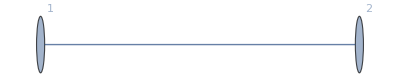

```mathematica
GraphData[{"CompleteBipartite",{1,1}},"LabeledGraph"]
```

### ConnectedDominationNumber

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"ConnectedDominationNumber"],{n,20}]
```

{1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
FindSequenceFunction[DeleteCases[seq,_Missing],n]
```

### ConnectedDominationPolynomial

```mathematica
(poly=Factor@Table[GraphData[{"CompleteBipartite",{n,n}},"ConnectedDominationPolynomial"],{n,k0=2,20}]/.f_Function:>f[x])//Column
```

4 x^2+4 x^3+x^4
9 x^2+18 x^3+15 x^4+6 x^5+x^6
16 x^2+48 x^3+68 x^4+56 x^5+28 x^6+8 x^7+x^8
25 x^2+100 x^3+200 x^4+250 x^5+210 x^6+120 x^7+45 x^8+10 x^9+x^10
36 x^2+180 x^3+465 x^4+780 x^5+922 x^6+792 x^7+495 x^8+220 x^9+66 x^10+12 x^11+x^12
49 x^2+294 x^3+931 x^4+1960 x^5+2989 x^6+3430 x^7+3003 x^8+2002 x^9+1001 x^10+364 x^11+91 x^12+14 x^13+x^14
64 x^2+448 x^3+1680 x^4+4256 x^5+7952 x^6+11424 x^7+12868 x^8+11440 x^9+8008 x^10+4368 x^11+1820 x^12+560 x^13+120 x^14+16 x^15+x^16
81 x^2+648 x^3+2808 x^4+8316 x^5+18396 x^6+31752 x^7+43740 x^8+48618 x^9+43758 x^10+31824 x^11+18564 x^12+8568 x^13+3060 x^14+816 x^15+153 x^16+18 x^17+x^18
100 x^2+900 x^3+4425 x^4+15000 x^5+38340 x^6+77280 x^7+125880 x^8+167940 x^9+184754 x^10+167960 x^11+125970 x^12+77520 x^13+38760 x^14+15504 x^15+4845 x^16+1140 x^17+190 x^18+20 x^19+x^20
(-1+(1+x)^11)^2
(-1+(1+x)^12)^2
(-1+(1+x)^13)^2
(-1+(1+x)^14)^2
(-1+(1+x)^15)^2
(-1+(1+x)^16)^2
(-1+(1+x)^17)^2
(-1+(1+x)^18)^2
(-1+(1+x)^19)^2
(-1+(1+x)^20)^2

```mathematica
coef=Factor/@FindLinearRecurrence[poly]
```

{3+3 x+x^2,-(1+x) (3+3 x+x^2),(1+x)^3}

```mathematica
ToPolynomialRecurrence[p,x,n,coef]
```

p[n,x]==(1+x)^3 p[-3+n,x]-(1+x) (3+3 x+x^2) p[-2+n,x]+(3+3 x+x^2) p[-1+n,x]

```mathematica
FormattedPolynomialRecurrence[p,x,n,coef]//TraditionalForm
```

p_n(x)==-(x^2+3 x+3) (x+1) p_(n-2)(x)+(x^2+3 x+3) p_(n-1)(x)+(x+1)^3 p_(n-3)(x)

```mathematica
TeXForm[%]
```

p_n(x)=-\left(x^2+3 x+3\right) (x+1) p_{n-2}(x)+\left(x^2+3 x+3\right) p_{n-1}(x)+(x+1)^3 p_{n-3}(x)

```mathematica
LinearRecurrence[coef,poly,{2-k0,Length[coef]-k0+1}]
```

{x^2,x^2 (2+x)^2,x^2 (3+3 x+x^2)^2}

```mathematica
FullSimplify[RSolve[Prepend[Table[p[k+k0-1,x]==poly[[k]],{k,Length[coef]}],ToPolynomialRecurrence[p,x,n,coef]],p[n,x],n],n∈Integers&&n>0]
```

{{p[n,x]→(-1+(1+x)^n)^2}}

```mathematica
gf=Factor[z^k0 FindGeneratingFunction[poly,z]]
```

```mathematica
FullSimplify[SeriesCoefficient[gf,{z,0,n}],n>0]
```

```mathematica
poly2=Table[XXX,{n,20}]
```

```mathematica
FullSimplify[poly2-poly]
```

### ConnectedInducedSubgraphCount

A286191

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"ConnectedInducedSubgraphCount"],{n,20}]
```

{3,13,55,233,971,3981,16143,65041,261139,1046549,4190231,16769049,67092507,268402717,1073676319,4294836257,17179607075,68718952485,274876858407,1099509530665}

```mathematica
FindLinearRecurrence[seq]
```

{8,-21,22,-8}

```mathematica
LinearRecurrence[{8,-21,22,-8},{3,13,55,233},20]
```

{3,13,55,233,971,3981,16143,65041,261139,1046549,4190231,16769049,67092507,268402717,1073676319,4294836257,17179607075,68718952485,274876858407,1099509530665}

```mathematica
FindSequenceFunction[DeleteMissing@seq,n]//FullSimplify
```

(-1+2^n)^2+2 n

```mathematica
Table[(2^n-1)^2+2n,{n,20}]
```

{3,13,55,233,971,3981,16143,65041,261139,1046549,4190231,16769049,67092507,268402717,1073676319,4294836257,17179607075,68718952485,274876858407,1099509530665}

```mathematica
gf=x FindGeneratingFunction[DeleteMissing@seq,x]
```

(x (3-11 x+14 x^2))/((-1+x)^2 (1-6 x+8 x^2))

```mathematica
Series[gf,{x,0,20}]
```

3 x+13 x^2+55 x^3+233 x^4+971 x^5+3981 x^6+16143 x^7+65041 x^8+261139 x^9+1046549 x^10+4190231 x^11+16769049 x^12+67092507 x^13+268402717 x^14+1073676319 x^15+4294836257 x^16+17179607075 x^17+68718952485 x^18+274876858407 x^19+1099509530665 x^20+O[x]^21

```mathematica
Refine[SeriesCoefficient[gf,{x,0,n}],n>0]
```

(-1+2^n)^2+2 n

```mathematica
CoefficientList[Series[(3-11 x+14 x^2)/((-1+x)^2 (1-6 x+8 x^2)),{x,0,20}],x]
```

{3,13,55,233,971,3981,16143,65041,261139,1046549,4190231,16769049,67092507,268402717,1073676319,4294836257,17179607075,68718952485,274876858407,1099509530665,4398042316843}

### ConnectedInducedSubgraphPolynomial

```mathematica
(poly=DeleteCases[Factor@Table[GraphData[{"CompleteBipartite",{n,n}},"ConnectedInducedSubgraphPolynomial"][x],{n,k0=2,10}],_Missing[x]])//Column
```

x (4+4 x+4 x^2+x^3)
x (6+9 x+18 x^2+15 x^3+6 x^4+x^5)
x (8+16 x+48 x^2+68 x^3+56 x^4+28 x^5+8 x^6+x^7)
x (10+25 x+100 x^2+200 x^3+250 x^4+210 x^5+120 x^6+45 x^7+10 x^8+x^9)
x (12+36 x+180 x^2+465 x^3+780 x^4+922 x^5+792 x^6+495 x^7+220 x^8+66 x^9+12 x^10+x^11)
x (14+49 x+294 x^2+931 x^3+1960 x^4+2989 x^5+3430 x^6+3003 x^7+2002 x^8+1001 x^9+364 x^10+91 x^11+14 x^12+x^13)
x (16+64 x+448 x^2+1680 x^3+4256 x^4+7952 x^5+11424 x^6+12868 x^7+11440 x^8+8008 x^9+4368 x^10+1820 x^11+560 x^12+120 x^13+16 x^14+x^15)
x (18+81 x+648 x^2+2808 x^3+8316 x^4+18396 x^5+31752 x^6+43740 x^7+48618 x^8+43758 x^9+31824 x^10+18564 x^11+8568 x^12+3060 x^13+816 x^14+153 x^15+18 x^16+x^17)
x (20+100 x+900 x^2+4425 x^3+15000 x^4+38340 x^5+77280 x^6+125880 x^7+167940 x^8+184754 x^9+167960 x^10+125970 x^11+77520 x^12+38760 x^13+15504 x^14+4845 x^15+1140 x^16+190 x^17+20 x^18+x^19)

```mathematica
coef=Factor/@FindLinearRecurrence[poly]
```

{4+3 x+x^2,-(2+x) (3+3 x+x^2),(1+x) (4+5 x+2 x^2),-(1+x)^3}

```mathematica
ToPolynomialRecurrence[p,x,n,coef]
```

p[n,x]==-(1+x)^3 p[-4+n,x]+(1+x) (4+5 x+2 x^2) p[-3+n,x]-(2+x) (3+3 x+x^2) p[-2+n,x]+(4+3 x+x^2) p[-1+n,x]

```mathematica
FormattedPolynomialRecurrence[p,x,n,coef]//TraditionalForm
```

p_n(x)==(2 x^2+5 x+4) (x+1) p_(n-3)(x)-(x+2) (x^2+3 x+3) p_(n-2)(x)+(x^2+3 x+4) p_(n-1)(x)+(x+1)^3 (-p_(n-4)(x))

```mathematica
TeXForm[%]
```

p_n(x)=\left(2 x^2+5 x+4\right) (x+1) p_{n-3}(x)-(x+2) \left(x^2+3 x+3\right) p_{n-2}(x)+\left(x^2+3 x+4\right)
   p_{n-1}(x)+(x+1)^3 \left(-p_{n-4}(x)\right)

```mathematica
LinearRecurrence[coef,poly,{2-k0,Length[coef]-k0+1}]
```

{x (2+x),x (4+4 x+4 x^2+x^3),x (6+9 x+18 x^2+15 x^3+6 x^4+x^5),x (8+16 x+48 x^2+68 x^3+56 x^4+28 x^5+8 x^6+x^7)}

```mathematica
FullSimplify[RSolve[Prepend[Table[p[k+k0-1,x]==poly[[k]],{k,Length[coef]}],ToPolynomialRecurrence[p,x,n,coef]],p[n,x],n],n∈Integers&&n>0]
```

{{p[n,x]→2 n x+(-1+(1+x)^n)^2}}

```mathematica
gf=Factor[z^k0 FindGeneratingFunction[poly,z]]
```

```mathematica
FullSimplify[SeriesCoefficient[gf,{z,0,n}],n>0]
```

```mathematica
poly2=Table[XXX,{n,20}]
```

```mathematica
FullSimplify[poly2-poly]
```

### CrossingNumber

A030179 (conjectured)

Conjectured to be crossing number of complete bipartite graph K_{n,n}.

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"CrossingNumber"],{n,20}]
```

{0,0,1,4,16,36,81,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

```mathematica
Table[Floor[(n-1)^2/4]^2,{n,20}]
```

{0,0,1,4,16,36,81,144,256,400}

```mathematica
Floor[Range[0,30]^2/4]^2
```

{0,0,1,4,16,36,81,144,256,400,625,900,1296,1764,2401,3136,4096,5184,6561,8100,10000,12100,14641,17424,20736,24336,28561,33124,38416,44100,50625}

### CycleCount

A070968

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"CycleCount"],{n,20}]
```

{0,1,15,204,3940,113865,4662231,256485040,18226108944,1623855701385}

```mathematica
FindLinearRecurrence[seq]
```

FindLinearRecurrence[{0,1,15,204,3940,113865,4662231,256485040,18226108944,1623855701385}]

```mathematica
FindSequenceFunction[seq,n]
```

FindSequenceFunction[{0,1,15,204,3940,113865,4662231,256485040,18226108944,1623855701385},n]

```mathematica
gf=x FindGeneratingFunction[seq,x]
```

x FindGeneratingFunction[{0,1,15,204,3940,113865,4662231,256485040,18226108944,1623855701385},x]

```mathematica
1/2 Sum[k ! (k-1) ! Binomial[n,k]^2,{k,2,n}]
```

1/2 (-n^2+DifferenceRoot[Function[{y,n},{n (-n+n)^2 y[n]+(-1-n-n^3+2 n^2 n-n n^2) y[1+n]+(1+n) y[2+n]==0,y[1]==0,y[2]==n^2}]][1+n])

```mathematica
Table[1/2 Sum[k ! (k-1) ! Binomial[n,k]^2,{k,2,n}],{n,20}]
```

{0,1,15,204,3940,113865,4662231,256485040,18226108944,1623855701385}

```mathematica
RSolve[(n-2)^2*(2*n^3-19*n^2+58*n-59)*a[n]==2*(2*n^7-31*n^6+200*n^5-700*n^4+1442*n^3-1764*n^2+1205*n-363)*a[n-1]-(n-1)^2*(2*n^7-35*n^6+266*n^5-1139*n^4+2962*n^3-4671*n^2+4130*n-1578)*a[n-2]+2*(n-2)^2*(n-1)^2*(2*n^5-26*n^4+134*n^3-342*n^2+431*n-217)*a[n-3]-(n-3)^2*(n-2)^2*(n-1)^2*(2*n^3-13*n^2+26*n-18)*a[n-4],a[n],n]
```

$Aborted

### CyclePolynomial

A291909

```mathematica
(poly=DeleteMissing@Factor@Table[GraphData[{"CompleteBipartite",{n,n}},"CyclePolynomial"],{n,k0=1,20}]/.f_Function:>f[x])//Column
```

0
x^4
9 x^4+6 x^6
36 x^4+96 x^6+72 x^8
100 x^4+600 x^6+1800 x^8+1440 x^10
225 x^4+2400 x^6+16200 x^8+51840 x^10+43200 x^12
441 x^4+7350 x^6+88200 x^8+635040 x^10+2116800 x^12+1814400 x^14
784 x^4+18816 x^6+352800 x^8+4515840 x^10+33868800 x^12+116121600 x^14+101606400 x^16
1296 x^4+42336 x^6+1143072 x^8+22861440 x^10+304819200 x^12+2351462400 x^14+8230118400 x^16+7315660800 x^18
2025 x^4+86400 x^6+3175200 x^8+91445760 x^10+1905120000 x^12+26127360000 x^14+205752960000 x^16+731566080000 x^18+658409472000 x^20
3025 x^4+163350 x^6+7840800 x^8+307359360 x^10+9220780800 x^12+197588160000 x^14+2766234240000 x^16+22129873920000 x^18+79667546112000 x^20+72425041920000 x^22
4356 x^4+290400 x^6+17641800 x^8+903260160 x^10+36883123200 x^12+1138107801600 x^14+24896108160000 x^16+354077982720000 x^18+2868031660032000 x^20+10429206036480000 x^22+9560105533440000 x^24
6084 x^4+490776 x^6+36808200 x^8+2385171360 x^10+127209139200 x^12+5342783846400 x^14+168297691161600 x^16+3739948692480000 x^18+53855261171712000 x^20+440633955041280000 x^22+1615657835151360000 x^24+1491376463216640000 x^26
8281 x^4+794976 x^6+72144072 x^8+5771525760 x^10+389577988800 x^12+21371135385600 x^14+916287429657600 x^16+29321197749043200 x^18+659726949353472000 x^20+9596028354232320000 x^22+79167233922416640000 x^24+292309786790461440000 x^26+271430516305428480000 x^28
11025 x^4+1242150 x^6+134152200 x^8+12985932960 x^10+1082161080000 x^12+75132897840000 x^14+4207442279040000 x^16+183257485931520000 x^18+5937542544181248000 x^20+134944148731392000000 x^22+1979180848060416000000 x^24+16442425506963456000000 x^26+61071866168721408000000 x^28+57000408424139980800000 x^30
14400 x^4+1881600 x^6+238492800 x^8+27474370560 x^10+2770332364800 x^12+237457059840000 x^14+16829769116160000 x^16+957426865274880000 x^18+42222524758622208000 x^20+1381828083009454080000 x^22+31666893568966656000000 x^24+467695658864738304000000 x^26+3908599434798170112000000 x^28+14592104556579835084800000 x^30+13680098021793595392000000 x^32
18496 x^4+2774400 x^6+407836800 x^8+55139535360 x^10+6616744243200 x^12+686250902937600 x^14+60046954007040000 x^16+4323380688506880000 x^18+249026727657996288000 x^20+11093008777492561920000 x^22+366069289657254543360000 x^24+8447752838244335616000000 x^26+125509470739630129152000000 x^28+1054279554212893084876800000 x^30+3953548328298349068288000000 x^32+3720986661927857946624000000 x^34
23409 x^4+3995136 x^6+674179200 x^8+105711298560 x^10+14887674547200 x^12+1837564401254400 x^14+194552130982809600 x^16+17293522754027520000 x^18+1260697808768606208000 x^20+73349690691991633920000 x^22+3294623606915290890240000 x^24+109482876783646589583360000 x^26+2541566782477510115328000000 x^28+37954063951664151055564800000 x^30+320237414592166274531328000000 x^32+1205599678464625974706176000000 x^34+1138621918549924531666944000000 x^36
29241 x^4+5633766 x^6+1081683072 x^8+194702952960 x^10+31801482316800 x^12+4606671867033600 x^14+580440655246233600 x^16+62429617142039347200 x^18+5618665542783541248000 x^20+413738099059515310080000 x^22+24272635144824898191360000 x^24+1097869958858233856655360000 x^26+36700224338975246065336320000 x^28+856338567909422408191180800000 x^30+12845078518641336122867712000000 x^32+108805370981432494217232384000000 x^34+411042512596522755931766784000000 x^36+389408696144074189830094848000000 x^38
36100 x^4+7797600 x^6+1690129800 x^8+346138583040 x^10+64900984320000 x^12+10903365365760000 x^14+1612335153461760000 x^16+206378899643105280000 x^18+22474662171134164992000 x^20+2043151106466742272000000 x^22+151703969655155613696000000 x^24+8962203745781500870656000000 x^26+407780270433058289614848000000 x^28+13701417086550758531058892800000 x^30+321126962966033403071692800000000 x^32+4835794265841444187432550400000000 x^34+41104251259652275593176678400000000 x^36+155763478457629675932037939200000000 x^38+147975304534748192135436042240000000 x^40

```mathematica
Length/@poly
```

{0,2,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}

```mathematica
CoefficientList[Take[poly,5],x]//Column
```

{}
{0,0,0,0,1}
{0,0,0,0,9,0,6}
{0,0,0,0,36,0,96,0,72}
{0,0,0,0,100,0,600,0,1800,0,1440}

```mathematica
coef=Factor/@FindLinearRecurrence[poly]
```

FindLinearRecurrence[{0,x^4,3 x^4 (3+2 x^2),12 x^4 (3+8 x^2+6 x^4),20 x^4 (5+30 x^2+90 x^4+72 x^6),15 x^4 (15+160 x^2+1080 x^4+3456 x^6+2880 x^8),21 x^4 (21+350 x^2+4200 x^4+30240 x^6+100800 x^8+86400 x^10),112 x^4 (7+168 x^2+3150 x^4+40320 x^6+302400 x^8+1036800 x^10+907200 x^12),432 x^4 (3+98 x^2+2646 x^4+52920 x^6+705600 x^8+5443200 x^10+19051200 x^12+16934400 x^14),135 x^4 (15+640 x^2+23520 x^4+677376 x^6+14112000 x^8+193536000 x^10+1524096000 x^12+5419008000 x^14+4877107200 x^16),55 x^4 (55+2970 x^2+142560 x^4+5588352 x^6+167650560 x^8+3592512000 x^10+50295168000 x^12+402361344000 x^14+1448500838400 x^16+1316818944000 x^18),132 x^4 (33+2200 x^2+133650 x^4+6842880 x^6+279417600 x^8+8622028800 x^10+188606880000 x^12+2682408960000 x^14+21727512576000 x^16+79009136640000 x^18+72425041920000 x^20),156 x^4 (39+3146 x^2+235950 x^4+15289560 x^6+815443200 x^8+34248614400 x^10+1078831353600 x^12+23974030080000 x^14+345226033152000 x^16+2824576634880000 x^18+10356780994560000 x^20+9560105533440000 x^22),91 x^4 (91+8736 x^2+792792 x^4+63423360 x^6+4281076800 x^8+234847641600 x^10+10069092633600 x^12+322210964275200 x^14+7249746696192000 x^16+105450861035520000 x^18+869969603543040000 x^20+3212195459235840000 x^22+2982752926433280000 x^24),105 x^4 (105+11830 x^2+1277640 x^4+123675552 x^6+10306296000 x^8+715551408000 x^10+40070878848000 x^12+1745309389824000 x^14+56548024230297600 x^16+1285182368870400000 x^18+18849341410099200000 x^20+156594528637747200000 x^22+581636820654489600000 x^24+542861032610856960000 x^26),960 x^4 (15+1960 x^2+248430 x^4+28619136 x^6+2885762880 x^8+247351104000 x^10+17531009496000 x^12+997319651328000 x^14+43981796623564800 x^16+1439404253134848000 x^18+32986347467673600000 x^20+487182977984102400000 x^22+4071457744581427200000 x^24+15200108913103994880000 x^26+14250102106034995200000 x^28),1088 x^4 (17+2550 x^2+374850 x^4+50679720 x^6+6081566400 x^8+630745315200 x^10+55190215080000 x^12+3973695485760000 x^14+228884859979776000 x^16+10195780126371840000 x^18+336460744170270720000 x^20+7764478711621632000000 x^22+115357969429807104000000 x^24+969006943210379673600000 x^26+3633776037038923776000000 x^28+3420024505448398848000000 x^30),459 x^4 (51+8704 x^2+1468800 x^4+230307840 x^6+32435020800 x^8+4003408281600 x^10+423860851814400 x^12+37676520161280000 x^14+2746618319757312000 x^16+159803247694970880000 x^18+7177829208965775360000 x^20+238524786021016535040000 x^22+5537182532630740992000000 x^24+82688592487285732147200000 x^26+697684999111473364992000000 x^28+2626578820184370315264000000 x^30+2480657774618571964416000000 x^32),513 x^4 (57+10982 x^2+2108544 x^4+379537920 x^6+61991193600 x^8+8979867187200 x^10+1131463265587200 x^12+121695160120934400 x^14+10952564410884096000 x^16+806507015710556160000 x^18+47315078255019294720000 x^20+2140097385688565022720000 x^22+71540398321589173616640000 x^24+1669275960837080717721600000 x^26+25039139412556210765824000000 x^28+212096239729887902957568000000 x^30+801252461201798744506368000000 x^32+759081279033283021111296000000 x^34),380 x^4 (95+20520 x^2+4447710 x^4+910891008 x^6+170792064000 x^8+28693066752000 x^10+4242987245952000 x^12+543102367481856000 x^14+59143847818774118400 x^16+5376713438070374400000 x^18+399220972776725299200000 x^20+23584746699425002291200000 x^22+1073105974823837604249600000 x^24+36056360754080943502786560000 x^26+845070955173772113346560000000 x^28+12725774383793274177454080000000 x^30+108169082262242830508359680000000 x^32+409903890677972831400099840000000 x^34+389408696144074189830094848000000 x^36)}]

```mathematica
1/2 Sum[Binomial[n,k]^2 k !(k-1) !x^(2k),{k,2,n}]
```

1/2 (-n^2 x^2+DifferenceRoot[Function[{y,n},{n (-n+n)^2 x^2 y[n]+(-1-n-n^3 x^2+2 n^2 n x^2-n n^2 x^2) y[1+n]+(1+n) y[2+n]==0,y[1]==0,y[2]==n^2 x^2}]][1+n])

```mathematica
Table[1/2 Sum[Binomial[n,k]^2 k !(k-1) !x^(2k),{k,2,n}],{n,5}]//Factor
```

{0,x^4,3 x^4 (3+2 x^2),12 x^4 (3+8 x^2+6 x^4),20 x^4 (5+30 x^2+90 x^4+72 x^6)}

```mathematica
Take[poly,5]
```

{0,x^4,3 x^4 (3+2 x^2),12 x^4 (3+8 x^2+6 x^4),20 x^4 (5+30 x^2+90 x^4+72 x^6)}

```mathematica
CoefficientList[Table[Sum[Binomial[n,k]^2 k !(k-1) !x^k,{k,2,n}]/2,{n,10}],x]//Flatten
```

{0,0,1,0,0,9,6,0,0,36,96,72,0,0,100,600,1800,1440,0,0,225,2400,16200,51840,43200,0,0,441,7350,88200,635040,2116800,1814400,0,0,784,18816,352800,4515840,33868800,116121600,101606400,0,0,1296,42336,1143072,22861440,304819200,2351462400,8230118400,7315660800,0,0,2025,86400,3175200,91445760,1905120000,26127360000,205752960000,731566080000,658409472000}

```mathematica
Table[1/2 Sum[Binomial[n,k]^2 k !(k-1) !x^(2k),{k,2,n}],{n,5}]//Expand//Column
```

0
x^4
9 x^4+6 x^6
36 x^4+96 x^6+72 x^8
100 x^4+600 x^6+1800 x^8+1440 x^10

### Cyclic

```mathematica
Table[GraphData[{"CompleteBipartite",{n,n}},"Cyclic"],{n,20}]
```

{False,True,True,True,True,True,True,True,True,True}

### CyclomaticNumber

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"CyclomaticNumber"],{n,20}]
```

{0,1,4,9,16,25,36,49,64,81}

```mathematica
FindSequenceFunction[seq,n]
```

(-1+n)^2

### DetourIndex

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"DetourIndex"],{n,20}]
```

{1,16,69,184,385,696,1141,1744,2529,3520}

```mathematica
FindSequenceFunction[seq,n]//Factor
```

n (2-5 n+4 n^2)

### DetourMatrix

```mathematica
GraphData[{"CompleteBipartite",{2,2}},"#"]
```

SquareGraph

```mathematica
MatrixForm/@(d1=Table[GraphData[{"CompleteBipartite",{n,n}},"DetourMatrix"],{n,5}])
```

{(0 | 1
1 | 0),(0 | 3 | 2 | 3
3 | 0 | 3 | 2
2 | 3 | 0 | 3
3 | 2 | 3 | 0),(0 | 4 | 4 | 5 | 5 | 5
4 | 0 | 4 | 5 | 5 | 5
4 | 4 | 0 | 5 | 5 | 5
5 | 5 | 5 | 0 | 4 | 4
5 | 5 | 5 | 4 | 0 | 4
5 | 5 | 5 | 4 | 4 | 0),(0 | 6 | 6 | 6 | 7 | 7 | 7 | 7
6 | 0 | 6 | 6 | 7 | 7 | 7 | 7
6 | 6 | 0 | 6 | 7 | 7 | 7 | 7
6 | 6 | 6 | 0 | 7 | 7 | 7 | 7
7 | 7 | 7 | 7 | 0 | 6 | 6 | 6
7 | 7 | 7 | 7 | 6 | 0 | 6 | 6
7 | 7 | 7 | 7 | 6 | 6 | 0 | 6
7 | 7 | 7 | 7 | 6 | 6 | 6 | 0),(0 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9 | 9
8 | 0 | 8 | 8 | 8 | 9 | 9 | 9 | 9 | 9
8 | 8 | 0 | 8 | 8 | 9 | 9 | 9 | 9 | 9
8 | 8 | 8 | 0 | 8 | 9 | 9 | 9 | 9 | 9
8 | 8 | 8 | 8 | 0 | 9 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 9 | 0 | 8 | 8 | 8 | 8
9 | 9 | 9 | 9 | 9 | 8 | 0 | 8 | 8 | 8
9 | 9 | 9 | 9 | 9 | 8 | 8 | 0 | 8 | 8
9 | 9 | 9 | 9 | 9 | 8 | 8 | 8 | 0 | 8
9 | 9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 0)}

```mathematica
MatrixForm/@(d2=Table[SparseArray[{{i_,i_}->0,{i_,j_}/;((i≤n&&j≤n)||(i>n&&j>n))->2 n-2},2 n,2 n-1],{n,5}])
```

{(0 | 1
1 | 0),(0 | 2 | 3 | 3
2 | 0 | 3 | 3
3 | 3 | 0 | 2
3 | 3 | 2 | 0),(0 | 4 | 4 | 5 | 5 | 5
4 | 0 | 4 | 5 | 5 | 5
4 | 4 | 0 | 5 | 5 | 5
5 | 5 | 5 | 0 | 4 | 4
5 | 5 | 5 | 4 | 0 | 4
5 | 5 | 5 | 4 | 4 | 0),(0 | 6 | 6 | 6 | 7 | 7 | 7 | 7
6 | 0 | 6 | 6 | 7 | 7 | 7 | 7
6 | 6 | 0 | 6 | 7 | 7 | 7 | 7
6 | 6 | 6 | 0 | 7 | 7 | 7 | 7
7 | 7 | 7 | 7 | 0 | 6 | 6 | 6
7 | 7 | 7 | 7 | 6 | 0 | 6 | 6
7 | 7 | 7 | 7 | 6 | 6 | 0 | 6
7 | 7 | 7 | 7 | 6 | 6 | 6 | 0),(0 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9 | 9
8 | 0 | 8 | 8 | 8 | 9 | 9 | 9 | 9 | 9
8 | 8 | 0 | 8 | 8 | 9 | 9 | 9 | 9 | 9
8 | 8 | 8 | 0 | 8 | 9 | 9 | 9 | 9 | 9
8 | 8 | 8 | 8 | 0 | 9 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 9 | 0 | 8 | 8 | 8 | 8
9 | 9 | 9 | 9 | 9 | 8 | 0 | 8 | 8 | 8
9 | 9 | 9 | 9 | 9 | 8 | 8 | 0 | 8 | 8
9 | 9 | 9 | 9 | 9 | 8 | 8 | 8 | 0 | 8
9 | 9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 0)}

```mathematica
d1-d2
```

{{{0,0},{0,0}},{{0,1,-1,0},{1,0,0,-1},{-1,0,0,1},{0,-1,1,0}},{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}}

### DetourPolynomial

```mathematica
(poly=Factor@Table[GraphData[{"CompleteBipartite",{n,n}},"DetourPolynomial"][x],{n,k0=1,10}])//Column
```

(-1+x) (1+x)
(-8+x) (2+x)^2 (4+x)
(-23+x) (4+x)^4 (7+x)
(-46+x) (6+x)^6 (10+x)
(-77+x) (8+x)^8 (13+x)
(-116+x) (10+x)^10 (16+x)
(-163+x) (12+x)^12 (19+x)
(-218+x) (14+x)^14 (22+x)
(-281+x) (16+x)^16 (25+x)
(-352+x) (18+x)^18 (28+x)

```mathematica
coef=Factor/@FindLinearRecurrence[poly]
```

FindLinearRecurrence[{(-1+x) (1+x),(-8+x) (2+x)^2 (4+x),(-23+x) (4+x)^4 (7+x),(-46+x) (6+x)^6 (10+x),(-77+x) (8+x)^8 (13+x),(-116+x) (10+x)^10 (16+x)}]

```mathematica
ToPolynomialRecurrence[p,x,n,coef]
```

p[n,x]==FindLinearRecurrence[{(-1+x) (1+x),(-8+x) (2+x)^2 (4+x),(-23+x) (4+x)^4 (7+x),(-46+x) (6+x)^6 (10+x),(-77+x) (8+x)^8 (13+x),(-116+x) (10+x)^10 (16+x)}].{p[-1+n,x]}

```mathematica
FormattedPolynomialRecurrence[p,x,n,coef]//TraditionalForm
```

p_n(x)==FindLinearRecurrence[{(x-1) (x+1),(x-8) (x+2)^2 (x+4),(x-23) (x+4)^4 (x+7),(x-46) (x+6)^6 (x+10),(x-77) (x+8)^8 (x+13),(x-116) (x+10)^10 (x+16)}].{p_(n-1)(x)}

```mathematica
TeXForm[%]
```

p_n(x)=\text{FindLinearRecurrence}\left[\left\{(x-1) (x+1),(x-8) (x+2)^2 (x+4),(x-23) (x+4)^4 (x+7),(x-46) (x+6)^6 (x+10),(x-77)
   (x+8)^8 (x+13),(x-116) (x+10)^{10} (x+16)\right\}\right].\left\{p_{n-1}(x)\right\}

```mathematica
LinearRecurrence[coef,poly,{2-k0,Length[coef]-k0+1}]
```

LinearRecurrence[FindLinearRecurrence[{(-1+x) (1+x),(-8+x) (2+x)^2 (4+x),(-23+x) (4+x)^4 (7+x),(-46+x) (6+x)^6 (10+x),(-77+x) (8+x)^8 (13+x),(-116+x) (10+x)^10 (16+x)}],{(-1+x) (1+x),(-8+x) (2+x)^2 (4+x),(-23+x) (4+x)^4 (7+x),(-46+x) (6+x)^6 (10+x),(-77+x) (8+x)^8 (13+x),(-116+x) (10+x)^10 (16+x)},{1,1}]

```mathematica
FullSimplify[RSolve[Prepend[Table[p[k+k0-1,x]==poly[[k]],{k,Length[coef]}],ToPolynomialRecurrence[p,x,n,coef]],p[n,x],n],n∈Integers&&n>0]
```

RSolve[{FindLinearRecurrence[{-1+x^2,(-8+x) (2+x)^2 (4+x),(-23+x) (4+x)^4 (7+x),(-46+x) (6+x)^6 (10+x),(-77+x) (8+x)^8 (13+x),(-116+x) (10+x)^10 (16+x)}].{p[-1+n,x]}==p[n,x],x^2==1+p[1,x]},p[n,x],n]

```mathematica
gf=Factor[z^k0 FindGeneratingFunction[poly,z]]
```

z FindGeneratingFunction[{(-1+x) (1+x),(-8+x) (2+x)^2 (4+x),(-23+x) (4+x)^4 (7+x),(-46+x) (6+x)^6 (10+x),(-77+x) (8+x)^8 (13+x),(-116+x) (10+x)^10 (16+x)},z]

```mathematica
FullSimplify[SeriesCoefficient[gf,{z,0,n}],n>0]
```

$Aborted

```mathematica
poly2=Table[((2 n-2+#)^(2 n-2) (3 n-2+#) (#-(2-5 n+4 n^2))&)[x],{n,20}]
```

{(-1+x) (1+x),(-8+x) (2+x)^2 (4+x),(-23+x) (4+x)^4 (7+x),(-46+x) (6+x)^6 (10+x),(-77+x) (8+x)^8 (13+x),(-116+x) (10+x)^10 (16+x),(-163+x) (12+x)^12 (19+x),(-218+x) (14+x)^14 (22+x),(-281+x) (16+x)^16 (25+x),(-352+x) (18+x)^18 (28+x)}

```mathematica
FullSimplify[poly2-poly]
```

{0,0,0,0,0,0,0,0,0,0}

### Diameter

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"Diameter"],{n,20}]
```

{1,2,2,2,2,2,2,2,2,2}

### DistanceMatrix

```mathematica
MatrixForm/@Table[GraphData[{"CompleteBipartite",{n,n}},"DistanceMatrix"],{n,5}]
```

{(0 | 1
1 | 0),(0 | 1 | 2 | 1
1 | 0 | 1 | 2
2 | 1 | 0 | 1
1 | 2 | 1 | 0),(0 | 2 | 2 | 1 | 1 | 1
2 | 0 | 2 | 1 | 1 | 1
2 | 2 | 0 | 1 | 1 | 1
1 | 1 | 1 | 0 | 2 | 2
1 | 1 | 1 | 2 | 0 | 2
1 | 1 | 1 | 2 | 2 | 0),(0 | 2 | 2 | 2 | 1 | 1 | 1 | 1
2 | 0 | 2 | 2 | 1 | 1 | 1 | 1
2 | 2 | 0 | 2 | 1 | 1 | 1 | 1
2 | 2 | 2 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 2 | 2 | 2
1 | 1 | 1 | 1 | 2 | 0 | 2 | 2
1 | 1 | 1 | 1 | 2 | 2 | 0 | 2
1 | 1 | 1 | 1 | 2 | 2 | 2 | 0),(0 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1
2 | 0 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1
2 | 2 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 0 | 2 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 0 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0 | 2 | 2 | 2 | 2
1 | 1 | 1 | 1 | 1 | 2 | 0 | 2 | 2 | 2
1 | 1 | 1 | 1 | 1 | 2 | 2 | 0 | 2 | 2
1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 0 | 2
1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 0)}

```mathematica
MatrixForm/@Table[With[{z=ConstantArray[2,n {1,1}],o=ConstantArray[1,n {1,1}]},ArrayFlatten[{{z,o},{o,z}}]]-2 IdentityMatrix[2 n],{n,5}]
```

{(0 | 1
1 | 0),(0 | 2 | 1 | 1
2 | 0 | 1 | 1
1 | 1 | 0 | 2
1 | 1 | 2 | 0),(0 | 2 | 2 | 1 | 1 | 1
2 | 0 | 2 | 1 | 1 | 1
2 | 2 | 0 | 1 | 1 | 1
1 | 1 | 1 | 0 | 2 | 2
1 | 1 | 1 | 2 | 0 | 2
1 | 1 | 1 | 2 | 2 | 0),(0 | 2 | 2 | 2 | 1 | 1 | 1 | 1
2 | 0 | 2 | 2 | 1 | 1 | 1 | 1
2 | 2 | 0 | 2 | 1 | 1 | 1 | 1
2 | 2 | 2 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 2 | 2 | 2
1 | 1 | 1 | 1 | 2 | 0 | 2 | 2
1 | 1 | 1 | 1 | 2 | 2 | 0 | 2
1 | 1 | 1 | 1 | 2 | 2 | 2 | 0),(0 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1
2 | 0 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1
2 | 2 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 0 | 2 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 0 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0 | 2 | 2 | 2 | 2
1 | 1 | 1 | 1 | 1 | 2 | 0 | 2 | 2 | 2
1 | 1 | 1 | 1 | 1 | 2 | 2 | 0 | 2 | 2
1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 0 | 2
1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 0)}

### DistancePolynomial

```mathematica
(poly=Factor@Table[GraphData[{"CompleteBipartite",{n,n}},"DistancePolynomial"][x],{n,k0=1,10}])//Column
```

(-1+x) (1+x)
(-4+x) x (2+x)^2
(-7+x) (-1+x) (2+x)^4
(-10+x) (-2+x) (2+x)^6
(-13+x) (-3+x) (2+x)^8
(-16+x) (-4+x) (2+x)^10
(-19+x) (-5+x) (2+x)^12
(-22+x) (-6+x) (2+x)^14
(-25+x) (-7+x) (2+x)^16
(-28+x) (-8+x) (2+x)^18

```mathematica
coef=Factor/@FindLinearRecurrence[poly]
```

{3 (2+x)^2,-3 (2+x)^4,(2+x)^6}

```mathematica
ToPolynomialRecurrence[p,x,n,coef]
```

p[n,x]==(2+x)^6 p[-3+n,x]-3 (2+x)^4 p[-2+n,x]+3 (2+x)^2 p[-1+n,x]

```mathematica
FormattedPolynomialRecurrence[p,x,n,coef]//TraditionalForm
```

p_n(x)==(x+2)^6 p_(n-3)(x)-3 (x+2)^4 p_(n-2)(x)+3 (x+2)^2 p_(n-1)(x)

```mathematica
TeXForm[%]
```

p_n(x)=(x+2)^6 p_{n-3}(x)-3 (x+2)^4 p_{n-2}(x)+3 (x+2)^2 p_{n-1}(x)

```mathematica
LinearRecurrence[coef,poly,{2-k0,Length[coef]-k0+1}]
```

{(-1+x) (1+x),(-4+x) x (2+x)^2,(-7+x) (-1+x) (2+x)^4}

```mathematica
FullSimplify[RSolve[Prepend[Table[p[k+k0-1,x]==poly[[k]],{k,Length[coef]}],ToPolynomialRecurrence[p,x,n,coef]],p[n,x],n],n∈Integers&&n>0]
```

{{p[n,x]→(2+x)^(-2+2 n) (2-3 n+x) (2-n+x)}}

```mathematica
gf=Factor[z^k0 FindGeneratingFunction[poly,z]]
```

-(z (-1+x^2+12 z-4 x z-21 x^2 z-12 x^3 z-2 x^4 z+64 z^2+192 x z^2+240 x^2 z^2+160 x^3 z^2+60 x^4 z^2+12 x^5 z^2+x^6 z^2))/((-1+4 z+4 x z+x^2 z)^3)

```mathematica
FullSimplify[SeriesCoefficient[gf,{z,0,n}],n>0]
```

(2+x)^(-2+2 n) (2-3 n+x) (2-n+x)

```mathematica
poly2=Table[(2+x)^(-2+2 n) (2-3 n+x) (2-n+x),{n,20}]
```

{(-1+x) (1+x),(-4+x) x (2+x)^2,(-7+x) (-1+x) (2+x)^4,(-10+x) (-2+x) (2+x)^6,(-13+x) (-3+x) (2+x)^8,(-16+x) (-4+x) (2+x)^10,(-19+x) (-5+x) (2+x)^12,(-22+x) (-6+x) (2+x)^14,(-25+x) (-7+x) (2+x)^16,(-28+x) (-8+x) (2+x)^18}

```mathematica
FullSimplify[poly2-poly]
```

{0,0,0,0,0,0,0,0,0,0}

### DistinguishingNumber

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"DistinguishingNumber"],{n,20}]
```

{2,3,4,5,6,7,8,9,10,11}

### DomaticNumber

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"DomaticNumber"],{n,20}]
```

{2,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

### DominatingSetCount

A191341

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"DominatingSetCount"],{n,20}]
```

{3,11,51,227,963,3971,16131,65027,261123,1046531}

```mathematica
FindSequenceFunction[seq,n]//FullSimplify
```

3-2^(1+n)+4^n

```mathematica
seq=Table[3-2^(1+n)+4^n,{n,40}]
```

{3,11,51,227,963,3971,16131,65027,261123,1046531,4190211,16769027,67092483,268402691,1073676291,4294836227,17179607043,68718952451,274876858371,1099509530627,4398042316803,17592177655811,70368727400451,281474943156227,1125899839733763,4503599493152771,18014398241046531,72057593501057027,288230375077969923,1152921502459363331,4611686014132420611,18446744065119617027,73786976277658337283,295147905144993087491,1180591620648691826691,4722366482732206260227,18889465931203702947843,75557863725364567605251,302231454902557782048771,1208925819612430151450627}

```mathematica
FindLinearRecurrence[seq]
```

{7,-14,8}

```mathematica
LinearRecurrence[{7,-14,8},{3,11,51},20]
```

{3,11,51,227,963,3971,16131,65027,261123,1046531,4190211,16769027,67092483,268402691,1073676291,4294836227,17179607043,68718952451,274876858371,1099509530627}

```mathematica
gf=x FindGeneratingFunction[seq,x]//Factor
```

-(x (3-10 x+16 x^2))/((-1+x) (-1+2 x) (-1+4 x))

```mathematica
CoefficientList[Series[-(3-10 x+16 x^2)/((-1+x) (-1+2 x) (-1+4 x)),{x,0,20}],x]
```

{3,11,51,227,963,3971,16131,65027,261123,1046531,4190211,16769027,67092483,268402691,1073676291,4294836227,17179607043,68718952451,274876858371,1099509530627,4398042316803}

### DominationNumber

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"DominationNumber"],{n,20}]
```

{1,2,2,2,2,2,2,2,2,2}

### DominationPolynomial

```mathematica
(poly=Factor@Table[GraphData[{"CompleteBipartite",{n,n}},"DominationPolynomial"][x],{n,k0=1,10}])//Column
```

x (2+x)
x^2 (6+4 x+x^2)
x^2 (9+20 x+15 x^2+6 x^3+x^4)
x^2 (16+48 x+70 x^2+56 x^3+28 x^4+8 x^5+x^6)
x^2 (25+100 x+200 x^2+252 x^3+210 x^4+120 x^5+45 x^6+10 x^7+x^8)
x^2 (36+180 x+465 x^2+780 x^3+924 x^4+792 x^5+495 x^6+220 x^7+66 x^8+12 x^9+x^10)
x^2 (49+294 x+931 x^2+1960 x^3+2989 x^4+3432 x^5+3003 x^6+2002 x^7+1001 x^8+364 x^9+91 x^10+14 x^11+x^12)
x^2 (64+448 x+1680 x^2+4256 x^3+7952 x^4+11424 x^5+12870 x^6+11440 x^7+8008 x^8+4368 x^9+1820 x^10+560 x^11+120 x^12+16 x^13+x^14)
x^2 (81+648 x+2808 x^2+8316 x^3+18396 x^4+31752 x^5+43740 x^6+48620 x^7+43758 x^8+31824 x^9+18564 x^10+8568 x^11+3060 x^12+816 x^13+153 x^14+18 x^15+x^16)
x^2 (100+900 x+4425 x^2+15000 x^3+38340 x^4+77280 x^5+125880 x^6+167940 x^7+184756 x^8+167960 x^9+125970 x^10+77520 x^11+38760 x^12+15504 x^13+4845 x^14+1140 x^15+190 x^16+20 x^17+x^18)

```mathematica
coef=Factor/@FindLinearRecurrence[poly]
```

{(1+x) (3+x),-(1+2 x) (3+3 x+x^2),(1+x) (1+5 x+4 x^2+x^3),-x (1+x)^3}

```mathematica
ToPolynomialRecurrence[p,x,n,coef]
```

p[n,x]==-x (1+x)^3 p[-4+n,x]+(1+x) (1+5 x+4 x^2+x^3) p[-3+n,x]-(1+2 x) (3+3 x+x^2) p[-2+n,x]+(1+x) (3+x) p[-1+n,x]

```mathematica
FormattedPolynomialRecurrence[p,x,n,coef]//TraditionalForm
```

p_n(x)==-(2 x+1) (x^2+3 x+3) p_(n-2)(x)+(x^3+4 x^2+5 x+1) (x+1) p_(n-3)(x)-x (x+1)^3 p_(n-4)(x)+(x+3) (x+1) p_(n-1)(x)

```mathematica
TeXForm[%]
```

p_n(x)=-(2 x+1) \left(x^2+3 x+3\right) p_{n-2}(x)+\left(x^3+4 x^2+5 x+1\right) (x+1) p_{n-3}(x)-x (x+1)^3 p_{n-4}(x)+(x+3) (x+1)
   p_{n-1}(x)

```mathematica
LinearRecurrence[coef,poly,{2-k0,Length[coef]-k0+1}]
```

{x (2+x),x^2 (6+4 x+x^2),x^2 (9+20 x+15 x^2+6 x^3+x^4),x^2 (16+48 x+70 x^2+56 x^3+28 x^4+8 x^5+x^6)}

```mathematica
FullSimplify[RSolve[Prepend[Table[p[k+k0-1,x]==poly[[k]],{k,Length[coef]}],ToPolynomialRecurrence[p,x,n,coef]],p[n,x],n],n∈Integers&&n>0]
```

{{p[n,x]→2 x^n+(-1+(1+x)^n)^2}}

```mathematica
gf=Factor[z^k0 FindGeneratingFunction[poly,z]]
```

-(x z (-2-x+6 z+5 x z+2 x^2 z-6 z^2-12 x z^2-7 x^2 z^2-x^3 z^2+2 z^3+6 x z^3+6 x^2 z^3+2 x^3 z^3))/((-1+z) (-1+x z) (-1+z+x z) (-1+z+2 x z+x^2 z))

```mathematica
FullSimplify[SeriesCoefficient[gf,{z,0,n}],n>0]
```

2 x^n+(-1+(1+x)^n)^2

```mathematica
poly2=Table[XXX,{n,20}]
```

{XXX,XXX,XXX,XXX,XXX,XXX,XXX,XXX,XXX,XXX}

```mathematica
FullSimplify[poly2-poly]
```

### EdgeChromaticNumber

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"EdgeChromaticNumber"],{n,20}]
```

{1,2,3,4,5,6,7,8,9,10}

### EdgeConnectivity

```mathematica
Table[GraphData[{"CompleteBipartite",{n,n}},"EdgeConnectivity"],{n,20}]
```

{1,2,3,4,5,6,7,8,9,10}

### EdgeCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"M"],{n,20}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
FindSequenceFunction[seq,n]
```

n^2

### EdgeCoverCount

A048291

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"EdgeCoverCount"],{n,20}]
```

{1,7,265,41503,24997921,57366997447,505874809287625,17343602252913832063,2334958727565749108488321,1243237913592275536716800402887}

```mathematica
FindLinearRecurrence[seq]
```

FindLinearRecurrence[{1,7,265,41503,24997921,57366997447,505874809287625,17343602252913832063,2334958727565749108488321,1243237913592275536716800402887}]

```mathematica
FindSequenceFunction[seq,n]
```

FindSequenceFunction[{1,7,265,41503,24997921,57366997447,505874809287625,17343602252913832063,2334958727565749108488321,1243237913592275536716800402887},n]

```mathematica
gf=x FindGeneratingFunction[seq,x]
```

x FindGeneratingFunction[{1,7,265,41503,24997921,57366997447,505874809287625,17343602252913832063,2334958727565749108488321,1243237913592275536716800402887},x]

```mathematica
Sum[(-1)^k Binomial[n,k] 2^((n-k)n)(1-2^(k-n))^n,{k,0,n}]
```

∑_(k=0)^n (-1)^k 2^(n (-k+n)) (1-2^(k-n))^n Binomial[n,k]

```mathematica
Table[Sum[(-1)^k Binomial[n,k] 2^((n-k)n)(1-2^(k-n))^n,{k,0,n}] ,{n,20}]
```

{1,7,265,41503,24997921,57366997447,505874809287625,17343602252913832063,2334958727565749108488321,1243237913592275536716800402887}

```mathematica
Table[(Sum[(-1)^k Binomial[n,k] ((#+1)^(n-k)-1)^n,{k,0,n}]&)[1],{n,20}]
```

{1,7,265,41503,24997921,57366997447,505874809287625,17343602252913832063,2334958727565749108488321,1243237913592275536716800402887}

### EdgeCoverNumber

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"EdgeCoverNumber"],{n,20}]
```

{1,2,3,4,5,6,7,8,9,10}

### EdgeCoverPolynomial

A055599

```mathematica
(poly=Factor@Table[GraphData[{"CompleteBipartite",{n,n}},"EdgeCoverPolynomial"][x],{n,k0=1,10}])//Column
```

x
x^2 (2+4 x+x^2)
x^3 (6+45 x+90 x^2+78 x^3+36 x^4+9 x^5+x^6)
x^4 (24+432 x+2248 x^2+5776 x^3+9066 x^4+9696 x^5+7480 x^6+4272 x^7+1812 x^8+560 x^9+120 x^10+16 x^11+x^12)
x^5 (120+4200 x+43000 x^2+222925 x^3+727375 x^4+1674840 x^5+2913100 x^6+3995100 x^7+4441200 x^8+4073100 x^9+3114140 x^10+1994550 x^11+1070175 x^12+478800 x^13+176900 x^14+53120 x^15+12650 x^16+2300 x^17+300 x^18+25 x^19+x^20)
x^6 (720+43200 x+755100 x^2+6700500 x^3+37638036 x^4+150426216 x^5+459195450 x^6+1121621400 x^7+2263460580 x^8+3860573280 x^9+5657533245 x^10+7209492300 x^11+8058525440 x^12+7949616120 x^13+6949563210 x^14+5396732880 x^15+3726153180 x^16+2286371520 x^17+1244553330 x^18+599095260 x^19+253857996 x^20+94094560 x^21+30255120 x^22+8347320 x^23+1947780 x^24+376992 x^25+58905 x^26+7140 x^27+630 x^28+36 x^29+x^30)
x^7 (5040+476280 x+13003620 x^2+179494350 x^3+1565720814 x^4+9718314256 x^5+46152450946 x^6+175976655414 x^7+557244880990 x^8+1501947411853 x^9+3509791304040 x^10+7211688390116 x^11+13172179899844 x^12+21569922023916 x^13+31880291380084 x^14+42753092812486 x^15+52236172871484 x^16+58332223227691 x^17+59677143907185 x^18+56027633300730 x^19+48324082891112 x^20+38311640567844 x^21+27920742308676 x^22+18696980337210 x^23+11494351298080 x^24+6478673357772 x^25+3341866882501 x^26+1573928312334 x^27+674871177750 x^28+262523342809 x^29+92251825484 x^30+29134349244 x^31+8217661816 x^32+2054443580 x^33+450977478 x^34+85900570 x^35+13983816 x^36+1906884 x^37+211876 x^38+18424 x^39+1176 x^40+49 x^41+x^42)
x^8 (40320+5644800 x+226262400 x^2+4556952960 x^3+57749731648 x^4+519271135488 x^5+3566556292160 x^6+19657615574528 x^7+90028720358360 x^8+351514361548224 x^9+1193072116977440 x^10+3573623235835968 x^11+9559824780695504 x^12+23059104048856512 x^13+50541931683354720 x^14+101304764450576064 x^15+186655462420913192 x^16+317508331805082880 x^17+500405317681401888 x^18+732862828812485056 x^19+999803358862846160 x^20+1273103634274665536 x^21+1515555647933770016 x^22+1688874238954056000 x^23+1763485190766749898 x^24+1726688643216599104 x^25+1586134485267095680 x^26+1367324044785087872 x^27+1106221181262369088 x^28+839849652630596160 x^29+598162836219315360 x^30+399471228065063616 x^31+249982874856540280 x^32+146461408585826880 x^33+80254578916658720 x^34+41077759265070528 x^35+19610791782671376 x^36+8717495704706880 x^37+3601119079436704 x^38+1379248959867072 x^39+488504209177572 x^40+159515289184384 x^41+47855180463840 x^42+13136797695168 x^43+3284208826416 x^44+743595338304 x^45+151473190176 x^46+27540583616 x^47+4426165352 x^48+621216192 x^49+74974368 x^50+7624512 x^51+635376 x^52+41664 x^53+2016 x^54+64 x^55+x^56)
x^9 (362880+71850240 x+4037765760 x^2+113261289120 x^3+1988911241856 x^4+24683285553696 x^5+233296482130128 x^6+1765712837288745 x^7+11089730000058705 x^8+59343319986818256 x^9+276072045108270768 x^10+1134266567078769264 x^11+4167777097830623256 x^12+13835893063608599040 x^13+41845230914503059000 x^14+116097848572986361692 x^15+297203533764648453828 x^16+705427181838826806240 x^17+1558882348748975601456 x^18+3218592824581438022832 x^19+6227550388806871079232 x^20+11321066417142267048024 x^21+19379303153546479365240 x^22+31296498982951818266316 x^23+47760504213044704865238 x^24+68970640494606154527888 x^25+94362392031150480759648 x^26+122436505674389184141024 x^27+150788325666136034762676 x^28+176389848525472636578048 x^29+196099101443874285955368 x^30+207285383754141364176120 x^31+208400975784256403874096 x^32+199329328374825735416736 x^33+181402681312013248370304 x^34+157086327529530388815084 x^35+129431085867942796666764 x^36+101459120520384867067128 x^37+75649640367439048855896 x^38+53636630161727574806166 x^39+36148896056430154545786 x^40+23147904692466567945792 x^41+14075983280554171321032 x^42+8123166406124144251776 x^43+4445705139699852836424 x^44+2305533683859473569488 x^45+1131929476790834418984 x^46+525577910851559613096 x^47+230528326419135308592 x^48+95394258908111507832 x^49+37188412954478341992 x^50+13635942866612427960 x^51+4694381787704777784 x^52+1514324602649618424 x^53+456702449470998696 x^54+128447779356011196 x^55+33594064431274413 x^56+8144019235517616 x^57+1823288266320408 x^58+375382911692880 x^59+70724319111180 x^60+12124169128512 x^61+1878392406024 x^62+260887834332 x^63+32164253550 x^64+3477216600 x^65+324540216 x^66+25621596 x^67+1663740 x^68+85320 x^69+3240 x^70+81 x^71+x^72)
x^10 (3628800+979776000 x+74481120000 x^2+2808028944000 x^3+65929868222400 x^4+1089340983158400 x^5+13660234190367300 x^6+136790652050108100 x^7+1134255899855839600 x^8+8000711406953639200 x^9+49010044816244986200 x^10+264992293821639110400 x^11+1281222589246996719600 x^12+5598369308321041809600 x^13+22301955274254041085300 x^14+81590605190314522273800 x^15+275820487444408494372300 x^16+866112590891476147845600 x^17+2537633859754052335183800 x^18+6964116588779921029663200 x^19+17961255568345373273562480 x^20+43661970045068283780408000 x^21+100292485452557143036402125 x^22+218171386572669279962777700 x^23+450339459839091950075182050 x^24+883571889684583622629351260 x^25+1650295956307016766881044575 x^26+2938195729105716600942789600 x^27+4992420942883393674011227800 x^28+8104112918333652950213565600 x^29+12579461604217826264292109560 x^30+18686643390699159837304389600 x^31+26584004003812557677693556000 x^32+36240775962213516625446421200 x^33+47369117349065630073869732700 x^34+59390117648076163332602704080 x^35+71453726933329932835881190800 x^36+82522191943457873352236988000 x^37+91510257663564838954434236700 x^38+97457722909495178985687015000 x^39+99697041163147242246012619992 x^40+97975809321059632654830513600 x^41+92503269763255342153085941800 x^42+83909054900779788724034526000 x^43+73125268875833842149290472600 x^44+61222125356107746633801113280 x^45+49236745603566240571387040100 x^46+38032124376462311197615896000 x^47+28210778697036053055667016400 x^48+20090388081052374035355774000 x^49+13732773168099151100916230220 x^50+9007303623719204004796740000 x^51+5666952260000836811752927200 x^52+3418653197837863743372252000 x^53+1976623926784198553738784150 x^54+1094834888891893730509770600 x^55+580629450272273202458134950 x^56+294660911866514875198964700 x^57+143001841782803955521090175 x^58+66321239598860333300666400 x^59+29371320208165992010239720 x^60+12410560596718812582108000 x^61+4998737909100570015007200 x^62+1917334512108173119011600 x^63+699570523156913062944300 x^64+242518353806892449422224 x^65+79775894793505845122100 x^66+24865237438546247226000 x^67+7332061407226233930000 x^68+2041840578968244180000 x^69+535983255990900053100 x^70+132341558814161694900 x^71+30664509252677779600 x^72+6650134723509690600 x^73+1345860616594522050 x^74+253338470471003280 x^75+44186942626219800 x^76+7110542497449600 x^77+1050421051026600 x^78+141629804641800 x^79+17310309456420 x^80+1902231808400 x^81+186087894300 x^82+16007560800 x^83+1192052400 x^84+75287520 x^85+3921225 x^86+161700 x^87+4950 x^88+100 x^89+x^90)

```mathematica
Take[poly,5]//Expand
```

{x,2 x^2+4 x^3+x^4,6 x^3+45 x^4+90 x^5+78 x^6+36 x^7+9 x^8+x^9,24 x^4+432 x^5+2248 x^6+5776 x^7+9066 x^8+9696 x^9+7480 x^10+4272 x^11+1812 x^12+560 x^13+120 x^14+16 x^15+x^16,120 x^5+4200 x^6+43000 x^7+222925 x^8+727375 x^9+1674840 x^10+2913100 x^11+3995100 x^12+4441200 x^13+4073100 x^14+3114140 x^15+1994550 x^16+1070175 x^17+478800 x^18+176900 x^19+53120 x^20+12650 x^21+2300 x^22+300 x^23+25 x^24+x^25}

```mathematica
CoefficientList[#,x]&/@%
```

{{0,1},{0,0,2,4,1},{0,0,0,6,45,90,78,36,9,1},{0,0,0,0,24,432,2248,5776,9066,9696,7480,4272,1812,560,120,16,1},{0,0,0,0,0,120,4200,43000,222925,727375,1674840,2913100,3995100,4441200,4073100,3114140,1994550,1070175,478800,176900,53120,12650,2300,300,25,1}}

```mathematica
coef=Factor/@FindLinearRecurrence[poly]
```

FindLinearRecurrence[{x,x^2 (2+4 x+x^2),x^3 (6+45 x+90 x^2+78 x^3+36 x^4+9 x^5+x^6),x^4 (24+432 x+2248 x^2+5776 x^3+9066 x^4+9696 x^5+7480 x^6+4272 x^7+1812 x^8+560 x^9+120 x^10+16 x^11+x^12),x^5 (120+4200 x+43000 x^2+222925 x^3+727375 x^4+1674840 x^5+2913100 x^6+3995100 x^7+4441200 x^8+4073100 x^9+3114140 x^10+1994550 x^11+1070175 x^12+478800 x^13+176900 x^14+53120 x^15+12650 x^16+2300 x^17+300 x^18+25 x^19+x^20),x^6 (720+43200 x+755100 x^2+6700500 x^3+37638036 x^4+150426216 x^5+459195450 x^6+1121621400 x^7+2263460580 x^8+3860573280 x^9+5657533245 x^10+7209492300 x^11+8058525440 x^12+7949616120 x^13+6949563210 x^14+5396732880 x^15+3726153180 x^16+2286371520 x^17+1244553330 x^18+599095260 x^19+253857996 x^20+94094560 x^21+30255120 x^22+8347320 x^23+1947780 x^24+376992 x^25+58905 x^26+7140 x^27+630 x^28+36 x^29+x^30),x^7 (5040+476280 x+13003620 x^2+179494350 x^3+1565720814 x^4+9718314256 x^5+46152450946 x^6+175976655414 x^7+557244880990 x^8+1501947411853 x^9+3509791304040 x^10+7211688390116 x^11+13172179899844 x^12+21569922023916 x^13+31880291380084 x^14+42753092812486 x^15+52236172871484 x^16+58332223227691 x^17+59677143907185 x^18+56027633300730 x^19+48324082891112 x^20+38311640567844 x^21+27920742308676 x^22+18696980337210 x^23+11494351298080 x^24+6478673357772 x^25+3341866882501 x^26+1573928312334 x^27+674871177750 x^28+262523342809 x^29+92251825484 x^30+29134349244 x^31+8217661816 x^32+2054443580 x^33+450977478 x^34+85900570 x^35+13983816 x^36+1906884 x^37+211876 x^38+18424 x^39+1176 x^40+49 x^41+x^42),x^8 (40320+5644800 x+226262400 x^2+4556952960 x^3+57749731648 x^4+519271135488 x^5+3566556292160 x^6+19657615574528 x^7+90028720358360 x^8+351514361548224 x^9+1193072116977440 x^10+3573623235835968 x^11+9559824780695504 x^12+23059104048856512 x^13+50541931683354720 x^14+101304764450576064 x^15+186655462420913192 x^16+317508331805082880 x^17+500405317681401888 x^18+732862828812485056 x^19+999803358862846160 x^20+1273103634274665536 x^21+1515555647933770016 x^22+1688874238954056000 x^23+1763485190766749898 x^24+1726688643216599104 x^25+1586134485267095680 x^26+1367324044785087872 x^27+1106221181262369088 x^28+839849652630596160 x^29+598162836219315360 x^30+399471228065063616 x^31+249982874856540280 x^32+146461408585826880 x^33+80254578916658720 x^34+41077759265070528 x^35+19610791782671376 x^36+8717495704706880 x^37+3601119079436704 x^38+1379248959867072 x^39+488504209177572 x^40+159515289184384 x^41+47855180463840 x^42+13136797695168 x^43+3284208826416 x^44+743595338304 x^45+151473190176 x^46+27540583616 x^47+4426165352 x^48+621216192 x^49+74974368 x^50+7624512 x^51+635376 x^52+41664 x^53+2016 x^54+64 x^55+x^56),x^9 (362880+71850240 x+4037765760 x^2+113261289120 x^3+1988911241856 x^4+24683285553696 x^5+233296482130128 x^6+1765712837288745 x^7+11089730000058705 x^8+59343319986818256 x^9+276072045108270768 x^10+1134266567078769264 x^11+4167777097830623256 x^12+13835893063608599040 x^13+41845230914503059000 x^14+116097848572986361692 x^15+297203533764648453828 x^16+705427181838826806240 x^17+1558882348748975601456 x^18+3218592824581438022832 x^19+6227550388806871079232 x^20+11321066417142267048024 x^21+19379303153546479365240 x^22+31296498982951818266316 x^23+47760504213044704865238 x^24+68970640494606154527888 x^25+94362392031150480759648 x^26+122436505674389184141024 x^27+150788325666136034762676 x^28+176389848525472636578048 x^29+196099101443874285955368 x^30+207285383754141364176120 x^31+208400975784256403874096 x^32+199329328374825735416736 x^33+181402681312013248370304 x^34+157086327529530388815084 x^35+129431085867942796666764 x^36+101459120520384867067128 x^37+75649640367439048855896 x^38+53636630161727574806166 x^39+36148896056430154545786 x^40+23147904692466567945792 x^41+14075983280554171321032 x^42+8123166406124144251776 x^43+4445705139699852836424 x^44+2305533683859473569488 x^45+1131929476790834418984 x^46+525577910851559613096 x^47+230528326419135308592 x^48+95394258908111507832 x^49+37188412954478341992 x^50+13635942866612427960 x^51+4694381787704777784 x^52+1514324602649618424 x^53+456702449470998696 x^54+128447779356011196 x^55+33594064431274413 x^56+8144019235517616 x^57+1823288266320408 x^58+375382911692880 x^59+70724319111180 x^60+12124169128512 x^61+1878392406024 x^62+260887834332 x^63+32164253550 x^64+3477216600 x^65+324540216 x^66+25621596 x^67+1663740 x^68+85320 x^69+3240 x^70+81 x^71+x^72),x^10 (3628800+979776000 x+74481120000 x^2+2808028944000 x^3+65929868222400 x^4+1089340983158400 x^5+13660234190367300 x^6+136790652050108100 x^7+1134255899855839600 x^8+8000711406953639200 x^9+49010044816244986200 x^10+264992293821639110400 x^11+1281222589246996719600 x^12+5598369308321041809600 x^13+22301955274254041085300 x^14+81590605190314522273800 x^15+275820487444408494372300 x^16+866112590891476147845600 x^17+2537633859754052335183800 x^18+6964116588779921029663200 x^19+17961255568345373273562480 x^20+43661970045068283780408000 x^21+100292485452557143036402125 x^22+218171386572669279962777700 x^23+450339459839091950075182050 x^24+883571889684583622629351260 x^25+1650295956307016766881044575 x^26+2938195729105716600942789600 x^27+4992420942883393674011227800 x^28+8104112918333652950213565600 x^29+12579461604217826264292109560 x^30+18686643390699159837304389600 x^31+26584004003812557677693556000 x^32+36240775962213516625446421200 x^33+47369117349065630073869732700 x^34+59390117648076163332602704080 x^35+71453726933329932835881190800 x^36+82522191943457873352236988000 x^37+91510257663564838954434236700 x^38+97457722909495178985687015000 x^39+99697041163147242246012619992 x^40+97975809321059632654830513600 x^41+92503269763255342153085941800 x^42+83909054900779788724034526000 x^43+73125268875833842149290472600 x^44+61222125356107746633801113280 x^45+49236745603566240571387040100 x^46+38032124376462311197615896000 x^47+28210778697036053055667016400 x^48+20090388081052374035355774000 x^49+13732773168099151100916230220 x^50+9007303623719204004796740000 x^51+5666952260000836811752927200 x^52+3418653197837863743372252000 x^53+1976623926784198553738784150 x^54+1094834888891893730509770600 x^55+580629450272273202458134950 x^56+294660911866514875198964700 x^57+143001841782803955521090175 x^58+66321239598860333300666400 x^59+29371320208165992010239720 x^60+12410560596718812582108000 x^61+4998737909100570015007200 x^62+1917334512108173119011600 x^63+699570523156913062944300 x^64+242518353806892449422224 x^65+79775894793505845122100 x^66+24865237438546247226000 x^67+7332061407226233930000 x^68+2041840578968244180000 x^69+535983255990900053100 x^70+132341558814161694900 x^71+30664509252677779600 x^72+6650134723509690600 x^73+1345860616594522050 x^74+253338470471003280 x^75+44186942626219800 x^76+7110542497449600 x^77+1050421051026600 x^78+141629804641800 x^79+17310309456420 x^80+1902231808400 x^81+186087894300 x^82+16007560800 x^83+1192052400 x^84+75287520 x^85+3921225 x^86+161700 x^87+4950 x^88+100 x^89+x^90)}]

```mathematica
ToPolynomialRecurrence[p,x,n,coef]
```

```mathematica
FormattedPolynomialRecurrence[p,x,n,coef]//TraditionalForm
```

```mathematica
TeXForm[%]
```

```mathematica
LinearRecurrence[coef,poly,{2-k0,Length[coef]-k0+1}]
```

```mathematica
FullSimplify[RSolve[Prepend[Table[p[k+k0-1,x]==poly[[k]],{k,Length[coef]}],ToPolynomialRecurrence[p,x,n,coef]],p[n,x],n],n∈Integers&&n>0]
```

```mathematica
gf=Factor[z^k0 FindGeneratingFunction[poly,z]]
```

```mathematica
FullSimplify[SeriesCoefficient[gf,{z,0,n}],n>0]
```

```mathematica
poly2=Table[XXX,{n,20}]
```

```mathematica
FullSimplify[poly2-poly]
```

### EulerianCycleCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"EulerianCycleCount"],{n,20}]
```

{0,1,0,1120,0,35179,0,2064746,0,Missing[NotAvailable],0,Missing[NotAvailable],0,Missing[NotAvailable],0,Missing[NotAvailable],0,Missing[NotAvailable],0,Missing[NotAvailable]}

```mathematica
seq[[2;;All;;2]]
```

{1,1120,35179,2064746,Missing[NotAvailable]}

### FaceCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"FaceCount"],{n,20}]
```

{0,1,Missing[NotApplicable],Missing[NotApplicable],Missing[NotApplicable],Missing[NotApplicable],Missing[NotApplicable],Missing[NotApplicable],Missing[NotApplicable],Missing[NotApplicable]}

### FlowPolynomial

```mathematica
(poly=Factor@Table[GraphData[{"CompleteBipartite",{n,n}},"FlowPolynomial"][x],{n,k0=1,10}])//Column
```

0
-1+x
(-2+x) (-1+x) (10-6 x+x^2)
(-1+x) (1071-2709 x+3273 x^2-2475 x^3+1269 x^4-447 x^5+105 x^6-15 x^7+x^8)
(-2+x) (-1+x) (53552-200792 x+402936 x^2-561100 x^3+592472 x^4-493292 x^5+329946 x^6-178560 x^7+78072 x^8-27312 x^9+7496 x^10-1560 x^11+232 x^12-22 x^13+x^14)
(-1+x) (17201225-107291200 x+360368450 x^2-857149750 x^3+1597205370 x^4-2448026400 x^5+3171420375 x^6-3531302175 x^7+3416081725 x^8-2890909115 x^9+2149108500 x^10-1406254500 x^11+810042000 x^12-410102250 x^13+181869390 x^14-70278600 x^15+23487100 x^16-6719300 x^17+1622800 x^18-324620 x^19+52360 x^20-6545 x^21+595 x^22-35 x^23+x^24)
(-2+x) (-1+x) (2026567728-16160399856 x+71577077292 x^2-230039983044 x^3+591804243234 x^4-1278555502644 x^5+2384262779748 x^6-3905512165806 x^7+5686951578126 x^8-7424334978246 x^9+8743975668975 x^10-9332763171375 x^11+9057142143850 x^12-8010249463180 x^13+6465570617240 x^14-4766409573335 x^15+3209467856372 x^16-1972866378504 x^17+1105830776508 x^18-564211647936 x^19+261403297904 x^20-109632480038 x^21+41459037971 x^22-14068027792 x^23+4257631612 x^24-1140758632 x^25+268093644 x^26-54621648 x^27+9503418 x^28-1384040 x^29+164132 x^30-15224 x^31+1036 x^32-46 x^33+x^34)
(-1+x) (1318104508735-14425958904273 x+87159390968167 x^2-382122743203369 x^3+1347203628846047 x^4-4019020329234449 x^5+10447428784265543 x^6-24113109942172321 x^7+50057934606195103 x^8-94353371544376917 x^9+162627520528397883 x^10-257735514934347149 x^11+377209126383492739 x^12-511584294509769453 x^13+644729311289328755 x^14-756690583830877885 x^15+828505042221155075 x^16-847410622549872549 x^17+810502788593652889 x^18-725417687664121319 x^19+607841046519270361 x^20-476923694811523155 x^21+350391550787251421 x^22-240989126243291587 x^23+155088716510919037 x^24-93327277855873691 x^25+52468015166241045 x^26-27526569999011755 x^27+13458324549912165 x^28-6122230402987755 x^29+2586331408524885 x^30-1012405261861035 x^31+366273987456405 x^32-122109006370575 x^33+37383554914545 x^34-10467914871015 x^35+2668363329177 x^36-615784380183 x^37+127805081481 x^38-23667665175 x^39+3872893801 x^40-553270655 x^41+67945521 x^42-7028847 x^43+595665 x^44-39711 x^45+1953 x^46-63 x^47+x^48)
(-2+x) (-1+x) (282994552141312-3717134209604352 x+27321404340906880 x^2-147247451455254720 x^3+643831818813649216 x^4-2401402800388527648 x^5+7865447781640628128 x^6-23048376442023193536 x^7+61210526340708152512 x^8-148727644496663833248 x^9+333021613406128345648 x^10-691083235475448472224 x^11+1335183289170532098928 x^12-2410539665541513702960 x^13+4079233717624155751192 x^14-6486914871200630504904 x^15+9714410440695151861768 x^16-13724210182260952852128 x^17+18318915173425455400672 x^18-23131076720574429246864 x^19+27658323045306953442688 x^20-31344359139060896246640 x^21+33689515791415755966352 x^22-34361029297877547645324 x^23+33269751292469307006160 x^24-30589145422145152312512 x^25+26711117016624247047736 x^26-22153846316979321121632 x^27+17450953080337097384056 x^28-13053866987027326430124 x^29+9270513432098451829450 x^30-6248349626507578317504 x^31+3995156285898515685472 x^32-2422010601770895419424 x^33+1391280448834728820816 x^34-756704093872529526192 x^35+389348036539274014912 x^36-189333012427148213808 x^37+86918325116904764104 x^38-37622927445999736320 x^39+15333563095435576192 x^40-5874922051499813376 x^41+2112352439370985600 x^42-711343581910487520 x^43+223861031792487568 x^44-65671762115164536 x^45+17908239759274948 x^46-4524882964469760 x^47+1055480168148064 x^48-226334625314496 x^49+44400704964256 x^50-7922959818912 x^51+1277358085984 x^52-184566989064 x^53+23666653420 x^54-2660441856 x^55+258137272 x^56-21181464 x^57+1429276 x^58-76152 x^59+3004 x^60-78 x^61+x^62)
(-1+x) (310299479406324369-5130732658083703416 x+47170014973225255584 x^2-317134891234694071116 x^3+1729951515370444118004 x^4-8065019091074299023096 x^5+33116226550490625501564 x^6-122104423152572695902486 x^7+409712809440045535593534 x^8-1263370167891870544998756 x^9+3606821112484164970025244 x^10-9589895001441129818203236 x^11+23859320157091726808085684 x^12-55763573577719110078048776 x^13+122829893973893908349857899 x^14-255688171626347598570611751 x^15+504180017571791275204474053 x^16-943626547512679743066063492 x^17+1679213024796638551560795018 x^18-2845468664448194354878694232 x^19+4597377519734051895239849208 x^20-7090348849765082717794163352 x^21+10448532208245619590606492948 x^22-14724709386602309739346323852 x^23+19859407882092956446863747048 x^24-25650423583828725628986807852 x^25+31744809270845426939329440168 x^26-37662272816637702329532641772 x^27+42851814507890223882918121908 x^28-46773975898510281504736652412 x^29+48992283351084638864630665188 x^30-49252656275583513786715144212 x^31+47530935301637685653112382956 x^32-44036328740678919660578991624 x^33+39170168541436990056822959976 x^34-33451068220093736106305943924 x^35+27425535373603070451701782452 x^36-21584966263491322794726864288 x^37+16305715226926747355972518692 x^38-11820675699668895048038932308 x^39+8221690793138273016135466932 x^40-5485033589695155848145280788 x^41+3508810283575821067294910292 x^42-2151521992608008524810380108 x^43+1264034614885941262008237732 x^44-711213003345518228133343638 x^45+383041241745957405325850562 x^46-197355947253714438421884498 x^47+97216985897146173425392422 x^48-45753340893727725971975943 x^49+20557239172546768747924032 x^50-8810682333981321568647888 x^51+3598858650383713424812392 x^52-1399592043656437943607288 x^53+517666675541058570297672 x^54-181885158946479343714128 x^55+60628901516666653678596 x^56-19146077363423728469664 x^57+5718979302730301066976 x^58-1613049236787669434424 x^59+428785864229160085176 x^60-107196559667852313924 x^61+25144884733399758396 x^62-5519610394227448794 x^63+1130522778971813106 x^64-215337688195197744 x^65+38000769823512936 x^66-6186171923721504 x^67+924370522624296 x^68-126050526052704 x^69+15579278508996 x^70-1731030945624 x^71+171200862756 x^72-14887031544 x^73+1120529256 x^74-71523144 x^75+3764376 x^76-156849 x^77+4851 x^78-99 x^79+x^80)

```mathematica
coef=Factor/@FindLinearRecurrence[poly]
```

FindLinearRecurrence[{0,-1+x,(-2+x) (-1+x) (10-6 x+x^2),(-1+x) (1071-2709 x+3273 x^2-2475 x^3+1269 x^4-447 x^5+105 x^6-15 x^7+x^8),(-2+x) (-1+x) (53552-200792 x+402936 x^2-561100 x^3+592472 x^4-493292 x^5+329946 x^6-178560 x^7+78072 x^8-27312 x^9+7496 x^10-1560 x^11+232 x^12-22 x^13+x^14),(-1+x) (17201225-107291200 x+360368450 x^2-857149750 x^3+1597205370 x^4-2448026400 x^5+3171420375 x^6-3531302175 x^7+3416081725 x^8-2890909115 x^9+2149108500 x^10-1406254500 x^11+810042000 x^12-410102250 x^13+181869390 x^14-70278600 x^15+23487100 x^16-6719300 x^17+1622800 x^18-324620 x^19+52360 x^20-6545 x^21+595 x^22-35 x^23+x^24),(-2+x) (-1+x) (2026567728-16160399856 x+71577077292 x^2-230039983044 x^3+591804243234 x^4-1278555502644 x^5+2384262779748 x^6-3905512165806 x^7+5686951578126 x^8-7424334978246 x^9+8743975668975 x^10-9332763171375 x^11+9057142143850 x^12-8010249463180 x^13+6465570617240 x^14-4766409573335 x^15+3209467856372 x^16-1972866378504 x^17+1105830776508 x^18-564211647936 x^19+261403297904 x^20-109632480038 x^21+41459037971 x^22-14068027792 x^23+4257631612 x^24-1140758632 x^25+268093644 x^26-54621648 x^27+9503418 x^28-1384040 x^29+164132 x^30-15224 x^31+1036 x^32-46 x^33+x^34),(-1+x) (1318104508735-14425958904273 x+87159390968167 x^2-382122743203369 x^3+1347203628846047 x^4-4019020329234449 x^5+10447428784265543 x^6-24113109942172321 x^7+50057934606195103 x^8-94353371544376917 x^9+162627520528397883 x^10-257735514934347149 x^11+377209126383492739 x^12-511584294509769453 x^13+644729311289328755 x^14-756690583830877885 x^15+828505042221155075 x^16-847410622549872549 x^17+810502788593652889 x^18-725417687664121319 x^19+607841046519270361 x^20-476923694811523155 x^21+350391550787251421 x^22-240989126243291587 x^23+155088716510919037 x^24-93327277855873691 x^25+52468015166241045 x^26-27526569999011755 x^27+13458324549912165 x^28-6122230402987755 x^29+2586331408524885 x^30-1012405261861035 x^31+366273987456405 x^32-122109006370575 x^33+37383554914545 x^34-10467914871015 x^35+2668363329177 x^36-615784380183 x^37+127805081481 x^38-23667665175 x^39+3872893801 x^40-553270655 x^41+67945521 x^42-7028847 x^43+595665 x^44-39711 x^45+1953 x^46-63 x^47+x^48),(-2+x) (-1+x) (282994552141312-3717134209604352 x+27321404340906880 x^2-147247451455254720 x^3+643831818813649216 x^4-2401402800388527648 x^5+7865447781640628128 x^6-23048376442023193536 x^7+61210526340708152512 x^8-148727644496663833248 x^9+333021613406128345648 x^10-691083235475448472224 x^11+1335183289170532098928 x^12-2410539665541513702960 x^13+4079233717624155751192 x^14-6486914871200630504904 x^15+9714410440695151861768 x^16-13724210182260952852128 x^17+18318915173425455400672 x^18-23131076720574429246864 x^19+27658323045306953442688 x^20-31344359139060896246640 x^21+33689515791415755966352 x^22-34361029297877547645324 x^23+33269751292469307006160 x^24-30589145422145152312512 x^25+26711117016624247047736 x^26-22153846316979321121632 x^27+17450953080337097384056 x^28-13053866987027326430124 x^29+9270513432098451829450 x^30-6248349626507578317504 x^31+3995156285898515685472 x^32-2422010601770895419424 x^33+1391280448834728820816 x^34-756704093872529526192 x^35+389348036539274014912 x^36-189333012427148213808 x^37+86918325116904764104 x^38-37622927445999736320 x^39+15333563095435576192 x^40-5874922051499813376 x^41+2112352439370985600 x^42-711343581910487520 x^43+223861031792487568 x^44-65671762115164536 x^45+17908239759274948 x^46-4524882964469760 x^47+1055480168148064 x^48-226334625314496 x^49+44400704964256 x^50-7922959818912 x^51+1277358085984 x^52-184566989064 x^53+23666653420 x^54-2660441856 x^55+258137272 x^56-21181464 x^57+1429276 x^58-76152 x^59+3004 x^60-78 x^61+x^62),(-1+x) (310299479406324369-5130732658083703416 x+47170014973225255584 x^2-317134891234694071116 x^3+1729951515370444118004 x^4-8065019091074299023096 x^5+33116226550490625501564 x^6-122104423152572695902486 x^7+409712809440045535593534 x^8-1263370167891870544998756 x^9+3606821112484164970025244 x^10-9589895001441129818203236 x^11+23859320157091726808085684 x^12-55763573577719110078048776 x^13+122829893973893908349857899 x^14-255688171626347598570611751 x^15+504180017571791275204474053 x^16-943626547512679743066063492 x^17+1679213024796638551560795018 x^18-2845468664448194354878694232 x^19+4597377519734051895239849208 x^20-7090348849765082717794163352 x^21+10448532208245619590606492948 x^22-14724709386602309739346323852 x^23+19859407882092956446863747048 x^24-25650423583828725628986807852 x^25+31744809270845426939329440168 x^26-37662272816637702329532641772 x^27+42851814507890223882918121908 x^28-46773975898510281504736652412 x^29+48992283351084638864630665188 x^30-49252656275583513786715144212 x^31+47530935301637685653112382956 x^32-44036328740678919660578991624 x^33+39170168541436990056822959976 x^34-33451068220093736106305943924 x^35+27425535373603070451701782452 x^36-21584966263491322794726864288 x^37+16305715226926747355972518692 x^38-11820675699668895048038932308 x^39+8221690793138273016135466932 x^40-5485033589695155848145280788 x^41+3508810283575821067294910292 x^42-2151521992608008524810380108 x^43+1264034614885941262008237732 x^44-711213003345518228133343638 x^45+383041241745957405325850562 x^46-197355947253714438421884498 x^47+97216985897146173425392422 x^48-45753340893727725971975943 x^49+20557239172546768747924032 x^50-8810682333981321568647888 x^51+3598858650383713424812392 x^52-1399592043656437943607288 x^53+517666675541058570297672 x^54-181885158946479343714128 x^55+60628901516666653678596 x^56-19146077363423728469664 x^57+5718979302730301066976 x^58-1613049236787669434424 x^59+428785864229160085176 x^60-107196559667852313924 x^61+25144884733399758396 x^62-5519610394227448794 x^63+1130522778971813106 x^64-215337688195197744 x^65+38000769823512936 x^66-6186171923721504 x^67+924370522624296 x^68-126050526052704 x^69+15579278508996 x^70-1731030945624 x^71+171200862756 x^72-14887031544 x^73+1120529256 x^74-71523144 x^75+3764376 x^76-156849 x^77+4851 x^78-99 x^79+x^80)}]

```mathematica
ToPolynomialRecurrence[p,x,n,coef]
```

```mathematica
FormattedPolynomialRecurrence[p,x,n,coef]//TraditionalForm
```

```mathematica
TeXForm[%]
```

```mathematica
LinearRecurrence[coef,poly,{2-k0,Length[coef]-k0+1}]
```

```mathematica
FullSimplify[RSolve[Prepend[Table[p[k+k0-1,x]==poly[[k]],{k,Length[coef]}],ToPolynomialRecurrence[p,x,n,coef]],p[n,x],n],n∈Integers&&n>0]
```

$Aborted

```mathematica
gf=Factor[z^k0 FindGeneratingFunction[poly,z]]
```

```mathematica
FullSimplify[SeriesCoefficient[gf,{z,0,n}],n>0]
```

```mathematica
poly2=Table[XXX,{n,20}]
```

```mathematica
FullSimplify[poly2-poly]
```

### FractionalChromaticNumber

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"FractionalChromaticNumber"],{n,20}]
```

{2,2,2,2,2,2,2,2,2,2}

### FractionalEdgeChromaticNumber

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"FractionalEdgeChromaticNumber"],{n,20}]
```

{1,2,3,4,5,6,7,8,9,10}

### Girth

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"Girth"],{n,20}]
```

{∞,4,4,4,4,4,4,4,4,4}

### Gonality

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"Gonality"],{n,20}]
```

{1,2,3,4,5,6,7,8,9,10}

### HamiltonConnected

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"HamiltonConnected"],{n,20}]
```

{True,False,False,False,False,False,False,False,False,False}

### HamiltonDecompositionCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"HamiltonDecompositionCount"],{n,20}]
```

{Missing[NotApplicable],1,6,36,1036080,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

### Hamiltonian

```mathematica
Table[GraphData[{"CompleteBipartite",{n,n}},"Hamiltonian"],{n,20}]
```

{False,True,True,True,True,True,True,True,True,True}

### HamiltonianCycleCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"HamiltonianCycleCount"],{n,20}]
```

{0,1,6,72,1440,43200,1814400,101606400,7315660800,658409472000,72425041920000,9560105533440000,1491376463216640000,271430516305428480000,57000408424139980800000,13680098021793595392000000,3720986661927857946624000000,1138621918549924531666944000000,389408696144074189830094848000000,147975304534748192135436042240000000}

```mathematica
FindSequenceFunction[Rest@seq,n-1]//FullSimplify
```

1/2 Gamma[n] Gamma[1+n]

```mathematica
Table[n ! (n-1) !/2,{n,20}]
```

{1/2,1,6,72,1440,43200,1814400,101606400,7315660800,658409472000,72425041920000,9560105533440000,1491376463216640000,271430516305428480000,57000408424139980800000,13680098021793595392000000,3720986661927857946624000000,1138621918549924531666944000000,389408696144074189830094848000000,147975304534748192135436042240000000}

### HamiltonianNumber

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"HamiltonianNumber"],{n,20}]
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
FindSequenceFunction[seq,n]
```

2 n

### HamiltonianPathCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"HamiltonianPathCount"],{n,20}]
```

{1,4,36,576,14400,518400,25401600,1625702400,131681894400,13168189440000,1593350922240000,229442532802560000,38775788043632640000,7600054456551997440000,1710012252724199424000000,437763136697395052544000000,126513546505547170185216000000,40990389067797283140009984000000,14797530453474819213543604224000000,5919012181389927685417441689600000000}

```mathematica
FindSequenceFunction[Rest@seq,n]//FullSimplify
```

Gamma[2+n]^2

```mathematica
Table[(n !)^2,{n,20}]
```

{1,4,36,576,14400,518400,25401600,1625702400,131681894400,13168189440000,1593350922240000,229442532802560000,38775788043632640000,7600054456551997440000,1710012252724199424000000,437763136697395052544000000,126513546505547170185216000000,40990389067797283140009984000000,14797530453474819213543604224000000,5919012181389927685417441689600000000}

### HamiltonianWalkCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"HamiltonianWalkCount"],{n,20}]
```

{1,1,6,72,1440,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

```mathematica
Table[Piecewise[{{1,n==1}},n !(n-1) !/2],{n,20}]
```

{1,1,6,72,1440,43200,1814400,101606400,7315660800,658409472000}

### HararyIndex

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"HararyIndex"],{n,20}]
```

{1,5,12,22,35,51,70,92,117,145}

```mathematica
FindSequenceFunction[seq,n]
```

1/2 n (-1+3 n)

### HexagonCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"HexagonCount"],{n,20}]
```

{0,0,6,96,600,2400,7350,18816,42336,86400}

```mathematica
FindSequenceFunction[seq,n]//Factor
```

1/6 (-2+n)^2 (-1+n)^2 n^2

```mathematica
6 Binomial[n,3]^2
```

1/6 (-2+n)^2 (-1+n)^2 n^2

### IdiosyncraticPolynomial

```mathematica
(poly=Factor@Table[GraphData[{"CompleteBipartite",{n,n}},"IdiosyncraticPolynomial"][x,y],{n,k0=1,10}])//Column
```

(-1+x) (1+x)
(-2+x-y) (2+x-y) (x+y)^2
(-3+x-2 y) (3+x-2 y) (x+y)^4
(-4+x-3 y) (4+x-3 y) (x+y)^6
(-5+x-4 y) (5+x-4 y) (x+y)^8
(-6+x-5 y) (6+x-5 y) (x+y)^10
(-7+x-6 y) (7+x-6 y) (x+y)^12
(-8+x-7 y) (8+x-7 y) (x+y)^14
(-9+x-8 y) (9+x-8 y) (x+y)^16
(-10+x-9 y) (10+x-9 y) (x+y)^18

```mathematica
coef=Factor/@FindLinearRecurrence[poly]
```

{3 (x+y)^2,-3 (x+y)^4,(x+y)^6}

```mathematica
ToPolynomialRecurrence[p,x,n,coef]
```

p[n,x]==(x+y)^6 p[-3+n,x]-3 (x+y)^4 p[-2+n,x]+3 (x+y)^2 p[-1+n,x]

```mathematica
FormattedPolynomialRecurrence[p,x,n,coef]//TraditionalForm
```

p_n(x)==(x+y)^6 p_(n-3)(x)-3 (x+y)^4 p_(n-2)(x)+3 (x+y)^2 p_(n-1)(x)

```mathematica
TeXForm[%]
```

p_n(x)=(x+y)^6 p_{n-3}(x)-3 (x+y)^4 p_{n-2}(x)+3 (x+y)^2 p_{n-1}(x)

```mathematica
LinearRecurrence[coef,poly,{2-k0,Length[coef]-k0+1}]
```

{(-1+x) (1+x),(-2+x-y) (2+x-y) (x+y)^2,(-3+x-2 y) (3+x-2 y) (x+y)^4}

```mathematica
FullSimplify[RSolve[Prepend[Table[p[k+k0-1,x]==poly[[k]],{k,Length[coef]}],ToPolynomialRecurrence[p,x,n,coef]],p[n,x],n],n∈Integers&&n>0]
```

{{p[n,x]→(x+y)^(-2+2 n) (n+x+y-n y) (x+y-n (1+y))}}

```mathematica
gf=Factor[z^k0 FindGeneratingFunction[poly,z]]
```

-(z (-1+x^2-x^2 z-2 x^4 z-2 x y z-6 x^3 y z-y^2 z-5 x^2 y^2 z+y^4 z+x^6 z^2+6 x^5 y z^2+15 x^4 y^2 z^2+20 x^3 y^3 z^2+15 x^2 y^4 z^2+6 x y^5 z^2+y^6 z^2))/((-1+x^2 z+2 x y z+y^2 z)^3)

```mathematica
FullSimplify[SeriesCoefficient[gf,{z,0,n}],n>0]
```

(x+y)^(-2+2 n) (n+x+y-n y) (x+y-n (1+y))

```mathematica
poly2=Table[XXX,{n,20}]
```

{XXX,XXX,XXX,XXX,XXX,XXX,XXX,XXX,XXX,XXX}

```mathematica
FullSimplify[poly2-poly]
```

{1-x^2+XXX,XXX-(-4+(x-y)^2) (x+y)^2,XXX-(-3+x-2 y) (3+x-2 y) (x+y)^4,XXX-(-4+x-3 y) (4+x-3 y) (x+y)^6,XXX-(-5+x-4 y) (5+x-4 y) (x+y)^8,XXX-(-6+x-5 y) (6+x-5 y) (x+y)^10,XXX-(-7+x-6 y) (7+x-6 y) (x+y)^12,XXX-(-8+x-7 y) (8+x-7 y) (x+y)^14,XXX-(-9+x-8 y) (9+x-8 y) (x+y)^16,XXX-(-10+x-9 y) (10+x-9 y) (x+y)^18}

### IncidenceMatrix

```mathematica
MatrixForm/@Table[GraphData[{"CompleteBipartite",{n,n}},"IncidenceMatrix"],{n,5}]
```

{(1
1),(1 | 1 | 0 | 0
1 | 0 | 1 | 0
0 | 0 | 1 | 1
0 | 1 | 0 | 1),(1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1),(1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1),(1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1)}

### IndependenceNumber

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"IndependenceNumber"],{n,20}]
```

{1,2,3,4,5,6,7,8,9,10}

### IndependencePolynomial

```mathematica
(poly=Factor@Table[GraphData[{"CompleteBipartite",{n,n}},"IndependencePolynomial"][x],{n,k0=1,10}])//Column
```

1+2 x
1+4 x+2 x^2
1+6 x+6 x^2+2 x^3
1+8 x+12 x^2+8 x^3+2 x^4
1+10 x+20 x^2+20 x^3+10 x^4+2 x^5
1+12 x+30 x^2+40 x^3+30 x^4+12 x^5+2 x^6
1+14 x+42 x^2+70 x^3+70 x^4+42 x^5+14 x^6+2 x^7
1+16 x+56 x^2+112 x^3+140 x^4+112 x^5+56 x^6+16 x^7+2 x^8
1+18 x+72 x^2+168 x^3+252 x^4+252 x^5+168 x^6+72 x^7+18 x^8+2 x^9
1+20 x+90 x^2+240 x^3+420 x^4+504 x^5+420 x^6+240 x^7+90 x^8+20 x^9+2 x^10

```mathematica
coef=Factor/@FindLinearRecurrence[poly]
```

{2+x,-1-x}

```mathematica
ToPolynomialRecurrence[p,x,n,coef]
```

p[n,x]==(-1-x) p[-2+n,x]+(2+x) p[-1+n,x]

```mathematica
FormattedPolynomialRecurrence[p,x,n,coef]//TraditionalForm
```

p_n(x)==(x+2) p_(n-1)(x)-(x+1) p_(n-2)(x)

```mathematica
TeXForm[%]
```

p_n(x)=(x+2) p_{n-1}(x)-(x+1) p_{n-2}(x)

```mathematica
LinearRecurrence[coef,poly,{2-k0,Length[coef]-k0+1}]
```

{1+2 x,1+4 x+2 x^2}

```mathematica
FullSimplify[RSolve[Prepend[Table[p[k+k0-1,x]==poly[[k]],{k,Length[coef]}],ToPolynomialRecurrence[p,x,n,coef]],p[n,x],n],n∈Integers&&n>0]
```

{{p[n,x]→-1+2 (1+x)^n}}

```mathematica
gf=Factor[z^k0 FindGeneratingFunction[poly,z]]
```

-(z (-1-2 x+z+x z))/((-1+z) (-1+z+x z))

```mathematica
FullSimplify[SeriesCoefficient[gf,{z,0,n}],n>0]
```

-1+2 (1+x)^n

```mathematica
poly2=Table[XXX,{n,20}]
```

{XXX,XXX,XXX,XXX,XXX,XXX,XXX,XXX,XXX,XXX}

```mathematica
FullSimplify[poly2-poly]
```

{-1-2 x+XXX,-1-2 x (2+x)+XXX,-1-2 x (3+x (3+x))+XXX,-1-2 x (2+x) (2+x (2+x))+XXX,-1-2 x (5+x (10+x (10+x (5+x))))+XXX,-1-2 x (2+x) (1+x+x^2) (3+x (3+x))+XXX,-1-2 x (7+x (21+x (35+x (35+x (21+x (7+x))))))+XXX,-1-2 x (2+x) (2+x (2+x)) (2+x (2+x) (2+x (2+x)))+XXX,-1-2 x (3+x (3+x)) (3+x (3+x (3+x)) (3+x (3+x (3+x))))+XXX,-1-2 x (2+x) (1+x (1+x) (2+x (2+x))) (5+x (10+x (10+x (5+x))))+XXX}

### IndependenceRatio

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"IndependenceRatio"],{n,20}]
```

{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

### IndependentEdgeSetCount

A002720

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"IndependentEdgeSetCount"],{n,20}]
```

{2,7,34,209,1546,13327,130922,1441729,17572114,234662231,3405357682,53334454417,896324308634,16083557845279,306827170866106,6199668952527617,132240988644215842,2968971263911288999,69974827707903049154,1727194482044146637521}

```mathematica
x^3 FindGeneratingFunction[seq,x]
```

x^3 FindGeneratingFunction[{2,7,34,209,1546,13327,130922,1441729,17572114,234662231,3405357682,53334454417,896324308634,16083557845279,306827170866106,6199668952527617,132240988644215842,2968971263911288999,69974827707903049154,1727194482044146637521},x]

```mathematica
FindSequenceFunction[seq,n]
```

DifferenceRoot[Function[{y,n},{(1+n)^2 y[n]+(-4-2 n) y[1+n]+y[2+n]==0,y[1]==2,y[2]==7}]][n]

```mathematica
Table[Sum[k !Binomial[n,k]^2,{k,0,n}],{n,20}]
```

{2,7,34,209,1546,13327,130922,1441729,17572114,234662231,3405357682,53334454417,896324308634,16083557845279,306827170866106,6199668952527617,132240988644215842,2968971263911288999,69974827707903049154,1727194482044146637521}

```mathematica
Sum[k !Binomial[n,k]^2,{k,0,n}]
```

(-1)^n HypergeometricU[-n,1,-1]

```mathematica
Table[(-1)^n HypergeometricU[-n,1,-1],{n,20}]
```

{2,7,34,209,1546,13327,130922,1441729,17572114,234662231,3405357682,53334454417,896324308634,16083557845279,306827170866106,6199668952527617,132240988644215842,2968971263911288999,69974827707903049154,1727194482044146637521}

```mathematica
Table[n ! LaguerreL[n,-1],{n,20}]
```

{2,7,34,209,1546,13327,130922,1441729,17572114,234662231,3405357682,53334454417,896324308634,16083557845279,306827170866106,6199668952527617,132240988644215842,2968971263911288999,69974827707903049154,1727194482044146637521}

### IndependentVertexSetCount

A000225

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"IndependentVertexSetCount"],{n,20}]
```

{3,7,15,31,63,127,255,511,1023,2047,4095,8191,16383,32767,65535,131071,262143,524287,1048575,2097151}

```mathematica
FindSequenceFunction[seq,n]
```

-1+2^(1+n)

```mathematica
FindLinearRecurrence[seq]
```

{3,-2}

```mathematica
seq=LinearRecurrence[{3,-2},{1,3},20]
```

{1,3,7,15,31,63,127,255,511,1023,2047,4095,8191,16383,32767,65535,131071,262143,524287,1048575}

```mathematica
FindGeneratingFunction[seq,x]
```

1/(1-3 x+2 x^2)

```mathematica
CoefficientList[Series[1/(1-3 x+2 x^2),{x,0,20}],x]
```

{1,3,7,15,31,63,127,255,511,1023,2047,4095,8191,16383,32767,65535,131071,262143,524287,1048575,2097151}

### IntersectionNumber

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"IntersectionNumber"],{n,20}]
```

{Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

### IrredundantSetCount

A290707(n) for n > 1

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"IrredundantSetCount"],{n,20}]
```

{3,11,24,47,88,163,304,575,1104,2147,4216,8335,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

```mathematica
FindLinearRecurrence[DeleteMissing@seq]
```

FindLinearRecurrence[{3,11,24,47,88,163,304,575,1104,2147,4216,8335}]

```mathematica
FindSequenceFunction[DeleteMissing@seq,n]
```

DifferenceRoot[Function[{y,n},{7-3 n+(-2+2 n) y[n]+(7-3 n) y[1+n]+(-3+n) y[2+n]==0,y[1]==3,y[2]==11,y[3]==24,y[4]==47,y[5]==88}]][n]

```mathematica
gf=x FindGeneratingFunction[DeleteMissing@seq,x]
```

(x (3-4 x-4 x^2+5 x^3-2 x^4))/((-1+x)^3 (-1+2 x))

```mathematica
Series[(x (3-4 x-4 x^2+5 x^3-2 x^4))/((-1+x)^3 (-1+2 x)),{x,0,20}]
```

3 x+11 x^2+24 x^3+47 x^4+88 x^5+163 x^6+304 x^7+575 x^8+1104 x^9+2147 x^10+4216 x^11+8335 x^12+16552 x^13+32963 x^14+65760 x^15+131327 x^16+262432 x^17+524611 x^18+1048936 x^19+2097551 x^20+O[x]^21

```mathematica
SeriesCoefficient[gf,{x,0,n}]
```

Piecewise[{{-2+2^(1+n)+n^2, n==0||n==1}, {-1+2^(1+n)+n^2, n>1}, {0, True}}]

```mathematica
FullSimplify[%,n==1]
```

3

```mathematica
seq=Table[-1+2^(1+n)+n^2,{n,0,40}]
```

{1,4,11,24,47,88,163,304,575,1104,2147,4216,8335,16552,32963,65760,131327,262432,524611,1048936,2097551,4194744,8389091,16777744,33555007,67109488,134218403,268436184,536871695,1073742664,2147484547,4294968256,8589935615,17179870272,34359739523,68719477960,137438954767,274877908312,549755815331,1099511629296,2199023257151}

```mathematica
FindLinearRecurrence[seq]
```

{5,-9,7,-2}

```mathematica
LinearRecurrence[{5,-9,7,-2},{4,11,24,47},{0,20}]
```

{1,4,11,24,47,88,163,304,575,1104,2147,4216,8335,16552,32963,65760,131327,262432,524611,1048936,2097551}

```mathematica
gf=x FindGeneratingFunction[seq,x]
```

(x (1-x-2 x^3))/((-1+x)^3 (-1+2 x))

```mathematica
CoefficientList[Series[(1-x-2 x^3)/((-1+x)^3 (-1+2 x)),{x,0,20}],x]
```

{1,4,11,24,47,88,163,304,575,1104,2147,4216,8335,16552,32963,65760,131327,262432,524611,1048936,2097551}

### KirchhoffIndex

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"KirchhoffIndex"],{n,20}]
```

{1,5,9,13,17,21,25,29,33,37}

```mathematica
FindSequenceFunction[seq,n]
```

-3+4 n

### KirchhoffSumIndex

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"KirchhoffSumIndex"],{n,20}]
```

{1,4,7,10,13,16,19,22,25,28}

```mathematica
FindSequenceFunction[seq,n]
```

-2+3 n

### LaplacianMatrix

```mathematica
MatrixForm/@Table[GraphData[{"CompleteBipartite",{n,n}},"LaplacianMatrix"],{n,5}]
```

{(1 | -1
-1 | 1),(2 | -1 | 0 | -1
-1 | 2 | -1 | 0
0 | -1 | 2 | -1
-1 | 0 | -1 | 2),(3 | 0 | 0 | -1 | -1 | -1
0 | 3 | 0 | -1 | -1 | -1
0 | 0 | 3 | -1 | -1 | -1
-1 | -1 | -1 | 3 | 0 | 0
-1 | -1 | -1 | 0 | 3 | 0
-1 | -1 | -1 | 0 | 0 | 3),(4 | 0 | 0 | 0 | -1 | -1 | -1 | -1
0 | 4 | 0 | 0 | -1 | -1 | -1 | -1
0 | 0 | 4 | 0 | -1 | -1 | -1 | -1
0 | 0 | 0 | 4 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | 4 | 0 | 0 | 0
-1 | -1 | -1 | -1 | 0 | 4 | 0 | 0
-1 | -1 | -1 | -1 | 0 | 0 | 4 | 0
-1 | -1 | -1 | -1 | 0 | 0 | 0 | 4),(5 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1
0 | 5 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1
0 | 0 | 5 | 0 | 0 | -1 | -1 | -1 | -1 | -1
0 | 0 | 0 | 5 | 0 | -1 | -1 | -1 | -1 | -1
0 | 0 | 0 | 0 | 5 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | 5 | 0 | 0 | 0 | 0
-1 | -1 | -1 | -1 | -1 | 0 | 5 | 0 | 0 | 0
-1 | -1 | -1 | -1 | -1 | 0 | 0 | 5 | 0 | 0
-1 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 5 | 0
-1 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 5)}

```mathematica
MatrixForm/@Table[With[{z=ConstantArray[0,n {1,1}],o=ConstantArray[-1,n {1,1}]},ArrayFlatten[{{z,o},{o,z}}]]+n IdentityMatrix[2 n],{n,5}]
```

{(1 | -1
-1 | 1),(2 | 0 | -1 | -1
0 | 2 | -1 | -1
-1 | -1 | 2 | 0
-1 | -1 | 0 | 2),(3 | 0 | 0 | -1 | -1 | -1
0 | 3 | 0 | -1 | -1 | -1
0 | 0 | 3 | -1 | -1 | -1
-1 | -1 | -1 | 3 | 0 | 0
-1 | -1 | -1 | 0 | 3 | 0
-1 | -1 | -1 | 0 | 0 | 3),(4 | 0 | 0 | 0 | -1 | -1 | -1 | -1
0 | 4 | 0 | 0 | -1 | -1 | -1 | -1
0 | 0 | 4 | 0 | -1 | -1 | -1 | -1
0 | 0 | 0 | 4 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | 4 | 0 | 0 | 0
-1 | -1 | -1 | -1 | 0 | 4 | 0 | 0
-1 | -1 | -1 | -1 | 0 | 0 | 4 | 0
-1 | -1 | -1 | -1 | 0 | 0 | 0 | 4),(5 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1
0 | 5 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1
0 | 0 | 5 | 0 | 0 | -1 | -1 | -1 | -1 | -1
0 | 0 | 0 | 5 | 0 | -1 | -1 | -1 | -1 | -1
0 | 0 | 0 | 0 | 5 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | 5 | 0 | 0 | 0 | 0
-1 | -1 | -1 | -1 | -1 | 0 | 5 | 0 | 0 | 0
-1 | -1 | -1 | -1 | -1 | 0 | 0 | 5 | 0 | 0
-1 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 5 | 0
-1 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 5)}

### LaplacianPolynomial

```mathematica
(poly=Factor@Table[GraphData[{"CompleteBipartite",{n,n}},"LaplacianPolynomial"][x],{n,k0=1,10}])//Column
```

(-2+x) x
(-4+x) (-2+x)^2 x
(-6+x) (-3+x)^4 x
(-8+x) (-4+x)^6 x
(-10+x) (-5+x)^8 x
(-12+x) (-6+x)^10 x
(-14+x) (-7+x)^12 x
(-16+x) (-8+x)^14 x
(-18+x) (-9+x)^16 x
(-20+x) (-10+x)^18 x

```mathematica
coef=Factor/@FindLinearRecurrence[poly]
```

FindLinearRecurrence[{(-2+x) x,(-4+x) (-2+x)^2 x,(-6+x) (-3+x)^4 x,(-8+x) (-4+x)^6 x,(-10+x) (-5+x)^8 x,(-12+x) (-6+x)^10 x,(-14+x) (-7+x)^12 x,(-16+x) (-8+x)^14 x,(-18+x) (-9+x)^16 x,(-20+x) (-10+x)^18 x}]

```mathematica
ToPolynomialRecurrence[p,x,n,coef]
```

```mathematica
FormattedPolynomialRecurrence[p,x,n,coef]//TraditionalForm
```

```mathematica
TeXForm[%]
```

```mathematica
LinearRecurrence[coef,poly,{2-k0,Length[coef]-k0+1}]
```

```mathematica
FullSimplify[RSolve[Prepend[Table[p[k+k0-1,x]==poly[[k]],{k,Length[coef]}],ToPolynomialRecurrence[p,x,n,coef]],p[n,x],n],n∈Integers&&n>0]
```

```mathematica
gf=Factor[z^k0 FindGeneratingFunction[poly,z]]
```

$Aborted

```mathematica
FullSimplify[SeriesCoefficient[gf,{z,0,n}],n>0]
```

```mathematica
poly2=Table[(x-2n)(x-n)^(2(n-1))x,{n,20}]
```

{(-2+x) x,(-4+x) (-2+x)^2 x,(-6+x) (-3+x)^4 x,(-8+x) (-4+x)^6 x,(-10+x) (-5+x)^8 x,(-12+x) (-6+x)^10 x,(-14+x) (-7+x)^12 x,(-16+x) (-8+x)^14 x,(-18+x) (-9+x)^16 x,(-20+x) (-10+x)^18 x}

```mathematica
FullSimplify[poly2-poly]
```

{0,0,0,0,0,0,0,0,0,0}

### LeafCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"LeafCount"],{n,20}]
```

{2,0,0,0,0,0,0,0,0,0}

### LongestCycleCount

A010796

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"LongestCycleCount"],{n,20}]
```

{0,1,6,72,1440,43200,1814400,101606400,7315660800,658409472000}

```mathematica
FindSequenceFunction[seq,n]
```

FindSequenceFunction[{0,1,6,72,1440,43200,1814400,101606400,7315660800,658409472000},n]

```mathematica
FindSequenceFunction[Rest@seq,n-1]//FunctionExpand
```

1/2 Gamma[n] Gamma[1+n]

```mathematica
FindLinearRecurrence[seq]
```

FindLinearRecurrence[{0,1,6,72,1440,43200,1814400,101606400,7315660800,658409472000}]

```mathematica
gf=x FindGeneratingFunction[seq,x]
```

$Aborted

```mathematica
Table[Piecewise[{{0,n==1}},n !(n-1) !/2],{n,20}]
```

{0,1,6,72,1440,43200,1814400,101606400,7315660800,658409472000}

### LovaszNumber

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"LovaszNumber"],{n,20}]
```

{1,2,3,4,5,6,7,8,9,10}

### MatchingGeneratingPolynomial

A144084

```mathematica
Sum[x^k Binomial[n,k]^2 k !,{k,0,n}]
```

(-x)^n HypergeometricU[-n,1,-1/x]

```mathematica
FullSimplify[%]
```

(-x)^n HypergeometricU[-n,1,-1/x]

```mathematica
FullSimplify[(-x)^n HypergeometricU[-n,1,-1/x]-n ! x^n LaguerreL[n,-1/x],n∈Integers&&n>0]
```

(-x)^n HypergeometricU[-n,1,-1/x]-x^n n ! LaguerreL[n,-1/x]

```mathematica
Table[(-x)^n HypergeometricU[-n,1,-1/x],{n,5}]//Expand
```

{1+x,1+4 x+2 x^2,1+9 x+18 x^2+6 x^3,1+16 x+72 x^2+96 x^3+24 x^4,1+25 x+200 x^2+600 x^3+600 x^4+120 x^5}

```mathematica
Table[n ! x^n LaguerreL[n,-1/x],{n,5}]//Expand
```

{1+x,1+4 x+2 x^2,1+9 x+18 x^2+6 x^3,1+16 x+72 x^2+96 x^3+24 x^4,1+25 x+200 x^2+600 x^3+600 x^4+120 x^5}

```mathematica
CoefficientList[Table[n ! x^n LaguerreL[n,-1/x],{n,0,8}],x]//Flatten
```

{1,1,1,1,4,2,1,9,18,6,1,16,72,96,24,1,25,200,600,600,120,1,36,450,2400,5400,4320,720,1,49,882,7350,29400,52920,35280,5040,1,64,1568,18816,117600,376320,564480,322560,40320}

```mathematica
(poly=Factor@Table[GraphData[{"CompleteBipartite",{n,n}},"MatchingGeneratingPolynomial"][x],{n,k0=1,10}])//Column
```

1+x
1+4 x+2 x^2
1+9 x+18 x^2+6 x^3
1+16 x+72 x^2+96 x^3+24 x^4
1+25 x+200 x^2+600 x^3+600 x^4+120 x^5
1+36 x+450 x^2+2400 x^3+5400 x^4+4320 x^5+720 x^6
1+49 x+882 x^2+7350 x^3+29400 x^4+52920 x^5+35280 x^6+5040 x^7
1+64 x+1568 x^2+18816 x^3+117600 x^4+376320 x^5+564480 x^6+322560 x^7+40320 x^8
1+81 x+2592 x^2+42336 x^3+381024 x^4+1905120 x^5+5080320 x^6+6531840 x^7+3265920 x^8+362880 x^9
1+100 x+4050 x^2+86400 x^3+1058400 x^4+7620480 x^5+31752000 x^6+72576000 x^7+81648000 x^8+36288000 x^9+3628800 x^10

```mathematica
coef=Factor/@FindLinearRecurrence[poly]
```

FindLinearRecurrence[{1+x,1+4 x+2 x^2,1+9 x+18 x^2+6 x^3,1+16 x+72 x^2+96 x^3+24 x^4,1+25 x+200 x^2+600 x^3+600 x^4+120 x^5,1+36 x+450 x^2+2400 x^3+5400 x^4+4320 x^5+720 x^6,1+49 x+882 x^2+7350 x^3+29400 x^4+52920 x^5+35280 x^6+5040 x^7,1+64 x+1568 x^2+18816 x^3+117600 x^4+376320 x^5+564480 x^6+322560 x^7+40320 x^8,1+81 x+2592 x^2+42336 x^3+381024 x^4+1905120 x^5+5080320 x^6+6531840 x^7+3265920 x^8+362880 x^9,1+100 x+4050 x^2+86400 x^3+1058400 x^4+7620480 x^5+31752000 x^6+72576000 x^7+81648000 x^8+36288000 x^9+3628800 x^10}]

```mathematica
ToPolynomialRecurrence[p,x,n,coef]
```

```mathematica
FormattedPolynomialRecurrence[p,x,n,coef]//TraditionalForm
```

```mathematica
TeXForm[%]
```

```mathematica
LinearRecurrence[coef,poly,{2-k0,Length[coef]-k0+1}]
```

```mathematica
FullSimplify[RSolve[Prepend[Table[p[k+k0-1,x]==poly[[k]],{k,Length[coef]}],ToPolynomialRecurrence[p,x,n,coef]],p[n,x],n],n∈Integers&&n>0]
```

```mathematica
gf=Factor[z^k0 FindGeneratingFunction[poly,z]]
```

```mathematica
FullSimplify[SeriesCoefficient[gf,{z,0,n}],n>0]
```

```mathematica
poly2=Table[XXX,{n,0,10}]
```

```mathematica
FullSimplify[poly2-poly]
```

### MatchingNumber

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"MatchingNumber"],{n,20}]
```

{1,2,3,4,5,6,7,8,9,10}

### MatchingPolynomial

Not in OEIS

k-matchings:

```mathematica
Binomial[n,k]^2 k !
```

```mathematica
Sum[(-1)^k x^(2n-2k)Binomial[n,k]^2 k !,{k,0,n}]
```

HypergeometricU[-n,1,x^2]

```mathematica
FullSimplify[%]
```

HypergeometricU[-n,1,x^2]

```mathematica
Table[HypergeometricU[-n,1,x^2],{n,5}]
```

{-1+x^2,2-4 x^2+x^4,-6+18 x^2-9 x^4+x^6,24-96 x^2+72 x^4-16 x^6+x^8,-120+600 x^2-600 x^4+200 x^6-25 x^8+x^10}

```mathematica
Table[(-1)^n n ! LaguerreL[n,x^2],{n,5}]
```

{-1+x^2,2-4 x^2+x^4,-6+18 x^2-9 x^4+x^6,24-96 x^2+72 x^4-16 x^6+x^8,-120+600 x^2-600 x^4+200 x^6-25 x^8+x^10}

```mathematica
(poly=Factor@Table[GraphData[{"CompleteBipartite",{n,n}},"MatchingPolynomial"][x],{n,k0=1,10}])//Column
```

(-1+x) (1+x)
2-4 x^2+x^4
-6+18 x^2-9 x^4+x^6
24-96 x^2+72 x^4-16 x^6+x^8
-120+600 x^2-600 x^4+200 x^6-25 x^8+x^10
720-4320 x^2+5400 x^4-2400 x^6+450 x^8-36 x^10+x^12
-5040+35280 x^2-52920 x^4+29400 x^6-7350 x^8+882 x^10-49 x^12+x^14
40320-322560 x^2+564480 x^4-376320 x^6+117600 x^8-18816 x^10+1568 x^12-64 x^14+x^16
-362880+3265920 x^2-6531840 x^4+5080320 x^6-1905120 x^8+381024 x^10-42336 x^12+2592 x^14-81 x^16+x^18
3628800-36288000 x^2+81648000 x^4-72576000 x^6+31752000 x^8-7620480 x^10+1058400 x^12-86400 x^14+4050 x^16-100 x^18+x^20

```mathematica
CoefficientList[poly,x]
```

{{-1,0,1},{2,0,-4,0,1},{-6,0,18,0,-9,0,1},{24,0,-96,0,72,0,-16,0,1},{-120,0,600,0,-600,0,200,0,-25,0,1},{720,0,-4320,0,5400,0,-2400,0,450,0,-36,0,1},{-5040,0,35280,0,-52920,0,29400,0,-7350,0,882,0,-49,0,1},{40320,0,-322560,0,564480,0,-376320,0,117600,0,-18816,0,1568,0,-64,0,1},{-362880,0,3265920,0,-6531840,0,5080320,0,-1905120,0,381024,0,-42336,0,2592,0,-81,0,1},{3628800,0,-36288000,0,81648000,0,-72576000,0,31752000,0,-7620480,0,1058400,0,-86400,0,4050,0,-100,0,1}}

```mathematica
coef=Factor/@FindLinearRecurrence[poly]
```

FindLinearRecurrence[{(-1+x) (1+x),2-4 x^2+x^4,-6+18 x^2-9 x^4+x^6,24-96 x^2+72 x^4-16 x^6+x^8,-120+600 x^2-600 x^4+200 x^6-25 x^8+x^10,720-4320 x^2+5400 x^4-2400 x^6+450 x^8-36 x^10+x^12,-5040+35280 x^2-52920 x^4+29400 x^6-7350 x^8+882 x^10-49 x^12+x^14,40320-322560 x^2+564480 x^4-376320 x^6+117600 x^8-18816 x^10+1568 x^12-64 x^14+x^16,-362880+3265920 x^2-6531840 x^4+5080320 x^6-1905120 x^8+381024 x^10-42336 x^12+2592 x^14-81 x^16+x^18,3628800-36288000 x^2+81648000 x^4-72576000 x^6+31752000 x^8-7620480 x^10+1058400 x^12-86400 x^14+4050 x^16-100 x^18+x^20}]

```mathematica
ToPolynomialRecurrence[p,x,n,coef]
```

```mathematica
FormattedPolynomialRecurrence[p,x,n,coef]//TraditionalForm
```

```mathematica
TeXForm[%]
```

```mathematica
LinearRecurrence[coef,poly,{2-k0,Length[coef]-k0+1}]
```

```mathematica
FullSimplify[RSolve[Prepend[Table[p[k+k0-1,x]==poly[[k]],{k,Length[coef]}],ToPolynomialRecurrence[p,x,n,coef]],p[n,x],n],n∈Integers&&n>0]
```

```mathematica
gf=Factor[z^k0 FindGeneratingFunction[poly,z]]
```

```mathematica
FullSimplify[SeriesCoefficient[gf,{z,0,n}],n>0]
```

```mathematica
poly2=Table[XXX,{n,0,10}]
```

```mathematica
FullSimplify[poly2-poly]
```

### MaximalCliqueCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"MaximalCliqueCount"],{n,20}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
FindSequenceFunction[seq,n]//FunctionExpand
```

n^2

### MaximalIndependentEdgeSetCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"MaximalIndependentEdgeSetCount"],{n,20}]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

```mathematica
FindSequenceFunction[seq,n]
```

n !

### MaximalIndependentVertexSetCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"MaximalIndependentVertexSetCount"],{n,20}]
```

{2,2,2,2,2,2,2,2,2,2}

### MaximalIrredundantSetCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"MaximalIrredundantSetCount"],{n,20}]
```

{2,6,11,18,27,38,51,66,83,102,123,146,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

```mathematica
FindLinearRecurrence[DeleteMissing@seq]
```

FindLinearRecurrence[{2,6,11,18,27,38,51,66,83,102,123,146}]

```mathematica
FindSequenceFunction[DeleteMissing@seq,n]
```

DifferenceRoot[Function[{y,n},{7+5 n+(1-n) y[n]+(-3+n) y[1+n]==0,y[1]==2,y[2]==6,y[3]==11,y[4]==18}]][n]

```mathematica
gf=x FindGeneratingFunction[DeleteMissing@seq,x]
```

(x (-2+x^2-x^3))/(-1+x)^3

```mathematica
SeriesCoefficient[gf,{x,0,n}]
```

Piecewise[{{0, n==0}, {2, n==1}, {2+n^2, n>1}, {0, True}}]

### MaximumCliqueCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"MaximumCliqueCount"],{n,20}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
FindSequenceFunction[seq,n]
```

n^2

### MaximumIndependentEdgeSetCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"MaximumIndependentEdgeSetCount"],{n,20}]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

```mathematica
FindSequenceFunction[seq,n]
```

n !

### MaximumIndependentVertexSetCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"MaximumIndependentVertexSetCount"],{n,20}]
```

{2,2,2,2,2,2,2,2,2,2}

### MaximumLeafNumber

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"MaximumLeafNumber"],{n,20}]
```

{2,2,4,6,8,10,12,14,16,18}

```mathematica
Table[Piecewise[{{2,n==1}},2n-2],{n,20}]
```

{2,2,4,6,8,10,12,14,16,18}

### MaximumVertexDegree

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"MaximumVertexDegree"],{n,20}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

### MeanDistance

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"MeanDistance"],{n,20}]
```

{1/2,1,7/6,5/4,13/10,4/3,19/14,11/8,25/18,7/5}

```mathematica
FindSequenceFunction[seq,n]
```

(-2+3 n)/(2 n)

### MinimalDominatingSetCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"MinimalDominatingSetCount"],{n,20}]
```

{2,6,11,18,27,38,51,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

```mathematica
FindSequenceFunction[DeleteMissing@seq,n]
```

DifferenceRoot[Function[{y,n},{7+5 n+(1-n) y[n]+(-3+n) y[1+n]==0,y[1]==2,y[2]==6,y[3]==11,y[4]==18}]][n]

```mathematica
gf=x FindGeneratingFunction[DeleteMissing@seq,x]//Factor
```

-(x (1+x) (2-2 x+x^2))/(-1+x)^3

```mathematica
Series[gf,{x,0,20}]
```

2 x+6 x^2+11 x^3+18 x^4+27 x^5+38 x^6+51 x^7+66 x^8+83 x^9+102 x^10+123 x^11+146 x^12+171 x^13+198 x^14+227 x^15+258 x^16+291 x^17+326 x^18+363 x^19+402 x^20+O[x]^21

```mathematica
SeriesCoefficient[gf,{x,0,n}]
```

Piecewise[{{0, n==0}, {2, n==1}, {2+n^2, n>1}, {0, True}}]

```mathematica
Table[Piecewise[{{2,n==1}},n^2+2],{n,20}]
```

{2,6,11,18,27,38,51,66,83,102,123,146,171,198,227,258,291,326,363,402}

### MinimalDominatingSetSignature

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"MinimalDominatingSetSignature"],{n,20}]//Column
```

{{1,2}}
{{2,6}}
{{2,9},{3,2}}
{{2,16},{4,2}}
{{2,25},{5,2}}
{{2,36},{6,2}}
{{2,49},{7,2}}
Missing[NotAvailable]
Missing[NotAvailable]
Missing[NotAvailable]
Missing[NotAvailable]
Missing[NotAvailable]
Missing[NotAvailable]
Missing[NotAvailable]
Missing[NotAvailable]
Missing[NotAvailable]
Missing[NotAvailable]
Missing[NotAvailable]
Missing[NotAvailable]
Missing[NotAvailable]

### MinimalEdgeCoverCount

A210655

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"MinimalEdgeCoverCount"],{n,20}]
```

{1,2,15,184,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

```mathematica
T[p_,q_]:=T[p,q]=If[p==1||q===1,1,Sum[Binomial[q,r]*T[p-1,q-r],{r,2,q-1}]+q*Sum[Binomial[p-1,s]*T[p-s-1,q-1],{s,0,p-2}]];a[n_]:=T[n,n];Table[a[n],{n,1,20}]
```

{1,2,15,184,2945,63756,1748803,58746304,2361347073,111310111900,6059192459771,376064819659728,26330615879623393,2061099487899901372,178985517944285956275,17127853895338704829696,1795558477562697433148417,205139946486547987323752124,25424084489480731512102040651,3403956508526794346699350862800}

```mathematica
With[{ser=Series[Exp[x Exp[y]+y Exp[x]-x-y-x y]-1,{x,0,20},{y,0,20}]},Table[(n !)^2 Coefficient[ser,x^n y^n],{n,20}]]
```

{1,2,15,184,2945,63756,1748803,58746304,2361347073,111310111900,6059192459771,376064819659728,26330615879623393,2061099487899901372,178985517944285956275,17127853895338704829696,1795558477562697433148417,205139946486547987323752124,25424084489480731512102040651,3403956508526794346699350862800}

```mathematica
SeriesCoefficient[Exp[x Exp[y]+y Exp[x]-x-y-x y]-1,{x,0,n},{y,0,n}]
```

SeriesCoefficient[-1+ⅇ^(-x+ⅇ^y x-y+ⅇ^x y-x y),{x,0,n},{y,0,n}]

```mathematica
FindSequenceFunction[DeleteMissing@seq,n]
```

```mathematica
gf=x FindGeneratingFunction[DeleteMissing@seq,x]//Factor
```

```mathematica
Series[gf,{x,0,20}]
```

```mathematica
SeriesCoefficient[gf,{x,0,n}]
```

```mathematica
Table[Piecewise[{{2,n==1}},n^2+2],{n,20}]
```

### MinimumCliqueCoveringCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"MinimumCliqueCoveringCount"],{n,20}]
```

{1,2,6,24,120,720,5040,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

```mathematica
FindSequenceFunction[DeleteCases[seq,_Missing],n]
```

n !

### MinimumConnectedDominatingSetCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"MinimumConnectedDominatingSetCount"],{n,20}]
```

{2,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

```mathematica
FindSequenceFunction[DeleteCases[Rest@seq,_Missing],n-1]//FullSimplify
```

n^2

### MinimumDistinguishingLabelingCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"MinimumDistinguishingLabelingCount"],{n,20}]
```

{2,24,432,11520,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

### MinimumDominatingSetCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"MinimumDominatingSetCount"],{n,20}]
```

{2,6,9,16,25,36,49,64,81,100}

```mathematica
FindSequenceFunction[Rest[seq],n-1]
```

DifferenceRoot[Function[{y,n},{11+7 n+(1-n) y[n]+(-3+n) y[1+n]==0,y[1]==6,y[2]==9,y[3]==16,y[4]==25}]][-1+n]

```mathematica
gf=x FindGeneratingFunction[seq,x]
```

(x (-2+3 x^2-5 x^3+2 x^4))/(-1+x)^3

```mathematica
SeriesCoefficient[gf,{x,0,n}]
```

Piecewise[{{n^2, n==0||n>2}, {2, n==1}, {6, n==2}, {0, True}}]

### MinimumEdgeCoverCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"MinimumEdgeCoverCount"],{n,20}]
```

{1,2,6,24,120,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

```mathematica
Table[n !,{n,20}]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

### MinimumVertexDegree

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"MinimumVertexDegree"],{n,20}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

### MolecularTopologicalIndex

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"MolecularTopologicalIndex"],{n,20}]
```

{4,48,180,448,900,1584,2548,3840,5508,7600}

```mathematica
FindSequenceFunction[seq,n]//Factor
```

4 n^2 (-1+2 n)

### Nonhamiltonian

```mathematica
Table[GraphData[{"CompleteBipartite",{n,n}},"Nonhamiltonian"],{n,20}]
```

{True,False,False,False,False,False,False,False,False,False}

### NormalizedLaplacianMatrix

```mathematica
MatrixForm/@Table[GraphData[{"CompleteBipartite",{n,n}},"NormalizedLaplacianMatrix"],{n,5}]
```

{(1 | -1
-1 | 1),(1 | -1/2 | 0 | -1/2
-1/2 | 1 | -1/2 | 0
0 | -1/2 | 1 | -1/2
-1/2 | 0 | -1/2 | 1),(1 | 0 | 0 | -1/3 | -1/3 | -1/3
0 | 1 | 0 | -1/3 | -1/3 | -1/3
0 | 0 | 1 | -1/3 | -1/3 | -1/3
-1/3 | -1/3 | -1/3 | 1 | 0 | 0
-1/3 | -1/3 | -1/3 | 0 | 1 | 0
-1/3 | -1/3 | -1/3 | 0 | 0 | 1),(1 | 0 | 0 | 0 | -1/4 | -1/4 | -1/4 | -1/4
0 | 1 | 0 | 0 | -1/4 | -1/4 | -1/4 | -1/4
0 | 0 | 1 | 0 | -1/4 | -1/4 | -1/4 | -1/4
0 | 0 | 0 | 1 | -1/4 | -1/4 | -1/4 | -1/4
-1/4 | -1/4 | -1/4 | -1/4 | 1 | 0 | 0 | 0
-1/4 | -1/4 | -1/4 | -1/4 | 0 | 1 | 0 | 0
-1/4 | -1/4 | -1/4 | -1/4 | 0 | 0 | 1 | 0
-1/4 | -1/4 | -1/4 | -1/4 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | -1/5 | -1/5 | -1/5 | -1/5 | -1/5
0 | 1 | 0 | 0 | 0 | -1/5 | -1/5 | -1/5 | -1/5 | -1/5
0 | 0 | 1 | 0 | 0 | -1/5 | -1/5 | -1/5 | -1/5 | -1/5
0 | 0 | 0 | 1 | 0 | -1/5 | -1/5 | -1/5 | -1/5 | -1/5
0 | 0 | 0 | 0 | 1 | -1/5 | -1/5 | -1/5 | -1/5 | -1/5
-1/5 | -1/5 | -1/5 | -1/5 | -1/5 | 1 | 0 | 0 | 0 | 0
-1/5 | -1/5 | -1/5 | -1/5 | -1/5 | 0 | 1 | 0 | 0 | 0
-1/5 | -1/5 | -1/5 | -1/5 | -1/5 | 0 | 0 | 1 | 0 | 0
-1/5 | -1/5 | -1/5 | -1/5 | -1/5 | 0 | 0 | 0 | 1 | 0
-1/5 | -1/5 | -1/5 | -1/5 | -1/5 | 0 | 0 | 0 | 0 | 1)}

```mathematica
MatrixForm/@Table[With[{i=IdentityMatrix[n],c=ConstantArray[-1/n,{n,n}]},ArrayFlatten[{{i,c},{c,i}}]],{n,5}]
```

{(1 | -1
-1 | 1),(1 | 0 | -1/2 | -1/2
0 | 1 | -1/2 | -1/2
-1/2 | -1/2 | 1 | 0
-1/2 | -1/2 | 0 | 1),(1 | 0 | 0 | -1/3 | -1/3 | -1/3
0 | 1 | 0 | -1/3 | -1/3 | -1/3
0 | 0 | 1 | -1/3 | -1/3 | -1/3
-1/3 | -1/3 | -1/3 | 1 | 0 | 0
-1/3 | -1/3 | -1/3 | 0 | 1 | 0
-1/3 | -1/3 | -1/3 | 0 | 0 | 1),(1 | 0 | 0 | 0 | -1/4 | -1/4 | -1/4 | -1/4
0 | 1 | 0 | 0 | -1/4 | -1/4 | -1/4 | -1/4
0 | 0 | 1 | 0 | -1/4 | -1/4 | -1/4 | -1/4
0 | 0 | 0 | 1 | -1/4 | -1/4 | -1/4 | -1/4
-1/4 | -1/4 | -1/4 | -1/4 | 1 | 0 | 0 | 0
-1/4 | -1/4 | -1/4 | -1/4 | 0 | 1 | 0 | 0
-1/4 | -1/4 | -1/4 | -1/4 | 0 | 0 | 1 | 0
-1/4 | -1/4 | -1/4 | -1/4 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | -1/5 | -1/5 | -1/5 | -1/5 | -1/5
0 | 1 | 0 | 0 | 0 | -1/5 | -1/5 | -1/5 | -1/5 | -1/5
0 | 0 | 1 | 0 | 0 | -1/5 | -1/5 | -1/5 | -1/5 | -1/5
0 | 0 | 0 | 1 | 0 | -1/5 | -1/5 | -1/5 | -1/5 | -1/5
0 | 0 | 0 | 0 | 1 | -1/5 | -1/5 | -1/5 | -1/5 | -1/5
-1/5 | -1/5 | -1/5 | -1/5 | -1/5 | 1 | 0 | 0 | 0 | 0
-1/5 | -1/5 | -1/5 | -1/5 | -1/5 | 0 | 1 | 0 | 0 | 0
-1/5 | -1/5 | -1/5 | -1/5 | -1/5 | 0 | 0 | 1 | 0 | 0
-1/5 | -1/5 | -1/5 | -1/5 | -1/5 | 0 | 0 | 0 | 1 | 0
-1/5 | -1/5 | -1/5 | -1/5 | -1/5 | 0 | 0 | 0 | 0 | 1)}

### OddChordlessCycleCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"OddChordlessCycleCount"],{n,20}]
```

{0,0,0,0,0,0,0,0,0,0}

### PathCount

A288035

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"PathCount"],{n,20}]
```

{1,12,135,2224,55725,2006316,98309827,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

```mathematica
Table[Sum[(n !)^2/((n-Ceiling[k/2]) !(n-Floor[k/2]) !),{k,2,2n}],{n,30}]
```

{1,12,135,2224,55725,2006316,98309827,6291829440,509638185369,50963818537900,6166622043087231,887993574204562992,150070914040571147845,29413899151951944980364,6618127309189187620585275,1694240591152432030869834496,489635530843052856921382174257,158641911993149125642527824465100,57269730229526834356952544631907959,22907892091810733742781017852763191600,10102380412488533580566428873068567504861,4889552119644450252994151574565186672363372,2586573071291914183833906182944983749680235955,1489866089064142569888329961376310639815815923904,931166305665089106180206225860194149884884952455625,629468422629600235777819408681491245322182227860020076,458882480096978571882030348928807117839870844109954655087,359763864396031200355511793560184780386458741782204449610160,302561409957062239498985418384115400305011801838833942122168949,272305268961356015549086876545703860274510621654950547909952081100}

```mathematica
Sum[(n !)^2/((n-Ceiling[k/2]) !(n-Floor[k/2]) !),{k,2,2n}]
```

(n !)^2 (Piecewise[{{1/((-1+n) !)^2, n==1}, {1/((-1+n) ! (n !)^2)(-(-1+n) !-n !+(-1+n) ! (n !)^2 DifferenceRoot[Function[{y,n},{-(-4-n+2 n) (-3-n+2 n) (-2-n+2 n) (-1-n+2 n)^2 (-n+2 n)^2 (1-n+2 n) y[n]+(-4-n+2 n) (-3-n+2 n) (-2-n+2 n) (-1-n+2 n)^2 (-n+2 n)^2 (1-n+2 n) y[1+n]+4 (-4-n+2 n) (-3-n+2 n) (-2-n+2 n) (-1-n+2 n) (15+14 n+4 n^2-28 n-16 n n+16 n^2) y[2+n]-4 (-4-n+2 n) (-3-n+2 n) (-2-n+2 n) (-1-n+2 n) (15+14 n+4 n^2-28 n-16 n n+16 n^2) y[3+n]-96 (-4-n+2 n) (-3-n+2 n) (10+6 n+n^2-12 n-4 n n+4 n^2) y[4+n]+96 (-4-n+2 n) (-3-n+2 n) (10+6 n+n^2-12 n-4 n n+4 n^2) y[5+n]+(4800+2176 n+256 n^2-4352 n-1024 n n+1024 n^2) y[6+n]+(-4800-2176 n-256 n^2+4352 n+1024 n n-1024 n^2) y[7+n]-256 y[8+n]+256 y[9+n]==0,y[0]==0,y[1]==1/(n !)^2,y[2]==1/(n !)^2+1/((-1+n) ! n !),y[3]==1/(n !)^2+n^2/(n !)^2+1/((-1+n) ! n !),y[4]==1/(n !)^2+n^2/(n !)^2+1/((-1+n) ! n !)-((2-2 n) n)/(2 (-1+n) ! n !),y[5]==1/16 (-((6-8 n) n)/(n !)-(2 n (-1+2 n))/(n !)) (-((2-8 n) n)/(n !)-(2 n (1+2 n))/(n !))+1/(n !)^2+n^2/(n !)^2+1/((-1+n) ! n !)-((2-2 n) n)/(2 (-1+n) ! n !),y[6]==1/16 (((10-8 n) (2-2 n))/(2 (-1+n) !)-((-2+2 n) (-1+2 n))/((-1+n) !)) (-((6-8 n) n)/(n !)-(2 n (-1+2 n))/(n !))+1/16 (-((6-8 n) n)/(n !)-(2 n (-1+2 n))/(n !)) (-((2-8 n) n)/(n !)-(2 n (1+2 n))/(n !))+1/(n !)^2+n^2/(n !)^2+1/((-1+n) ! n !)-((2-2 n) n)/(2 (-1+n) ! n !),y[7]==1/16 (((10-8 n) (2-2 n))/(2 (-1+n) !)-((-2+2 n) (-1+2 n))/((-1+n) !)) (-((6-8 n) n)/(n !)-(2 n (-1+2 n))/(n !))+1/16 (-1/4 (14-8 n) (-((6-8 n) n)/(n !)-(2 n (-1+2 n))/(n !))-(n (-3+2 n) (-2+2 n))/(n !)) (-1/4 (10-8 n) (-((2-8 n) n)/(n !)-(2 n (1+2 n))/(n !))-(n (-2+2 n) (-1+2 n))/(n !))+1/16 (-((6-8 n) n)/(n !)-(2 n (-1+2 n))/(n !)) (-((2-8 n) n)/(n !)-(2 n (1+2 n))/(n !))+1/(n !)^2+n^2/(n !)^2+1/((-1+n) ! n !)-((2-2 n) n)/(2 (-1+n) ! n !),y[8]==1/16 (-1/4 (18-8 n) (((10-8 n) (2-2 n))/(2 (-1+n) !)-((-2+2 n) (-1+2 n))/((-1+n) !))+((2-2 n) (-4+2 n) (-3+2 n))/(2 (-1+n) !)) (-1/4 (14-8 n) (-((6-8 n) n)/(n !)-(2 n (-1+2 n))/(n !))-(n (-3+2 n) (-2+2 n))/(n !))+1/16 (((10-8 n) (2-2 n))/(2 (-1+n) !)-((-2+2 n) (-1+2 n))/((-1+n) !)) (-((6-8 n) n)/(n !)-(2 n (-1+2 n))/(n !))+1/16 (-1/4 (14-8 n) (-((6-8 n) n)/(n !)-(2 n (-1+2 n))/(n !))-(n (-3+2 n) (-2+2 n))/(n !)) (-1/4 (10-8 n) (-((2-8 n) n)/(n !)-(2 n (1+2 n))/(n !))-(n (-2+2 n) (-1+2 n))/(n !))+1/16 (-((6-8 n) n)/(n !)-(2 n (-1+2 n))/(n !)) (-((2-8 n) n)/(n !)-(2 n (1+2 n))/(n !))+1/(n !)^2+n^2/(n !)^2+1/((-1+n) ! n !)-((2-2 n) n)/(2 (-1+n) ! n !)}]][1+2 n]), True}}])

```mathematica
FullSimplify[(n !)^2/((n-Ceiling[k/2]) !(n-Floor[k/2]) !),Mod[k,2]==#]&/@{0,1}
```

{(n !)^2/((-k/2+n) !)^2,(n !)^2/((n-Ceiling[k/2]) ! (n-Floor[k/2]) !)}

```mathematica
Table[Sum[Piecewise[{{(n !)^2/((-k/2+n) !)^2,Mod[k,2]==0},{(n !)^2/((n-(k+1)/2) ! (n-(k-1)/2) !),Mod[k,2]==1}}],{k,2,2n}],{n,20}]
```

{1,12,135,2224,55725,2006316,98309827,6291829440,509638185369,50963818537900,6166622043087231,887993574204562992,150070914040571147845,29413899151951944980364,6618127309189187620585275,1694240591152432030869834496,489635530843052856921382174257,158641911993149125642527824465100,57269730229526834356952544631907959,22907892091810733742781017852763191600}

```mathematica
Sum[(n !)^2/((n-k) !)^2,{k,n}]//FullSimplify
```

BesselI[0,2] (n !)^2-HypergeometricPFQ[{1},{1+n,1+n},1]

```mathematica
Sum[(n !)^2/((n-k) ! (n-k-1) !),{k,n}]//FullSimplify
```

BesselI[1,2] Gamma[1+n]^2-n HypergeometricPFQ[{1},{n,1+n},1]

```mathematica
Table[BesselI[0,2] (n !)^2-HypergeometricPFQ[{1},{1+n,1+n},1]+BesselI[1,2] Gamma[1+n]^2-n HypergeometricPFQ[{1},{n,1+n},1],{n,20}]//Round
```

{1,12,135,2224,55725,2006316,98309827,6291829440,509638185369,50963818537900,6166622043087231,887993574204562992,150070914040571147845,29413899151951944980364,6618127309189187620585275,1694240591152432030869834496,489635530843052856921382174257,158641911993149125642527824465100,57269730229526834356952544631907959,22907892091810733742781017852763191600}

```mathematica
FullSimplify[BesselI[0,2] (n !)^2-HypergeometricPFQ[{1},{1+n,1+n},1]+BesselI[1,2] Gamma[1+n]^2-n HypergeometricPFQ[{1},{n,1+n},1]]
```

-n HypergeometricPFQ[{1},{n,1+n},1]+Gamma[1+n]^2 (BesselI[0,2]+BesselI[1,2]-HypergeometricPFQRegularized[{1},{1+n,1+n},1])

```mathematica
Gamma[n+1]-Factorial[n]//FullSimplify
```

0

```mathematica
Table[(n !)^2 (BesselI[0,2]+BesselI[1,2]-HypergeometricPFQRegularized[{1},{1+n,1+n},1])-n HypergeometricPFQ[{1},{n,1+n},1],{n,20}]//FunctionExpand
```

{1,12,135,2224,55725,2006316,98309827,6291829440,509638185369,50963818537900,6166622043087231,887993574204562992,150070914040571147845,29413899151951944980364,6618127309189187620585275,1694240591152432030869834496,489635530843052856921382174257,158641911993149125642527824465100,57269730229526834356952544631907959,22907892091810733742781017852763191600}

```mathematica
FindLinearRecurrence[DeleteMissing@seq]
```

FindLinearRecurrence[{0,30,5148,6014812,57533191444,4956907379126694,3954100866385811897908,29986588563791584765930866780,2187482261973324160097873804506155572,1550696105068168200375810546149511240714556526}]

```mathematica
FindSequenceFunction[DeleteMissing@seq,n]
```

FindSequenceFunction[{0,30,5148,6014812,57533191444,4956907379126694,3954100866385811897908,29986588563791584765930866780,2187482261973324160097873804506155572,1550696105068168200375810546149511240714556526},n]

```mathematica
gf=x FindGeneratingFunction[DeleteMissing@seq,x]
```

x FindGeneratingFunction[{0,30,5148,6014812,57533191444,4956907379126694,3954100866385811897908,29986588563791584765930866780,2187482261973324160097873804506155572,1550696105068168200375810546149511240714556526},x]

```mathematica
FullSimplify[SeriesCoefficient[gf,{x,0,n}],n>0]
```

### PathPolynomial

```mathematica
(poly=Expand[Table[GraphData[{"CompleteBipartite",{n,n}},"PathPolynomial"],{n,k0=1,kmax=20}]/.f_Function:>f[x]])//Column
```

x^2
4 x^2+4 x^3+4 x^4
9 x^2+18 x^3+36 x^4+36 x^5+36 x^6
16 x^2+48 x^3+144 x^4+288 x^5+576 x^6+576 x^7+576 x^8
25 x^2+100 x^3+400 x^4+1200 x^5+3600 x^6+7200 x^7+14400 x^8+14400 x^9+14400 x^10
36 x^2+180 x^3+900 x^4+3600 x^5+14400 x^6+43200 x^7+129600 x^8+259200 x^9+518400 x^10+518400 x^11+518400 x^12
49 x^2+294 x^3+1764 x^4+8820 x^5+44100 x^6+176400 x^7+705600 x^8+2116800 x^9+6350400 x^10+12700800 x^11+25401600 x^12+25401600 x^13+25401600 x^14
Missing[NotAvailable]
Missing[NotAvailable]
Missing[NotAvailable]
Missing[NotAvailable]
Missing[NotAvailable]
Missing[NotAvailable]
Missing[NotAvailable]
Missing[NotAvailable]
Missing[NotAvailable]
Missing[NotAvailable]
Missing[NotAvailable]
Missing[NotAvailable]
Missing[NotAvailable]

```mathematica
poly=Table[Sum[(n !)^2/((n-Ceiling[k/2]) !(n-Floor[k/2]) !)x^k,{k,2,2n}],{n,20}]
```

{x^2,4 x^2+4 x^3+4 x^4,9 x^2+18 x^3+36 x^4+36 x^5+36 x^6,16 x^2+48 x^3+144 x^4+288 x^5+576 x^6+576 x^7+576 x^8,25 x^2+100 x^3+400 x^4+1200 x^5+3600 x^6+7200 x^7+14400 x^8+14400 x^9+14400 x^10,36 x^2+180 x^3+900 x^4+3600 x^5+14400 x^6+43200 x^7+129600 x^8+259200 x^9+518400 x^10+518400 x^11+518400 x^12,49 x^2+294 x^3+1764 x^4+8820 x^5+44100 x^6+176400 x^7+705600 x^8+2116800 x^9+6350400 x^10+12700800 x^11+25401600 x^12+25401600 x^13+25401600 x^14,64 x^2+448 x^3+3136 x^4+18816 x^5+112896 x^6+564480 x^7+2822400 x^8+11289600 x^9+45158400 x^10+135475200 x^11+406425600 x^12+812851200 x^13+1625702400 x^14+1625702400 x^15+1625702400 x^16,81 x^2+648 x^3+5184 x^4+36288 x^5+254016 x^6+1524096 x^7+9144576 x^8+45722880 x^9+228614400 x^10+914457600 x^11+3657830400 x^12+10973491200 x^13+32920473600 x^14+65840947200 x^15+131681894400 x^16+131681894400 x^17+131681894400 x^18,100 x^2+900 x^3+8100 x^4+64800 x^5+518400 x^6+3628800 x^7+25401600 x^8+152409600 x^9+914457600 x^10+4572288000 x^11+22861440000 x^12+91445760000 x^13+365783040000 x^14+1097349120000 x^15+3292047360000 x^16+6584094720000 x^17+13168189440000 x^18+13168189440000 x^19+13168189440000 x^20,121 x^2+1210 x^3+12100 x^4+108900 x^5+980100 x^6+7840800 x^7+62726400 x^8+439084800 x^9+3073593600 x^10+18441561600 x^11+110649369600 x^12+553246848000 x^13+2766234240000 x^14+11064936960000 x^15+44259747840000 x^16+132779243520000 x^17+398337730560000 x^18+796675461120000 x^19+1593350922240000 x^20+1593350922240000 x^21+1593350922240000 x^22,144 x^2+1584 x^3+17424 x^4+174240 x^5+1742400 x^6+15681600 x^7+141134400 x^8+1129075200 x^9+9032601600 x^10+63228211200 x^11+442597478400 x^12+2655584870400 x^13+15933509222400 x^14+79667546112000 x^15+398337730560000 x^16+1593350922240000 x^17+6373403688960000 x^18+19120211066880000 x^19+57360633200640000 x^20+114721266401280000 x^21+229442532802560000 x^22+229442532802560000 x^23+229442532802560000 x^24,169 x^2+2028 x^3+24336 x^4+267696 x^5+2944656 x^6+29446560 x^7+294465600 x^8+2650190400 x^9+23851713600 x^10+190813708800 x^11+1526509670400 x^12+10685567692800 x^13+74798973849600 x^14+448793843097600 x^15+2692763058585600 x^16+13463815292928000 x^17+67319076464640000 x^18+269276305858560000 x^19+1077105223434240000 x^20+3231315670302720000 x^21+9693947010908160000 x^22+19387894021816320000 x^23+38775788043632640000 x^24+38775788043632640000 x^25+38775788043632640000 x^26,196 x^2+2548 x^3+33124 x^4+397488 x^5+4769856 x^6+52468416 x^7+577152576 x^8+5771525760 x^9+57715257600 x^10+519437318400 x^11+4674935865600 x^12+37399486924800 x^13+299195895398400 x^14+2094371267788800 x^15+14660598874521600 x^16+87963593247129600 x^17+527781559482777600 x^18+2638907797413888000 x^19+13194538987069440000 x^20+52778155948277760000 x^21+211112623793111040000 x^22+633337871379333120000 x^23+1900013614137999360000 x^24+3800027228275998720000 x^25+7600054456551997440000 x^26+7600054456551997440000 x^27+7600054456551997440000 x^28,225 x^2+3150 x^3+44100 x^4+573300 x^5+7452900 x^6+89434800 x^7+1073217600 x^8+11805393600 x^9+129859329600 x^10+1298593296000 x^11+12985932960000 x^12+116873396640000 x^13+1051860569760000 x^14+8414884558080000 x^15+67319076464640000 x^16+471233535252480000 x^17+3298634746767360000 x^18+19791808480604160000 x^19+118750850883624960000 x^20+593754254418124800000 x^21+2968771272090624000000 x^22+11875085088362496000000 x^23+47500340353449984000000 x^24+142501021060349952000000 x^25+427503063181049856000000 x^26+855006126362099712000000 x^27+1710012252724199424000000 x^28+1710012252724199424000000 x^29+1710012252724199424000000 x^30,256 x^2+3840 x^3+57600 x^4+806400 x^5+11289600 x^6+146764800 x^7+1907942400 x^8+22895308800 x^9+274743705600 x^10+3022180761600 x^11+33243988377600 x^12+332439883776000 x^13+3324398837760000 x^14+29919589539840000 x^15+269276305858560000 x^16+2154210446868480000 x^17+17233683574947840000 x^18+120635785024634880000 x^19+844450495172444160000 x^20+5066702971034664960000 x^21+30400217826207989760000 x^22+152001089131039948800000 x^23+760005445655199744000000 x^24+3040021782620798976000000 x^25+12160087130483195904000000 x^26+36480261391449587712000000 x^27+109440784174348763136000000 x^28+218881568348697526272000000 x^29+437763136697395052544000000 x^30+437763136697395052544000000 x^31+437763136697395052544000000 x^32,289 x^2+4624 x^3+73984 x^4+1109760 x^5+16646400 x^6+233049600 x^7+3262694400 x^8+42415027200 x^9+551395353600 x^10+6616744243200 x^11+79400930918400 x^12+873410240102400 x^13+9607512641126400 x^14+96075126411264000 x^15+960751264112640000 x^16+8646761377013760000 x^17+77820852393123840000 x^18+622566819144990720000 x^19+4980534553159925760000 x^20+34863741872119480320000 x^21+244046193104836362240000 x^22+1464277158629018173440000 x^23+8785662951774109040640000 x^24+43928314758870545203200000 x^25+219641573794352726016000000 x^26+878566295177410904064000000 x^27+3514265180709643616256000000 x^28+10542795542128930848768000000 x^29+31628386626386792546304000000 x^30+63256773252773585092608000000 x^31+126513546505547170185216000000 x^32+126513546505547170185216000000 x^33+126513546505547170185216000000 x^34,324 x^2+5508 x^3+93636 x^4+1498176 x^5+23970816 x^6+359562240 x^7+5393433600 x^8+75508070400 x^9+1057112985600 x^10+13742468812800 x^11+178652094566400 x^12+2143825134796800 x^13+25725901617561600 x^14+282984917793177600 x^15+3112834095724953600 x^16+31128340957249536000 x^17+311283409572495360000 x^18+2801550686152458240000 x^19+25213956175372124160000 x^20+201711649402976993280000 x^21+1613693195223815946240000 x^22+11295852366566711623680000 x^23+79070966565966981365760000 x^24+474425799395801888194560000 x^25+2846554796374811329167360000 x^26+14232773981874056645836800000 x^27+71163869909370283229184000000 x^28+284655479637481132916736000000 x^29+1138621918549924531666944000000 x^30+3415865755649773595000832000000 x^31+10247597266949320785002496000000 x^32+20495194533898641570004992000000 x^33+40990389067797283140009984000000 x^34+40990389067797283140009984000000 x^35+40990389067797283140009984000000 x^36,361 x^2+6498 x^3+116964 x^4+1988388 x^5+33802596 x^6+540841536 x^7+8653464576 x^8+129801968640 x^9+1947029529600 x^10+27258413414400 x^11+381617787801600 x^12+4961031241420800 x^13+64493406138470400 x^14+773920873661644800 x^15+9287050483939737600 x^16+102157555323337113600 x^17+1123733108556708249600 x^18+11237331085567082496000 x^19+112373310855670824960000 x^20+1011359797701037424640000 x^21+9102238179309336821760000 x^22+72817905434474694574080000 x^23+582543243475797556592640000 x^24+4077802704330582896148480000 x^25+28544618930314080273039360000 x^26+171267713581884481638236160000 x^27+1027606281491306889829416960000 x^28+5138031407456534449147084800000 x^29+25690157037282672245735424000000 x^30+102760628149130688982941696000000 x^31+411042512596522755931766784000000 x^32+1233127537789568267795300352000000 x^33+3699382613368704803385901056000000 x^34+7398765226737409606771802112000000 x^35+14797530453474819213543604224000000 x^36+14797530453474819213543604224000000 x^37+14797530453474819213543604224000000 x^38,400 x^2+7600 x^3+144400 x^4+2599200 x^5+46785600 x^6+795355200 x^7+13521038400 x^8+216336614400 x^9+3461385830400 x^10+51920787456000 x^11+778811811840000 x^12+10903365365760000 x^13+152647115120640000 x^14+1984412496568320000 x^15+25797362455388160000 x^16+309568349464657920000 x^17+3714820193575895040000 x^18+40863022129334845440000 x^19+449493243422683299840000 x^20+4494932434226832998400000 x^21+44949324342268329984000000 x^22+404543919080414969856000000 x^23+3640895271723734728704000000 x^24+29127162173789877829632000000 x^25+233017297390319022637056000000 x^26+1631121081732233158459392000000 x^27+11417847572125632109215744000000 x^28+68507085432753792655294464000000 x^29+411042512596522755931766784000000 x^30+2055212562982613779658833920000000 x^31+10276062814913068898294169600000000 x^32+41104251259652275593176678400000000 x^33+164417005038609102372706713600000000 x^34+493251015115827307118120140800000000 x^35+1479753045347481921354360422400000000 x^36+2959506090694963842708720844800000000 x^37+5919012181389927685417441689600000000 x^38+5919012181389927685417441689600000000 x^39+5919012181389927685417441689600000000 x^40}

```mathematica
coef=Factor/@FindLinearRecurrence[DeleteMissing@poly]
```

FindLinearRecurrence[{x^2,4 x^2 (1+x+x^2),9 x^2 (1+2 x^2) (1+2 x+2 x^2),16 x^2 (1+3 x+9 x^2+18 x^3+36 x^4+36 x^5+36 x^6),25 x^2 (1+4 x+16 x^2+48 x^3+144 x^4+288 x^5+576 x^6+576 x^7+576 x^8),36 x^2 (1+5 x+25 x^2+100 x^3+400 x^4+1200 x^5+3600 x^6+7200 x^7+14400 x^8+14400 x^9+14400 x^10),49 x^2 (1+6 x+36 x^2+180 x^3+900 x^4+3600 x^5+14400 x^6+43200 x^7+129600 x^8+259200 x^9+518400 x^10+518400 x^11+518400 x^12),64 x^2 (1+7 x+49 x^2+294 x^3+1764 x^4+8820 x^5+44100 x^6+176400 x^7+705600 x^8+2116800 x^9+6350400 x^10+12700800 x^11+25401600 x^12+25401600 x^13+25401600 x^14),81 x^2 (1+8 x+64 x^2+448 x^3+3136 x^4+18816 x^5+112896 x^6+564480 x^7+2822400 x^8+11289600 x^9+45158400 x^10+135475200 x^11+406425600 x^12+812851200 x^13+1625702400 x^14+1625702400 x^15+1625702400 x^16),100 x^2 (1+9 x+81 x^2+648 x^3+5184 x^4+36288 x^5+254016 x^6+1524096 x^7+9144576 x^8+45722880 x^9+228614400 x^10+914457600 x^11+3657830400 x^12+10973491200 x^13+32920473600 x^14+65840947200 x^15+131681894400 x^16+131681894400 x^17+131681894400 x^18),121 x^2 (1+10 x+100 x^2+900 x^3+8100 x^4+64800 x^5+518400 x^6+3628800 x^7+25401600 x^8+152409600 x^9+914457600 x^10+4572288000 x^11+22861440000 x^12+91445760000 x^13+365783040000 x^14+1097349120000 x^15+3292047360000 x^16+6584094720000 x^17+13168189440000 x^18+13168189440000 x^19+13168189440000 x^20),144 x^2 (1+11 x+121 x^2+1210 x^3+12100 x^4+108900 x^5+980100 x^6+7840800 x^7+62726400 x^8+439084800 x^9+3073593600 x^10+18441561600 x^11+110649369600 x^12+553246848000 x^13+2766234240000 x^14+11064936960000 x^15+44259747840000 x^16+132779243520000 x^17+398337730560000 x^18+796675461120000 x^19+1593350922240000 x^20+1593350922240000 x^21+1593350922240000 x^22),169 x^2 (1+12 x+144 x^2+1584 x^3+17424 x^4+174240 x^5+1742400 x^6+15681600 x^7+141134400 x^8+1129075200 x^9+9032601600 x^10+63228211200 x^11+442597478400 x^12+2655584870400 x^13+15933509222400 x^14+79667546112000 x^15+398337730560000 x^16+1593350922240000 x^17+6373403688960000 x^18+19120211066880000 x^19+57360633200640000 x^20+114721266401280000 x^21+229442532802560000 x^22+229442532802560000 x^23+229442532802560000 x^24),196 x^2 (1+13 x+169 x^2+2028 x^3+24336 x^4+267696 x^5+2944656 x^6+29446560 x^7+294465600 x^8+2650190400 x^9+23851713600 x^10+190813708800 x^11+1526509670400 x^12+10685567692800 x^13+74798973849600 x^14+448793843097600 x^15+2692763058585600 x^16+13463815292928000 x^17+67319076464640000 x^18+269276305858560000 x^19+1077105223434240000 x^20+3231315670302720000 x^21+9693947010908160000 x^22+19387894021816320000 x^23+38775788043632640000 x^24+38775788043632640000 x^25+38775788043632640000 x^26),225 x^2 (1+14 x+196 x^2+2548 x^3+33124 x^4+397488 x^5+4769856 x^6+52468416 x^7+577152576 x^8+5771525760 x^9+57715257600 x^10+519437318400 x^11+4674935865600 x^12+37399486924800 x^13+299195895398400 x^14+2094371267788800 x^15+14660598874521600 x^16+87963593247129600 x^17+527781559482777600 x^18+2638907797413888000 x^19+13194538987069440000 x^20+52778155948277760000 x^21+211112623793111040000 x^22+633337871379333120000 x^23+1900013614137999360000 x^24+3800027228275998720000 x^25+7600054456551997440000 x^26+7600054456551997440000 x^27+7600054456551997440000 x^28),256 x^2 (1+15 x+225 x^2+3150 x^3+44100 x^4+573300 x^5+7452900 x^6+89434800 x^7+1073217600 x^8+11805393600 x^9+129859329600 x^10+1298593296000 x^11+12985932960000 x^12+116873396640000 x^13+1051860569760000 x^14+8414884558080000 x^15+67319076464640000 x^16+471233535252480000 x^17+3298634746767360000 x^18+19791808480604160000 x^19+118750850883624960000 x^20+593754254418124800000 x^21+2968771272090624000000 x^22+11875085088362496000000 x^23+47500340353449984000000 x^24+142501021060349952000000 x^25+427503063181049856000000 x^26+855006126362099712000000 x^27+1710012252724199424000000 x^28+1710012252724199424000000 x^29+1710012252724199424000000 x^30),289 x^2 (1+16 x+256 x^2+3840 x^3+57600 x^4+806400 x^5+11289600 x^6+146764800 x^7+1907942400 x^8+22895308800 x^9+274743705600 x^10+3022180761600 x^11+33243988377600 x^12+332439883776000 x^13+3324398837760000 x^14+29919589539840000 x^15+269276305858560000 x^16+2154210446868480000 x^17+17233683574947840000 x^18+120635785024634880000 x^19+844450495172444160000 x^20+5066702971034664960000 x^21+30400217826207989760000 x^22+152001089131039948800000 x^23+760005445655199744000000 x^24+3040021782620798976000000 x^25+12160087130483195904000000 x^26+36480261391449587712000000 x^27+109440784174348763136000000 x^28+218881568348697526272000000 x^29+437763136697395052544000000 x^30+437763136697395052544000000 x^31+437763136697395052544000000 x^32),324 x^2 (1+17 x+289 x^2+4624 x^3+73984 x^4+1109760 x^5+16646400 x^6+233049600 x^7+3262694400 x^8+42415027200 x^9+551395353600 x^10+6616744243200 x^11+79400930918400 x^12+873410240102400 x^13+9607512641126400 x^14+96075126411264000 x^15+960751264112640000 x^16+8646761377013760000 x^17+77820852393123840000 x^18+622566819144990720000 x^19+4980534553159925760000 x^20+34863741872119480320000 x^21+244046193104836362240000 x^22+1464277158629018173440000 x^23+8785662951774109040640000 x^24+43928314758870545203200000 x^25+219641573794352726016000000 x^26+878566295177410904064000000 x^27+3514265180709643616256000000 x^28+10542795542128930848768000000 x^29+31628386626386792546304000000 x^30+63256773252773585092608000000 x^31+126513546505547170185216000000 x^32+126513546505547170185216000000 x^33+126513546505547170185216000000 x^34),361 x^2 (1+18 x+324 x^2+5508 x^3+93636 x^4+1498176 x^5+23970816 x^6+359562240 x^7+5393433600 x^8+75508070400 x^9+1057112985600 x^10+13742468812800 x^11+178652094566400 x^12+2143825134796800 x^13+25725901617561600 x^14+282984917793177600 x^15+3112834095724953600 x^16+31128340957249536000 x^17+311283409572495360000 x^18+2801550686152458240000 x^19+25213956175372124160000 x^20+201711649402976993280000 x^21+1613693195223815946240000 x^22+11295852366566711623680000 x^23+79070966565966981365760000 x^24+474425799395801888194560000 x^25+2846554796374811329167360000 x^26+14232773981874056645836800000 x^27+71163869909370283229184000000 x^28+284655479637481132916736000000 x^29+1138621918549924531666944000000 x^30+3415865755649773595000832000000 x^31+10247597266949320785002496000000 x^32+20495194533898641570004992000000 x^33+40990389067797283140009984000000 x^34+40990389067797283140009984000000 x^35+40990389067797283140009984000000 x^36),400 x^2 (1+19 x+361 x^2+6498 x^3+116964 x^4+1988388 x^5+33802596 x^6+540841536 x^7+8653464576 x^8+129801968640 x^9+1947029529600 x^10+27258413414400 x^11+381617787801600 x^12+4961031241420800 x^13+64493406138470400 x^14+773920873661644800 x^15+9287050483939737600 x^16+102157555323337113600 x^17+1123733108556708249600 x^18+11237331085567082496000 x^19+112373310855670824960000 x^20+1011359797701037424640000 x^21+9102238179309336821760000 x^22+72817905434474694574080000 x^23+582543243475797556592640000 x^24+4077802704330582896148480000 x^25+28544618930314080273039360000 x^26+171267713581884481638236160000 x^27+1027606281491306889829416960000 x^28+5138031407456534449147084800000 x^29+25690157037282672245735424000000 x^30+102760628149130688982941696000000 x^31+411042512596522755931766784000000 x^32+1233127537789568267795300352000000 x^33+3699382613368704803385901056000000 x^34+7398765226737409606771802112000000 x^35+14797530453474819213543604224000000 x^36+14797530453474819213543604224000000 x^37+14797530453474819213543604224000000 x^38)}]

```mathematica
Table[Sum[(n !)^2/((n-k) !)^2 x^(2k),{k,n}]+Sum[(n !)^2/((n-k) ! (n-k-1) !)x^(2k+1),{k,n}],{n,4}]
```

{x^2,4 x^2+4 x^3+4 x^4,9 x^2+18 x^3+36 x^4+36 x^5+36 x^6,16 x^2+48 x^3+144 x^4+288 x^5+576 x^6+576 x^7+576 x^8}

```mathematica
Sum[(n !)^2/((n-k) !)^2 x^(2k),{k,n}]//FullSimplify
```

x^(2 n) (n !)^2 Hypergeometric0F1Regularized[1,1/x^2]-HypergeometricPFQ[{1},{1+n,1+n},1/x^2]

```mathematica
Sum[(n !)^2/((n-k) ! (n-k-1) !)x^(2k+1),{k,n}]//FullSimplify
```

x^(2 n) BesselI[1,2/x] Gamma[1+n]^2-n x HypergeometricPFQ[{1},{n,1+n},1/x^2]

```mathematica
FullSimplify[x^(2 n) (n !)^2 Hypergeometric0F1Regularized[1,1/x^2]-HypergeometricPFQ[{1},{1+n,1+n},1/x^2]+x^(2 n) BesselI[1,2/x] Gamma[1+n]^2-n x HypergeometricPFQ[{1},{n,1+n},1/x^2]]
```

x^(2 n) Gamma[1+n]^2 (BesselI[1,2/x]+Hypergeometric0F1Regularized[1,1/x^2])-n x HypergeometricPFQ[{1},{n,1+n},1/x^2]-HypergeometricPFQ[{1},{1+n,1+n},1/x^2]

```mathematica
Table[x^(2 n) (n !)^2 (BesselI[1,2/x]+Hypergeometric0F1Regularized[1,1/x^2])-n x HypergeometricPFQ[{1},{n,1+n},1/x^2]-HypergeometricPFQ[{1},{1+n,1+n},1/x^2],{n,5}]//FunctionExpand
```

{x^2,4 x^2+4 x^3+4 x^4,9 x^2+18 x^3+36 x^4+36 x^5+36 x^6,16 x^2+48 x^3+144 x^4+288 x^5+576 x^6+576 x^7+576 x^8,25 x^2+100 x^3+400 x^4+1200 x^5+3600 x^6+7200 x^7+14400 x^8+14400 x^9+14400 x^10}

```mathematica
ToPolynomialRecurrence[p,x,n,coef]
```

```mathematica
FormattedPolynomialRecurrence[p,x,n,coef]//TraditionalForm
```

```mathematica
TeXForm[%]
```

```mathematica
LinearRecurrence[coef,poly,{2-k0,Length[coef]-k0+1}]
```

```mathematica
FullSimplify[RSolve[Prepend[Table[p[k+k0-1,x]==poly[[k]],{k,Length[coef]}],ToPolynomialRecurrence[p,x,n,coef]],p[n,x],n],n∈Integers&&n>0]
```

```mathematica
gf=Factor[z^k0 FindGeneratingFunction[poly,z]]
```

```mathematica
FullSimplify[SeriesCoefficient[gf,{z,0,n}],n>0]
```

```mathematica
poly2=Table[XXX,{n,k0,kmax}]
```

```mathematica
FullSimplify[poly2-poly]
```

### PentagonCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"PentagonCount"],{n,20}]
```

{0,0,0,0,0,0,0,0,0,0}

### Perfect

```mathematica
Table[GraphData[{"CompleteBipartite",{n,n}},"Perfect"],{n,20}]
```

{True,True,True,True,True,True,True,True,True,True}

### ProjectivePlaneCrossingNumber

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"ProjectivePlaneCrossingNumber"],{n,20}]
```

{0,0,0,2,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

### Radius

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"Radius"],{n,20}]
```

{1,2,2,2,2,2,2,2,2,2}

### RankPolynomial

```mathematica
(poly=Factor@Table[GraphData[{"CompleteBipartite",{n,n}},"RankPolynomial"][x,y],{n,k0=1,10}])//Column
```

1
 |  |  |  |

```mathematica
coef=Factor/@FindLinearRecurrence[poly]
```

FindLinearRecurrence[{1+x,8,1+100 x+4950 x^2+161700 x^3+3919200 x^4+75093120 x^5+1182753600 x^6+15712656000 x^7+179127216000 x^8+1772146496000 x^9+15311555436800 x^10+115760058048000 x^11+763841356800000 x^12+4365392640000000 x^13+517+141629804641800 x^19 y^70+1800 x^18 y^71+17310309456420 x^19 y^71+20 x^18 y^72+1902231808400 x^19 y^72+186087894300 x^19 y^73+16007560800 x^19 y^74+1192052400 x^19 y^75+75287520 x^19 y^76+3921225 x^19 y^77+161700 x^19 y^78+4950 x^19 y^79+100 x^19 y^80+x^19 y^81}]
 |  |  |  |

```mathematica
ToPolynomialRecurrence[p,x,n,coef]
```

```mathematica
FormattedPolynomialRecurrence[p,x,n,coef]//TraditionalForm
```

```mathematica
TeXForm[%]
```

```mathematica
LinearRecurrence[coef,poly,{2-k0,Length[coef]-k0+1}]
```

```mathematica
FullSimplify[RSolve[Prepend[Table[p[k+k0-1,x]==poly[[k]],{k,Length[coef]}],ToPolynomialRecurrence[p,x,n,coef]],p[n,x],n],n∈Integers&&n>0]
```

```mathematica
gf=Factor[z^k0 FindGeneratingFunction[poly,z]]
```

```mathematica
FullSimplify[SeriesCoefficient[gf,{z,0,n}],n>0]
```

```mathematica
poly2=Table[XXX,{n,20}]
```

```mathematica
FullSimplify[poly2-poly]
```

### RectilinearCrossingNumber

A030179 (conjectured)

https://en.wikipedia.org/wiki/Turán%27s_brick_factory_problem

If edges are required to be drawn as straight line segments, rather than arbitrary curves, then some graphs need more crossings. However, the upper bound established by Zarankiewicz for the crossing numbers of complete bipartite graphs can be achieved using only straight edges. Therefore, if the Zarankiewicz conjecture is correct, then the complete bipartite graphs have rectilinear crossing numbers equal to their crossing numbers

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"RectilinearCrossingNumber"],{n,20}]
```

{0,0,1,4,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

### ReliabilityPolynomial

```mathematica
(poly=Factor@Table[GraphData[{"CompleteBipartite",{n,n}},"ReliabilityPolynomial"][x],{n,k0=1,10}])//Column
```

1-x
-(-1+x)^3 (1+3 x)
-(-1+x)^5 (1+5 x+15 x^2+29 x^3+31 x^4)
-(-1+x)^7 (1+7 x+28 x^2+84 x^3+202 x^4+406 x^5+684 x^6+964 x^7+1045 x^8+675 x^9)
-(-1+x)^9 (1+9 x+45 x^2+165 x^3+495 x^4+1277 x^5+2913 x^6+5985 x^7+11195 x^8+19185 x^9+30233 x^10+43757 x^11+57795 x^12+68365 x^13+69445 x^14+54529 x^15+25231 x^16)
-(-1+x)^11 (1+11 x+66 x^2+286 x^3+1001 x^4+3003 x^5+7996 x^6+19316 x^7+42966 x^8+88946 x^9+172708 x^10+316356 x^11+548996 x^12+905476 x^13+1422516 x^14+2131508 x^15+3047716 x^16+4155876 x^17+5393556 x^18+6633396 x^19+7664463 x^20+8188701 x^21+7858326 x^22+6420546 x^23+4000521 x^24+1441923 x^25)
-(-1+x)^13 (1+13 x+91 x^2+455 x^3+1820 x^4+6188 x^5+18564 x^6+50374 x^7+125788 x^8+292656 x^9+640276 x^10+1326598 x^11+2617475 x^12+4939865 x^13+8949125 x^14+15607449 x^15+26265967 x^16+42736855 x^17+67334715 x^18+102859855 x^19+152491339 x^20+219555487 x^21+307139955 x^22+417537015 x^23+551516945 x^24+707446194 x^25+880293372 x^26+1060571120 x^27+1233283840 x^28+1377133984 x^29+1464623566 x^30+1464441846 x^31+1348660866 x^32+1106426923 x^33+763393631 x^34+396082637 x^35+116914351 x^36)
-(-1+x)^15 (1+15 x+120 x^2+680 x^3+3060 x^4+11628 x^5+38760 x^6+116280 x^7+319754 x^8+816950 x^9+1959336 x^10+4446520 x^11+9608740 x^12+19872252 x^13+39496376 x^14+75697448 x^15+140300651 x^16+252080165 x^17+439953424 x^18+747176368 x^19+1236631096 x^20+1997192200 x^21+3150992048 x^22+4861172240 x^23+7339410100 x^24+10852155980 x^25+15724135344 x^26+22337306384 x^27+31123184088 x^28+42546312040 x^29+57076739280 x^30+75149738224 x^31+97111723479 x^32+123152314713 x^33+153223548024 x^34+186948310440 x^35+223520919028 x^36+261603443564 x^37+299223937832 x^38+333692046584 x^39+361565996114 x^40+378739854830 x^41+380769305640 x^42+363590861880 x^43+324771975844 x^44+265272353788 x^45+191233555640 x^46+114660598312 x^47+51074307565 x^48+12764590275 x^49)
-(-1+x)^17 (1+17 x+153 x^2+969 x^3+4845 x^4+20349 x^5+74613 x^6+245157 x^7+735471 x^8+2042957 x^9+5311429 x^10+13035141 x^11+30404313 x^12+67776705 x^13+145056393 x^14+299197161 x^15+596667483 x^16+1153563417 x^17+2167178313 x^18+3964265241 x^19+7072965549 x^20+12327389469 x^21+21016025685 x^22+35087346909 x^23+57427884135 x^24+92229258645 x^25+145460655549 x^26+225461344597 x^27+343663362857 x^28+515446590033 x^29+761116431921 x^30+1106977600497 x^31+1586455770339 x^32+2241192407313 x^33+3122007633681 x^34+4289593155921 x^35+5814764450849 x^36+7778071942549 x^37+10268548989453 x^38+13381364721717 x^39+17214156589419 x^40+21861845067285 x^41+27409784243229 x^42+33925176331029 x^43+41446769125509 x^44+49972952224257 x^45+59448461153745 x^46+69749978576193 x^47+80671000025727 x^48+91906484965641 x^49+103038224653305 x^50+113522789801889 x^51+122685714700065 x^52+129728559501189 x^53+133759543316437 x^54+133862336985293 x^55+129219421090347 x^56+119301981667053 x^57+104121112263933 x^58+84498569906661 x^59+62255236210581 x^60+40143185684961 x^61+21326248026801 x^62+8331515963465 x^63+1805409270031 x^64)
-(-1+x)^19 (1+19 x+190 x^2+1330 x^3+7315 x^4+33649 x^5+134596 x^6+480700 x^7+1562275 x^8+4686825 x^9+13123090 x^10+34596910 x^11+86489425 x^12+206226475 x^13+471289300 x^14+1036485340 x^15+2201269510 x^16+4527953650 x^17+9043889700 x^18+17578893700 x^19+33315523300 x^20+61667104900 x^21+111649948900 x^22+197985796900 x^23+344262337600 x^24+587597759416 x^25+985403493604 x^26+1625020163940 x^27+2637215945380 x^28+4214781613540 x^29+6637725724564 x^30+10306853956756 x^31+15787788711400 x^32+23867719949200 x^33+35627337474100 x^34+52530429665140 x^35+76533485143860 x^36+110217234603700 x^37+156941346916900 x^38+221022372523300 x^39+307933439129380 x^40+424522094498020 x^41+579240026598100 x^42+782375175394900 x^43+1046273032527100 x^44+1385529811993740 x^45+1817135839701460 x^46+2360543196978100 x^47+3037627681345300 x^48+3872511903704500 x^49+4891214262301300 x^50+6121088077033300 x^51+7590016766065300 x^52+9325334964339700 x^53+11352452137462500 x^54+13693164490631620 x^55+16363652386800880 x^56+19372173233271400 x^57+22716472762912900 x^58+26380949768241700 x^59+30333620378428420 x^60+34522940101687780 x^61+38874562416883300 x^62+43288156673528100 x^63+47634498557588800 x^64+51753214847959480 x^65+55451844852509620 x^66+58507293719902900 x^67+60671274604699675 x^68+61681875206918425 x^69+61283741695729510 x^70+59259193130896690 x^71+55471336776146325 x^72+49917343921486975 x^73+42784755345217900 x^74+34495737698274508 x^75+25714898091206977 x^76+17289950207320795 x^77+10100560210334290 x^78+4822696070905270 x^79+1678874736736417 x^80+321113303226243 x^81)

```mathematica
coef=Factor/@FindLinearRecurrence[poly]
```

FindLinearRecurrence[{1-x,-(-1+x)^3 (1+3 x),-(-1+x)^5 (1+5 x+15 x^2+29 x^3+31 x^4),-(-1+x)^7 (1+7 x+28 x^2+84 x^3+202 x^4+406 x^5+684 x^6+964 x^7+1045 x^8+675 x^9),-(-1+x)^9 (1+9 x+45 x^2+165 x^3+495 x^4+1277 x^5+2913 x^6+5985 x^7+11195 x^8+19185 x^9+30233 x^10+43757 x^11+57795 x^12+68365 x^13+69445 x^14+54529 x^15+25231 x^16),-(-1+x)^11 (1+11 x+66 x^2+286 x^3+1001 x^4+3003 x^5+7996 x^6+19316 x^7+42966 x^8+88946 x^9+172708 x^10+316356 x^11+548996 x^12+905476 x^13+1422516 x^14+2131508 x^15+3047716 x^16+4155876 x^17+5393556 x^18+6633396 x^19+7664463 x^20+8188701 x^21+7858326 x^22+6420546 x^23+4000521 x^24+1441923 x^25),-(-1+x)^13 (1+13 x+91 x^2+455 x^3+1820 x^4+6188 x^5+18564 x^6+50374 x^7+125788 x^8+292656 x^9+640276 x^10+1326598 x^11+2617475 x^12+4939865 x^13+8949125 x^14+15607449 x^15+26265967 x^16+42736855 x^17+67334715 x^18+102859855 x^19+152491339 x^20+219555487 x^21+307139955 x^22+417537015 x^23+551516945 x^24+707446194 x^25+880293372 x^26+1060571120 x^27+1233283840 x^28+1377133984 x^29+1464623566 x^30+1464441846 x^31+1348660866 x^32+1106426923 x^33+763393631 x^34+396082637 x^35+116914351 x^36),-(-1+x)^15 (1+15 x+120 x^2+680 x^3+3060 x^4+11628 x^5+38760 x^6+116280 x^7+319754 x^8+816950 x^9+1959336 x^10+4446520 x^11+9608740 x^12+19872252 x^13+39496376 x^14+75697448 x^15+140300651 x^16+252080165 x^17+439953424 x^18+747176368 x^19+1236631096 x^20+1997192200 x^21+3150992048 x^22+4861172240 x^23+7339410100 x^24+10852155980 x^25+15724135344 x^26+22337306384 x^27+31123184088 x^28+42546312040 x^29+57076739280 x^30+75149738224 x^31+97111723479 x^32+123152314713 x^33+153223548024 x^34+186948310440 x^35+223520919028 x^36+261603443564 x^37+299223937832 x^38+333692046584 x^39+361565996114 x^40+378739854830 x^41+380769305640 x^42+363590861880 x^43+324771975844 x^44+265272353788 x^45+191233555640 x^46+114660598312 x^47+51074307565 x^48+12764590275 x^49),-(-1+x)^17 (1+17 x+153 x^2+969 x^3+4845 x^4+20349 x^5+74613 x^6+245157 x^7+735471 x^8+2042957 x^9+5311429 x^10+13035141 x^11+30404313 x^12+67776705 x^13+145056393 x^14+299197161 x^15+596667483 x^16+1153563417 x^17+2167178313 x^18+3964265241 x^19+7072965549 x^20+12327389469 x^21+21016025685 x^22+35087346909 x^23+57427884135 x^24+92229258645 x^25+145460655549 x^26+225461344597 x^27+343663362857 x^28+515446590033 x^29+761116431921 x^30+1106977600497 x^31+1586455770339 x^32+2241192407313 x^33+3122007633681 x^34+4289593155921 x^35+5814764450849 x^36+7778071942549 x^37+10268548989453 x^38+13381364721717 x^39+17214156589419 x^40+21861845067285 x^41+27409784243229 x^42+33925176331029 x^43+41446769125509 x^44+49972952224257 x^45+59448461153745 x^46+69749978576193 x^47+80671000025727 x^48+91906484965641 x^49+103038224653305 x^50+113522789801889 x^51+122685714700065 x^52+129728559501189 x^53+133759543316437 x^54+133862336985293 x^55+129219421090347 x^56+119301981667053 x^57+104121112263933 x^58+84498569906661 x^59+62255236210581 x^60+40143185684961 x^61+21326248026801 x^62+8331515963465 x^63+1805409270031 x^64),-(-1+x)^19 (1+19 x+190 x^2+1330 x^3+7315 x^4+33649 x^5+134596 x^6+480700 x^7+1562275 x^8+4686825 x^9+13123090 x^10+34596910 x^11+86489425 x^12+206226475 x^13+471289300 x^14+1036485340 x^15+2201269510 x^16+4527953650 x^17+9043889700 x^18+17578893700 x^19+33315523300 x^20+61667104900 x^21+111649948900 x^22+197985796900 x^23+344262337600 x^24+587597759416 x^25+985403493604 x^26+1625020163940 x^27+2637215945380 x^28+4214781613540 x^29+6637725724564 x^30+10306853956756 x^31+15787788711400 x^32+23867719949200 x^33+35627337474100 x^34+52530429665140 x^35+76533485143860 x^36+110217234603700 x^37+156941346916900 x^38+221022372523300 x^39+307933439129380 x^40+424522094498020 x^41+579240026598100 x^42+782375175394900 x^43+1046273032527100 x^44+1385529811993740 x^45+1817135839701460 x^46+2360543196978100 x^47+3037627681345300 x^48+3872511903704500 x^49+4891214262301300 x^50+6121088077033300 x^51+7590016766065300 x^52+9325334964339700 x^53+11352452137462500 x^54+13693164490631620 x^55+16363652386800880 x^56+19372173233271400 x^57+22716472762912900 x^58+26380949768241700 x^59+30333620378428420 x^60+34522940101687780 x^61+38874562416883300 x^62+43288156673528100 x^63+47634498557588800 x^64+51753214847959480 x^65+55451844852509620 x^66+58507293719902900 x^67+60671274604699675 x^68+61681875206918425 x^69+61283741695729510 x^70+59259193130896690 x^71+55471336776146325 x^72+49917343921486975 x^73+42784755345217900 x^74+34495737698274508 x^75+25714898091206977 x^76+17289950207320795 x^77+10100560210334290 x^78+4822696070905270 x^79+1678874736736417 x^80+321113303226243 x^81)}]

```mathematica
ToPolynomialRecurrence[p,x,n,coef]
```

```mathematica
FormattedPolynomialRecurrence[p,x,n,coef]//TraditionalForm
```

```mathematica
TeXForm[%]
```

```mathematica
LinearRecurrence[coef,poly,{2-k0,Length[coef]-k0+1}]
```

```mathematica
FullSimplify[RSolve[Prepend[Table[p[k+k0-1,x]==poly[[k]],{k,Length[coef]}],ToPolynomialRecurrence[p,x,n,coef]],p[n,x],n],n∈Integers&&n>0]
```

```mathematica
gf=Factor[z^k0 FindGeneratingFunction[poly,z]]
```

```mathematica
FullSimplify[SeriesCoefficient[gf,{z,0,n}],n>0]
```

```mathematica
poly2=Table[XXX,{n,20}]
```

```mathematica
FullSimplify[poly2-poly]
```

### ResistanceMatrix

```mathematica
MatrixForm/@Table[GraphData[{"CompleteBipartite",{n,n}},"ResistanceMatrix"],{n,6}]
```

{(0 | 1
1 | 0),(0 | 3/4 | 1 | 3/4
3/4 | 0 | 3/4 | 1
1 | 3/4 | 0 | 3/4
3/4 | 1 | 3/4 | 0),(0 | 2/3 | 2/3 | 5/9 | 5/9 | 5/9
2/3 | 0 | 2/3 | 5/9 | 5/9 | 5/9
2/3 | 2/3 | 0 | 5/9 | 5/9 | 5/9
5/9 | 5/9 | 5/9 | 0 | 2/3 | 2/3
5/9 | 5/9 | 5/9 | 2/3 | 0 | 2/3
5/9 | 5/9 | 5/9 | 2/3 | 2/3 | 0),(0 | 1/2 | 1/2 | 1/2 | 7/16 | 7/16 | 7/16 | 7/16
1/2 | 0 | 1/2 | 1/2 | 7/16 | 7/16 | 7/16 | 7/16
1/2 | 1/2 | 0 | 1/2 | 7/16 | 7/16 | 7/16 | 7/16
1/2 | 1/2 | 1/2 | 0 | 7/16 | 7/16 | 7/16 | 7/16
7/16 | 7/16 | 7/16 | 7/16 | 0 | 1/2 | 1/2 | 1/2
7/16 | 7/16 | 7/16 | 7/16 | 1/2 | 0 | 1/2 | 1/2
7/16 | 7/16 | 7/16 | 7/16 | 1/2 | 1/2 | 0 | 1/2
7/16 | 7/16 | 7/16 | 7/16 | 1/2 | 1/2 | 1/2 | 0),(0 | 2/5 | 2/5 | 2/5 | 2/5 | 9/25 | 9/25 | 9/25 | 9/25 | 9/25
2/5 | 0 | 2/5 | 2/5 | 2/5 | 9/25 | 9/25 | 9/25 | 9/25 | 9/25
2/5 | 2/5 | 0 | 2/5 | 2/5 | 9/25 | 9/25 | 9/25 | 9/25 | 9/25
2/5 | 2/5 | 2/5 | 0 | 2/5 | 9/25 | 9/25 | 9/25 | 9/25 | 9/25
2/5 | 2/5 | 2/5 | 2/5 | 0 | 9/25 | 9/25 | 9/25 | 9/25 | 9/25
9/25 | 9/25 | 9/25 | 9/25 | 9/25 | 0 | 2/5 | 2/5 | 2/5 | 2/5
9/25 | 9/25 | 9/25 | 9/25 | 9/25 | 2/5 | 0 | 2/5 | 2/5 | 2/5
9/25 | 9/25 | 9/25 | 9/25 | 9/25 | 2/5 | 2/5 | 0 | 2/5 | 2/5
9/25 | 9/25 | 9/25 | 9/25 | 9/25 | 2/5 | 2/5 | 2/5 | 0 | 2/5
9/25 | 9/25 | 9/25 | 9/25 | 9/25 | 2/5 | 2/5 | 2/5 | 2/5 | 0),(0 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36
11/36 | 0 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3
1/3 | 11/36 | 0 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36
11/36 | 1/3 | 11/36 | 0 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3
1/3 | 11/36 | 1/3 | 11/36 | 0 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36
11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 0 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3
1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 0 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36
11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 0 | 11/36 | 1/3 | 11/36 | 1/3
1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 0 | 11/36 | 1/3 | 11/36
11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 0 | 11/36 | 1/3
1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 0 | 11/36
11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 1/3 | 11/36 | 0)}

### SigmaPolynomial

```mathematica
(poly=Factor@Table[GraphData[{"CompleteBipartite",{n,n}},"SigmaPolynomial"][x],{n,k0=1,10}])//Column
```

1
(1+x)^2
(1+3 x+x^2)^2
(1+6 x+7 x^2+x^3)^2
(1+10 x+25 x^2+15 x^3+x^4)^2
(1+15 x+65 x^2+90 x^3+31 x^4+x^5)^2
(1+21 x+140 x^2+350 x^3+301 x^4+63 x^5+x^6)^2
(1+28 x+266 x^2+1050 x^3+1701 x^4+966 x^5+127 x^6+x^7)^2
(1+36 x+462 x^2+2646 x^3+6951 x^4+7770 x^5+3025 x^6+255 x^7+x^8)^2
(1+45 x+750 x^2+5880 x^3+22827 x^4+42525 x^5+34105 x^6+9330 x^7+511 x^8+x^9)^2

```mathematica
poly2=Table[(x^n BellB[n,1/x])^2,{n,20}]
```

{1,(1/x^2+1/x)^2 x^4,(1/x^3+3/x^2+1/x)^2 x^6,(1/x^4+6/x^3+7/x^2+1/x)^2 x^8,(1/x^5+10/x^4+25/x^3+15/x^2+1/x)^2 x^10,(1/x^6+15/x^5+65/x^4+90/x^3+31/x^2+1/x)^2 x^12,(1/x^7+21/x^6+140/x^5+350/x^4+301/x^3+63/x^2+1/x)^2 x^14,(1/x^8+28/x^7+266/x^6+1050/x^5+1701/x^4+966/x^3+127/x^2+1/x)^2 x^16,(1/x^9+36/x^8+462/x^7+2646/x^6+6951/x^5+7770/x^4+3025/x^3+255/x^2+1/x)^2 x^18,(1/x^10+45/x^9+750/x^8+5880/x^7+22827/x^6+42525/x^5+34105/x^4+9330/x^3+511/x^2+1/x)^2 x^20}

```mathematica
FullSimplify[poly2-poly]
```

{0,0,0,0,0,0,0,0,0,0}

### Skewness

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"Skewness"],{n,20}]
```

{0,0,1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324}

```mathematica
FindSequenceFunction[Drop[seq,1],n-1]
```

(-2+n)^2

```mathematica
Table[Piecewise[{{0,n==1}},(n-2)^2],{n,20}]
```

{0,0,1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324}

### SpanningTreeCount

A068087

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"SpanningTreeCount"],{n,20}]
```

{1,4,81,4096,390625,60466176,13841287201,4398046511104,1853020188851841,1000000000000000000}

```mathematica
FindSequenceFunction[seq,n]
```

FindSequenceFunction[{1,4,81,4096,390625,60466176,13841287201,4398046511104,1853020188851841,1000000000000000000},n]

```mathematica
Table[n^(2 n-2),{n,20}]
```

{1,4,81,4096,390625,60466176,13841287201,4398046511104,1853020188851841,1000000000000000000}

### SquareCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"SquareCount"],{n,20}]
```

{0,1,9,36,100,225,441,784,1296,2025}

```mathematica
FindSequenceFunction[seq,n]//Factor
```

1/4 (-1+n)^2 n^2

```mathematica
Binomial[n,2]^2
```

1/4 (-1+n)^2 n^2

### StabilityIndex

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"StabilityIndex"],{n,20}]
```

{2,5,10,17,26,37,50,65,82,101}

```mathematica
FindSequenceFunction[seq,n]
```

1+n^2

### TopologicalIndex

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"TopologicalIndex"],{n,20}]
```

{-4,-48,-320,-1792,-9216,-45056,-212992,-983040,-4456448,-19922944}

```mathematica
FindSequenceFunction[seq,n]
```

-4^n (-1+2 n)

### ToroidalCrossingNumber

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"ToroidalCrossingNumber"],{n,20}]
```

{0,0,0,0,5,12,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

### Traceable

```mathematica
Table[GraphData[{"CompleteBipartite",{n,n}},"Traceable"],{n,20}]
```

{True,True,True,True,True,True,True,True,True,True}

### TriangleCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"TriangleCount"],{n,20}]
```

{0,0,0,0,0,0,0,0,0,0}

### TuttePolynomial

An e.g.f. is known

```mathematica
(poly=Factor@Table[GraphData[{"CompleteBipartite",{n,n}},"TuttePolynomial"][x,y],{n,k0=1,10}])//Column
```

```mathematica
coef=Factor/@FindLinearRecurrence[poly]
```

```mathematica
ToPolynomialRecurrence[p,x,n,coef]
```

```mathematica
FormattedPolynomialRecurrence[p,x,n,coef]//TraditionalForm
```

```mathematica
TeXForm[%]
```

```mathematica
LinearRecurrence[coef,poly,{2-k0,Length[coef]-k0+1}]
```

```mathematica
FullSimplify[RSolve[Prepend[Table[p[k+k0-1,x]==poly[[k]],{k,Length[coef]}],ToPolynomialRecurrence[p,x,n,coef]],p[n,x],n],n∈Integers&&n>0]
```

```mathematica
gf=Factor[z^k0 FindGeneratingFunction[poly,z]]
```

```mathematica
FullSimplify[SeriesCoefficient[gf,{z,0,n}],n>0]
```

```mathematica
poly2=Table[XXX,{n,20}]
```

```mathematica
FullSimplify[poly2-poly]
```

### Untraceable

```mathematica
Table[GraphData[{"CompleteBipartite",{n,n}},"Untraceable"],{n,20}]
```

{False,False,False,False,False,False,False,False,False,False}

### VertexConnectivity

```mathematica
Table[GraphData[{"CompleteBipartite",{n,n}},"VertexConnectivity"],{n,20}]
```

{1,2,3,4,5,6,7,8,9,10}

### VertexCount

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"VertexCount"],{n,20}]
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
FindSequenceFunction[seq,n]
```

2 n

### VertexCoverNumber

Related to but not the same as IndependenceNumber

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"VertexCoverNumber"],{n,20}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

### VertexCoverPolynomial

```mathematica
(poly=Factor@Table[GraphData[{"CompleteBipartite",{n,n}},"VertexCoverPolynomial"][x],{n,k0=1,10}])//Column
```

x (2+x)
x^2 (2+4 x+x^2)
x^3 (2+6 x+6 x^2+x^3)
x^4 (2+8 x+12 x^2+8 x^3+x^4)
x^5 (2+10 x+20 x^2+20 x^3+10 x^4+x^5)
x^6 (2+12 x+30 x^2+40 x^3+30 x^4+12 x^5+x^6)
x^7 (2+14 x+42 x^2+70 x^3+70 x^4+42 x^5+14 x^6+x^7)
x^8 (2+16 x+56 x^2+112 x^3+140 x^4+112 x^5+56 x^6+16 x^7+x^8)
x^9 (2+18 x+72 x^2+168 x^3+252 x^4+252 x^5+168 x^6+72 x^7+18 x^8+x^9)
x^10 (2+20 x+90 x^2+240 x^3+420 x^4+504 x^5+420 x^6+240 x^7+90 x^8+20 x^9+x^10)

```mathematica
coef=Factor/@FindLinearRecurrence[poly]
```

{x (1+2 x),-x^3 (1+x)}

```mathematica
ToPolynomialRecurrence[p,x,n,coef]
```

p[n,x]==-x^3 (1+x) p[-2+n,x]+x (1+2 x) p[-1+n,x]

```mathematica
FormattedPolynomialRecurrence[p,x,n,coef]//TraditionalForm
```

p_n(x)==x (2 x+1) p_(n-1)(x)-x^3 (x+1) p_(n-2)(x)

```mathematica
TeXForm[%]
```

p_n(x)=x (2 x+1) p_{n-1}(x)-x^3 (x+1) p_{n-2}(x)

```mathematica
LinearRecurrence[coef,poly,{2-k0,Length[coef]-k0+1}]
```

{x (2+x),x^2 (2+4 x+x^2)}

```mathematica
FullSimplify[RSolve[Prepend[Table[p[k+k0-1,x]==poly[[k]],{k,Length[coef]}],ToPolynomialRecurrence[p,x,n,coef]],p[n,x],n],n∈Integers&&n>0]
```

{{p[n,x]→-x^(2 n)+2 (x (1+x))^n}}

```mathematica
gf=Factor[z^k0 FindGeneratingFunction[poly,z]]
```

-(x z (-2-x+x^2 z+x^3 z))/((-1+x^2 z) (-1+x z+x^2 z))

```mathematica
FullSimplify[SeriesCoefficient[gf,{z,0,n}],n>0]
```

-x^(2 n)+2 (x (1+x))^n

```mathematica
poly2=Table[XXX,{n,20}]
```

{XXX,XXX,XXX,XXX,XXX,XXX,XXX,XXX,XXX,XXX}

```mathematica
FullSimplify[poly2-poly]
```

{-x (2+x)+XXX,-x^2 (2+x (4+x))+XXX,-x^3 (2+x (6+x (6+x)))+XXX,-x^4 (2+x (8+x (2+x) (6+x)))+XXX,-x^5 (2+x (10+x (20+x (20+x (10+x)))))+XXX,-x^6 (2+x (12+x (30+x (40+x (30+x (12+x))))))+XXX,-x^7 (2+x (14+x (42+x (70+x (70+x (42+x (14+x)))))))+XXX,-x^8 (2+x (16+x (56+x (112+x (140+x (112+x (56+x (16+x))))))))+XXX,-x^9 (2+x (18+x (72+x (168+x (252+x (252+x (168+x (6+x) (12+x))))))))+XXX,-x^10 (2+x (20+x (90+x (240+x (420+x (504+x (420+x (240+x (90+x (20+x))))))))))+XXX}

### VertexDegrees

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"VertexDegrees"],{n,20}]
```

### VertexTransitive

```mathematica
Table[GraphData[{"CompleteBipartite",{n,n}},"VertexTransitive"],{n,20}]
```

{True,True,True,True,True,True,True,True,True,True}

### WienerIndex

A000567

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"WienerIndex"],{n,20}]
```

{1,8,21,40,65,96,133,176,225,280,341,408,481,560,645,736,833,936,1045,1160}

```mathematica
FindLinearRecurrence[seq]
```

{3,-3,1}

```mathematica
LinearRecurrence[{3,-3,1},{1,8,21},{0,20}]
```

{0,1,8,21,40,65,96,133,176,225,280,341,408,481,560,645,736,833,936,1045,1160}

```mathematica
FindSequenceFunction[seq,n]//Factor
```

n (-2+3 n)

```mathematica
PolygonalNumber[8, Range[0,20]]
```

{0,1,8,21,40,65,96,133,176,225,280,341,408,481,560,645,736,833,936,1045,1160}

### WienerSumIndex

```mathematica
seq=Table[GraphData[{"CompleteBipartite",{n,n}},"WienerSumIndex"],{n,20}]
```

{1,28/3,171/5,592/7,1525/9,3276/11,6223/13,10816/15,17577/17,27100/19}

```mathematica
FindSequenceFunction[seq,n]//Factor
```

(n^2 (1-3 n+3 n^2))/(-1+2 n)

## GraphData

### GraphClassString

```mathematica
GraphClassString[GraphData["CompleteBipartite"]]
```

\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Bicolorable Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Bipartite Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Class 1 Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Complete Bipartite Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Connected Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Edge-Transitive Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Nonempty Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Perfect Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Simple Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Strongly Perfect Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Triangle-Free Graphs}
\subj{Mathematics:Discrete Mathematics:Graph Theory:Simple Graphs:Weakly Perfect Graphs}

### GraphDataString

```mathematica
<<MathWorld`Graphs`
```

```mathematica
kbig=Sort[Flatten[Table[{m,n},{n,11,20},{m,2,n-1}],1]]
```

{{2,11},{2,12},{2,13},{2,14},{2,15},{2,16},{2,17},{2,18},{2,19},{2,20},{3,11},{3,12},{3,13},{3,14},{3,15},{3,16},{3,17},{3,18},{3,19},{3,20},{4,11},{4,12},{4,13},{4,14},{4,15},{4,16},{4,17},{4,18},{4,19},{4,20},{5,11},{5,12},{5,13},{5,14},{5,15},{5,16},{5,17},{5,18},{5,19},{5,20},{6,11},{6,12},{6,13},{6,14},{6,15},{6,16},{6,17},{6,18},{6,19},{6,20},{7,11},{7,12},{7,13},{7,14},{7,15},{7,16},{7,17},{7,18},{7,19},{7,20},{8,11},{8,12},{8,13},{8,14},{8,15},{8,16},{8,17},{8,18},{8,19},{8,20},{9,11},{9,12},{9,13},{9,14},{9,15},{9,16},{9,17},{9,18},{9,19},{9,20},{10,11},{10,12},{10,13},{10,14},{10,15},{10,16},{10,17},{10,18},{10,19},{10,20},{11,12},{11,13},{11,14},{11,15},{11,16},{11,17},{11,18},{11,19},{11,20},{12,13},{12,14},{12,15},{12,16},{12,17},{12,18},{12,19},{12,20},{13,14},{13,15},{13,16},{13,17},{13,18},{13,19},{13,20},{14,15},{14,16},{14,17},{14,18},{14,19},{14,20},{15,16},{15,17},{15,18},{15,19},{15,20},{16,17},{16,18},{16,19},{16,20},{17,18},{17,19},{17,20},{18,19},{18,20},{19,20}}

```mathematica
Length[kbig]
```

135

```mathematica
Select[kbig,Head[ToEntity[System`CompleteGraph[#]]]=!=ToEntity&]
```

{}

```mathematica
file=OpenWrite["~/Kmn.m"]
```

OutputStream[…]

```mathematica
Function[{k,n},WriteString[file,GraphDataString[System`CompleteGraph[{k,n}],
"Name"->"("<>ToString[k]<>","<>ToString[n]<>")-complete bipartite graph",
"StandardName"->{"CompleteBipartite",{k,n}},
"AlternateStandardNames"->{"K"<>ToString[k]<>","<>ToString[n]},
"Classes"->{"CompleteBipartite"},
"NotationRules"->{"CompleteBipartite"->{k,n}},
"Notation"->HoldForm[Subscript["K",Sequence[k,n]]],
"Information"->"CompleteBipartiteGraph",
"Skip"->{"Arboricity","CliqueCoveringNumber","ConnectedDominatingSets"},
	(*bug(338571):TimeConstrained Subgraph sporadically crashes kernel after multiple evaluations*)
TimeConstraint->10,
Debug->True
]]]@@@kbig;
```

```mathematica
Close[file]
```

/Users/eww/Kmn.m

### GraphData file Property sizes

```mathematica
Length[lines=ReadList["/Users/eww/Kmn.m","String",NullRecords->True]]//Timing
```

{0.538009,35763}

```mathematica
data=Reverse@Sort[MapIndexed[{StringLength[#],#2,StringTake[#,UpTo[50]]}&,lines]]
```

{{32793735,{8378},RawGraphData[{"CompleteBipartite",{5,12}},"Cycles"},{19357555,{8115},RawGraphData[{"CompleteBipartite",{5,11}},"Cycles"},{7783445,{7852},RawGraphData[{"CompleteBipartite",{4,20}},"Cycles"},{6234683,{7589},RawGraphData[{"CompleteBipartite",{4,19}},"Cycles"},{4929449,{7326},RawGraphData[{"CompleteBipartite",{4,18}},"Cycles"},35753,{0,{1305},},{0,{1044},},{0,{783},},{0,{522},},{0,{261},}}
 |  |  |  |

```mathematica
Take[data,20]//Column
```

{32793735,{8378},RawGraphData[{"CompleteBipartite",{5,12}},"Cycles"}
{19357555,{8115},RawGraphData[{"CompleteBipartite",{5,11}},"Cycles"}
{7783445,{7852},RawGraphData[{"CompleteBipartite",{4,20}},"Cycles"}
{6234683,{7589},RawGraphData[{"CompleteBipartite",{4,19}},"Cycles"}
{4929449,{7326},RawGraphData[{"CompleteBipartite",{4,18}},"Cycles"}
{3840767,{7063},RawGraphData[{"CompleteBipartite",{4,17}},"Cycles"}
{2943245,{6800},RawGraphData[{"CompleteBipartite",{4,16}},"Cycles"}
{2213075,{6537},RawGraphData[{"CompleteBipartite",{4,15}},"Cycles"}
{1628033,{6274},RawGraphData[{"CompleteBipartite",{4,14}},"Cycles"}
{1167479,{6011},RawGraphData[{"CompleteBipartite",{4,13}},"Cycles"}
{812357,{5748},RawGraphData[{"CompleteBipartite",{4,12}},"Cycles"}
{545195,{5485},RawGraphData[{"CompleteBipartite",{4,11}},"Cycles"}
{116717,{5222},RawGraphData[{"CompleteBipartite",{3,20}},"Cycles"}
{99257,{4959},RawGraphData[{"CompleteBipartite",{3,19}},"Cycles"}
{83633,{4697},RawGraphData[{"CompleteBipartite",{3,18}},"Cycles"}
{69743,{4435},RawGraphData[{"CompleteBipartite",{3,17}},"Cycles"}
{57485,{4173},RawGraphData[{"CompleteBipartite",{3,16}},"Cycles"}
{46757,{3911},RawGraphData[{"CompleteBipartite",{3,15}},"Cycles"}
{37457,{3649},RawGraphData[{"CompleteBipartite",{3,14}},"Cycles"}
{29483,{3387},RawGraphData[{"CompleteBipartite",{3,13}},"Cycles"}